## Classical XXZ Model

### Entropy vs. N

#### Data

```mathematica
TabPlotD0={{2,1.0},{3,0.8112781244591334},{4,0.5962350267891265},{5,0.784637930382809},{6,1.0391767931675178},{7,0.8719190431533012},{8,0.8219733130290819},{9,0.9461962290980673},{10,1.0933339761781555}};
TabPlotD1={{2,1.0},{3,0.6500224216483546},{4,0.4607512581907314},{5,0.5864113986391768},{6,1.0262943679666021},{7,0.7514623368129528},{8,0.6592766816770776},{9,0.7402964899450607},{10,1.064520575217972}};
TabPlotD2={{2,1.0},{3,0.48669228723541275},{4,0.5176968120114405},{5,0.3918921435975606},{6,1.0338704626980264},{7,0.4923003876622739},{8,0.759239059440172},{9,0.4542222093974362},{10,1.0878965581128939}};
TabPlotD3={{2,1.0},{3,0.35878639573130117},{4,0.6147672359877008},{5,0.2422936764326329},{6,1.0447124956697829},{7,0.2770369330827013},{8,0.9092056922189409},{9,0.2322082176804372},{10,1.109319630769491}};
TabPlotD4={{2,1.0},{3,0.26861256966047975},{4,0.702523733831821},{5,0.15300733852835136},{6,1.0479610872893326},{7,0.16180077614122873},{8,0.9913442802008172},{9,0.13263736832025425},{10,1.0959306420147097}};
TabPlotD5={{2,1.0},{3,0.2063028633098469},{4,0.7707208759079682},{5,0.10249625903665743},{6,1.0450159350202544},{7,0.10384357052211132},{8,1.0210754400983058},{9,0.08701831508343962},{10,1.0748626958770482}};
TabPlotD6={{2,1.0},{3,0.16263128725478965},{4,0.8213023857718738},{5,0.07286062151741085},{6,1.039740244373255},{7,0.07233535634549394},{8,1.0288112045209135},{9,0.06901104285629478},{10,1.057860287890272}};
TabPlotD7={{2,1.0},{3,0.1312504877390229},{4,0.8585164401021064},{5,0.054407665207703196},{6,1.0342767340933525},{7,0.053552690914953356},{8,1.0288486986330285},{9,0.4095121114218044},{10,1.0455396313628131}};
TabPlotD8={{2,1.0},{3,0.10809664481175853},{4,0.8861083125325853},{5,0.04225120970557843},{6,1.0294026212708347},{7,0.04145900101486655},{8,1.0264977317748245},{9,0.08210955673316139},{10,1.0366569687049896}};
TabPlotD9={{2,1.0},{3,0.09058384868576576},{4,0.9068546180332004},{5,0.03383535424794246},{6,1.025283849345935},{7,0.033188589002661216},{8,1.0236295279294132},{9,1.0130072337477851},{10,1.0301280211628165}};
TabPlotD10={{2,1.0},{3,0.07703987497884077},{4,0.9227056909492158},{5,0.027769570940299245},{6,1.0218693733412636},{7,0.027263634654827826},{8,1.020878006266136},{9,0.27493826567399626},{10,1.0252130299871274}};
TabPlotD11={{2,1.0},{3,0.06635782489182256},{4,0.9350131568424008},{5,0.023250302678925257},{6,1.0190503567437537},{7,0.0228522988611548},{8,1.0184309633235944},{9,0.07756374102243173},{10,1.0214270923209334}};
TabPlotD12={{2,1.0},{3,0.05778663483422976},{4,0.9447168456486521},{5,0.01987961523995078},{6,1.0167165805652347},{7,0.01947450803975189},{8,1.0163160786072305},{9,0.15069734043480223},{10,1.0184501159527193}};
TabPlotD13={{2,1.0},{3,0.0508043423995188},{4,0.9524772783908918},{5,0.017068754482545138},{6,1.0147731907436086},{7,0.01682414597190268},{8,1.0145067664889655},{9,0.21472473411069778},{10,1.0160664576299734}};
TabPlotD14={{2,1.0},{3,0.045040035952735945},{4,0.9587651220307698},{5,0.014894064539665807},{6,1.0131432650833696},{7,0.014698970136574082},{8,1.0129618029741243},{9,0.01588252072242301},{10,1.0141273926775471}};
TabPlotD15={{2,1.0},{3,0.04022471938901269},{4,0.9639207677766581},{5,0.013125050823177307},{6,1.0117658685468898},{7,0.012969830893253372},{8,1.0116398255975094},{9,0.06890384446716909},{10,1.0125279557157296}};
TabPlotD16={{2,1.0},{3,0.036159666981079114},{4,0.9681940671222601},{5,0.01166466432805262},{6,1.0105931018156664},{7,0.011537595977778318},{8,1.0105041162876112},{9,0.4341921279814107},{10,1.011192456296833}};
TabPlotD17={{2,1.0},{3,0.03269558530868505},{4,0.9717710597922198},{5,0.010443777079327782},{6,1.009587315392028},{7,0.010349561544639807},{8,1.0095236457135004},{9,0.013414031049088868},{10,1.0100652338949971}};
TabPlotD18={{2,1.0},{3,0.02971860054263368},{4,0.9747921655082276},{5,0.009411770462577306},{6,1.0087188027963596},{7,0.009326212038893406},{8,1.0086727517583558},{9,0.00938026300202444},{10,1.0091046252999947}};
TabPlotD19={{2,1.0},{3,0.027140649268318155},{4,0.9773647307435848},{5,0.008531018434649785},{6,1.0079639878749145},{7,0.00845957421480744},{8,1.007930398118453},{9,0.008972889925620174},{10,1.0082789415945839}};
TabPlotD20={{2,1.0},{3,0.02489276852560058},{4,0.9795718011029669},{5,0.007772394194666757},{6,1.0073040321332623},{7,0.007712555642200017},{8,1.0072793807427076},{9,0.007568831105078849},{10,1.0075637293949258}};
TabPlotD35={{2,1.0},{3,0.009510764485993702},{4,0.9934675456866946},{5,0.002823784029279793},{6,1.0027664362371673},{7,0.002878343329972673},{8,1.0027669977318487},{9,0.0027978173731613267},{10,1.0027976160043288}};
TabPlotD50={{2,1.0},{3,0.005081239046654465},{4,0.996878547327234},{5,0.0014802965531853047},{6,1.0014654213325962},{7,0.0014795968886254882},{8,1.001466062134776},{9,0.0014734567920072616},{10,1.0014734313045304}};
TabPlotD65={{2,1.0},{3,0.003188208508580729},{4,0.9981923620188284},{5,0.0009191147084416484},{6,1.0009136217653891},{7,0.0009307636059294665},{8,1.0009139801422493},{9,0.0009165683008449601},{10,1.000916562743687}};
TabPlotD80={{2,1.0},{3,0.002199155751756894},{4,0.9988283298407338},{5,0.0006296110676602856},{6,1.0006271186725069},{7,0.009253784285032067},{8,1.0006273220067257},{9,0.0006284497132458951},{10,1.000628448050904}};
TabPlotD99={{2,1.0},{3,0.0014991555213719082},{4,0.9992498247237751},{5,0.00042656092050967},{6,1.0004254548569798},{7,0.0781355555133982},{8,1.000425562528363},{9,0.00042604331068618216},{10,1.0004260428295386}};
TabPlotD200={{2,1.0},{3,0.0004182024150265964},{4,0.9998286075378909},{5,0.00011710257611321969},{6,1.000117027507226},{7,0.1696856965122734},{8,1.0001170382463533},{9,0.0001170671037048775},{10,1.0001170670369768}};
TabPlotD300={{2,1.0},{3,0.00019888030344702244},{4,0.9999270549284094},{5,5.528663919662059*10^-05},{6,1.0000552708134685},{7,0.8590473643007069},{8,1.0000552734338652},{9,5.527913430080988*10^-05},{10,1.0000552773504807}};
TabPlotD400={{2,1.0},{3,0.00011706096655762764},{4,0.9999602614339468},{5,3.239389090694381*10^-05},{6,1.000032388658495},{7,0.6608556198867594},{8,1.0000323895983307},{9,3.239140467676379*10^-05},{10,1.0000315157933766}};
TabPlotD500={{2,1.0},{3,7.749532151348449*10^-05},{4,0.9999752100168755},{5,2.137537794464013*10^-05},{6,1.0000213731630219},{7,0.8916986882714223},{8,1.0000213735666912},{9,2.1374324140204195*10^-05},{10,1.0000032383264925}};
TabPlotD600={{2,1.0},{3,5.5277841100490125*10^-05},{4,0.9999831496274139},{5,1.520911629675103*10^-05},{6,1.000015208019818},{7,0.9388213076130086},{8,1.000015208223612},{9,1.5208594132627234*10^-05},{10,1.0000036179870866}};
TabPlotD700={{2,1.0},{3,4.152017211739817*10^-05},{4,0.9999878468756591},{5,1.140087476798335*10^-05},{6,1.0000114002699614},{7,0.9926758474685358},{8,1.0000113998416849},{9,1.1400586544125452*10^-05},{10,0.9994222421239447}};
TabPlotD800={{2,1.0},{3,3.239097730152423*10^-05},{4,0.9999908456745054},{5,8.879247438740327*10^-06},{6,1.0000088788863235},{7,0.3559279024069059},{8,1.000008878861114},{9,8.87907525381745*10^-06},{10,0.9992065618822367}};
TabPlotD900={{2,1.0},{3,2.601248289514887*10^-05},{4,0.999992871794269},{5,7.1205653478301506*10^-06},{6,1.0000071203362644},{7,0.2054797385053948},{8,1.0000071057728015},{9,7.1204560702189605*10^-06},{10,0.9994053331018494}};
TabPlotD1000={{2,1.0},{3,2.1374143299964853*10^-05},{4,0.9999943021258674},{5,5.843642802437246*10^-06},{6,1.0000058434903818},{7,0.2596145051195339},{8,1.0000058352692345},{9,5.843570057761523*10^-06},{10,0.9903839058452809}};
TabPlotD10000={{2,1.0},{3,2.801811814429897*10^-07},{4,0.9999999596297067},{5,7.504530516172531*10^-08},{6,0.9999999814972002},{7,7.504530589649464*10^-08},{8,7.504529803915341*10^-08},{9,7.504530060189446*10^-08},{10,7.50453002815523*10^-08}};
TabPlotD50000={{2,1.0},{3,1.3064790094551397*10^-08},{4,0.9999999988495484},{5,3.466196658136299*10^-09},{6,0.9978072833431758},{7,3.4661998647404667*10^-09},{8,3.4661982519054115*10^-09},{9,3.4661998536187256*10^-09},{10,3.4661947281362692*10^-09}};
TabPlotD100000={{2,1.0},{3,3.466197288653105*10^-09},{4,0.9999999997623931},{5,9.165487625911981*10^-10},{6,0.999445655446486},{7,9.165494034875887*10^-10},{8,9.165478010354765*10^-10},{9,9.16549402748727*10^-10},{10,9.165490824060758*10^-10}};
TabPlotD500000={{2,1.0},{3,1.5722352139770235*10^-10},{4,0.9999999998423869},{5,4.1307241807741876*10^-11},{6,0.001351477449019054},{7,4.130596043734858*10^-11},{8,4.130371803745122*10^-11},{9,4.130852317720687*10^-11},{10,4.1306601121304615*10^-11}};
TabPlotD1000000={{2,1.0},{3,4.1305960435734996*10^-11},{4,0.9999999388987867},{5,1.082584942376851*10^-11},{6,0.02131293448564889},{7,1.0825849423781759*10^-11},{8,1.082745113694526*10^-11},{9,1.0826169766343722*10^-11},{10,1.0824568053091856*10^-11}};
```

#### Plot

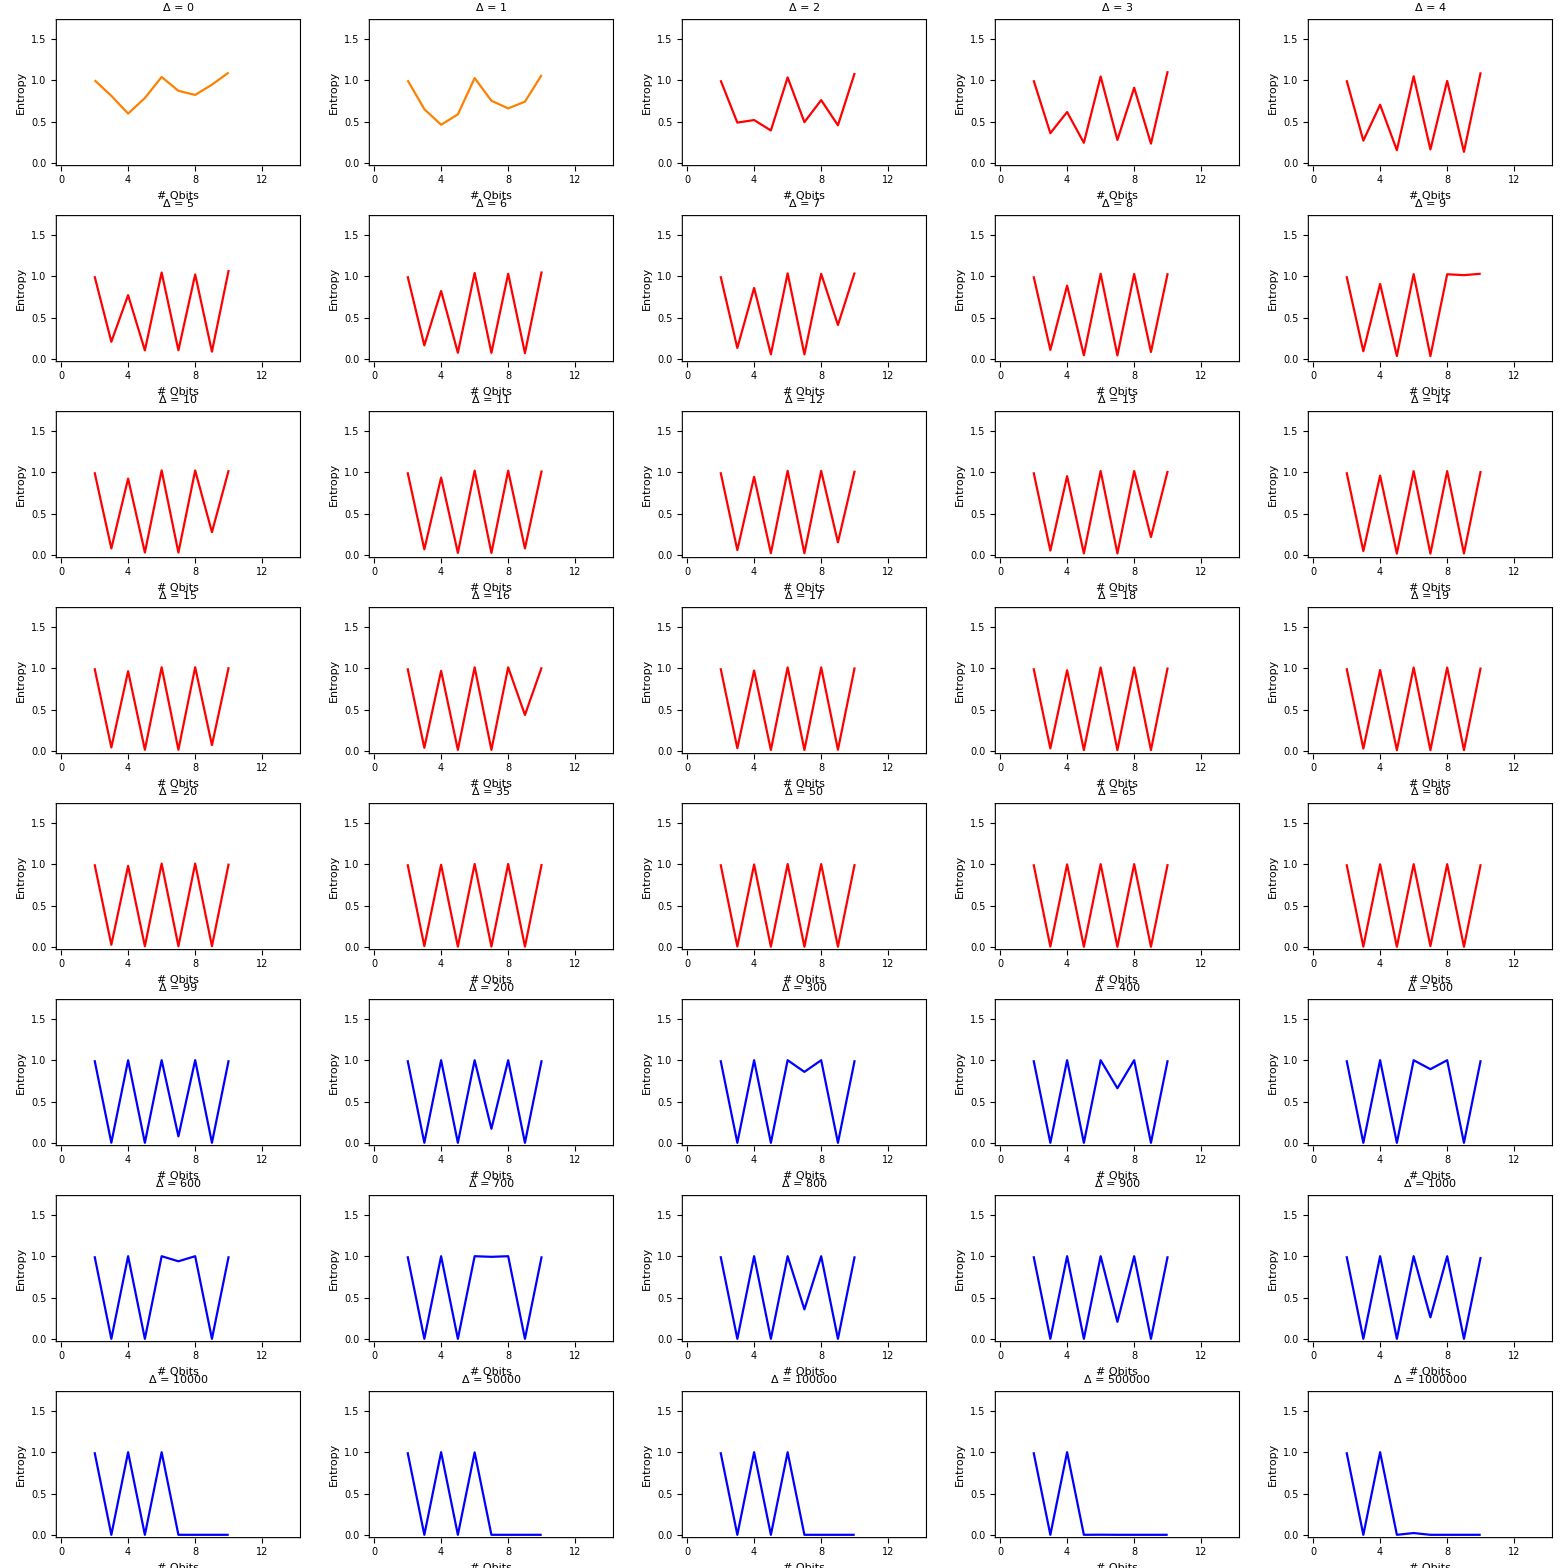

```mathematica
saveG = Grid[{{ListLinePlot[TabPlotD0,PlotStyle->{Orange},PlotRange->{{0,14},{0,1.7}},PlotLabel->"Δ = 0",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD1,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Orange},PlotLabel->"Δ = 1",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD2,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 2",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD3,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 3",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD4,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 4",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},{ListLinePlot[TabPlotD5,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 5",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD6,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 6",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD7,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 7",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD8,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 8",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD9,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 9",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},
{ListLinePlot[TabPlotD10,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 10",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD11,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 11",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD12,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 12",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD13,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 13",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD14,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 14",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},
{ListLinePlot[TabPlotD15,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 15",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD16,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 16",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD17,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 17",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD18,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 18",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD19,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 19",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},
{ListLinePlot[TabPlotD20,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 20",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD35,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 35",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD50,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 50",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD65,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 65",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD80,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 80",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},{ListLinePlot[TabPlotD99,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 99",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD200,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 200",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD300,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 300",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD400,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 400",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD500,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 500",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},{ListLinePlot[TabPlotD600,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 600",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD700,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 700",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD800,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 800",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD900,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 900",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD1000,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 1000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},{ListLinePlot[TabPlotD10000,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 10000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD50000,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 50000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD100000,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 100000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD500000,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 500000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD1000000,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 1000000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]}},Spacings->{0.5,0.5}]
```

### Entropy vs. Proportion

#### Data

```mathematica
TabPlotD2N2={{1,1.0}};
TabPlotD2N3={{1,0.48669228723541275}};
TabPlotD2N4={{1,0.9999999999999998},{2,0.5176968120114405}};
TabPlotD2N5={{1,0.6181807055619779},{2,0.3918921435975606}};
TabPlotD2N6={{1,1.0},{2,0.6163997910254666},{3,1.0338704626980264}};
TabPlotD2N7={{1,0.6797360167947817},{2,0.38245399122845763},{3,0.4923003876622739}};
TabPlotD2N8={{1,0.9999999999999998},{2,0.6586289583268314},{3,1.05318561784557},{4,0.759239059440172}};
TabPlotD2N9={{1,0.7141390317929663},{2,0.3895081801069867},{3,0.5467224206389489},{4,0.4542222093974362}};
TabPlotD2N10={{1,1.0},{2,0.6821780126859136},{3,1.0648005568144754},{4,0.8270098599324982},{5,1.0878965581128939}};
TabPlotD5N2={{1,1.0}};
TabPlotD5N3={{1,0.2063028633098469}};
TabPlotD5N4={{1,1.0000000000000002},{2,0.7707208759079682}};
TabPlotD5N5={{1,0.23449668007160338},{2,0.10249625903665743}};
TabPlotD5N6={{1,0.9999999999999998},{2,0.8985928709207399},{3,1.0450159350202544}};
TabPlotD5N7={{1,0.2393921556091671},{2,0.0919179440226802},{3,0.10384357052211132}};
TabPlotD5N8={{1,0.9999999999999999},{2,0.9409953088989063},{3,1.0591461999140153},{4,1.0210754400983058}};
TabPlotD5N9={{1,0.24023110596468994},{2,0.09090885071105777},{3,0.10405172978199453},{4,0.08701831508343962}};
TabPlotD5N10={{1,1.0},{2,0.9568382640734711},{3,1.0632450217194302},{4,1.0514859416865903},{5,1.0748626958770482}};
TabPlotD10N2={{1,1.0}};
TabPlotD10N3={{1,0.07703987497884077}};
TabPlotD10N4={{1,0.9999999999999998},{2,0.9227056909492158}};
TabPlotD10N5={{1,0.08045702218384654},{2,0.027769570940299245}};
TabPlotD10N6={{1,1.0},{2,0.9848628553649326},{3,1.0218693733412636}};
TabPlotD10N7={{1,0.08061954022187995},{2,0.026222759851529668},{3,0.027263634654827826}};
TabPlotD10N8={{1,0.9999999999999996},{2,0.9941810917971922},{3,1.0236619082910223},{4,1.020878006266136}};
TabPlotD10N9={{1,0.28982809997295045},{2,0.2672754682721766},{3,0.275255251909186},{4,0.27493826567399626}};
TabPlotD10N10={{1,1.0000000000000004},{2,0.9959097926910355},{3,1.0238237436974684},{4,1.0237535902396857},{5,1.0252130299871274}};
TabPlotD49N2={{1,1.0}};
TabPlotD49N3={{1,0.005266067095937375}};
TabPlotD49N4={{1,0.9999999999999998},{2,0.9967447372574556}};
TabPlotD49N5={{1,0.005277214087446428},{2,0.0015355372234466657}};
TabPlotD49N6={{1,1.0000000000000002},{2,1.000225662048807},{3,1.0015194778373018}};
TabPlotD49N7={{1,0.0054295702279460595},{2,0.0017684215244358485},{3,0.001772427838548018}};
TabPlotD49N8={{1,1.0},{2,1.000321463158213},{3,1.0015239680417989},{4,1.0015201410205004}};
TabPlotD49N9={{1,0.005277236441625875},{2,0.001530552780436249},{3,0.0015331635180338677},{4,0.001528158315216602}};
TabPlotD49N10={{1,0.9999999999999989},{2,1.0003252950196904},{3,1.0015239909722664},{4,1.0015259782204777},{5,1.001528129658723}};
```

#### Delta = 2

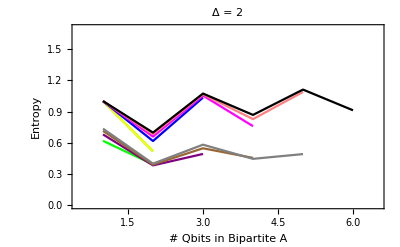

```mathematica
plotD2 = Show[ListLinePlot[TabPlotD2N2,PlotStyle->{Red},PlotRange->{{0.5,6.5},{0,1.7}},PlotLabel->"Δ = 2",FrameLabel->{{"Entropy",None},{"# Qbits in Bipartite A",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD2N4,PlotStyle->{Green}],
ListLinePlot[TabPlotD2N3,PlotStyle->{Orange}],
ListLinePlot[TabPlotD2N4,PlotStyle->{Yellow}],
ListLinePlot[TabPlotD2N5,PlotStyle->{Green}],
ListLinePlot[TabPlotD2N6,PlotStyle->{Blue}],
ListLinePlot[TabPlotD2N7,PlotStyle->{Purple}],
ListLinePlot[TabPlotD2N8,PlotStyle->{Magenta}],
ListLinePlot[TabPlotD2N9,PlotStyle->{Brown}],
ListLinePlot[TabPlotD2N10,PlotStyle->{Pink}],
ListLinePlot[TabPlotD2N11,PlotStyle->{Gray}],
ListLinePlot[TabPlotD2N12,PlotStyle->{Black}]]
```

#### Delta = 5

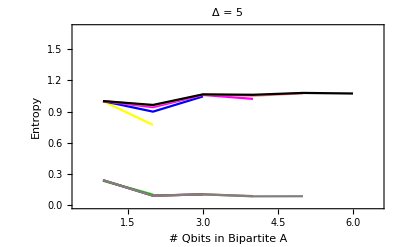

```mathematica
plotD5 = Show[ListLinePlot[TabPlotD5N2,PlotStyle->{Red},PlotRange->{{0.5,6.5},{0,1.7}},PlotLabel->"Δ = 5",FrameLabel->{{"Entropy",None},{"# Qbits in Bipartite A",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD5N3,PlotStyle->{Orange}],
ListLinePlot[TabPlotD5N4,PlotStyle->{Yellow}],
ListLinePlot[TabPlotD5N5,PlotStyle->{Green}],
ListLinePlot[TabPlotD5N6,PlotStyle->{Blue}],
ListLinePlot[TabPlotD5N7,PlotStyle->{Purple}],
ListLinePlot[TabPlotD5N8,PlotStyle->{Magenta}],
ListLinePlot[TabPlotD5N9,PlotStyle->{Brown}],
ListLinePlot[TabPlotD5N10,PlotStyle->{Pink}],
ListLinePlot[TabPlotD5N11,PlotStyle->{Gray}],
ListLinePlot[TabPlotD5N12,PlotStyle->{Black}]]
```

#### Delta = 10

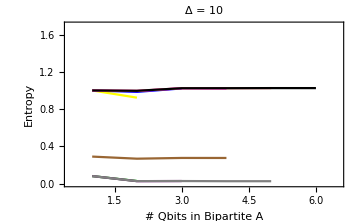

```mathematica
plotD10 = Show[ListLinePlot[TabPlotD10N2,PlotStyle->{Red},PlotRange->{{0.5,6.5},{0,1.7}},PlotLabel->"Δ = 10",FrameLabel->{{"Entropy",None},{"# Qbits in Bipartite A",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD10N3,PlotStyle->{Orange}],
ListLinePlot[TabPlotD10N4,PlotStyle->{Yellow}],
ListLinePlot[TabPlotD10N5,PlotStyle->{Green}],
ListLinePlot[TabPlotD10N6,PlotStyle->{Blue}],
ListLinePlot[TabPlotD10N7,PlotStyle->{Purple}],
ListLinePlot[TabPlotD10N8,PlotStyle->{Magenta}],
ListLinePlot[TabPlotD10N9,PlotStyle->{Brown}],
ListLinePlot[TabPlotD10N10,PlotStyle->{Pink}],
ListLinePlot[TabPlotD10N11,PlotStyle->{Gray}],
ListLinePlot[TabPlotD10N12,PlotStyle->{Black}]]
```

#### Delta = 49

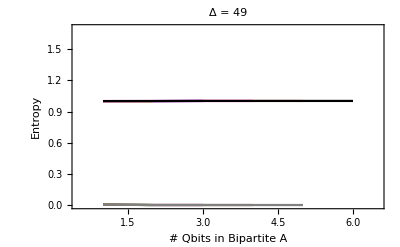

```mathematica
plotD49 = Show[ListLinePlot[TabPlotD49N2,PlotStyle->{Red},PlotRange->{{0.5,6.5},{0,1.7}},PlotLabel->"Δ = 49",FrameLabel->{{"Entropy",None},{"# Qbits in Bipartite A",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD49N3,PlotStyle->{Orange}],
ListLinePlot[TabPlotD49N4,PlotStyle->{Yellow}],
ListLinePlot[TabPlotD49N5,PlotStyle->{Green}],
ListLinePlot[TabPlotD49N6,PlotStyle->{Blue}],
ListLinePlot[TabPlotD49N7,PlotStyle->{Purple}],
ListLinePlot[TabPlotD49N8,PlotStyle->{Magenta}],
ListLinePlot[TabPlotD49N9,PlotStyle->{Brown}],
ListLinePlot[TabPlotD49N10,PlotStyle->{Pink}],
ListLinePlot[TabPlotD49N11,PlotStyle->{Gray}],
ListLinePlot[TabPlotD49N12,PlotStyle->{Black}]]
```

#### Conclusion Graph

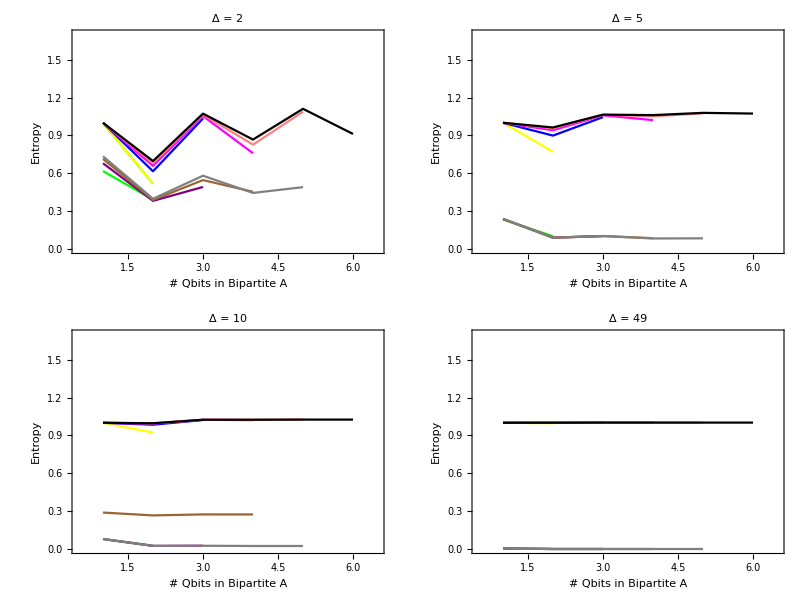

```mathematica
saveG2= Grid[{{plotD2,plotD5},{plotD10,plotD49}},Spacings->{0.5, 0.5}]
```

### Schmidt Coefficients vs. N

#### Data

```mathematica
SDTabPlotD0={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.8660254037844383,0.4999999999999998}},{4,{0.9472135954999581,0.22360679774997919,0.2236067977499789,0.052786404500041746}},{5,{0.8991933699455015,0.42170038694705636,0.10566243270259382,0.049553177598664566}},{6,{0.7057887247804754,0.7057887247804753,0.03050031721195931,0.030500317211959223,0.03050031721195915,0.030500317211959064,0.0013180564060721249,0.0013180564060720022}},{7,{0.873588831604449,0.4737362617399409,0.09657386142538914,0.05237079325914529,0.016282945203699776,0.008830036868431205,0.0018000537974039812,0.0009761465875733952}},{8,{0.9176377014704858,0.2748456761106442,0.27484567611064364,0.08232022894838152,0.005952021315872298,0.0059520213158722746,0.0017827159021086877,0.001782715902108679,0.0017827159021086669,0.0017827159021086309,0.0005339490265527326,0.000533949026552727,3.860625788130543*10^-05,1.1563128925982282*10^-05,1.1563128925954904*10^-05,3.463323251181596*10^-06}},{9,{0.8688547772803632,0.468160915170574,0.14043704759344436,0.07567103092993048,0.018665367678276465,0.010057371890857945,0.0030169703816192556,0.0022611702439396253,0.0016256198985548235,0.0012183756807700396,0.00036548348638771764,0.0001969317404257258,4.857609705325156*10^-05,2.617402890163937*10^-05,7.851580991626406*10^-06,4.230630294829089*10^-06}},{10,{0.7034559547166884,0.7034559547166866,0.050673574845128806,0.050673574845128716,0.05067357484512859,0.050673574845128515,0.0036502799789633815,0.0036502799789633247,0.0006184235833606406,0.000618423583360608,0.0006184235833605996,0.0006184235833605748,4.454825284707259*10^-05,4.45482528470158*10^-05,4.454825284696955*10^-05,4.4548252846967126*10^-05,4.454825284694818*10^-05,4.454825284691844*10^-05,4.4548252846901146*10^-05,4.454825284683811*10^-05,3.209041319168886*10^-06,3.209041319159945*10^-06,3.209041319079186*10^-06,3.2090413190250626*10^-06,5.436697577109613*10^-07,5.436697577006291*10^-07,3.916334776647504*10^-08,3.9163347719620524*10^-08,3.916334767580687*10^-08,3.916334765510701*10^-08,2.821138959275033*10^-09,2.821138418612423*10^-09}}};
SDTabPlotD1={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9128709291752767,0.408248290463863}},{4,{0.9659258262890684,0.14942924536134247,0.1494292453613423,0.1494292453613422}},{5,{0.9378422307163599,0.3330182992968798,0.08513434199919148,0.04798860730154238}},{6,{0.7062514170867399,0.7062514170867399,0.03215120295316442,0.03215120295316436,0.009360449017965271,0.009360449017965143,0.009360449017964935,0.009360449017964892}},{7,{0.9022386111036104,0.4210843722270596,0.08155330034486898,0.041931646219838754,0.014292081525517863,0.005538114082114887,0.0025616684848630725,0.0016552645646633222}},{8,{0.9451924199343312,0.1884648707209401,0.18846487072094004,0.1884648707209397,0.004058155213305773,0.0040581552133057645,0.004058155213305747,0.00203452230271954,0.00043630952756460573,0.0004363095275645432,0.00043630952756446327,0.00017352860521675534,0.0001735286052166422,0.00017352860521661881,0.00017352860521660778,0.00017352860521652533}},{9,{0.9149231980736708,0.38048942179850015,0.11598068371579688,0.06611315715004261,0.01618916149743233,0.006644558832160155,0.0027124117055383197,0.0017702767373712744,0.001677240845294227,0.0011189559687929986,0.00022870027765114283,0.00011846643379217647,9.369681384432104*10^-05,4.0558988738571994*10^-05,2.3851367842295102*10^-05,1.6824634368147283*10^-05}},{10,{0.7046836085783961,0.7046836085783955,0.05355963584078546,0.05355963584078542,0.016611455130678535,0.016611455130678517,0.01661145513067843,0.0166114551306784,0.0006381693905261439,0.0006381693905260988,0.00020758679017612004,0.0002075867901760807,0.0002075867901760765,0.0002075867901760642,5.069403392077117*10^-05,5.0694033920736614*10^-05,1.1532080564346702*10^-05,1.1532080564310605*10^-05,1.1532080564298916*10^-05,1.153208056429645*10^-05,5.934532604188239*10^-06,5.934532604186954*10^-06,1.9870274586584043*10^-06,1.987027458642531*10^-06,1.9870274586284337*10^-06,1.987027458595766*10^-06,9.515732895663009*10^-07,9.515732895260622*10^-07,9.5157328952524*10^-07,9.515732895247795*10^-07,9.515732895193607*10^-07,9.515732894993881*10^-07}}};
SDTabPlotD2={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9456942250523721,0.32505758367186816}},{4,{0.9567064232130149,0.24437855678560116,0.111785376428106,0.1117853764281055}},{5,{0.9656109834096804,0.2462028229276219,0.08046839311240432,0.022459661862254666}},{6,{0.7059376566882115,0.7059376566882105,0.03817136684869913,0.03817136684869908,0.013423611210004948,0.013423611210004925,0.0038442534440412917,0.003844253444040804}},{7,{0.949868862889132,0.30491919468633505,0.06526356835708229,0.01722526039246181,0.013955137374100219,0.00458227379359215,0.0012376407379893438,0.00033200664224499995}},{8,{0.9245812562091754,0.3257995714317223,0.13952069071344528,0.13952069071344508,0.006944291821507706,0.002814374331881608,0.0027222828768962387,0.0027222828768961793,0.0006415109032426639,0.0006415109032426502,0.00040006744732709956,0.00034784417959063613,0.0001057465810280098,0.00010574658102792273,2.8466269662575735*10^-05,2.8466269662559946*10^-05}},{9,{0.9587083789638549,0.2662371492381839,0.09526841201884209,0.02628242965394783,0.014298641208760536,0.004399426678204529,0.001950913577462706,0.001071201581062353,0.0005410911705391381,0.0002850590395234111,0.00021757238060302313,6.458263215501052*10^-05,5.119828833729592*10^-05,1.4707942838755848*10^-05,3.891687042990271*10^-06,1.0418306153109063*10^-06}},{10,{0.7034872585549741,0.7034872585549737,0.06722965467592225,0.06722965467592217,0.023292308266787184,0.02329230826678717,0.006533212752832191,0.006533212752832173,0.0007409832086435143,0.0007409832086434537,0.0002744380963349633,0.0002744380963349335,7.694728352669592*10^-05,7.694728352669556*10^-05,7.349453720065279*10^-05,7.349453719984685*10^-05,1.7535155695808806*10^-05,1.7535155695798136*10^-05,7.450049894769936*10^-06,7.4500498947044*10^-06,4.766254154026436*10^-06,4.766254153996665*10^-06,2.1773423640379753*10^-06,2.177342364034848*10^-06,2.028485311835898*10^-06,2.0284853117951788*10^-06,6.252506428786261*10^-07,6.252506428784639*10^-07,1.683464077169122*10^-07,1.6834640770474302*10^-07,4.512387397933991*10^-08,4.5123873949638684*10^-08}}};
SDTabPlotD3={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9653505678131907,0.2609564738088524}},{4,{0.9376638480795846,0.3241189740782596,0.08869441540210546,0.08869441540210529}},{5,{0.981800859232187,0.17958232763219667,0.06081905961030255,0.010876690731150383}},{6,{0.7054326717723792,0.7054326717723686,0.04742724978892462,0.047427249788923924,0.010583899307975838,0.010583899307975493,0.0018391979196828838,0.0018391979196828588}},{7,{0.9771649877820698,0.20834248760959187,0.0396778478318841,0.010741977297276871,0.0068284686661495095,0.002338176372530001,0.00041554465654466434,7.137403892382801*10^-05}},{8,{0.877876839426602,0.454030104231235,0.10748627498127698,0.10748627498127349,0.007697186765919621,0.00408972214366996,0.001617936178508904,0.0016179361785088958,0.000716271861257034,0.0007162718612569881,0.00020767425079711973,0.0002021491557825612,3.554631714762339*10^-05,3.554631714754228*10^-05,6.100811041525007*10^-06,6.100811041454963*10^-06}},{9,{0.982596952170896,0.17758173661914622,0.052942715131367835,0.009253628884441424,0.008630632069575381,0.001642194912886131,0.00143694073310359,0.000273049617861714,0.00024882168271985416,8.462440990662902*10^-05,4.680867380030876*10^-05,1.5279866432686767*10^-05,1.4056619636150809*10^-05,2.4789026106120203*10^-06,4.244991818479508*10^-07,7.282842650536932*10^-08}},{10,{0.7021613853744506,0.7021613853744455,0.08184256694402771,0.08184256694402717,0.01621059973127205,0.016210599731271893,0.002796391432771844,0.002796391432771825,0.0007382497860769732,0.0007382497860769432,0.00016188687156597385,0.0001618868715659663,8.689722022622975*10^-05,8.689722022622353*10^-05,2.7953636690376058*10^-05,2.7953636690324603*10^-05,1.4284568118523746*10^-05,1.4284568118519845*10^-05,3.590492011826313*10^-06,3.5904920118019108*10^-06,2.447703024374683*10^-06,2.4477030243730713*10^-06,6.226059114638281*10^-07,6.226059109741367*10^-07,6.210061024409001*10^-07,6.21006102439459*10^-07,1.0779647185846408*10^-07,1.0779647185803314*10^-07,1.8501251439308442*10^-08,1.8501251423872878*10^-08,3.174344725071598*10^-09,3.1743446677149176*10^-09}}};
SDTabPlotD4={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9767927852067352,0.21418649529806613}},{4,{0.9162899993467782,0.3869748755443048,0.0730174047558232,0.07301740475582308}},{5,{0.9897588529833848,0.1358166038688985,0.043574658525653016,0.00570194606319067}},{6,{0.705257030161492,0.7052570301614735,0.050525680764183276,0.0505256807641818,0.00766306323838726,0.007663063238387153,0.0009769610662543448,0.0009769610662542535}},{7,{0.9884835734502473,0.14931332875148812,0.02330803896839423,0.007240769083871958,0.0029696625989100375,0.0011050952242498253,0.00014487349006767357,1.8411052655748414*10^-05}},{8,{0.8315453544145186,0.5421805194594769,0.0851728758237779,0.08517287582377607,0.0065463231415053835,0.00430370579537362,0.0009303475419556109,0.0009303475419555341,0.0005669964384888877,0.0005669964384888425,9.965572027167141*10^-05,9.883597808023827*10^-05,1.264632906454373*10^-05,1.2646329064487367*10^-05,1.6063780234154042*10^-06,1.6063780231637672*10^-06}},{9,{0.9911796340866758,0.12932019181634688,0.028379673168468636,0.004405173680325347,0.0036372326940301305,0.0009040262051342469,0.0005859746863917324,0.0001147478805896719,7.384253637760452*10^-05,2.7066351860322388*10^-05,9.377932070715406*10^-06,3.510695660395167*10^-06,3.442074376147931*10^-06,4.4152630976508173*10^-07,5.607035883526808*10^-08,7.1218471246502305*10^-09}},{10,{0.7028213092977937,0.7028213092977365,0.07702212936527862,0.07702212936527233,0.01037943723419883,0.010379437234197944,0.0013197318824894,0.0013197318824892923,0.0005599058349945729,0.0005599058349945472,8.320541327842929*10^-05,8.320541327842154*10^-05,6.151518505554485*10^-05,6.151518505553656*10^-05,1.058426057355741*10^-05,1.0584260573554472*10^-05,7.692327325601804*10^-06,7.692327325598126*10^-06,1.2122611641268935*10^-06,1.212261164110239*10^-06,9.767922136517393*10^-07,9.76792213648233*10^-07,1.5448183030545619*10^-07,1.544818301025626*10^-07,1.5416371031594245*10^-07,1.541637103157002*10^-07,1.9646942180177995*10^-08,1.9646942179908417*10^-08,2.49562320430284*10^-09,2.495623203593144*10^-09,3.169859889680948*10^-10,3.1698598381034694*10^-10}}};
SDTabPlotD5={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9836651208336212,0.18000813885871303}},{4,{0.8959228787710284,0.43554621022630813,0.06173205833330606,0.061732058333305834}},{5,{0.9936977267524141,0.10750908747151953,0.03155981223085899,0.0032561035118882724}},{6,{0.7053779942380084,0.7053779942379845,0.04909571211269515,0.049095712112693576,0.005583657266896201,0.005583657266895948,0.0005648614471075684,0.0005648614471074487}},{7,{0.9933225298187516,0.11435099048801671,0.014457396820216739,0.004768323602529329,0.001463461877693526,0.0005517961656670249,5.7123511793344326*10^-05,5.772107485353695*10^-06}},{8,{0.7972549226252169,0.5955310231822811,0.06959052015376334,0.06959052015376328,0.005109606358945019,0.0038294568222037766,0.0005529212162833948,0.0005529212162832517,0.0003990621458837336,0.00039906214588367417,4.995132588033653*10^-05,4.978568278882398*10^-05,5.043913178849311*10^-06,5.043913178816735*10^-06,5.095450876765048*10^-07,5.095450876341066*10^-07}},{9,{0.9946606511813046,0.10182269160366463,0.016550684617940757,0.0022841634466317104,0.0016798064089468684,0.0005520171362774616,0.00023593089331564915,5.571293143734189*10^-05,2.380166513328819*10^-05,9.392924262549944*10^-06,2.404475450862255*10^-06,9.652822848551852*10^-07,9.57842785336174*10^-07,9.792265356576775*10^-08,9.895512728452306*10^-09,9.996533048627057*10^-10}},{10,{0.7039181270729771,0.703918127072659,0.06671401685846899,0.06671401685843881,0.006918613153010732,0.006918613153007541,0.0006991156198461684,0.000699115619845847,0.0003886694897829511,0.0003886694897827525,4.365588973731746*10^-05,4.365588973729709*10^-05,3.686472754631381*10^-05,3.686472754629009*10^-05,4.412167220670316*10^-06,4.41216722067007*10^-06,3.699346630320521*10^-06,3.6993466303191856*10^-06,4.2656805156534876*10^-07,4.265680515629841*10^-07,3.736835725927854*10^-07,3.736835725906288*10^-07,4.3147682560485865*10^-08,4.314768249137756*10^-08,4.3104280479092605*10^-08,4.310428047771077*10^-08,4.360075939836281*10^-09,4.360075939203495*10^-09,4.4046298860123177*10^-10,4.404629370002999*10^-10,4.449579965154852*10^-11,4.449579474644596*10^-11}}};
SDTabPlotD6={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.987994690488427,0.15448783630654317}},{4,{0.8777498366000636,0.4731575830728068,0.053278165927809755,0.05327816592780911}},{5,{0.9957997674306294,0.0884629169326059,0.02351844931047797,0.002004508645533298}},{6,{0.7056095955199589,0.7056095955198942,0.04579920895410846,0.04579920895410468,0.004172338901094696,0.004172338901094367,0.0003503676332028773,0.00035036763320283384}},{7,{0.9956822945178548,0.09227156886195172,0.009578896074056606,0.0031990279723025116,0.0008049227341208283,0.0002972907669515941,2.54260874148929*10^-05,2.1340499522949718*10^-06}},{8,{0.7739210542320833,0.6278349185592643,0.05849491776980353,0.058494917769800724,0.003943093364500074,0.003203863988751835,0.00034646259137382905,0.0003464625913736461,0.0002754899628084196,0.0002754899628083204,2.687382094662827*10^-05,2.6831269000615407*10^-05,2.254738012368358*10^-06,2.2547380123099188*10^-06,1.8921885294472842*10^-07,1.8921885282260485*10^-07}},{9,{0.9961113222504031,0.08433258303549834,0.02478223324978129,0.00558860328009377,0.0021071699236247634,0.0004690927523643739,0.0004191221690762489,0.00014203221836369938,3.544150182282295*10^-05,1.190259020468211*10^-05,9.729871402719459*10^-06,2.9683441458668747*10^-06,8.277277240165715*10^-07,2.4910123850302816*10^-07,7.078365419386755*10^-08,5.940973067493609*10^-09}},{10,{0.7047621223843655,0.7047621223836845,0.057326768919793,0.057326768919737765,0.004873635936868227,0.004873635936863478,0.00040903454221482015,0.00040903454221442203,0.00026778975450138237,0.0002677897545011341,2.424602408165104*10^-05,2.4246024081627935*10^-05,2.178864633604893*10^-05,2.1788646336031417*10^-05,2.035076358655887*10^-06,2.035076358651917*10^-06,1.8225659254565496*10^-06,1.8225659254554294*10^-06,1.671763371016311*10^-07,1.6717633709361193*10^-07,1.529465528579126*10^-07,1.529465528572447*10^-07,1.4037983501218714*10^-08,1.4037983365666386*10^-08,1.403069585680389*10^-08,1.4030695856785629*10^-08,1.1781757771944463*10^-09,1.1781757696207992*10^-09,9.887323464673668*10^-11,9.887317983819212*10^-11,8.297511426438309*10^-12,8.297459832198973*10^-12}}};
SDTabPlotD7={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.990854763568497,0.1349327147641273}},{4,{0.8619678509654437,0.5026336610104652,0.04674840489916013,0.04674840489916002}},{5,{0.997019383778105,0.07500028084914541,0.01804405742225797,0.00131081464005475}},{6,{0.7058466136947465,0.7058466136946673,0.04207412093203815,0.042074120932033346,0.0032051976971868438,0.003205197697186347,0.00023019825036157715,0.00023019825036156197}},{7,{0.9969824188117795,0.07730263252109305,0.006723418175112045,0.002211818735479195,0.00048314398898083934,0.0001717724528213117,1.25199316389098*10^-05,8.989611319031935*10^-07}},{8,{0.7580729995721746,0.648260972561206,0.050330961852503714,0.05033096185245256,0.0030811761128793223,0.002637086280059295,0.00022858980104319344,0.0002285898010431677,0.00019296807716954876,0.00019296807716951257,1.5481234497458984*10^-05,1.5468087493543316*10^-05,1.1113562398496903*10^-06,1.111356239799974*10^-06,7.979190862667138*10^-08,7.97919085542309*10^-08}},{9,{0.9622654342879544,0.2626544284105327,0.06844878416975697,0.018751017330889984,0.004406173584632273,0.0012016655734471975,0.00031618781496352315,0.0002767849267262413,8.621560219821335*10^-05,7.552309306201004*10^-05,1.9675775095059662*10^-05,5.388932918580342*10^-06,1.4292326150367018*10^-06,3.910974568409705*10^-07,1.0262050198300404*10^-07,2.8081103230887683*10^-08}},{10,{0.7053420211254818,0.7053420211253287,0.04979526106490605,0.0497952610648952,0.003600371501940694,0.003600371501939906,0.0002585044973466159,0.00025850449734656004,0.00018795883195262886,0.00018795883195257736,1.428539980479688*10^-05,1.428539980479581*10^-05,1.3270925065459947*10^-05,1.3270925065458922*10^-05,1.0257186574422433*10^-06,1.0257186573945551*10^-06,9.5113186908348*10^-07,9.511318690832682*10^-07,7.280053698269177*10^-08,7.28005369824702*10^-08,6.828756839854622*10^-08,6.828756835621905*10^-08,5.228529196325384*10^-09,5.228529164930837*10^-09,5.227013362722134*10^-09,5.227013362184562*10^-09,3.7540394025953065*10^-10,3.754039398918682*10^-10,2.6952997875534437*10^-11,2.6952688974794446*10^-11,1.9351265141112663*10^-12,1.9351240874521736*10^-12}}};
SDTabPlotD8={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9928253927028239,0.11957315586905017}},{4,{0.8483891185855513,0.5260975483128129,0.04157687533280291,0.041576875332802445}},{5,{0.9977799011996001,0.06505535789824969,0.01422174379508317,0.0009006521380295303}},{6,{0.7060529724444566,0.7060529724443552,0.03850708154173026,0.038507081541724934,0.0025257963514765613,0.002525796351476281,0.00015851292954727333,0.00015851292954720004}},{7,{0.9977700258944274,0.066542603409615,0.004946074369686775,0.0015767537855349908,0.0003105310712680014,0.00010525941291319867,6.6834449495716114*10^-06,4.193795359982615*10^-07}},{8,{0.7470520612557078,0.6618226529664899,0.04412008898943709,0.0441200889894102,0.0024526078104597764,0.0021738730523525973,0.00015771744041906256,0.00015771744041891944,0.00013847524894195165,0.00013847524894191436,9.460884167284452*10^-06,9.456194862131675*10^-06,5.935856108839497*10^-07,5.935856108805886*10^-07,3.724518699060472*10^-08,3.7245186977280635*10^-08}},{9,{0.9955617429556143,0.07163829335479086,0.060767084121265386,0.004381063220005752,0.003575404437148951,0.0002515152472145813,0.00022429220429084716,0.0002023925517943439,1.5775941483686223*10^-05,1.454513908346258*10^-05,1.2346405664819343*10^-05,8.891030703192416*10^-07,7.978176172460715*10^-07,5.6147811975443*10^-08,5.006711778880367*10^-08,3.5231456508051516*10^-09}},{10,{0.7057404339751915,0.7057404339734492,0.04384927332063781,0.043849273320529604,0.002762711959081481,0.002762711959074656,0.00017335213105018063,0.00017335213104975237,0.00013529476867762526,0.0001352947686772986,8.872963907329135*10^-06,8.87296390730791*10^-06,8.406621371118532*10^-06,8.4066213711022*10^-06,5.567620631456882*10^-07,5.567620631416284*10^-07,5.269377745108305*10^-07,5.269377745100058*10^-07,3.4700777060032354*10^-08,3.470077591819969*10^-08,3.306313741365883*10^-08,3.306313737435732*10^-08,2.1777452202472307*10^-09,2.1777450757748572*10^-09,2.1773675977221464*10^-09,2.177367597714186*10^-09,1.3664687272520937*10^-10,1.3664687213493013*10^-10,8.57421502745311*10^-12,8.573907009602224*10^-12,5.379885438048733*10^-13,5.379680077254424*10^-13}}};
SDTabPlotD9={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9942331331239328,0.10724027694187017}},{4,{0.8367142273449532,0.5450804552276767,0.03739384365994097,0.03739384365994006}},{5,{0.9982833916007228,0.05743302380928356,0.011458794662085091,0.0006433157630529548}},{6,{0.7062226988048489,0.7062226988047773,0.03528944286569851,0.035289442865695235,0.002035202347957103,0.0020352023479568203,0.00011343049336521648,0.0001134304933651836}},{7,{0.9982826831724935,0.05844668569340101,0.003779085181904676,0.0011571190901063244,0.00021068953243220522,6.77886585402339*10^-05,3.81539188160053*10^-06,2.126311032743595*10^-07}},{8,{0.7391624228550621,0.6712301374277028,0.0392539681082111,0.039253968108180666,0.0019890469736064337,0.0018068021772053935,0.00011298243351337018,0.00011298243351319586,0.00010192468446931746,0.00010192468446909582,6.0755147753688486*10^-06,6.073640508747892*10^-06,3.385593965710839*10^-07,3.3855939652639166*10^-07,1.8867274542658322*10^-08,1.886727441165721*10^-08}},{9,{0.7585523011062805,0.6492405201117918,0.0420022091470528,0.03622960155377648,0.002193463190465081,0.0018774448036045612,0.00012205962221427032,0.0001129258629014497,0.00010414770699587336,9.63549251558761*10^-05,6.224470122514631*10^-06,5.368993005306749*10^-06,3.4834274302055787*10^-07,3.0046472876826373*10^-07,1.9412730692341388*10^-08,1.6744544887740506*10^-08}},{10,{0.7060211910221192,0.7060211910217759,0.039106000359656425,0.039106000359637516,0.002184879114230535,0.002184879114229468,0.00012176010923500734,0.00012176010923494848,9.988737955659834*10^-05,9.988737955655401*10^-05,5.766541973772703*10^-06,5.766541973769844*10^-06,5.5328364460893764*10^-06,5.532836446089053*10^-06,3.213637563795518*10^-07,3.2136375637775015*10^-07,3.081357913283092*10^-07,3.0813579132812927*10^-07,1.7834456952274904*10^-08,1.7834456951795692*10^-08,1.717178461082448*10^-08,1.7171784583137775*10^-08,9.939957774478239*10^-10,9.939957398057961*10^-10,9.938868156486553*10^-10,9.938868156245507*10^-10,5.539385836196331*10^-11,5.539385639568792*10^-11,3.087032245419748*10^-12,3.0869909510519533*10^-12,1.7203233066330572*10^-13,1.7199170023512115*10^-13}}};
SDTabPlotD10={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9952701201997094,0.09714621885413725}},{4,{0.8266414667396874,0.5606770995285527,0.03394904660449431,0.03394904660449377}},{5,{0.998632997785587,0.05141361351070874,0.009410148651845186,0.0004745333419713484}},{6,{0.7063596917076918,0.7063596917076844,0.03245280931343567,0.032452809313435256,0.0016715492689812733,0.001671549268981215,8.37933584548915*10^-05,8.37933584548795*10^-05}},{7,{0.9986351554244424,0.05213491613717088,0.002986586867253757,0.0009123893132481895,0.0001497970983089263,4.763508976236842*10^-05,2.471506477654372*10^-06,1.2389769250010091*10^-07}},{8,{0.7333542649179341,0.6780028580428461,0.03534562117057559,0.03534562117053668,0.0016409049735546508,0.0015173607705646793,8.351760164280814*10^-05,8.351760164272045*10^-05,7.682503615313201*10^-05,7.68250361530311*10^-05,4.0666944466119465*10^-06,4.065873147775156*10^-06,2.0383859234691087*10^-07,2.0383859226882658*10^-07,1.0217539346538867*10^-08,1.0217539326866426*10^-08}},{9,{0.9777451164714349,0.20374923034467013,0.048898807300613426,0.010198468519851336,0.002318713092507617,0.00048310129495633604,0.00011621204980795525,0.00010855160356731157,2.4212120603637098*10^-05,2.2619329940911162*10^-05,5.428084928801105*10^-06,1.1320458318610148*10^-06,2.7290068017411847*10^-07,5.69037376313557*10^-08,1.3679421198753321*10^-08,2.8523557782917985*10^-09}},{10,{0.7062249051410111,0.7062249051379919,0.03525954623908676,0.03525954623893599,0.0017703548003321422,0.0017703548003245681,8.87405201164724*10^-05,8.874052011609285*10^-05,7.549351781239143*10^-05,7.549351781207567*10^-05,3.894806532608379*10^-06,3.894806532591897*10^-06,3.7692031192400045*10^-06,3.7692031192384866*10^-06,1.9523139276455357*10^-07,1.952313927601931*10^-07,1.8885390762920713*10^-07,1.8885390759365586*10^-07,9.759503632116483*10^-09,9.759503189971449*10^-09,9.466410822601854*10^-09,9.466410821328187*10^-09,4.89238414430066*10^-10,4.892383622150165*10^-10,4.892029216058298*10^-10,4.892029213944457*10^-10,2.452346743430604*10^-11,2.4523465339608836*10^-11,1.2293876970967226*10^-12,1.2291298814580486*10^-12,6.161715312647225*10^-14,6.15952039846402*10^-14}}};
SDTabPlotD11={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9960542150101808,0.08874683521373285}},{4,{0.8179040728123178,0.5736745432601418,0.03106803898132374,0.031068038981323657}},{5,{0.998885308895178,0.04654251305080607,0.007861592129278132,0.000359890946872099}},{6,{0.706469959571492,0.7064699595712617,0.029970729490565763,0.029970729490555778,0.001395548655943548,0.0013955486559430713,6.356861413335348*10^-05,6.356861413333159*10^-05}},{7,{0.9988883079292371,0.04707343415701121,0.0024039294470597303,0.000669484433973455,0.00010952009500016244,3.155925882961928*10^-05,1.4471487842908542*10^-06,6.591687988035754*10^-08}},{8,{0.7289695901743266,0.683032740683769,0.03214069924700897,0.03214069924696339,0.001374355623556817,0.0012879264003949854,6.338820943000151*10^-05,6.338820942998187*10^-05,5.915690774746384*10^-05,5.915690774743934*10^-05,2.8187150080982355*10^-06,2.818326837628287*10^-06,1.2838616061757974*10^-07,1.2838616057135066*10^-07,5.8478425024038025*10^-09,5.847842361693284*10^-09}},{9,{0.9957456296831811,0.08016373013058996,0.045246169270606165,0.003644565304444127,0.0019693198898665092,0.00015838649434701577,8.969257138050203*10^-05,8.475302103870366*10^-05,7.213608712762039*10^-06,6.821920120263492*10^-06,3.850769860380125*10^-06,3.101255550277251*10^-07,1.7591211227739676*10^-07,1.4153256850339775*10^-08,8.01264326749844*10^-09,6.446668786875155*10^-10}},{10,{0.7063768201077767,0.7063768200992553,0.032087990608444854,0.03208799060805774,0.0014632251355468384,0.0014632251355291815,6.664837867031309*10^-05,6.664837866950889*10^-05,5.826612833761246*10^-05,5.82661283369035*10^-05,2.7183239616933366*10^-06,2.718323961660455*10^-06,2.6468282036628513*10^-06,2.646828203631986*10^-06,1.2381716856079932*10^-07,1.238171685271541*10^-07,1.2052524912374308*10^-07,1.205252491223207*10^-07,5.629312728779168*10^-09,5.629312183948307*10^-09,5.48978319327012*10^-09,5.489783192442487*10^-09,2.5642206086021976*10^-10,2.5642196826449144*10^-10,2.564091919034232*10^-10,2.5640919188866934*10^-10,1.1679748410741015*10^-11,1.1679748233497611*10^-11,5.320326600824904*10^-13,5.319692806264185*10^-13,2.428668013581802*10^-14,2.423194953839303*10^-14}}};
SDTabPlotD12={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9966604896834949,0.08165701625614419}},{4,{0.8102782173684728,0.5846454516023963,0.028626092807093193,0.028626092807092614}},{5,{0.9990699992823109,0.042528248902691204,0.0070989690580341705,0.000298693196573552}},{6,{0.7065591064551175,0.706559106455107,0.027799826611354987,0.02779982661135477,0.0011816484253612041,0.001181648425361187,4.932272204830037*10^-05,4.932272204828019*10^-05}},{7,{0.9990763004556279,0.04292244043225131,0.001981591997460685,0.0005252759269428647,8.272371479032174*10^-05,2.2571671412089918*10^-05,9.476401987811677*10^-07,3.955420147812803*10^-08}},{8,{0.7255856022079313,0.6868670943643144,0.029466413584831375,0.029466413584720474,0.0011664987546457799,0.0011043596002781539,4.919940510756255*10^-05,4.9199405107477126*10^-05,4.642321889681176*10^-05,4.642321889661012*10^-05,2.012429406028158*10^-06,2.0122339778165087*10^-06,8.399587584558084*10^-08,8.399587572349702*10^-08,3.5059256276923285*10^-09,3.505925625118914*10^-09}},{9,{0.9899076090887483,0.13544371289055904,0.04126996118140771,0.005648955874327487,0.0016568131285677374,0.00022665844532454354,6.914979341815794*10^-05,6.591076476875964*10^-05,9.459890614013423*10^-06,9.017846257495171*10^-06,2.747681016350436*10^-06,3.760842806576422*10^-07,1.1486246216640614*10^-07,1.5719202743875794*10^-08,4.7942866732842344*10^-09,6.561094556437196*10^-10}},{10,{0.7064928861069639,0.7064928860992615,0.02943272898596282,0.02943272898564195,0.0012294756397842838,0.0012294756397708765,5.131747060155932*10^-05,5.131747060099998*10^-05,4.5813187715546066*10^-05,4.581318771504917*10^-05,1.95129486799678*10^-06,1.9512948679756663*10^-06,1.9086018364860937*10^-06,1.9086018364666966*10^-06,8.144584856400464*10^-08,8.144584855565623*10^-08,7.96474329673264*10^-08,7.964743296645398*10^-08,3.3950760385844354*10^-09,3.395076038124346*10^-09,3.32442352169374*10^-09,3.3244234525769268*10^-09,1.4171311697119675*10^-10,1.4171301973483325*10^-10,1.4170810635145519*10^-10,1.4170810611813253*10^-10,5.915006709540447*10^-12,5.915005388042053*10^-12,2.469066310555088*10^-13,2.4684342941303103*10^-13,1.0413343041849736*10^-14,1.0304921660485153*10^-14}}};
SDTabPlotD13={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9971383851306294,0.07559788951472537}},{4,{0.8035802303942833,0.594012557741648,0.026532004868603746,0.02653200486860347}},{5,{0.99921729818409,0.03914250295663717,0.005710231207808835,0.00022075219650601}},{6,{0.7066317220803429,0.7066317220798524,0.02589559936994233,0.025895599369924464,0.0010127988016281155,0.0010127988016274752,3.901249314741213*10^-05,3.9012493147376415*10^-05}},{7,{0.9992198596826919,0.039454703167591205,0.0016668261094864528,0.0004643738291796095,6.422320104184029*10^-05,1.8334929591644022*10^-05,7.32080158568873*10^-07,2.8200288975432518*10^-08}},{8,{0.7229230535371042,0.6898553934929449,0.02720176312966631,0.02720176312959576,0.0010016685877543357,0.0009559179897117153,3.892536104228342*10^-05,3.892536104223*10^-05,3.7045123920346534*10^-05,3.7045123920285534*10^-05,1.4736966382143993*10^-06,1.4735928387562162*10^-06,5.676402718746574*10^-08,5.6764027181269455*10^-08,2.186471111880275*10^-09,2.1864709920611602*10^-09}},{9,{0.9837239937780456,0.17551605207651588,0.037861594224028426,0.006757242888257729,0.0014105644566234786,0.00025165978236407023,5.433043604433761*10^-05,5.2144115486199035*10^-05,9.693086174861021*10^-06,9.303400735407742*10^-06,2.006824118981136*10^-06,3.581577712354417*10^-07,7.738244773350126*10^-08,1.3809706187563477*10^-08,2.9806685144153834*10^-09,5.319313927968111*10^-10}},{10,{0.706583453975237,0.7065834539406896,0.02717944690252275,0.027179446901193796,0.0010475141960716024,0.0010475141960203747,4.034881796296466*10^-05,4.034881796099143*10^-05,3.661797964205257*10^-05,3.661797964026131*10^-05,1.435098625640097*10^-06,1.4350986255702603*10^-06,1.4085518001801273*10^-06,1.4085518001487678*10^-06,5.5278100219548484*10^-08,5.5278100205131685*10^-08,5.4247449089197086*10^-08,5.424744908665489*10^-08,2.1272369867022305*10^-09,2.127236986320476*10^-09,2.089535507638635*10^-09,2.0895355075928716*10^-09,8.194040105515821*10^-11,8.194028332504087*10^-11,8.19382520261982*10^-11,8.193825084286525*10^-11,3.156230436728972*10^-12,3.1562295650045437*10^-12,1.2166543067554501*10^-13,1.2151180796317681*10^-13,4.682844957161201*10^-15,4.463880200095926*10^-15}}};
SDTabPlotD14={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.997521435711986,0.07036323823629981}},{4,{0.7976606390532244,0.602092660173242,0.024717741307708152,0.024717741307707267}},{5,{0.9993299304226206,0.03626569366703746,0.004945518358571428,0.00017740500330744685}},{6,{0.7066913911212702,0.7066913911212541,0.024217906826924276,0.02421790682692378,0.0008773367004407812,0.0008773367004407712,3.137404973082508*10^-05,3.137404973081351*10^-05}},{7,{0.9993321225595198,0.03651284548048135,0.0014140411147189281,0.0003445390097394519,5.057168228126899*10^-05,1.2589695693632823*10^-05,4.5411605197583676*10^-07,1.6239357093043097*10^-08}},{8,{0.7207925155123918,0.6922287122900844,0.02525969194419566,0.025259691944009392,0.0008689687624481079,0.0008345766508425524,3.131085195604287*10^-05,3.131085195590011*10^-05,3.0001973311465163*10^-05,3.000197331140113*10^-05,1.1031180559995504*10^-06,1.1030603359896876*10^-06,3.944708464112108*10^-08,3.94470845811593*10^-08,1.4106260505416824*10^-09,1.4106260152623317*10^-09}},{9,{0.9993005220815301,0.0357474805518123,0.010903904059957085,0.0012380992416095582,0.0003901396498075533,4.427274975768735*10^-05,4.282102252994118*10^-05,1.3521676996027688*10^-05,1.5317526506417732*10^-06,4.835151943397258*10^-07,4.662046541041802*10^-07,5.4768200384432496*10^-08,1.668010197087158*10^-08,1.9585081852348285*10^-09,5.969321581370497*10^-10,2.1346288542604573*10^-11}},{10,{0.7066554325922408,0.7066554325824251,0.025244445667517226,0.025244445667166607,0.0009031226754250743,0.0009031226754125253,3.229564484361192*10^-05,3.229564484316318*10^-05,2.96966729662588*10^-05,2.9696672965848905*10^-05,1.0779699451271037*10^-06,1.0779699451120845*10^-06,1.0608812207287295*10^-06,1.0608812207167304*10^-06,3.854820544051759*10^-08,3.854820543832646*10^-08,3.7932910629208*10^-08,3.7932910628681436*10^-08,1.3775241562767121*10^-09,1.377524154754315*10^-09,1.3564790336724795*10^-09,1.3564790336374637*10^-09,4.926125448092039*10^-11,4.9261159368341585*10^-11,4.9260224264953084*10^-11,4.926022121188869*10^-11,1.7615788675603856*10^-12,1.7615780367816321*10^-12,6.29949462024781*10^-14,6.298421031149643*10^-14,2.56681494130087*10^-15,2.2526610756837235*10^-15}}};
SDTabPlotD15={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9978329861655989,0.06579765740391608}},{4,{0.7923979456930752,0.6091267112472585,0.023131637496014112,0.023131637496013612}},{5,{0.9994197272807608,0.03378577692127956,0.004325396129872895,0.00014473491719496067}},{6,{0.7067408657647428,0.7067408657641543,0.02273234624376354,0.022732346243744688,0.0007670967858525657,0.0007670967858518636,2.559868895772026*10^-05,2.5598688957695447*10^-05}},{7,{0.9994215305073517,0.03398490668151104,0.0012243991077774705,0.0003598647557078563,4.087179433750594*10^-05,1.2234581755764879*10^-05,4.308851572198362*10^-07,1.4379696492181371*10^-08}},{8,{0.7190622709688614,0.6941445591247172,0.023576058655053765,0.02357605865503009,0.0007606803393872461,0.0007343495729802385,2.5551854995848568*10^-05,2.5551854995830093*10^-05,2.4618637550965445*10^-05,2.4618637550959414*10^-05,8.416730654077187*10^-07,8.416396677175977*10^-07,2.8086811038261224*10^-08,2.80868110023054*10^-08,9.37269618245342*10^-10,9.372695549745991*10^-10}},{9,{0.9962039718106674,0.08040725707010397,0.033225684151983986,0.002682189386223438,0.0010812833472384166,8.726322813349776*10^-05,3.608195838929449*10^-05,3.497949632131641*10^-05,2.9119304628172527*10^-06,2.8232430706209926*10^-06,1.1666139598639328*10^-06,9.417401166640426*10^-08,3.8957882226209346*10^-08,3.1444439407203582*10^-09,1.3000431958067849*10^-09,1.0493156176066294*10^-10}},{10,{0.7067135583899661,0.7067135583883024,0.02356536236900649,0.023565362368950987,0.0007866382756213852,0.0007866382756195332,2.6250484878715197*10^-05,2.625048487865302*10^-05,2.4396275173793492*10^-05,2.4396275173728545*10^-05,8.248296642619367*10^-07,8.248296642599017*10^-07,8.13494778788956*10^-07,8.134947787888062*10^-07,2.752496189471484*10^-08,2.7524961840773457*10^-08,2.7144434117217747*10^-08,2.714443411714801*10^-08,9.180378197335299*10^-10,9.180378194469678*10^-10,9.058219764942954*10^-10,9.058219764685198*10^-10,3.0635851864714585*10^-11,3.063574069889715*10^-11,3.06353462255832*10^-11,3.063533077032252*10^-11,1.0223306022709792*10^-12,1.0223305915633522*10^-12,3.412291928645788*10^-14,3.4080339078573835*10^-14,1.1384542039814007*10^-15,9.111372246610842*10^-16}}};
SDTabPlotD16={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9980896662918946,0.06178202037271468}},{4,{0.7876931381153899,0.6153005784259011,0.02173382564898102,0.02173382564897973}},{5,{0.999492500717128,0.031625611881596134,0.003814102842729434,0.00011959449120680705}},{6,{0.7067822513712015,0.7067822513706165,0.021410077047581112,0.021410077047563276,0.0006762399138915458,0.0006762399138908476,2.1153377562106443*10^-05,2.115337756209053*10^-05}},{7,{0.9994940320284045,0.031788338945999216,0.001060140727379978,0.00023746857948392058,3.3164220610329995*10^-05,7.5529307442785365*10^-06,2.384046953103519*10^-07,7.457504962002872*10^-09}},{8,{0.7176386501884698,0.6957131891516184,0.022102606623464235,0.02210260662335816,0.0006712351671534629,0.0006507473721747019,2.1118033574372818*10^-05,2.1118033574247945*10^-05,2.043851146934652*10^-05,2.0438511469221038*10^-05,6.530802204715784*10^-07,6.530602128273156*10^-07,2.0428613256308017*10^-08,2.0428613192715784*10^-08,6.390188227981275*10^-10,6.390187646788478*10^-10}},{9,{0.9555629100969077,0.2931240866330018,0.029880411113447188,0.009167310904275739,0.0009141887647738733,0.0002804310252033416,2.8595743271570688*10^-05,2.782404147443022*10^-05,8.771843941598207*10^-06,8.53515371351387*10^-06,8.700370783451864*10^-07,2.66927065699852*10^-07,2.7227589161909605*10^-08,8.353373022449182*10^-09,8.516950860320291*10^-10,2.6129843520478446*10^-10}},{10,{0.7067611587184236,0.706761158635905,0.022094926876425613,0.022094926873845882,0.0006913119634961418,0.0006913119634154217,2.162464253449897*10^-05,2.162464253197403*10^-05,2.0273749809680572*10^-05,2.027374980731722*10^-05,6.4152075563919*10^-07,6.415207555642225*10^-07,6.338030849239463*10^-07,6.338030848491802*10^-07,2.0067150703420568*10^-08,2.006715069647846*10^-08,1.9824454813590642*10^-08,1.982445481132158*10^-08,6.274581305974475*10^-10,6.274581290936046*10^-10,6.201203528489718*10^-10,6.201203528143705*10^-10,1.962748683104552*10^-11,1.9627405887914125*10^-11,1.962725458989011*10^-11,1.9627228875217666*10^-11,6.139589579902639*10^-13,6.13958010294575*10^-13,1.9278777943449225*10^-14,1.9156628405302053*10^-14,6.007431983740077*10^-16,5.750652991846068*10^-16}}};
SDTabPlotD17={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.998303567360102,0.05822359827505281}},{4,{0.7834651582156493,0.6207595444889545,0.02049309381223071,0.020493093812228348}},{5,{0.999552312767644,0.029726871243024224,0.003387798526834799,9.9940458285109*10^-05}},{6,{0.7068171631525669,0.7068171631521812,0.020227133990951832,0.0202271339909408,0.0006005091590397174,0.0006005091590393428,1.7677470432040884*10^-05,1.7677470432027446*10^-05}},{7,{0.9995533565289857,0.029862032755100645,0.0010003365530714978,0.0005870259583995574,2.9541141397315162*10^-05,1.748250382052608*10^-05,5.994345418305667*10^-07,1.764699687333831*10^-08}},{8,{0.7164536761136338,0.6970136010893069,0.02080235522652616,0.02080235522598255,0.0005965467905787415,0.0005803741844493099,1.7650374889806297*10^-05,1.765037488969519*10^-05,1.7146279909405456*10^-05,1.714627990929569*10^-05,5.143435804661242*10^-07,5.143312216470722*10^-07,1.5140795334337133*10^-08,1.51407952674996*10^-08,4.4570349695790723*10^-10,4.4570340346878295*10^-10}},{9,{0.999442104018261,0.029428942205598985,0.015763277064294288,0.0008487002422548522,0.00046419932531271117,2.4982978774954215*10^-05,2.4391646485985365*10^-05,1.3392844126248755*10^-05,7.182081517864093*10^-07,3.942416280335816*10^-07,3.8457995000146404*10^-07,2.1138380825528686*10^-08,1.1324973603206157*10^-08,6.222557388846085*10^-10,3.334938034721393*10^-10,9.817268651761903*10^-12}},{10,{0.7068006230703564,0.7068006227633741,0.02079672806928617,0.020796728060253643,0.0006123160693757638,0.0006123160691098062,1.8024905145328646*10^-05,1.8024905137499557*10^-05,1.7022272871075525*10^-05,1.702227286368602*10^-05,5.062367381734439*10^-07,5.062367379608826*10^-07,5.008594767567269*10^-07,5.008594765408526*10^-07,1.4902223919405813*10^-08,1.4902223894608205*10^-08,1.4743184679852618*10^-08,1.4743184673463594*10^-08,4.385416944176095*10^-10,4.385416934444665*10^-10,4.339988168650165*10^-10,4.339988164312222*10^-10,1.2909596142242419*10^-11,1.2909575439256285*10^-11,1.290946374460894*10^-11,1.2909463259563485*10^-11,3.800227326057328*10^-13,3.8002255843729075*10^-13,1.1235269470127926*10^-14,1.1129002866284352*10^-14,4.570061753185393*10^-16,3.2930920060567835*10^-16}}};
SDTabPlotD18={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.998483642818851,0.055049205472892326}},{4,{0.779647273082199,0.6256185718952818,0.019384685646135384,0.01938468564613319}},{5,{0.9996020802927555,0.028044620144128007,0.0030287355831627857,8.435717211353402*10^-05}},{6,{0.7068468479017008,0.7068468479013003,0.019163645070366244,0.019163645070355444,0.0005367463902572314,0.0005367463902569728,1.4921231280223581*10^-05,1.492123128021824*10^-05}},{7,{0.9996031378287722,0.028157500686533946,0.0008261176554334688,0.00019740599175415972,2.296759919721597*10^-05,5.560500978526292*10^-06,1.590793285901669*10^-07,4.4223846546794716*10^-09}},{8,{0.7154571078007511,0.6981035742572774,0.019646499490911427,0.019646499490372425,0.0005335676513559561,0.0005206358269980859,1.4900170048402174*10^-05,1.4900170048273929*10^-05,1.4519956822697968*10^-05,1.4519956822440021*10^-05,4.104869778116633*10^-07,4.1047913324219016*10^-07,1.1411188170487616*10^-08,1.1411188105084839*10^-08,3.1722240838673337*10^-10,3.172223718677501*10^-10}},{9,{0.9996057522025418,0.02779119864706279,0.00392495362273078,0.0007559061246855356,0.00010913057365297824,2.1013303818981082*10^-05,2.064317913722807*10^-05,2.9689798289497513*10^-06,5.739153077912087*10^-07,8.253402307972055*10^-08,8.073706792022178*10^-08,1.5954093887535877*10^-08,2.244803534904088*10^-09,4.4351174854927125*10^-10,6.24214131201134*10^-11,1.7352684959360292*10^-12}},{10,{0.7068337013103352,0.7068337013052286,0.01964230141778501,0.019642301417643053,0.0005461242124666914,0.0005461242124627445,1.5181842234038386*10^-05,1.5181842233927534*10^-05,1.44252831264031*10^-05,1.4425283126297202*10^-05,4.046903621299075*10^-07,4.0469036212708654*10^-07,4.0086639606420353*10^-07,4.008663960619486*10^-07,1.1250089346355506*10^-08,1.1250089344092739*10^-08,1.1143337041487438*10^-08,1.114333704132785*10^-08,3.126654646094259*10^-10,3.126654645839249*10^-10,3.097763401465911*10^-10,3.0977634010940215*10^-10,8.691924156469958*10^-12,8.691910853119973*10^-12,8.691867408184527*10^-12,8.691862950193018*10^-12,2.416289953256401*10^-13,2.4162889399631864*10^-13,6.759454427603561*10^-15,6.670548994353192*10^-15,1.8673039644522432*10^-16,1.3463919352380844*10^-16}}};
SDTabPlotD19={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9986366321091439,0.05220035449790609}},{4,{0.7761842080650287,0.6299696693149132,0.01838873151856385,0.018388731518563392}},{5,{0.9996439371255822,0.02654369011211653,0.0027251266880003724,7.188762742526189*10^-05}},{6,{0.70687227546019,0.7068722754594021,0.018203108245011916,0.018203108244991557,0.0004825712533541844,0.0004825712533536209,1.2708109437966738*10^-05,1.27081094379534*10^-05}},{7,{0.9996448289870947,0.026639184131830473,0.0007364468539702457,0.00016431322531985522,1.9394882970595458*10^-05,4.378675464287296*10^-06,1.1797870017140519*10^-07,3.1069058587242047*10^-09}},{8,{0.7146111962633597,0.6990261462316757,0.01861227524676529,0.01861227524645227,0.00047999105453553357,0.0004695300917778799,1.2691535862591917*10^-05,1.2691535862452148*10^-05,1.2400463828556836*10^-05,1.240046382851798*10^-05,3.315183238696306*10^-07,3.3151322213839393*10^-07,8.730191957161072*10^-09,8.730191929419852*10^-09,2.2990157828540298*10^-10,2.299012154362109*10^-10}},{9,{0.9996315482986352,0.026326857079740137,0.006570318434870465,0.0006815854760457414,0.0001730501545869545,1.7948697816963442*10^-05,1.761944378528369*10^-05,4.481043522555128*10^-06,4.640300562712423*10^-07,1.1800259522267006*10^-07,1.1569384354523183*10^-07,1.2219420271977907*10^-08,3.0471297066734098*10^-09,3.217866881820931*10^-10,8.026147443363738*10^-11,2.113609130266687*10^-12}},{10,{0.7068616987712686,0.7068616987031974,0.018609092654671658,0.01860909265287956,0.0004901123971710833,0.0004901123971238846,1.2906640069214063*10^-05,1.2906640067970828*10^-05,1.2327237879732745*10^-05,1.232723787854519*10^-05,3.27300822050486*10^-07,3.2730082202000866*10^-07,3.24531350303336*10^-07,3.245313502871901*10^-07,8.61915431312308*10^-09,8.619154307322284*10^-09,8.54594587752852*10^-09,8.545945876701507*10^-09,2.2693136203942522*10^-10,2.2693136110167902*10^-10,2.250492670206219*10^-10,2.250492667861762*10^-10,5.976232495811329*10^-12,5.976053373260866*10^-12,5.976019705255924*10^-12,5.97586743638838*10^-12,1.5737393591073786*10^-13,1.573736434783603*10^-13,4.212913873937257*10^-15,4.119307279582605*10^-15,1.0913572788108592*10^-16,7.045841610483651*10^-17}}};
SDTabPlotD20={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9987676835701926,0.049629771869629045}},{4,{0.7730298930979009,0.6338872504984906,0.01748911136267896,0.017489111362678528}},{5,{0.9996794933656161,0.025196129675323795,0.002462069969188348,6.168563475065682*10^-05}},{6,{0.7068942065703794,0.7068942065698554,0.017331773130086565,0.01733177313007356,0.0004361636421064443,0.00043616364210596236,1.0910955697050678*10^-05,1.0910955697039941*10^-05}},{7,{0.9996802406787914,0.025277657659816658,0.0006608574976059992,0.0001392883941849469,1.6532572531046742*10^-05,3.5219990826030597*10^-06,8.98023411411506*10^-08,2.2464907361502362*10^-09}},{8,{0.7138871531696509,0.6998139000645645,0.01768145789664639,0.01768145789610413,0.0004340471257518402,0.00042549584612746065,1.0897768361075067*10^-05,1.0897768360945962*10^-05,1.0671932238437126*10^-05,1.0671932238198936*10^-05,2.70624776468361*10^-07,2.706213852456783*10^-07,6.7698376841661236*10^-09,6.76983761457112*10^-09,1.6935187838137584*10^-10,1.6935185366916104*10^-10}},{9,{0.9996869935409547,0.025009439441611728,0.0006649779459856712,1.946951093280552*10^-05,1.6635472717747537*10^-05,5.668872305819923*10^-06,4.87093817101038*10^-07,1.4180751225077916*10^-07,1.2185890417126883*10^-08,3.771360421975761*10^-09,3.0483790782323715*10^-10,9.459231415419148*10^-11,9.43468657074621*10^-11,2.3663265763555177*10^-12,5.919528141317196*10^-14,1.4808081205028028*10^-15}},{10,{0.7068856038170978,0.7068856036123052,0.017679010162264964,0.0176790101571432,0.00044229565240168264,0.0004422956522735439,1.1064311517771884*10^-05,1.1064311514566448*10^-05,1.0614616821872315*10^-05,1.061461681879751*10^-05,2.675075865594041*10^-07,2.6750758648206696*10^-07,2.654686409021534*10^-07,2.6546864082565897*10^-07,6.691875669707086*10^-09,6.691875665545053*10^-09,6.640694932770003*10^-09,6.640694930845346*10^-09,1.6737414564605768*10^-10,1.6737414517182772*10^-10,1.6612126135367887*10^-10,1.661212613065192*10^-10,4.187051089560465*10^-12,4.186989625250412*10^-12,4.186972334443251*10^-12,4.1869504476526136*10^-12,1.0474064580592373*10^-13,1.0474032541760017*10^-13,2.735201355289249*10^-15,2.4955035421807758*10^-15,7.061648726317787*10^-17,6.554464026509767*10^-17}}};
SDTabPlotD35={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9995937425611412,0.028501751395508795}},{4,{0.7460815326713032,0.6657024170718095,0.010065746658606734,0.010065746658604937}},{5,{0.9998970879664649,0.014323183305659919,0.0008122569415265988,1.1611943634515651*10^-05}},{6,{0.7070354964198757,0.7070354964179315,0.010039230424672063,0.010039230424644356,0.00014370782433576845,0.00014370782433525397,2.0533888270047776*10^-06,2.0533888268756335*10^-06}},{7,{0.9998955848673904,0.014339415704140502,0.0017772958055899144,0.0002026855191341732,2.5488084337809852*10^-05,2.8960993269895153*10^-06,3.626582422978502*10^-07,5.1819131649187956*10^-09}},{8,{0.7093361780744278,0.7047254973212103,0.010102449809863346,0.010102449809436346,0.00014346731534749891,0.0001425349688108146,2.052376520832048*10^-06,2.0523765207502382*10^-06,2.0383845166545633*10^-06,2.0383845165050015*10^-06,2.9255415860694063*10^-08,2.9255376837919422*10^-08,4.180197415777485*10^-10,4.1801973614683797*10^-10,5.97292973108077*10^-12,5.9729212028881256*10^-12}},{9,{0.9998979099831165,0.014287271854635306,0.0002084585697963818,3.175249463611855*10^-06,2.978600177437235*10^-06,6.448543834926394*10^-07,4.53704819663323*10^-08,9.214063358171658*10^-09,6.482897549142938*10^-10,1.3444109750999524*10^-10,9.26317306502819*10^-12,1.9226754984352302*10^-12,1.9209872957392*10^-12,2.747288553360303*10^-14,4.3995682358221785*10^-16,2.2120045456744042*10^-16}},{10,{0.7070345979364219,0.7070345977070472,0.010102308542101633,0.010102308538824262,0.00014434963339630342,0.00014434963334947364,2.062558640523658*10^-06,2.062558639854545*10^-06,2.0346325574465047*10^-06,2.0346325567862616*10^-06,2.9143117056948453*10^-08,2.914311704750556*10^-08,2.9071400581938003*10^-08,2.9071400572497646*10^-08,4.164152466986453*10^-10,4.164152442411223*10^-10,4.153893534331906*10^-10,4.1538935329606374*10^-10,5.94990293421805*10^-12,5.949901943486843*10^-12,5.935345174814309*10^-12,5.935345141966373*10^-12,8.511519384039157*10^-14,8.501599040801121*10^-14,8.499402470780144*10^-14,8.49626385410112*10^-14,1.2563069529095068*10^-15,1.2153055957869395*10^-15,7.063171987734703*10^-17,4.947623971955657*10^-17,1.6045009897027202*10^-17,7.761009770460613*10^-18}}};
SDTabPlotD50={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9998004588152315,0.019976049480630136}},{4,{0.7347182436560904,0.6782989390457925,0.007058743806893851,0.007058743806893239}},{5,{0.9999497897658736,0.010012927180824898,0.00039902446573421296,3.991640090443224*10^-06}},{6,{0.7070716313579263,0.7070716313541937,0.007050046175574766,0.007050046175537367,7.056843694380632*10^-05,7.056843694348318*10^-05,7.057550130160021*10^-07,7.057550129869333*10^-07}},{7,{0.9999497842736748,0.010017981696070849,0.00024306742060351835,9.942373201101193*10^-05,2.4351438402628424*10^-06,9.943467701920857*10^-07,2.4244990480135547*10^-08,2.424744029267625*10^-10}},{8,{0.7082010312585071,0.7059399973916812,0.007071403460778464,0.007071403451197383,7.050905054757722*10^-05,7.028396274094011*10^-05,7.055685737215057*10^-07,7.055685734421996*10^-07,7.032072440877393*10^-07,7.032072437993527*10^-07,7.048100523211714*10^-09,7.048098266900936*10^-09,7.048805047984754*10^-11,7.048797735657082*10^-11,7.049542969344237*10^-13,7.049510069545605*10^-13}},{9,{0.999949988473762,0.010000516809760267,0.00010105802374393249,1.04495045531218*10^-06,1.0106823599263629*10^-06,1.5742514523947344*10^-07,1.045057819924252*10^-08,1.5744079413105627*10^-09,1.0451656646015786*10^-10,1.590992522860958*10^-11,1.045270202408484*10^-12,1.5919759141824146*10^-13,1.591060998213579*10^-13,1.5931407792693457*10^-15,4.7666460022077686*10^-17,2.4121888613493272*10^-17}},{10,{0.7070714377048571,0.7070713988975639,0.00707138047329497,0.007071380085185494,7.072104840744861*10^-05,7.072104452595565*10^-05,7.072812194415727*10^-07,7.072811806227613*10^-07,7.025653060881715*10^-07,7.025652675283573*10^-07,7.034775833494497*10^-09,7.034775447396978*10^-09,7.026314918399018*10^-09,7.026314532977378*10^-09,7.035479457853947*10^-11,7.035479138649721*10^-11,7.027012980583387*10^-11,7.027012595038688*10^-11,7.036156965609895*10^-13,7.036154501395841*10^-13,7.027716103265004*10^-13,7.027715280817585*10^-13,7.06920267221809*10^-15,7.037328819913154*10^-15,7.036860188389912*10^-15,7.027081762778529*10^-15,3.536090746393457*10^-16,7.064204580924131*10^-17,7.064204580924131*10^-17,6.679676502908923*10^-17,1.3769586086727368*10^-17,7.852743922918674*10^-18}}};
SDTabPlotD65={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.999881817617791,0.01537370473703844}},{4,{0.7284752419274291,0.6850290303972477,0.0054336641311375075,0.005433664131133072}},{5,{0.9999703404475812,0.007698205214296498,0.00023634364713177568,1.818404369644834*10^-06}},{6,{0.7070859322140195,0.7070859321599889,0.005429802632837756,0.005429802632422906,4.179117560964814*10^-05,4.179117560652073*10^-05,3.2148961535571983*10^-07,3.2148961532634637*10^-07}},{7,{0.9999700677309314,0.007700627857500706,0.0007486331771049775,5.9056896389343285*10^-05,5.765119438488877*10^-06,4.5431066415951396*10^-07,4.429778728683757*10^-08,3.4077250499553306*10^-10}},{8,{0.7077546934951495,0.7064163895029171,0.005439439040409437,0.005439439022633277,4.177005696352308*10^-05,4.169107800693747*10^-05,3.214369053833905*10^-07,3.2143690506538644*10^-07,3.2079990568115196*10^-07,3.2079990534987*10^-07,2.4710179542019776*10^-09,2.4710176771490075*10^-09,1.9009345972566902*10^-11,1.9008953489852156*10^-11,1.4623480457408914*10^-13,1.4623138329684347*10^-13}},{9,{0.9999704102049877,0.007692539805791636,5.95430327322873*10^-05,4.6741707167506133*10^-07,4.580506006775344*10^-07,5.548355470164532*10^-08,3.595732147386148*10^-09,4.2682173990472857*10^-10,2.7661147072854977*10^-11,3.303760839331751*10^-12,2.1279064632879447*10^-13,2.5444875721580965*10^-14,2.541491024494085*10^-14,2.0855374282010082*10^-16,1.6528807387178183*10^-16,4.962820337992331*10^-17}},{10,{0.707085860663248,0.7070858556694745,0.005439432892950598,0.0054394328545347695,4.1844302713901066*10^-05,4.1844302418376855*10^-05,3.218983000252509*10^-07,3.218982977518471*10^-07,3.206257883140892*10^-07,3.206257860499065*10^-07,2.46824809070095*10^-09,2.468248073277042*10^-09,2.4664931905819416*10^-09,2.4664931719088145*10^-09,1.8987653233112737*10^-11,1.8987641728882125*10^-11,1.8974142878522473*10^-11,1.8974142743931424*10^-11,1.4606741365217043*10^-13,1.4606728301194928*10^-13,1.4596359304269123*10^-13,1.459635773794759*10^-13,1.1841615521991016*10^-15,1.1243108649236682*10^-15,1.1233382655634289*10^-15,1.0699286820881005*10^-15,2.0600333411777118*10^-16,1.7911039892188438*10^-16,7.065149574115727*10^-17,7.065149574115727*10^-17,7.065149574115727*10^-17,2.3771138791308774*10^-19}}};
SDTabPlotD80={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9999219451196948,0.0124941453507707}},{4,{0.7245318384632561,0.6892130337242981,0.004416401114235715,0.004416401114232424}},{5,{0.9999804365765164,0.00625316687011884,0.0001561005501749759,9.75761778225355*10^-07}},{6,{0.7070930014285167,0.7070930013904887,0.004414362458851722,0.004414362458614043,2.7599896989622273*10^-05,2.7599896988168944*10^-05,1.7250609717955503*10^-07,1.7250609717026758*10^-07}},{7,{0.999617024999477,0.02695899749680193,0.006243869540186608,0.00016839298697847254,3.8999533906132396*10^-05,1.0517165644351875*10^-06,2.437566025888888*10^-07,6.5734864076986005*10^-09}},{8,{0.7075346432188868,0.706651019336098,0.004419501993493449,0.004419501986028673,2.7590602142713436*10^-05,2.7556146214540426*10^-05,1.7248686453316763*10^-07,1.7248686444105007*10^-07,1.7226112884107484*10^-07,1.7226112873449474*10^-07,1.0775898661988605*10^-09,1.0775898135491119*10^-09,6.735199720179106*10^-12,6.734956480665329*10^-12,4.209875806138194*10^-14,4.209664259392807*10^-14}},{9,{0.9999804670169095,0.006250123675031248,3.922458783560481*10^-05,2.4850447579609304*10^-07,2.4516329006701913*10^-07,2.425910504700624*10^-08,1.55321429514397*10^-09,1.516253152130527*10^-10,9.708007499273847*10^-12,9.515725333406275*10^-13,6.067821020066185*10^-14,5.955413119074876*10^-15,5.9407594835923*10^-15,3.7180338609850844*10^-17,2.323854180826057*10^-19,1.4524604459560991*10^-21}},{10,{0.7070929908415604,0.7070929477933551,0.004419499962820349,0.004419499693758788,2.762296386977017*10^-05,2.762296218806918*10^-05,1.7265026860309613*10^-07,1.7265025809205108*10^-07,1.721992654671344*10^-07,1.7219925498367857*10^-07,1.0767916863047826*10^-09,1.0767916207453891*10^-09,1.0762865100034985*10^-09,1.0762864443008818*10^-09,6.730210965739252*10^-12,6.730209911586602*10^-12,6.727052786152847*10^-12,6.727052380955599*10^-12,4.206569139088419*10^-14,4.2065502640678155*10^-14,4.204603071184105*10^-14,4.204575203830071*10^-14,3.661860311204487*10^-16,2.901976565105976*10^-16,2.797400220072386*10^-16,2.7162043243882865*10^-16,2.6730427450066726*10^-16,7.065000127319673*10^-17,7.065000127319673*10^-17,2.2797429607900544*10^-17,2.0122031180351026*10^-17,1.837646245934319*10^-17}}};
SDTabPlotD99={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9999490147071024,0.01009791989943159}},{4,{0.7212289969001708,0.6926783157950197,0.003569653887123765,0.0035696538871217588}},{5,{0.9999872324715461,0.005052177393478403,0.0001019667516343898,5.150295598990515*10^-07}},{6,{0.7070977761174844,0.7070977758813184,0.0035685923984885306,0.0035685923972964715,1.8027480388072256*10^-05,1.802748038181301*10^-05,9.105020377093353*10^-08,9.105020374097714*10^-08}},{7,{0.9952072478753775,0.0976577894891489,0.005024557712877714,0.0004930503089883752,2.536496419618445*10^-05,2.4890101745051553*10^-06,1.281091459374117*10^-07,1.2571080008890641*10^-08}},{8,{0.7073862337735091,0.7068091732391724,0.0035712913345306344,0.003571291320429078,1.8023484103033617*10^-05,1.800878156061936*10^-05,9.104341089051281*10^-08,9.104341071134231*10^-08,9.096558822239039*10^-08,9.096558805703788*10^-08,4.596890062270062*10^-10,4.596889964807367*10^-10,2.3218773015783425*10^-12,2.32172085335482*10^-12,1.172617344923911*10^-14,1.1726162025890867*10^-14}},{9,{0.9999872454628113,0.0050505700166963855,2.5576777567380492*10^-05,1.3033601346482426*10^-07,1.291789481966012*10^-07,1.0366964355578832*10^-08,6.582796027240294*10^-10,5.235973935398288*10^-11,3.324730012817887*10^-12,2.651570266703596*10^-13,1.6791994065412846*10^-14,1.3507126652403842*10^-15,1.3258979072917217*10^-15,7.095112241686457*10^-17,5.208741147391626*10^-17,2.2886848256558282*10^-17}},{10,{0.7070977803349905,0.7070977444184628,0.0035712906788936865,0.0035712904974925185,1.8037284491666417*10^-05,1.8037283575475402*10^-05,9.109972021690106*10^-08,9.109971559081349*10^-08,9.094422249498138*10^-08,9.094421787550338*10^-08,4.5946651653790407*10^-10,4.5946649320209095*10^-10,4.593258002334485*10^-10,4.5932577771572665*10^-10,2.3205971806671788*10^-12,2.3205969918701667*10^-12,2.3198863513397354*10^-12,2.3198862328130355*10^-12,1.1723363303157138*10^-14,1.1718292740878274*10^-14,1.1717124766963475*10^-14,1.1716968523462389*10^-14,3.2027664516923553*10^-16,7.200842583832826*10^-17,7.065258541943706*10^-17,7.065258541943706*10^-17,7.065258541943706*10^-17,7.065258541943706*10^-17,7.065258541943706*10^-17,7.065258541943706*10^-17,5.846110718187879*10^-17,7.32395781366866*10^-18}}};
```

#### N=3 Smooth Histogram

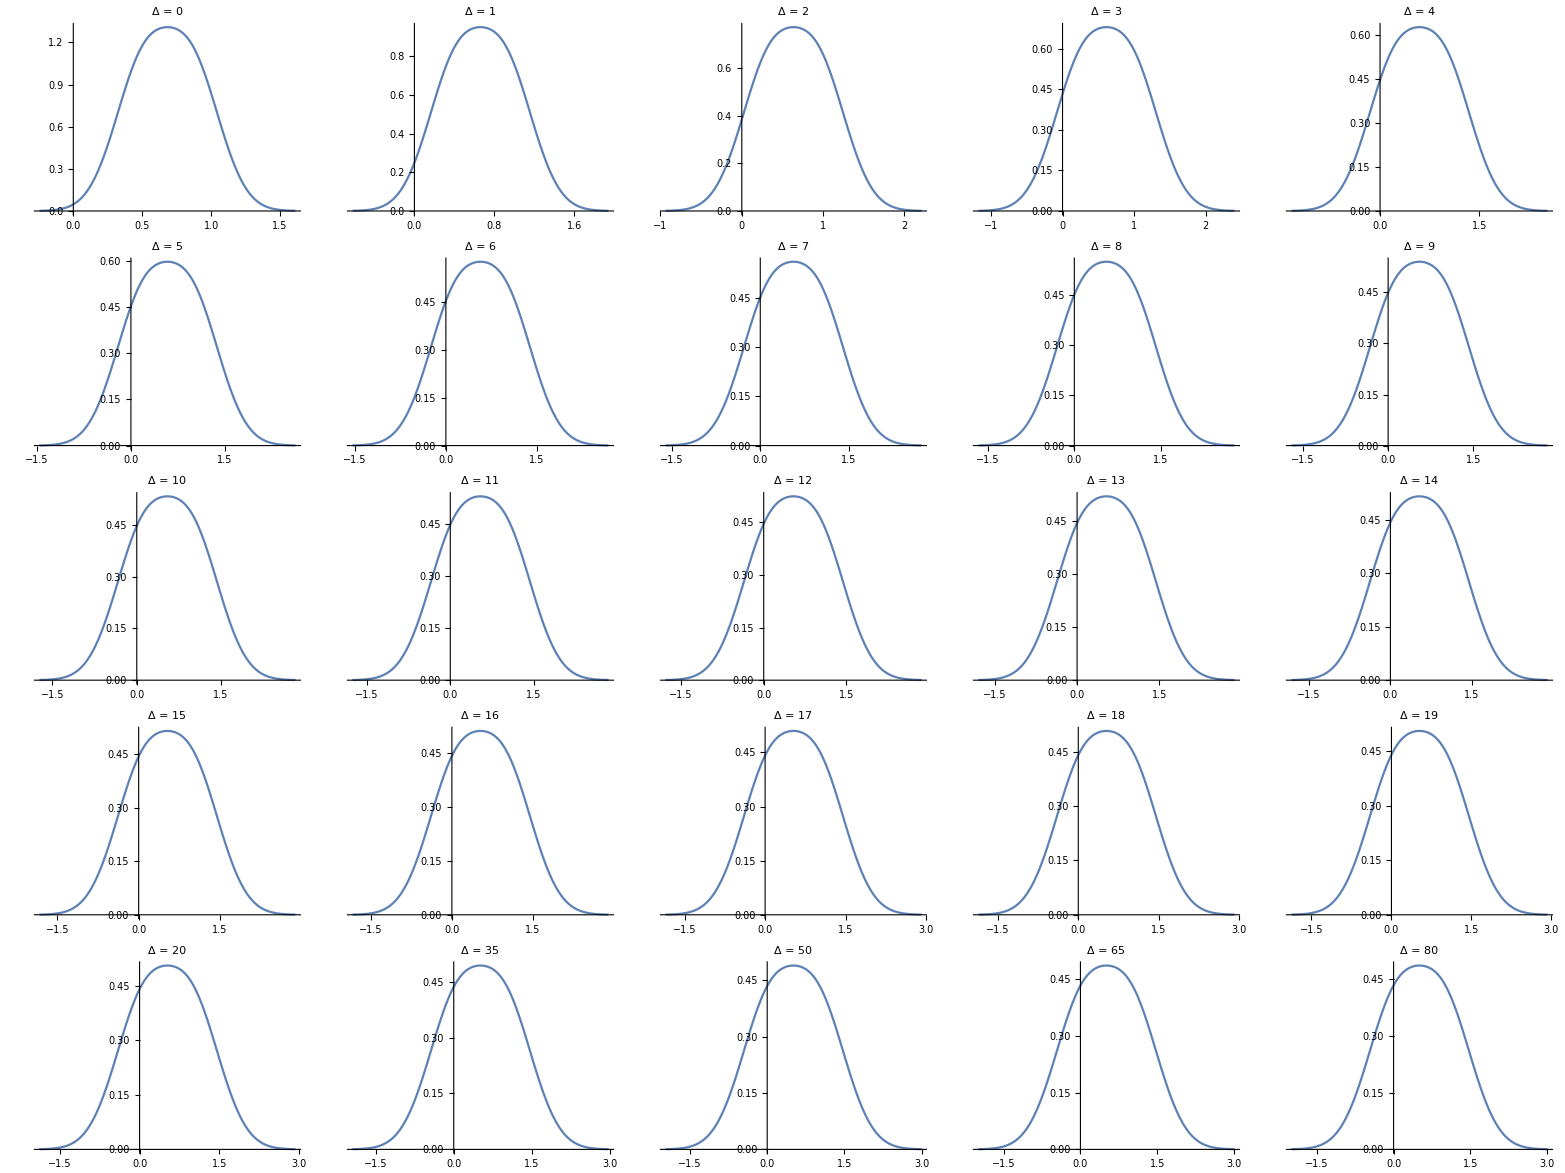

```mathematica
saveGSDN3 = Grid[{{SmoothHistogram[SDTabPlotD0[[2,2]],PlotLabel->"Δ = 0",PlotRange->All],SmoothHistogram[SDTabPlotD1[[2,2]],PlotLabel->"Δ = 1",PlotRange->All],SmoothHistogram[SDTabPlotD2[[2,2]],PlotLabel->"Δ = 2",PlotRange->All],SmoothHistogram[SDTabPlotD3[[2,2]],PlotLabel->"Δ = 3",PlotRange->All],SmoothHistogram[SDTabPlotD4[[2,2]],PlotLabel->"Δ = 4",PlotRange->All]},
{SmoothHistogram[SDTabPlotD5[[2,2]],PlotLabel->"Δ = 5",PlotRange->All],SmoothHistogram[SDTabPlotD6[[2,2]],PlotLabel->"Δ = 6",PlotRange->All],SmoothHistogram[SDTabPlotD7[[2,2]],PlotLabel->"Δ = 7",PlotRange->All],SmoothHistogram[SDTabPlotD8[[2,2]],PlotLabel->"Δ = 8",PlotRange->All],SmoothHistogram[SDTabPlotD9[[2,2]],PlotLabel->"Δ = 9",PlotRange->All]},{SmoothHistogram[SDTabPlotD10[[2,2]],PlotLabel->"Δ = 10",PlotRange->All],SmoothHistogram[SDTabPlotD11[[2,2]],PlotLabel->"Δ = 11",PlotRange->All],SmoothHistogram[SDTabPlotD12[[2,2]],PlotLabel->"Δ = 12",PlotRange->All],SmoothHistogram[SDTabPlotD13[[2,2]],PlotLabel->"Δ = 13",PlotRange->All],SmoothHistogram[SDTabPlotD14[[2,2]],PlotLabel->"Δ = 14",PlotRange->All]},
{SmoothHistogram[SDTabPlotD15[[2,2]],PlotLabel->"Δ = 15",PlotRange->All],SmoothHistogram[SDTabPlotD16[[2,2]],PlotLabel->"Δ = 16",PlotRange->All],SmoothHistogram[SDTabPlotD17[[2,2]],PlotLabel->"Δ = 17",PlotRange->All],SmoothHistogram[SDTabPlotD18[[2,2]],PlotLabel->"Δ = 18",PlotRange->All],SmoothHistogram[SDTabPlotD19[[2,2]],PlotLabel->"Δ = 19",PlotRange->All]},{SmoothHistogram[SDTabPlotD20[[2,2]],PlotLabel->"Δ = 20",PlotRange->All],SmoothHistogram[SDTabPlotD35[[2,2]],PlotLabel->"Δ = 35",PlotRange->All],SmoothHistogram[SDTabPlotD50[[2,2]],PlotLabel->"Δ = 50",PlotRange->All],SmoothHistogram[SDTabPlotD65[[2,2]],PlotLabel->"Δ = 65",PlotRange->All],SmoothHistogram[SDTabPlotD80[[2,2]],PlotLabel->"Δ = 80",PlotRange->All]}},Spacings->{0.5,0.5}]
```

#### N=6 Smooth Histogram

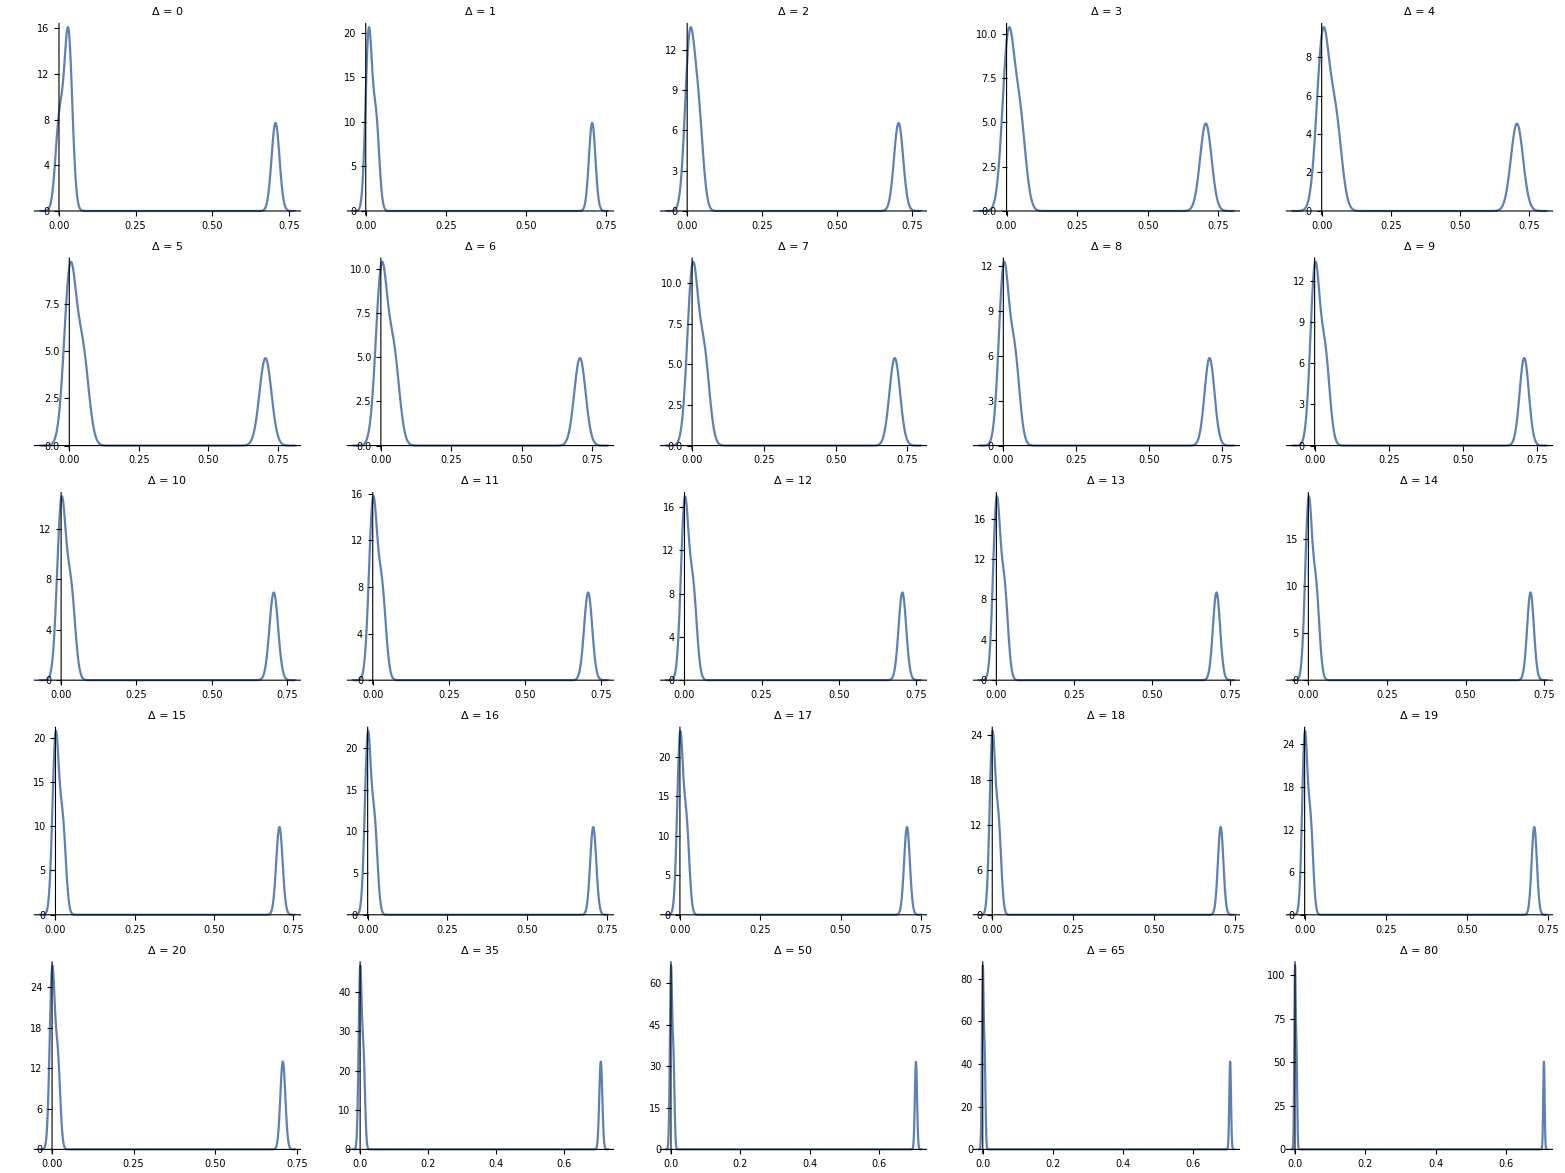

```mathematica
saveGSDN6 = Grid[{{SmoothHistogram[SDTabPlotD0[[5,2]],PlotLabel->"Δ = 0",PlotRange->All],SmoothHistogram[SDTabPlotD1[[5,2]],PlotLabel->"Δ = 1",PlotRange->All],SmoothHistogram[SDTabPlotD2[[5,2]],PlotLabel->"Δ = 2",PlotRange->All],SmoothHistogram[SDTabPlotD3[[5,2]],PlotLabel->"Δ = 3",PlotRange->All],SmoothHistogram[SDTabPlotD4[[5,2]],PlotLabel->"Δ = 4",PlotRange->All]},
{SmoothHistogram[SDTabPlotD5[[5,2]],PlotLabel->"Δ = 5",PlotRange->All],SmoothHistogram[SDTabPlotD6[[5,2]],PlotLabel->"Δ = 6",PlotRange->All],SmoothHistogram[SDTabPlotD7[[5,2]],PlotLabel->"Δ = 7",PlotRange->All],SmoothHistogram[SDTabPlotD8[[5,2]],PlotLabel->"Δ = 8",PlotRange->All],SmoothHistogram[SDTabPlotD9[[5,2]],PlotLabel->"Δ = 9",PlotRange->All]},{SmoothHistogram[SDTabPlotD10[[5,2]],PlotLabel->"Δ = 10",PlotRange->All],SmoothHistogram[SDTabPlotD11[[5,2]],PlotLabel->"Δ = 11",PlotRange->All],SmoothHistogram[SDTabPlotD12[[5,2]],PlotLabel->"Δ = 12",PlotRange->All],SmoothHistogram[SDTabPlotD13[[5,2]],PlotLabel->"Δ = 13",PlotRange->All],SmoothHistogram[SDTabPlotD14[[5,2]],PlotLabel->"Δ = 14",PlotRange->All]},
{SmoothHistogram[SDTabPlotD15[[5,2]],PlotLabel->"Δ = 15",PlotRange->All],SmoothHistogram[SDTabPlotD16[[5,2]],PlotLabel->"Δ = 16",PlotRange->All],SmoothHistogram[SDTabPlotD17[[5,2]],PlotLabel->"Δ = 17",PlotRange->All],SmoothHistogram[SDTabPlotD18[[5,2]],PlotLabel->"Δ = 18",PlotRange->All],SmoothHistogram[SDTabPlotD19[[5,2]],PlotLabel->"Δ = 19",PlotRange->All]},{SmoothHistogram[SDTabPlotD20[[5,2]],PlotLabel->"Δ = 20",PlotRange->All],SmoothHistogram[SDTabPlotD35[[5,2]],PlotLabel->"Δ = 35",PlotRange->All],SmoothHistogram[SDTabPlotD50[[5,2]],PlotLabel->"Δ = 50",PlotRange->All],SmoothHistogram[SDTabPlotD65[[5,2]],PlotLabel->"Δ = 65",PlotRange->All],SmoothHistogram[SDTabPlotD80[[5,2]],PlotLabel->"Δ = 80",PlotRange->All]}},Spacings->{0.5,0.5}]
```

#### N=7 Smooth Histogram

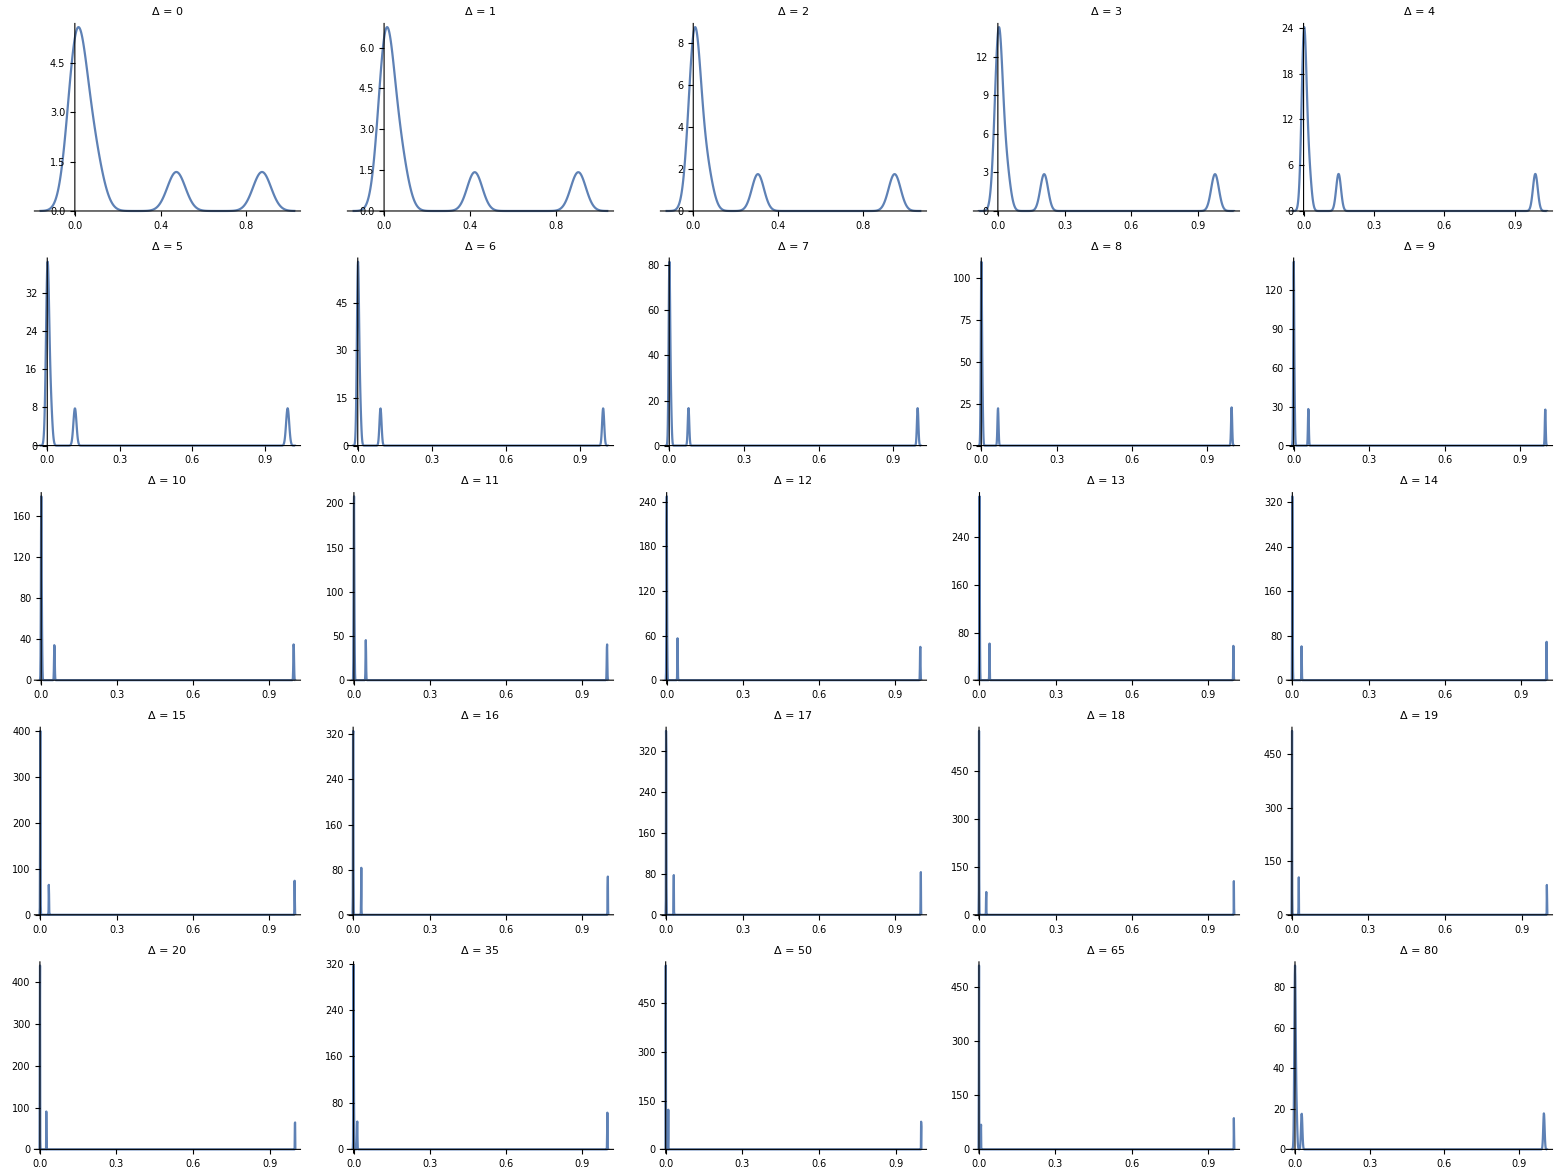

```mathematica
saveGSDN7 = Grid[{{SmoothHistogram[SDTabPlotD0[[6,2]],PlotLabel->"Δ = 0",PlotRange->All],SmoothHistogram[SDTabPlotD1[[6,2]],PlotLabel->"Δ = 1",PlotRange->All],SmoothHistogram[SDTabPlotD2[[6,2]],PlotLabel->"Δ = 2",PlotRange->All],SmoothHistogram[SDTabPlotD3[[6,2]],PlotLabel->"Δ = 3",PlotRange->All],SmoothHistogram[SDTabPlotD4[[6,2]],PlotLabel->"Δ = 4",PlotRange->All]},
{SmoothHistogram[SDTabPlotD5[[6,2]],PlotLabel->"Δ = 5",PlotRange->All],SmoothHistogram[SDTabPlotD6[[6,2]],PlotLabel->"Δ = 6",PlotRange->All],SmoothHistogram[SDTabPlotD7[[6,2]],PlotLabel->"Δ = 7",PlotRange->All],SmoothHistogram[SDTabPlotD8[[6,2]],PlotLabel->"Δ = 8",PlotRange->All],SmoothHistogram[SDTabPlotD9[[6,2]],PlotLabel->"Δ = 9",PlotRange->All]},{SmoothHistogram[SDTabPlotD10[[6,2]],PlotLabel->"Δ = 10",PlotRange->All],SmoothHistogram[SDTabPlotD11[[6,2]],PlotLabel->"Δ = 11",PlotRange->All],SmoothHistogram[SDTabPlotD12[[6,2]],PlotLabel->"Δ = 12",PlotRange->All],SmoothHistogram[SDTabPlotD13[[6,2]],PlotLabel->"Δ = 13",PlotRange->All],SmoothHistogram[SDTabPlotD14[[6,2]],PlotLabel->"Δ = 14",PlotRange->All]},
{SmoothHistogram[SDTabPlotD15[[6,2]],PlotLabel->"Δ = 15",PlotRange->All],SmoothHistogram[SDTabPlotD16[[6,2]],PlotLabel->"Δ = 16",PlotRange->All],SmoothHistogram[SDTabPlotD17[[6,2]],PlotLabel->"Δ = 17",PlotRange->All],SmoothHistogram[SDTabPlotD18[[6,2]],PlotLabel->"Δ = 18",PlotRange->All],SmoothHistogram[SDTabPlotD19[[6,2]],PlotLabel->"Δ = 19",PlotRange->All]},{SmoothHistogram[SDTabPlotD20[[6,2]],PlotLabel->"Δ = 20",PlotRange->All],SmoothHistogram[SDTabPlotD35[[6,2]],PlotLabel->"Δ = 35",PlotRange->All],SmoothHistogram[SDTabPlotD50[[6,2]],PlotLabel->"Δ = 50",PlotRange->All],SmoothHistogram[SDTabPlotD65[[6,2]],PlotLabel->"Δ = 65",PlotRange->All],SmoothHistogram[SDTabPlotD80[[6,2]],PlotLabel->"Δ = 80",PlotRange->All]}},Spacings->{0.5,0.5}]
```

#### N=8 Smooth Histogram

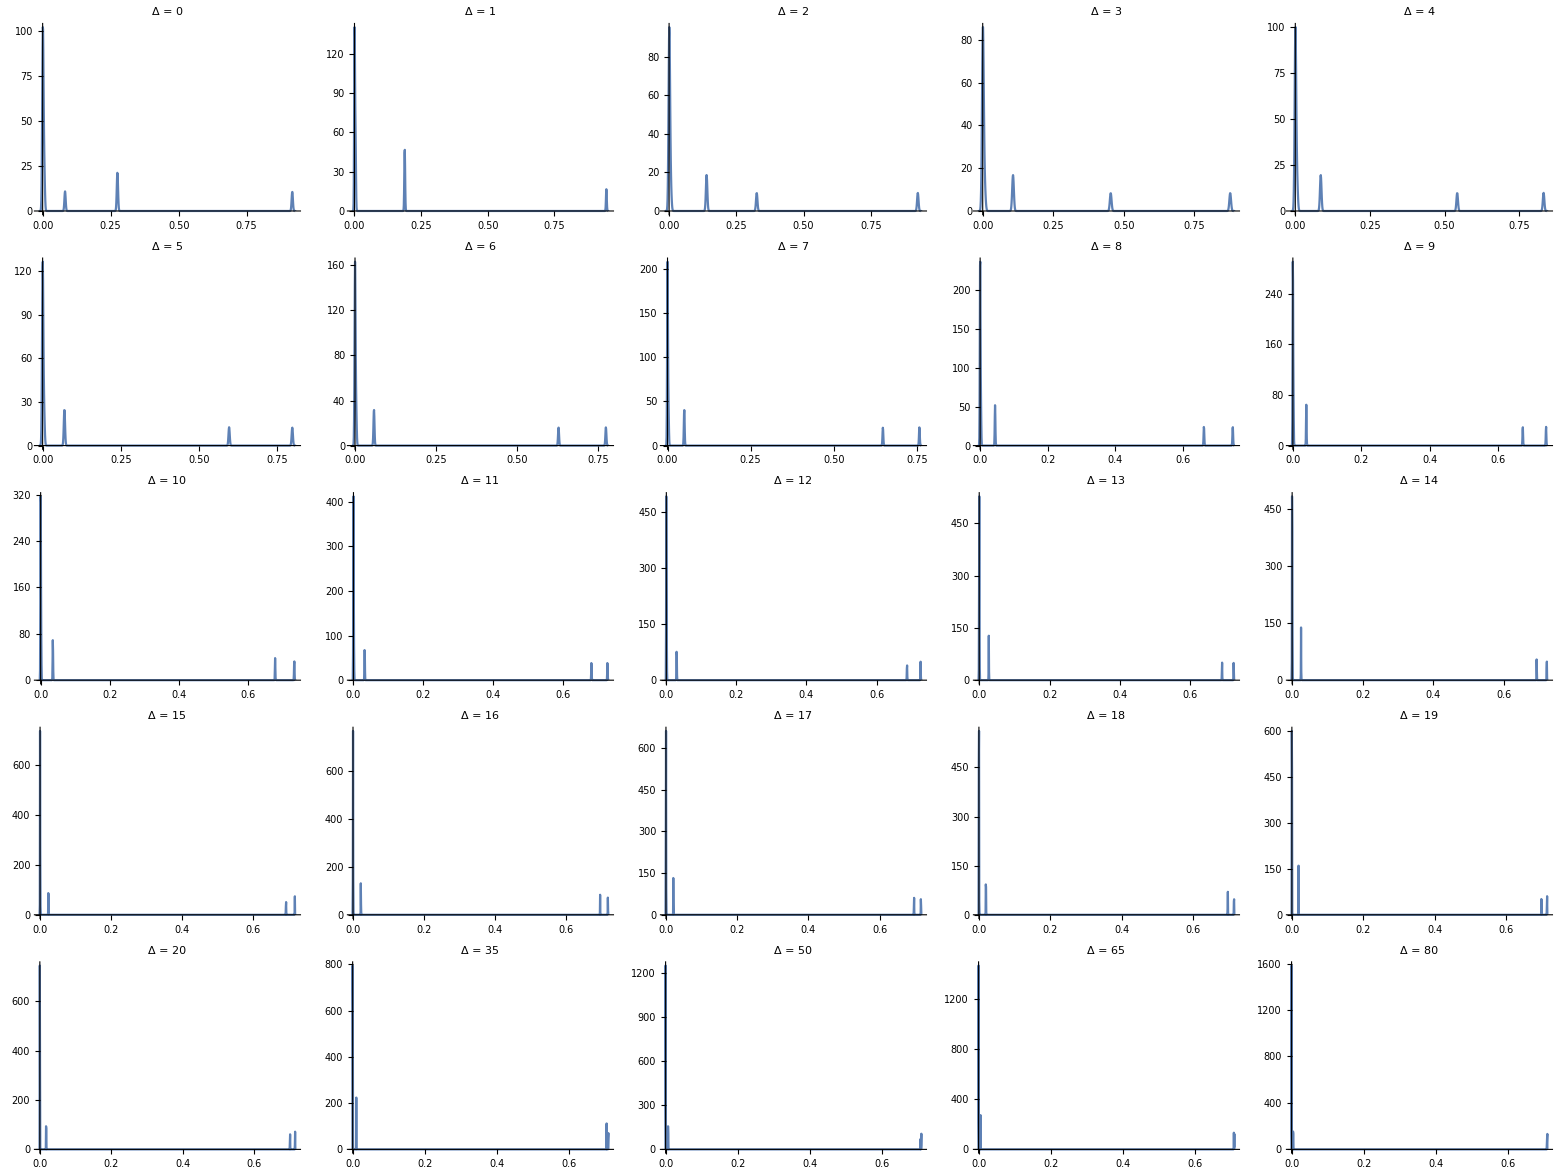

```mathematica
saveGSDN8 = Grid[{{SmoothHistogram[SDTabPlotD0[[7,2]],PlotLabel->"Δ = 0",PlotRange->All],SmoothHistogram[SDTabPlotD1[[7,2]],PlotLabel->"Δ = 1",PlotRange->All],SmoothHistogram[SDTabPlotD2[[7,2]],PlotLabel->"Δ = 2",PlotRange->All],SmoothHistogram[SDTabPlotD3[[7,2]],PlotLabel->"Δ = 3",PlotRange->All],SmoothHistogram[SDTabPlotD4[[7,2]],PlotLabel->"Δ = 4",PlotRange->All]},
{SmoothHistogram[SDTabPlotD5[[7,2]],PlotLabel->"Δ = 5",PlotRange->All],SmoothHistogram[SDTabPlotD6[[7,2]],PlotLabel->"Δ = 6",PlotRange->All],SmoothHistogram[SDTabPlotD7[[7,2]],PlotLabel->"Δ = 7",PlotRange->All],SmoothHistogram[SDTabPlotD8[[7,2]],PlotLabel->"Δ = 8",PlotRange->All],SmoothHistogram[SDTabPlotD9[[7,2]],PlotLabel->"Δ = 9",PlotRange->All]},{SmoothHistogram[SDTabPlotD10[[7,2]],PlotLabel->"Δ = 10",PlotRange->All],SmoothHistogram[SDTabPlotD11[[7,2]],PlotLabel->"Δ = 11",PlotRange->All],SmoothHistogram[SDTabPlotD12[[7,2]],PlotLabel->"Δ = 12",PlotRange->All],SmoothHistogram[SDTabPlotD13[[7,2]],PlotLabel->"Δ = 13",PlotRange->All],SmoothHistogram[SDTabPlotD14[[7,2]],PlotLabel->"Δ = 14",PlotRange->All]},
{SmoothHistogram[SDTabPlotD15[[7,2]],PlotLabel->"Δ = 15",PlotRange->All],SmoothHistogram[SDTabPlotD16[[7,2]],PlotLabel->"Δ = 16",PlotRange->All],SmoothHistogram[SDTabPlotD17[[7,2]],PlotLabel->"Δ = 17",PlotRange->All],SmoothHistogram[SDTabPlotD18[[7,2]],PlotLabel->"Δ = 18",PlotRange->All],SmoothHistogram[SDTabPlotD19[[7,2]],PlotLabel->"Δ = 19",PlotRange->All]},{SmoothHistogram[SDTabPlotD20[[7,2]],PlotLabel->"Δ = 20",PlotRange->All],SmoothHistogram[SDTabPlotD35[[7,2]],PlotLabel->"Δ = 35",PlotRange->All],SmoothHistogram[SDTabPlotD50[[7,2]],PlotLabel->"Δ = 50",PlotRange->All],SmoothHistogram[SDTabPlotD65[[7,2]],PlotLabel->"Δ = 65",PlotRange->All],SmoothHistogram[SDTabPlotD80[[7,2]],PlotLabel->"Δ = 80",PlotRange->All]}},Spacings->{0.5,0.5}]
```

#### N=12 Smooth Histogram

```mathematica
saveGSDN12 = Grid[{{SmoothHistogram[SDTabPlotD0[[11,2]],PlotLabel->"Δ = 0",PlotRange->All],SmoothHistogram[SDTabPlotD1[[11,2]],PlotLabel->"Δ = 1",PlotRange->All],SmoothHistogram[SDTabPlotD2[[11,2]],PlotLabel->"Δ = 2",PlotRange->All],SmoothHistogram[SDTabPlotD3[[11,2]],PlotLabel->"Δ = 3",PlotRange->All],SmoothHistogram[SDTabPlotD4[[11,2]],PlotLabel->"Δ = 4",PlotRange->All]},
{SmoothHistogram[SDTabPlotD5[[11,2]],PlotLabel->"Δ = 5",PlotRange->All],SmoothHistogram[SDTabPlotD6[[11,2]],PlotLabel->"Δ = 6",PlotRange->All],SmoothHistogram[SDTabPlotD7[[11,2]],PlotLabel->"Δ = 7",PlotRange->All],SmoothHistogram[SDTabPlotD8[[11,2]],PlotLabel->"Δ = 8",PlotRange->All],SmoothHistogram[SDTabPlotD9[[11,2]],PlotLabel->"Δ = 9",PlotRange->All]},{SmoothHistogram[SDTabPlotD10[[11,2]],PlotLabel->"Δ = 10",PlotRange->All],SmoothHistogram[SDTabPlotD11[[11,2]],PlotLabel->"Δ = 11",PlotRange->All],SmoothHistogram[SDTabPlotD12[[11,2]],PlotLabel->"Δ = 12",PlotRange->All],SmoothHistogram[SDTabPlotD13[[11,2]],PlotLabel->"Δ = 13",PlotRange->All],SmoothHistogram[SDTabPlotD14[[11,2]],PlotLabel->"Δ = 14",PlotRange->All]},
{SmoothHistogram[SDTabPlotD15[[11,2]],PlotLabel->"Δ = 15",PlotRange->All],SmoothHistogram[SDTabPlotD16[[11,2]],PlotLabel->"Δ = 16",PlotRange->All],SmoothHistogram[SDTabPlotD17[[11,2]],PlotLabel->"Δ = 17",PlotRange->All],SmoothHistogram[SDTabPlotD18[[11,2]],PlotLabel->"Δ = 18",PlotRange->All],SmoothHistogram[SDTabPlotD19[[11,2]],PlotLabel->"Δ = 19",PlotRange->All]},{SmoothHistogram[SDTabPlotD20[[11,2]],PlotLabel->"Δ = 20",PlotRange->All],SmoothHistogram[SDTabPlotD35[[11,2]],PlotLabel->"Δ = 35",PlotRange->All],SmoothHistogram[SDTabPlotD50[[11,2]],PlotLabel->"Δ = 50",PlotRange->All],SmoothHistogram[SDTabPlotD65[[11,2]],PlotLabel->"Δ = 65",PlotRange->All],SmoothHistogram[SDTabPlotD80[[11,2]],PlotLabel->"Δ = 80",PlotRange->All]}},Spacings->{0.5,0.5}]
```

Part::partw: Part 11 of {{2,{0.707107,0.707107}},{3,{«19»,«19»}},«6»,{10,{0.703456,0.703456,0.0506736,0.0506736,0.0506736,0.0506736,0.00365028,0.00365028,0.000618424,0.000618424,0.000618424,«11»,3.20904×10^-6,3.20904×10^-6,5.4367×10^-7,5.4367×10^-7,3.91633×10^-8,3.91633×10^-8,3.91633×10^-8,3.91633×10^-8,2.82114×10^-9,2.82114×10^-9}}} does not exist.

SmoothHistogram::ldata: «1» is not a valid dataset or list of datasets.

General::stop: Further output of SmoothHistogram::ldata will be suppressed during this calculation.

Part::partw: Part 11 of {{2,{0.707107,0.707107}},«7»,{10,{0.704684,0.704684,0.0535596,0.0535596,0.0166115,0.0166115,0.0166115,0.0166115,0.000638169,0.000638169,0.000207587,«10»,5.93453×10^-6,1.98703×10^-6,1.98703×10^-6,1.98703×10^-6,1.98703×10^-6,9.51573×10^-7,9.51573×10^-7,9.51573×10^-7,9.51573×10^-7,9.51573×10^-7,9.51573×10^-7}}} does not exist.

Part::partw: Part 11 of {{2,{0.707107,0.707107}},«7»,{10,{0.703487,0.703487,0.0672297,0.0672297,0.0232923,0.0232923,0.00653321,0.00653321,0.000740983,0.000740983,0.000274438,«11»,2.17734×10^-6,2.17734×10^-6,2.02849×10^-6,2.02849×10^-6,6.25251×10^-7,6.25251×10^-7,1.68346×10^-7,1.68346×10^-7,4.51239×10^-8,4.51239×10^-8}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.866025,0.5}},{4,{0.947214,0.223607,0.223607,0.0527864}},{5,{0.899193,0.4217,0.105662,0.0495532}},{6,{0.705789,0.705789,0.0305003,0.0305003,0.0305003,0.0305003,0.00131806,0.00131806}},{7,{0.873589,0.473736,0.0965739,0.0523708,0.0162829,0.00883004,0.00180005,0.000976147}},{8,{0.917638,0.274846,0.274846,0.0823202,0.00595202,0.00595202,0.00178272,0.00178272,0.00178272,0.00178272,0.000533949,0.000533949,0.0000386063,0.0000115631,0.0000115631,3.46332×10^-6}},{9,{0.868855,0.468161,0.140437,0.075671,0.0186654,0.0100574,0.00301697,0.00226117,0.00162562,0.00121838,0.000365483,0.000196932,0.0000485761,0.000026174,7.85158×10^-6,4.23063×10^-6}},{10,{0.703456,0.703456,0.0506736,0.0506736,0.0506736,0.0506736,0.00365028,0.00365028,0.000618424,0.000618424,0.000618424,0.000618424,0.0000445483,0.0000445483,0.0000445483,0.0000445483,0.0000445483,0.0000445483,0.0000445483,0.0000445483,3.20904×10^-6,3.20904×10^-6,3.20904×10^-6,3.20904×10^-6,5.4367×10^-7,5.4367×10^-7,3.91633×10^-8,3.91633×10^-8,3.91633×10^-8,3.91633×10^-8,2.82114×10^-9,2.82114×10^-9}}}⟦11,2⟧,PlotLabel→Δ = 0,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.912871,0.408248}},{4,{0.965926,0.149429,0.149429,0.149429}},{5,{0.937842,0.333018,0.0851343,0.0479886}},{6,{0.706251,0.706251,0.0321512,0.0321512,0.00936045,0.00936045,0.00936045,0.00936045}},{7,{0.902239,0.421084,0.0815533,0.0419316,0.0142921,0.00553811,0.00256167,0.00165526}},{8,{0.945192,0.188465,0.188465,0.188465,0.00405816,0.00405816,0.00405816,0.00203452,0.00043631,0.00043631,0.00043631,0.000173529,0.000173529,0.000173529,0.000173529,0.000173529}},{9,{0.914923,0.380489,0.115981,0.0661132,0.0161892,0.00664456,0.00271241,0.00177028,0.00167724,0.00111896,0.0002287,0.000118466,0.0000936968,0.000040559,0.0000238514,0.0000168246}},{10,{0.704684,0.704684,0.0535596,0.0535596,0.0166115,0.0166115,0.0166115,0.0166115,0.000638169,0.000638169,0.000207587,0.000207587,0.000207587,0.000207587,0.000050694,0.000050694,0.0000115321,0.0000115321,0.0000115321,0.0000115321,5.93453×10^-6,5.93453×10^-6,1.98703×10^-6,1.98703×10^-6,1.98703×10^-6,1.98703×10^-6,9.51573×10^-7,9.51573×10^-7,9.51573×10^-7,9.51573×10^-7,9.51573×10^-7,9.51573×10^-7}}}⟦11,2⟧,PlotLabel→Δ = 1,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.945694,0.325058}},{4,{0.956706,0.244379,0.111785,0.111785}},{5,{0.965611,0.246203,0.0804684,0.0224597}},{6,{0.705938,0.705938,0.0381714,0.0381714,0.0134236,0.0134236,0.00384425,0.00384425}},{7,{0.949869,0.304919,0.0652636,0.0172253,0.0139551,0.00458227,0.00123764,0.000332007}},{8,{0.924581,0.3258,0.139521,0.139521,0.00694429,0.00281437,0.00272228,0.00272228,0.000641511,0.000641511,0.000400067,0.000347844,0.000105747,0.000105747,0.0000284663,0.0000284663}},{9,{0.958708,0.266237,0.0952684,0.0262824,0.0142986,0.00439943,0.00195091,0.0010712,0.000541091,0.000285059,0.000217572,0.0000645826,0.0000511983,0.0000147079,3.89169×10^-6,1.04183×10^-6}},{10,{0.703487,0.703487,0.0672297,0.0672297,0.0232923,0.0232923,0.00653321,0.00653321,0.000740983,0.000740983,0.000274438,0.000274438,0.0000769473,0.0000769473,0.0000734945,0.0000734945,0.0000175352,0.0000175352,7.45005×10^-6,7.45005×10^-6,4.76625×10^-6,4.76625×10^-6,2.17734×10^-6,2.17734×10^-6,2.02849×10^-6,2.02849×10^-6,6.25251×10^-7,6.25251×10^-7,1.68346×10^-7,1.68346×10^-7,4.51239×10^-8,4.51239×10^-8}}}⟦11,2⟧,PlotLabel→Δ = 2,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.965351,0.260956}},{4,{0.937664,0.324119,0.0886944,0.0886944}},{5,{0.981801,0.179582,0.0608191,0.0108767}},{6,{0.705433,0.705433,0.0474272,0.0474272,0.0105839,0.0105839,0.0018392,0.0018392}},{7,{0.977165,0.208342,0.0396778,0.010742,0.00682847,0.00233818,0.000415545,0.000071374}},{8,{0.877877,0.45403,0.107486,0.107486,0.00769719,0.00408972,0.00161794,0.00161794,0.000716272,0.000716272,0.000207674,0.000202149,0.0000355463,0.0000355463,6.10081×10^-6,6.10081×10^-6}},{9,{0.982597,0.177582,0.0529427,0.00925363,0.00863063,0.00164219,0.00143694,0.00027305,0.000248822,0.0000846244,0.0000468087,0.0000152799,0.0000140566,2.4789×10^-6,4.24499×10^-7,7.28284×10^-8}},{10,{0.702161,0.702161,0.0818426,0.0818426,0.0162106,0.0162106,0.00279639,0.00279639,0.00073825,0.00073825,0.000161887,0.000161887,0.0000868972,0.0000868972,0.0000279536,0.0000279536,0.0000142846,0.0000142846,3.59049×10^-6,3.59049×10^-6,2.4477×10^-6,2.4477×10^-6,6.22606×10^-7,6.22606×10^-7,6.21006×10^-7,6.21006×10^-7,1.07796×10^-7,1.07796×10^-7,1.85013×10^-8,1.85013×10^-8,3.17434×10^-9,3.17434×10^-9}}}⟦11,2⟧,PlotLabel→Δ = 3,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.976793,0.214186}},{4,{0.91629,0.386975,0.0730174,0.0730174}},{5,{0.989759,0.135817,0.0435747,0.00570195}},{6,{0.705257,0.705257,0.0505257,0.0505257,0.00766306,0.00766306,0.000976961,0.000976961}},{7,{0.988484,0.149313,0.023308,0.00724077,0.00296966,0.0011051,0.000144873,0.0000184111}},{8,{0.831545,0.542181,0.0851729,0.0851729,0.00654632,0.00430371,0.000930348,0.000930348,0.000566996,0.000566996,0.0000996557,0.000098836,0.0000126463,0.0000126463,1.60638×10^-6,1.60638×10^-6}},{9,{0.99118,0.12932,0.0283797,0.00440517,0.00363723,0.000904026,0.000585975,0.000114748,0.0000738425,0.0000270664,9.37793×10^-6,3.5107×10^-6,3.44207×10^-6,4.41526×10^-7,5.60704×10^-8,7.12185×10^-9}},{10,{0.702821,0.702821,0.0770221,0.0770221,0.0103794,0.0103794,0.00131973,0.00131973,0.000559906,0.000559906,0.0000832054,0.0000832054,0.0000615152,0.0000615152,0.0000105843,0.0000105843,7.69233×10^-6,7.69233×10^-6,1.21226×10^-6,1.21226×10^-6,9.76792×10^-7,9.76792×10^-7,1.54482×10^-7,1.54482×10^-7,1.54164×10^-7,1.54164×10^-7,1.96469×10^-8,1.96469×10^-8,2.49562×10^-9,2.49562×10^-9,3.16986×10^-10,3.16986×10^-10}}}⟦11,2⟧,PlotLabel→Δ = 4,PlotRange→All]
SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.983665,0.180008}},{4,{0.895923,0.435546,0.0617321,0.0617321}},{5,{0.993698,0.107509,0.0315598,0.0032561}},{6,{0.705378,0.705378,0.0490957,0.0490957,0.00558366,0.00558366,0.000564861,0.000564861}},{7,{0.993323,0.114351,0.0144574,0.00476832,0.00146346,0.000551796,0.0000571235,5.77211×10^-6}},{8,{0.797255,0.595531,0.0695905,0.0695905,0.00510961,0.00382946,0.000552921,0.000552921,0.000399062,0.000399062,0.0000499513,0.0000497857,5.04391×10^-6,5.04391×10^-6,5.09545×10^-7,5.09545×10^-7}},{9,{0.994661,0.101823,0.0165507,0.00228416,0.00167981,0.000552017,0.000235931,0.0000557129,0.0000238017,9.39292×10^-6,2.40448×10^-6,9.65282×10^-7,9.57843×10^-7,9.79227×10^-8,9.89551×10^-9,9.99653×10^-10}},{10,{0.703918,0.703918,0.066714,0.066714,0.00691861,0.00691861,0.000699116,0.000699116,0.000388669,0.000388669,0.0000436559,0.0000436559,0.0000368647,0.0000368647,4.41217×10^-6,4.41217×10^-6,3.69935×10^-6,3.69935×10^-6,4.26568×10^-7,4.26568×10^-7,3.73684×10^-7,3.73684×10^-7,4.31477×10^-8,4.31477×10^-8,4.31043×10^-8,4.31043×10^-8,4.36008×10^-9,4.36008×10^-9,4.40463×10^-10,4.40463×10^-10,4.44958×10^-11,4.44958×10^-11}}}⟦11,2⟧,PlotLabel→Δ = 5,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.987995,0.154488}},{4,{0.87775,0.473158,0.0532782,0.0532782}},{5,{0.9958,0.0884629,0.0235184,0.00200451}},{6,{0.70561,0.70561,0.0457992,0.0457992,0.00417234,0.00417234,0.000350368,0.000350368}},{7,{0.995682,0.0922716,0.0095789,0.00319903,0.000804923,0.000297291,0.0000254261,2.13405×10^-6}},{8,{0.773921,0.627835,0.0584949,0.0584949,0.00394309,0.00320386,0.000346463,0.000346463,0.00027549,0.00027549,0.0000268738,0.0000268313,2.25474×10^-6,2.25474×10^-6,1.89219×10^-7,1.89219×10^-7}},{9,{0.996111,0.0843326,0.0247822,0.0055886,0.00210717,0.000469093,0.000419122,0.000142032,0.0000354415,0.0000119026,9.72987×10^-6,2.96834×10^-6,8.27728×10^-7,2.49101×10^-7,7.07837×10^-8,5.94097×10^-9}},{10,{0.704762,0.704762,0.0573268,0.0573268,0.00487364,0.00487364,0.000409035,0.000409035,0.00026779,0.00026779,0.000024246,0.000024246,0.0000217886,0.0000217886,2.03508×10^-6,2.03508×10^-6,1.82257×10^-6,1.82257×10^-6,1.67176×10^-7,1.67176×10^-7,1.52947×10^-7,1.52947×10^-7,1.4038×10^-8,1.4038×10^-8,1.40307×10^-8,1.40307×10^-8,1.17818×10^-9,1.17818×10^-9,9.88732×10^-11,9.88732×10^-11,8.29751×10^-12,8.29746×10^-12}}}⟦11,2⟧,PlotLabel→Δ = 6,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.990855,0.134933}},{4,{0.861968,0.502634,0.0467484,0.0467484}},{5,{0.997019,0.0750003,0.0180441,0.00131081}},{6,{0.705847,0.705847,0.0420741,0.0420741,0.0032052,0.0032052,0.000230198,0.000230198}},{7,{0.996982,0.0773026,0.00672342,0.00221182,0.000483144,0.000171772,0.0000125199,8.98961×10^-7}},{8,{0.758073,0.648261,0.050331,0.050331,0.00308118,0.00263709,0.00022859,0.00022859,0.000192968,0.000192968,0.0000154812,0.0000154681,1.11136×10^-6,1.11136×10^-6,7.97919×10^-8,7.97919×10^-8}},{9,{0.962265,0.262654,0.0684488,0.018751,0.00440617,0.00120167,0.000316188,0.000276785,0.0000862156,0.0000755231,0.0000196758,5.38893×10^-6,1.42923×10^-6,3.91097×10^-7,1.02621×10^-7,2.80811×10^-8}},{10,{0.705342,0.705342,0.0497953,0.0497953,0.00360037,0.00360037,0.000258504,0.000258504,0.000187959,0.000187959,0.0000142854,0.0000142854,0.0000132709,0.0000132709,1.02572×10^-6,1.02572×10^-6,9.51132×10^-7,9.51132×10^-7,7.28005×10^-8,7.28005×10^-8,6.82876×10^-8,6.82876×10^-8,5.22853×10^-9,5.22853×10^-9,5.22701×10^-9,5.22701×10^-9,3.75404×10^-10,3.75404×10^-10,2.6953×10^-11,2.69527×10^-11,1.93513×10^-12,1.93512×10^-12}}}⟦11,2⟧,PlotLabel→Δ = 7,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.992825,0.119573}},{4,{0.848389,0.526098,0.0415769,0.0415769}},{5,{0.99778,0.0650554,0.0142217,0.000900652}},{6,{0.706053,0.706053,0.0385071,0.0385071,0.0025258,0.0025258,0.000158513,0.000158513}},{7,{0.99777,0.0665426,0.00494607,0.00157675,0.000310531,0.000105259,6.68344×10^-6,4.1938×10^-7}},{8,{0.747052,0.661823,0.0441201,0.0441201,0.00245261,0.00217387,0.000157717,0.000157717,0.000138475,0.000138475,9.46088×10^-6,9.45619×10^-6,5.93586×10^-7,5.93586×10^-7,3.72452×10^-8,3.72452×10^-8}},{9,{0.995562,0.0716383,0.0607671,0.00438106,0.0035754,0.000251515,0.000224292,0.000202393,0.0000157759,0.0000145451,0.0000123464,8.89103×10^-7,7.97818×10^-7,5.61478×10^-8,5.00671×10^-8,3.52315×10^-9}},{10,{0.70574,0.70574,0.0438493,0.0438493,0.00276271,0.00276271,0.000173352,0.000173352,0.000135295,0.000135295,8.87296×10^-6,8.87296×10^-6,8.40662×10^-6,8.40662×10^-6,5.56762×10^-7,5.56762×10^-7,5.26938×10^-7,5.26938×10^-7,3.47008×10^-8,3.47008×10^-8,3.30631×10^-8,3.30631×10^-8,2.17775×10^-9,2.17775×10^-9,2.17737×10^-9,2.17737×10^-9,1.36647×10^-10,1.36647×10^-10,8.57422×10^-12,8.57391×10^-12,5.37989×10^-13,5.37968×10^-13}}}⟦11,2⟧,PlotLabel→Δ = 8,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.994233,0.10724}},{4,{0.836714,0.54508,0.0373938,0.0373938}},{5,{0.998283,0.057433,0.0114588,0.000643316}},{6,{0.706223,0.706223,0.0352894,0.0352894,0.0020352,0.0020352,0.00011343,0.00011343}},{7,{0.998283,0.0584467,0.00377909,0.00115712,0.00021069,0.0000677887,3.81539×10^-6,2.12631×10^-7}},{8,{0.739162,0.67123,0.039254,0.039254,0.00198905,0.0018068,0.000112982,0.000112982,0.000101925,0.000101925,6.07551×10^-6,6.07364×10^-6,3.38559×10^-7,3.38559×10^-7,1.88673×10^-8,1.88673×10^-8}},{9,{0.758552,0.649241,0.0420022,0.0362296,0.00219346,0.00187744,0.00012206,0.000112926,0.000104148,0.0000963549,6.22447×10^-6,5.36899×10^-6,3.48343×10^-7,3.00465×10^-7,1.94127×10^-8,1.67445×10^-8}},{10,{0.706021,0.706021,0.039106,0.039106,0.00218488,0.00218488,0.00012176,0.00012176,0.0000998874,0.0000998874,5.76654×10^-6,5.76654×10^-6,5.53284×10^-6,5.53284×10^-6,3.21364×10^-7,3.21364×10^-7,3.08136×10^-7,3.08136×10^-7,1.78345×10^-8,1.78345×10^-8,1.71718×10^-8,1.71718×10^-8,9.93996×10^-10,9.93996×10^-10,9.93887×10^-10,9.93887×10^-10,5.53939×10^-11,5.53939×10^-11,3.08703×10^-12,3.08699×10^-12,1.72032×10^-13,1.71992×10^-13}}}⟦11,2⟧,PlotLabel→Δ = 9,PlotRange→All]
SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.99527,0.0971462}},{4,{0.826641,0.560677,0.033949,0.033949}},{5,{0.998633,0.0514136,0.00941015,0.000474533}},{6,{0.70636,0.70636,0.0324528,0.0324528,0.00167155,0.00167155,0.0000837934,0.0000837934}},{7,{0.998635,0.0521349,0.00298659,0.000912389,0.000149797,0.0000476351,2.47151×10^-6,1.23898×10^-7}},{8,{0.733354,0.678003,0.0353456,0.0353456,0.0016409,0.00151736,0.0000835176,0.0000835176,0.000076825,0.000076825,4.06669×10^-6,4.06587×10^-6,2.03839×10^-7,2.03839×10^-7,1.02175×10^-8,1.02175×10^-8}},{9,{0.977745,0.203749,0.0488988,0.0101985,0.00231871,0.000483101,0.000116212,0.000108552,0.0000242121,0.0000226193,5.42808×10^-6,1.13205×10^-6,2.72901×10^-7,5.69037×10^-8,1.36794×10^-8,2.85236×10^-9}},{10,{0.706225,0.706225,0.0352595,0.0352595,0.00177035,0.00177035,0.0000887405,0.0000887405,0.0000754935,0.0000754935,3.89481×10^-6,3.89481×10^-6,3.7692×10^-6,3.7692×10^-6,1.95231×10^-7,1.95231×10^-7,1.88854×10^-7,1.88854×10^-7,9.7595×10^-9,9.7595×10^-9,9.46641×10^-9,9.46641×10^-9,4.89238×10^-10,4.89238×10^-10,4.89203×10^-10,4.89203×10^-10,2.45235×10^-11,2.45235×10^-11,1.22939×10^-12,1.22913×10^-12,6.16172×10^-14,6.15952×10^-14}}}⟦11,2⟧,PlotLabel→Δ = 10,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.996054,0.0887468}},{4,{0.817904,0.573675,0.031068,0.031068}},{5,{0.998885,0.0465425,0.00786159,0.000359891}},{6,{0.70647,0.70647,0.0299707,0.0299707,0.00139555,0.00139555,0.0000635686,0.0000635686}},{7,{0.998888,0.0470734,0.00240393,0.000669484,0.00010952,0.0000315593,1.44715×10^-6,6.59169×10^-8}},{8,{0.72897,0.683033,0.0321407,0.0321407,0.00137436,0.00128793,0.0000633882,0.0000633882,0.0000591569,0.0000591569,2.81872×10^-6,2.81833×10^-6,1.28386×10^-7,1.28386×10^-7,5.84784×10^-9,5.84784×10^-9}},{9,{0.995746,0.0801637,0.0452462,0.00364457,0.00196932,0.000158386,0.0000896926,0.000084753,7.21361×10^-6,6.82192×10^-6,3.85077×10^-6,3.10126×10^-7,1.75912×10^-7,1.41533×10^-8,8.01264×10^-9,6.44667×10^-10}},{10,{0.706377,0.706377,0.032088,0.032088,0.00146323,0.00146323,0.0000666484,0.0000666484,0.0000582661,0.0000582661,2.71832×10^-6,2.71832×10^-6,2.64683×10^-6,2.64683×10^-6,1.23817×10^-7,1.23817×10^-7,1.20525×10^-7,1.20525×10^-7,5.62931×10^-9,5.62931×10^-9,5.48978×10^-9,5.48978×10^-9,2.56422×10^-10,2.56422×10^-10,2.56409×10^-10,2.56409×10^-10,1.16797×10^-11,1.16797×10^-11,5.32033×10^-13,5.31969×10^-13,2.42867×10^-14,2.42319×10^-14}}}⟦11,2⟧,PlotLabel→Δ = 11,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.99666,0.081657}},{4,{0.810278,0.584645,0.0286261,0.0286261}},{5,{0.99907,0.0425282,0.00709897,0.000298693}},{6,{0.706559,0.706559,0.0277998,0.0277998,0.00118165,0.00118165,0.0000493227,0.0000493227}},{7,{0.999076,0.0429224,0.00198159,0.000525276,0.0000827237,0.0000225717,9.4764×10^-7,3.95542×10^-8}},{8,{0.725586,0.686867,0.0294664,0.0294664,0.0011665,0.00110436,0.0000491994,0.0000491994,0.0000464232,0.0000464232,2.01243×10^-6,2.01223×10^-6,8.39959×10^-8,8.39959×10^-8,3.50593×10^-9,3.50593×10^-9}},{9,{0.989908,0.135444,0.04127,0.00564896,0.00165681,0.000226658,0.0000691498,0.0000659108,9.45989×10^-6,9.01785×10^-6,2.74768×10^-6,3.76084×10^-7,1.14862×10^-7,1.57192×10^-8,4.79429×10^-9,6.56109×10^-10}},{10,{0.706493,0.706493,0.0294327,0.0294327,0.00122948,0.00122948,0.0000513175,0.0000513175,0.0000458132,0.0000458132,1.95129×10^-6,1.95129×10^-6,1.9086×10^-6,1.9086×10^-6,8.14458×10^-8,8.14458×10^-8,7.96474×10^-8,7.96474×10^-8,3.39508×10^-9,3.39508×10^-9,3.32442×10^-9,3.32442×10^-9,1.41713×10^-10,1.41713×10^-10,1.41708×10^-10,1.41708×10^-10,5.91501×10^-12,5.91501×10^-12,2.46907×10^-13,2.46843×10^-13,1.04133×10^-14,1.03049×10^-14}}}⟦11,2⟧,PlotLabel→Δ = 12,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.997138,0.0755979}},{4,{0.80358,0.594013,0.026532,0.026532}},{5,{0.999217,0.0391425,0.00571023,0.000220752}},{6,{0.706632,0.706632,0.0258956,0.0258956,0.0010128,0.0010128,0.0000390125,0.0000390125}},{7,{0.99922,0.0394547,0.00166683,0.000464374,0.0000642232,0.0000183349,7.3208×10^-7,2.82003×10^-8}},{8,{0.722923,0.689855,0.0272018,0.0272018,0.00100167,0.000955918,0.0000389254,0.0000389254,0.0000370451,0.0000370451,1.4737×10^-6,1.47359×10^-6,5.6764×10^-8,5.6764×10^-8,2.18647×10^-9,2.18647×10^-9}},{9,{0.983724,0.175516,0.0378616,0.00675724,0.00141056,0.00025166,0.0000543304,0.0000521441,9.69309×10^-6,9.3034×10^-6,2.00682×10^-6,3.58158×10^-7,7.73824×10^-8,1.38097×10^-8,2.98067×10^-9,5.31931×10^-10}},{10,{0.706583,0.706583,0.0271794,0.0271794,0.00104751,0.00104751,0.0000403488,0.0000403488,0.000036618,0.000036618,1.4351×10^-6,1.4351×10^-6,1.40855×10^-6,1.40855×10^-6,5.52781×10^-8,5.52781×10^-8,5.42474×10^-8,5.42474×10^-8,2.12724×10^-9,2.12724×10^-9,2.08954×10^-9,2.08954×10^-9,8.19404×10^-11,8.19403×10^-11,8.19383×10^-11,8.19383×10^-11,3.15623×10^-12,3.15623×10^-12,1.21665×10^-13,1.21512×10^-13,4.68284×10^-15,4.46388×10^-15}}}⟦11,2⟧,PlotLabel→Δ = 13,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.997521,0.0703632}},{4,{0.797661,0.602093,0.0247177,0.0247177}},{5,{0.99933,0.0362657,0.00494552,0.000177405}},{6,{0.706691,0.706691,0.0242179,0.0242179,0.000877337,0.000877337,0.000031374,0.000031374}},{7,{0.999332,0.0365128,0.00141404,0.000344539,0.0000505717,0.0000125897,4.54116×10^-7,1.62394×10^-8}},{8,{0.720793,0.692229,0.0252597,0.0252597,0.000868969,0.000834577,0.0000313109,0.0000313109,0.000030002,0.000030002,1.10312×10^-6,1.10306×10^-6,3.94471×10^-8,3.94471×10^-8,1.41063×10^-9,1.41063×10^-9}},{9,{0.999301,0.0357475,0.0109039,0.0012381,0.00039014,0.0000442727,0.000042821,0.0000135217,1.53175×10^-6,4.83515×10^-7,4.66205×10^-7,5.47682×10^-8,1.66801×10^-8,1.95851×10^-9,5.96932×10^-10,2.13463×10^-11}},{10,{0.706655,0.706655,0.0252444,0.0252444,0.000903123,0.000903123,0.0000322956,0.0000322956,0.0000296967,0.0000296967,1.07797×10^-6,1.07797×10^-6,1.06088×10^-6,1.06088×10^-6,3.85482×10^-8,3.85482×10^-8,3.79329×10^-8,3.79329×10^-8,1.37752×10^-9,1.37752×10^-9,1.35648×10^-9,1.35648×10^-9,4.92613×10^-11,4.92612×10^-11,4.92602×10^-11,4.92602×10^-11,1.76158×10^-12,1.76158×10^-12,6.29949×10^-14,6.29842×10^-14,2.56681×10^-15,2.25266×10^-15}}}⟦11,2⟧,PlotLabel→Δ = 14,PlotRange→All]
SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.997833,0.0657977}},{4,{0.792398,0.609127,0.0231316,0.0231316}},{5,{0.99942,0.0337858,0.0043254,0.000144735}},{6,{0.706741,0.706741,0.0227323,0.0227323,0.000767097,0.000767097,0.0000255987,0.0000255987}},{7,{0.999422,0.0339849,0.0012244,0.000359865,0.0000408718,0.0000122346,4.30885×10^-7,1.43797×10^-8}},{8,{0.719062,0.694145,0.0235761,0.0235761,0.00076068,0.00073435,0.0000255519,0.0000255519,0.0000246186,0.0000246186,8.41673×10^-7,8.4164×10^-7,2.80868×10^-8,2.80868×10^-8,9.3727×10^-10,9.3727×10^-10}},{9,{0.996204,0.0804073,0.0332257,0.00268219,0.00108128,0.0000872632,0.000036082,0.0000349795,2.91193×10^-6,2.82324×10^-6,1.16661×10^-6,9.4174×10^-8,3.89579×10^-8,3.14444×10^-9,1.30004×10^-9,1.04932×10^-10}},{10,{0.706714,0.706714,0.0235654,0.0235654,0.000786638,0.000786638,0.0000262505,0.0000262505,0.0000243963,0.0000243963,8.2483×10^-7,8.2483×10^-7,8.13495×10^-7,8.13495×10^-7,2.7525×10^-8,2.7525×10^-8,2.71444×10^-8,2.71444×10^-8,9.18038×10^-10,9.18038×10^-10,9.05822×10^-10,9.05822×10^-10,3.06359×10^-11,3.06357×10^-11,3.06353×10^-11,3.06353×10^-11,1.02233×10^-12,1.02233×10^-12,3.41229×10^-14,3.40803×10^-14,1.13845×10^-15,9.11137×10^-16}}}⟦11,2⟧,PlotLabel→Δ = 15,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.99809,0.061782}},{4,{0.787693,0.615301,0.0217338,0.0217338}},{5,{0.999493,0.0316256,0.0038141,0.000119594}},{6,{0.706782,0.706782,0.0214101,0.0214101,0.00067624,0.00067624,0.0000211534,0.0000211534}},{7,{0.999494,0.0317883,0.00106014,0.000237469,0.0000331642,7.55293×10^-6,2.38405×10^-7,7.4575×10^-9}},{8,{0.717639,0.695713,0.0221026,0.0221026,0.000671235,0.000650747,0.000021118,0.000021118,0.0000204385,0.0000204385,6.5308×10^-7,6.5306×10^-7,2.04286×10^-8,2.04286×10^-8,6.39019×10^-10,6.39019×10^-10}},{9,{0.955563,0.293124,0.0298804,0.00916731,0.000914189,0.000280431,0.0000285957,0.000027824,8.77184×10^-6,8.53515×10^-6,8.70037×10^-7,2.66927×10^-7,2.72276×10^-8,8.35337×10^-9,8.51695×10^-10,2.61298×10^-10}},{10,{0.706761,0.706761,0.0220949,0.0220949,0.000691312,0.000691312,0.0000216246,0.0000216246,0.0000202737,0.0000202737,6.41521×10^-7,6.41521×10^-7,6.33803×10^-7,6.33803×10^-7,2.00672×10^-8,2.00672×10^-8,1.98245×10^-8,1.98245×10^-8,6.27458×10^-10,6.27458×10^-10,6.2012×10^-10,6.2012×10^-10,1.96275×10^-11,1.96274×10^-11,1.96273×10^-11,1.96272×10^-11,6.13959×10^-13,6.13958×10^-13,1.92788×10^-14,1.91566×10^-14,6.00743×10^-16,5.75065×10^-16}}}⟦11,2⟧,PlotLabel→Δ = 16,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.998304,0.0582236}},{4,{0.783465,0.62076,0.0204931,0.0204931}},{5,{0.999552,0.0297269,0.0033878,0.0000999405}},{6,{0.706817,0.706817,0.0202271,0.0202271,0.000600509,0.000600509,0.0000176775,0.0000176775}},{7,{0.999553,0.029862,0.00100034,0.000587026,0.0000295411,0.0000174825,5.99435×10^-7,1.7647×10^-8}},{8,{0.716454,0.697014,0.0208024,0.0208024,0.000596547,0.000580374,0.0000176504,0.0000176504,0.0000171463,0.0000171463,5.14344×10^-7,5.14331×10^-7,1.51408×10^-8,1.51408×10^-8,4.45703×10^-10,4.45703×10^-10}},{9,{0.999442,0.0294289,0.0157633,0.0008487,0.000464199,0.000024983,0.0000243916,0.0000133928,7.18208×10^-7,3.94242×10^-7,3.8458×10^-7,2.11384×10^-8,1.1325×10^-8,6.22256×10^-10,3.33494×10^-10,9.81727×10^-12}},{10,{0.706801,0.706801,0.0207967,0.0207967,0.000612316,0.000612316,0.0000180249,0.0000180249,0.0000170223,0.0000170223,5.06237×10^-7,5.06237×10^-7,5.00859×10^-7,5.00859×10^-7,1.49022×10^-8,1.49022×10^-8,1.47432×10^-8,1.47432×10^-8,4.38542×10^-10,4.38542×10^-10,4.33999×10^-10,4.33999×10^-10,1.29096×10^-11,1.29096×10^-11,1.29095×10^-11,1.29095×10^-11,3.80023×10^-13,3.80023×10^-13,1.12353×10^-14,1.1129×10^-14,4.57006×10^-16,3.29309×10^-16}}}⟦11,2⟧,PlotLabel→Δ = 17,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.998484,0.0550492}},{4,{0.779647,0.625619,0.0193847,0.0193847}},{5,{0.999602,0.0280446,0.00302874,0.0000843572}},{6,{0.706847,0.706847,0.0191636,0.0191636,0.000536746,0.000536746,0.0000149212,0.0000149212}},{7,{0.999603,0.0281575,0.000826118,0.000197406,0.0000229676,5.5605×10^-6,1.59079×10^-7,4.42238×10^-9}},{8,{0.715457,0.698104,0.0196465,0.0196465,0.000533568,0.000520636,0.0000149002,0.0000149002,0.00001452,0.00001452,4.10487×10^-7,4.10479×10^-7,1.14112×10^-8,1.14112×10^-8,3.17222×10^-10,3.17222×10^-10}},{9,{0.999606,0.0277912,0.00392495,0.000755906,0.000109131,0.0000210133,0.0000206432,2.96898×10^-6,5.73915×10^-7,8.2534×10^-8,8.07371×10^-8,1.59541×10^-8,2.2448×10^-9,4.43512×10^-10,6.24214×10^-11,1.73527×10^-12}},{10,{0.706834,0.706834,0.0196423,0.0196423,0.000546124,0.000546124,0.0000151818,0.0000151818,0.0000144253,0.0000144253,4.0469×10^-7,4.0469×10^-7,4.00866×10^-7,4.00866×10^-7,1.12501×10^-8,1.12501×10^-8,1.11433×10^-8,1.11433×10^-8,3.12665×10^-10,3.12665×10^-10,3.09776×10^-10,3.09776×10^-10,8.69192×10^-12,8.69191×10^-12,8.69187×10^-12,8.69186×10^-12,2.41629×10^-13,2.41629×10^-13,6.75945×10^-15,6.67055×10^-15,1.8673×10^-16,1.34639×10^-16}}}⟦11,2⟧,PlotLabel→Δ = 18,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.998637,0.0522004}},{4,{0.776184,0.62997,0.0183887,0.0183887}},{5,{0.999644,0.0265437,0.00272513,0.0000718876}},{6,{0.706872,0.706872,0.0182031,0.0182031,0.000482571,0.000482571,0.0000127081,0.0000127081}},{7,{0.999645,0.0266392,0.000736447,0.000164313,0.0000193949,4.37868×10^-6,1.17979×10^-7,3.10691×10^-9}},{8,{0.714611,0.699026,0.0186123,0.0186123,0.000479991,0.00046953,0.0000126915,0.0000126915,0.0000124005,0.0000124005,3.31518×10^-7,3.31513×10^-7,8.73019×10^-9,8.73019×10^-9,2.29902×10^-10,2.29901×10^-10}},{9,{0.999632,0.0263269,0.00657032,0.000681585,0.00017305,0.0000179487,0.0000176194,4.48104×10^-6,4.6403×10^-7,1.18003×10^-7,1.15694×10^-7,1.22194×10^-8,3.04713×10^-9,3.21787×10^-10,8.02615×10^-11,2.11361×10^-12}},{10,{0.706862,0.706862,0.0186091,0.0186091,0.000490112,0.000490112,0.0000129066,0.0000129066,0.0000123272,0.0000123272,3.27301×10^-7,3.27301×10^-7,3.24531×10^-7,3.24531×10^-7,8.61915×10^-9,8.61915×10^-9,8.54595×10^-9,8.54595×10^-9,2.26931×10^-10,2.26931×10^-10,2.25049×10^-10,2.25049×10^-10,5.97623×10^-12,5.97605×10^-12,5.97602×10^-12,5.97587×10^-12,1.57374×10^-13,1.57374×10^-13,4.21291×10^-15,4.11931×10^-15,1.09136×10^-16,7.04584×10^-17}}}⟦11,2⟧,PlotLabel→Δ = 19,PlotRange→All]
SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.998768,0.0496298}},{4,{0.77303,0.633887,0.0174891,0.0174891}},{5,{0.999679,0.0251961,0.00246207,0.0000616856}},{6,{0.706894,0.706894,0.0173318,0.0173318,0.000436164,0.000436164,0.000010911,0.000010911}},{7,{0.99968,0.0252777,0.000660857,0.000139288,0.0000165326,3.522×10^-6,8.98023×10^-8,2.24649×10^-9}},{8,{0.713887,0.699814,0.0176815,0.0176815,0.000434047,0.000425496,0.0000108978,0.0000108978,0.0000106719,0.0000106719,2.70625×10^-7,2.70621×10^-7,6.76984×10^-9,6.76984×10^-9,1.69352×10^-10,1.69352×10^-10}},{9,{0.999687,0.0250094,0.000664978,0.0000194695,0.0000166355,5.66887×10^-6,4.87094×10^-7,1.41808×10^-7,1.21859×10^-8,3.77136×10^-9,3.04838×10^-10,9.45923×10^-11,9.43469×10^-11,2.36633×10^-12,5.91953×10^-14,1.48081×10^-15}},{10,{0.706886,0.706886,0.017679,0.017679,0.000442296,0.000442296,0.0000110643,0.0000110643,0.0000106146,0.0000106146,2.67508×10^-7,2.67508×10^-7,2.65469×10^-7,2.65469×10^-7,6.69188×10^-9,6.69188×10^-9,6.64069×10^-9,6.64069×10^-9,1.67374×10^-10,1.67374×10^-10,1.66121×10^-10,1.66121×10^-10,4.18705×10^-12,4.18699×10^-12,4.18697×10^-12,4.18695×10^-12,1.04741×10^-13,1.0474×10^-13,2.7352×10^-15,2.4955×10^-15,7.06165×10^-17,6.55446×10^-17}}}⟦11,2⟧,PlotLabel→Δ = 20,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.999594,0.0285018}},{4,{0.746082,0.665702,0.0100657,0.0100657}},{5,{0.999897,0.0143232,0.000812257,0.0000116119}},{6,{0.707035,0.707035,0.0100392,0.0100392,0.000143708,0.000143708,2.05339×10^-6,2.05339×10^-6}},{7,{0.999896,0.0143394,0.0017773,0.000202686,0.0000254881,2.8961×10^-6,3.62658×10^-7,5.18191×10^-9}},{8,{0.709336,0.704725,0.0101024,0.0101024,0.000143467,0.000142535,2.05238×10^-6,2.05238×10^-6,2.03838×10^-6,2.03838×10^-6,2.92554×10^-8,2.92554×10^-8,4.1802×10^-10,4.1802×10^-10,5.97293×10^-12,5.97292×10^-12}},{9,{0.999898,0.0142873,0.000208459,3.17525×10^-6,2.9786×10^-6,6.44854×10^-7,4.53705×10^-8,9.21406×10^-9,6.4829×10^-10,1.34441×10^-10,9.26317×10^-12,1.92268×10^-12,1.92099×10^-12,2.74729×10^-14,4.39957×10^-16,2.212×10^-16}},{10,{0.707035,0.707035,0.0101023,0.0101023,0.00014435,0.00014435,2.06256×10^-6,2.06256×10^-6,2.03463×10^-6,2.03463×10^-6,2.91431×10^-8,2.91431×10^-8,2.90714×10^-8,2.90714×10^-8,4.16415×10^-10,4.16415×10^-10,4.15389×10^-10,4.15389×10^-10,5.9499×10^-12,5.9499×10^-12,5.93535×10^-12,5.93535×10^-12,8.51152×10^-14,8.5016×10^-14,8.4994×10^-14,8.49626×10^-14,1.25631×10^-15,1.21531×10^-15,7.06317×10^-17,4.94762×10^-17,1.6045×10^-17,7.76101×10^-18}}}⟦11,2⟧,PlotLabel→Δ = 35,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.9998,0.019976}},{4,{0.734718,0.678299,0.00705874,0.00705874}},{5,{0.99995,0.0100129,0.000399024,3.99164×10^-6}},{6,{0.707072,0.707072,0.00705005,0.00705005,0.0000705684,0.0000705684,7.05755×10^-7,7.05755×10^-7}},{7,{0.99995,0.010018,0.000243067,0.0000994237,2.43514×10^-6,9.94347×10^-7,2.4245×10^-8,2.42474×10^-10}},{8,{0.708201,0.70594,0.0070714,0.0070714,0.0000705091,0.000070284,7.05569×10^-7,7.05569×10^-7,7.03207×10^-7,7.03207×10^-7,7.0481×10^-9,7.0481×10^-9,7.04881×10^-11,7.0488×10^-11,7.04954×10^-13,7.04951×10^-13}},{9,{0.99995,0.0100005,0.000101058,1.04495×10^-6,1.01068×10^-6,1.57425×10^-7,1.04506×10^-8,1.57441×10^-9,1.04517×10^-10,1.59099×10^-11,1.04527×10^-12,1.59198×10^-13,1.59106×10^-13,1.59314×10^-15,4.76665×10^-17,2.41219×10^-17}},{10,{0.707071,0.707071,0.00707138,0.00707138,0.000070721,0.000070721,7.07281×10^-7,7.07281×10^-7,7.02565×10^-7,7.02565×10^-7,7.03478×10^-9,7.03478×10^-9,7.02631×10^-9,7.02631×10^-9,7.03548×10^-11,7.03548×10^-11,7.02701×10^-11,7.02701×10^-11,7.03616×10^-13,7.03615×10^-13,7.02772×10^-13,7.02772×10^-13,7.0692×10^-15,7.03733×10^-15,7.03686×10^-15,7.02708×10^-15,3.53609×10^-16,7.0642×10^-17,7.0642×10^-17,6.67968×10^-17,1.37696×10^-17,7.85274×10^-18}}}⟦11,2⟧,PlotLabel→Δ = 50,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.999882,0.0153737}},{4,{0.728475,0.685029,0.00543366,0.00543366}},{5,{0.99997,0.00769821,0.000236344,1.8184×10^-6}},{6,{0.707086,0.707086,0.0054298,0.0054298,0.0000417912,0.0000417912,3.2149×10^-7,3.2149×10^-7}},{7,{0.99997,0.00770063,0.000748633,0.0000590569,5.76512×10^-6,4.54311×10^-7,4.42978×10^-8,3.40773×10^-10}},{8,{0.707755,0.706416,0.00543944,0.00543944,0.0000417701,0.0000416911,3.21437×10^-7,3.21437×10^-7,3.208×10^-7,3.208×10^-7,2.47102×10^-9,2.47102×10^-9,1.90093×10^-11,1.9009×10^-11,1.46235×10^-13,1.46231×10^-13}},{9,{0.99997,0.00769254,0.000059543,4.67417×10^-7,4.58051×10^-7,5.54836×10^-8,3.59573×10^-9,4.26822×10^-10,2.76611×10^-11,3.30376×10^-12,2.12791×10^-13,2.54449×10^-14,2.54149×10^-14,2.08554×10^-16,1.65288×10^-16,4.96282×10^-17}},{10,{0.707086,0.707086,0.00543943,0.00543943,0.0000418443,0.0000418443,3.21898×10^-7,3.21898×10^-7,3.20626×10^-7,3.20626×10^-7,2.46825×10^-9,2.46825×10^-9,2.46649×10^-9,2.46649×10^-9,1.89877×10^-11,1.89876×10^-11,1.89741×10^-11,1.89741×10^-11,1.46067×10^-13,1.46067×10^-13,1.45964×10^-13,1.45964×10^-13,1.18416×10^-15,1.12431×10^-15,1.12334×10^-15,1.06993×10^-15,2.06003×10^-16,1.7911×10^-16,7.06515×10^-17,7.06515×10^-17,7.06515×10^-17,2.37711×10^-19}}}⟦11,2⟧,PlotLabel→Δ = 65,PlotRange→All] | SmoothHistogram[{{2,{0.707107,0.707107}},{3,{0.999922,0.0124941}},{4,{0.724532,0.689213,0.0044164,0.0044164}},{5,{0.99998,0.00625317,0.000156101,9.75762×10^-7}},{6,{0.707093,0.707093,0.00441436,0.00441436,0.0000275999,0.0000275999,1.72506×10^-7,1.72506×10^-7}},{7,{0.999617,0.026959,0.00624387,0.000168393,0.0000389995,1.05172×10^-6,2.43757×10^-7,6.57349×10^-9}},{8,{0.707535,0.706651,0.0044195,0.0044195,0.0000275906,0.0000275561,1.72487×10^-7,1.72487×10^-7,1.72261×10^-7,1.72261×10^-7,1.07759×10^-9,1.07759×10^-9,6.7352×10^-12,6.73496×10^-12,4.20988×10^-14,4.20966×10^-14}},{9,{0.99998,0.00625012,0.0000392246,2.48504×10^-7,2.45163×10^-7,2.42591×10^-8,1.55321×10^-9,1.51625×10^-10,9.70801×10^-12,9.51573×10^-13,6.06782×10^-14,5.95541×10^-15,5.94076×10^-15,3.71803×10^-17,2.32385×10^-19,1.45246×10^-21}},{10,{0.707093,0.707093,0.0044195,0.0044195,0.000027623,0.000027623,1.7265×10^-7,1.7265×10^-7,1.72199×10^-7,1.72199×10^-7,1.07679×10^-9,1.07679×10^-9,1.07629×10^-9,1.07629×10^-9,6.73021×10^-12,6.73021×10^-12,6.72705×10^-12,6.72705×10^-12,4.20657×10^-14,4.20655×10^-14,4.2046×10^-14,4.20458×10^-14,3.66186×10^-16,2.90198×10^-16,2.7974×10^-16,2.7162×10^-16,2.67304×10^-16,7.065×10^-17,7.065×10^-17,2.27974×10^-17,2.0122×10^-17,1.83765×10^-17}}}⟦11,2⟧,PlotLabel→Δ = 80,PlotRange→All]

## Classical XXZ Model generated by Gr

### Entropy vs. N

#### Data

```mathematica
TabPlotD0={{2,1.0},{3,0.8112781244591334},{4,0.5962350267891281},{5,0.7845650046656103},{6,1.0391767931675182},{7,0.9336318194303402},{8,0.8219733130290834},{9,0.9461962290980668},{10,1.0933339761781558},{11,1.0211324050945672},{12,0.9463732850114575},{13,1.0380836319381406},{14,1.141357430598866}};
TabPlotD1={{2,1.0},{3,0.6500224216483547},{4,0.4607512581907316},{5,0.5864113986391786},{6,1.0262943679666021},{7,0.7514623368129538},{8,0.6592766816770792},{9,0.7402964899450558},{10,1.0645205752179727},{11,0.8292670468627757},{12,0.7744866727417006},{13,0.8299631592798953},{14,1.0996947114340565}};
TabPlotD2={{2,1.0},{3,0.48669228723541275},{4,0.5176968120114409},{5,0.3918412974487525},{6,1.033870462698026},{7,0.49220276787445966},{8,0.7592390594401701},{9,0.45422220939744024},{10,1.0878965581128928},{11,0.4908653791004461},{12,0.9117265669920328},{13,0.46743073427578896},{14,1.1417880914774894}};
TabPlotD3={{2,1.0},{3,0.35878639573130117},{4,0.6147672359877013},{5,0.2422857050718734},{6,1.0447124956697824},{7,0.2770318674480899},{8,0.909205692218941},{9,0.23220821737120145},{10,1.1093196307694915},{11,0.2325516130525351},{12,1.0654012843050853},{13,0.21409668682410538},{14,1.1550119511239876}};
TabPlotD4={{2,1.0},{3,0.26861256966047975},{4,0.7025237338318218},{5,0.15299497949239912},{6,1.0479610872893321},{7,0.1617977625912604},{8,0.9913442802008177},{9,0.13263736522229427},{10,1.0959306420147101},{11,0.13056774283277564},{12,1.0874954079713495},{13,0.12398509625525382},{14,1.1143657024131781}};
TabPlotD5={{2,1.0},{3,0.2063028633098469},{4,0.7707208759079688},{5,0.1024962550590212},{6,1.0450159350202546},{7,0.10384317823419144},{8,1.0210754400983064},{9,0.08701800748985981},{10,1.0748626958770486},{11,0.08595487416459349},{12,1.0729677259093449},{13,0.08361847965817365},{14,1.0816291502644333}};
TabPlotD6={{2,1.0},{3,0.16263128725478965},{4,0.8213023857718746},{5,0.07285792032066726},{6,1.0397402443732566},{7,0.07233524624786249},{8,1.0288112045209143},{9,0.0624882601466224},{10,1.0578602878902719},{11,0.06200119292536026},{12,1.057342928654181},{13,0.06107360111569395},{14,1.0605528282090642}};
TabPlotD7={{2,1.0},{3,0.1312504877390229},{4,0.8585164401021066},{5,0.054406616983108134},{6,1.0342767340933534},{7,0.05355258122457263},{8,1.028848698633028},{9,0.047532244386237245},{10,1.0455396313628125},{11,0.04730050032209485},{12,1.0453762877944346},{13,0.046889104003692686},{14,1.046724923113784}};
TabPlotD8={{2,1.0},{3,0.10809664481175853},{4,0.8861083125325856},{5,0.0422475863636555},{6,1.0294026212708351},{7,0.041458992238854665},{8,1.026497731774825},{9,0.037605318563342864},{10,1.0366569687049902},{11,0.037488042702568974},{12,1.0366003554999645},{13,0.037287817381274235},{14,1.0372280362964392}};
TabPlotD9={{2,1.0},{3,0.09058384868576576},{4,0.9068546180332014},{5,0.033833506360529696},{6,1.0252838493459349},{7,0.03318854888021258},{8,1.0236295279294136},{9,0.030617396269289814},{10,1.030128021162816},{11,0.030554344150895665},{12,1.0301075174325616},{13,0.030449199404873336},{14,1.0304248183055935}};
TabPlotD10={{2,1.0},{3,0.07703987497884078},{4,0.9227056909492155},{5,0.027769360343648505},{6,1.0218693733412645},{7,0.02726093401443486},{8,1.0208780062661362},{9,0.02548275871248751},{10,1.0252130299871267},{11,0.025446978754447958},{12,1.0252057355911537},{13,0.025388207768236793},{14,1.025377315926641}};
TabPlotD11={{2,1.0},{3,0.06635782489182256},{4,0.9350131568424007},{5,0.023249559184313415},{6,1.0190503567437526},{7,0.02285229871691716},{8,1.0184309633235948},{9,0.021584067865283538},{10,1.021427092320933},{11,0.021562788774950183},{12,1.0214248509150683},{13,0.02152819094391361},{14,1.0215229484494706}};
TabPlotD12={{2,1.0},{3,0.05778663483422976},{4,0.9447168456486521},{5,0.019785605698450018},{6,1.0167165805652347},{7,0.019474501652296708},{8,1.0163160786072294},{9,0.018545726261069758},{10,1.01845011595272},{11,0.01853254750336428},{12,1.0184498212228201},{13,0.018511272790446422},{14,1.018508587797028}};
TabPlotD13={{2,1.0},{3,0.0508043423995188},{4,0.9524772783908918},{5,0.017068215244970972},{6,1.0147731907436082},{7,0.016822875976298595},{8,1.0145067664889653},{9,0.016126982669820662},{10,1.0160664576299743},{11,0.016118528891888396},{12,1.01606687441979},{13,0.0161049523974403},{14,1.016103503178846}};
TabPlotD14={{2,1.0},{3,0.04504003595273593},{4,0.9587651220307694},{5,0.014894063926894545},{6,1.0131432650833692},{7,0.014698856991950223},{8,1.012961802974125},{9,0.01416699641021447},{10,1.0141273926775478},{11,0.014161405101195063},{12,1.0141280209924006},{13,0.01415246028041949},{14,1.0141516421546182}};
TabPlotD15={{2,1.0},{3,0.04022471938901269},{4,0.963920767776659},{5,0.013125048841472416},{6,1.0117658685468902},{7,0.01296824465975806},{8,1.0116398255975088},{9,0.012554623580188537},{10,1.0125279557157294},{11,0.012550825004817315},{12,1.0125285964430422},{13,0.01254476604290023},{14,1.012544285899747}};
TabPlotD16={{2,1.0},{3,0.03615966698107911},{4,0.96819406712226},{5,0.011664663609022925},{6,1.0105931018156669},{7,0.011537504899854962},{8,1.0105041162876098},{9,0.011210869413649072},{10,1.0111924562968333},{11,0.011208227006565598},{12,1.0111930363023347},{13,0.01120402186808796},{14,1.011203730360206}};
TabPlotD17={{2,1.0},{3,0.03269558530868505},{4,0.9717710597922198},{5,0.010443775111953976},{6,1.0095873153920278},{7,0.010339706632784138},{8,1.0095236457135002},{9,0.010078231502714004},{10,1.010065233894998},{11,0.010076354364752484},{12,1.0100657328196305},{13,0.010073372505779827},{14,1.0100731901571338}};
TabPlotD18={{2,1.0},{3,0.029718600542633672},{4,0.9747921655082274},{5,0.009411768619675454},{6,1.00871880279636},{7,0.009325852517748484},{8,1.0086727517583562},{9,0.009113981966983403},{10,1.0091046252999945},{11,0.009112623235939483},{12,1.0091050441506342},{13,0.009110468027662176},{14,1.0091103508981614}};
TabPlotD19={{2,1.0},{3,0.027140649268318155},{4,0.977364730743585},{5,0.008530867910235416},{6,1.007963987874915},{7,0.008459354636891217},{8,1.0079303981184544},{9,0.008285796398772359},{10,1.0082789415945839},{11,0.008284796215316909},{12,1.0082792891419912},{13,0.00828321162281736},{14,1.0082831345833412}};
TabPlotD20={{2,1.0},{3,0.02489276852560058},{4,0.9795718011029672},{5,0.0077723934506368055},{6,1.007304032133262},{7,0.007712410660656874},{8,1.0072793807427072},{9,0.007568831105075019},{10,1.0075637293949258},{11,0.007568083587815405},{12,1.007564016355434},{13,0.007566900459285955},{14,1.0075668486985}};
TabPlotD35={{2,1.0},{3,0.009510764485993702},{4,0.9934675456866945},{5,0.002823784025489569},{6,1.0027664362371673},{7,0.002815612509292048},{8,1.0027669977318485},{9,0.002797817373158118},{10,1.00279761600433},{11,0.0027977869411354014},{12,1.0027976385247086},{13,0.002797739030602363},{14,1.002797738355708}};
TabPlotD50={{2,1.0},{3,0.005081239046654465},{4,0.9968785473272345},{5,0.0014802964977880591},{6,1.0014654213325966},{7,0.0014780981565975435},{8,1.0014660621347764},{9,0.0014734567920088645},{10,1.0014734313045321},{11,0.0014734528976430032},{12,1.0014734349491776},{13,0.00147344677296621},{14,1.00147344611943}};
TabPlotD65={{2,1.0},{3,0.003188208508580729},{4,0.9981923620188281},{5,0.0009191147074011588},{6,1.0009136217653885},{7,0.000918287385215661},{8,1.0009139801422502},{9,0.0009165683008459252},{10,1.0009165627436232},{11,0.0009165674469351225},{12,1.0009165636525617},{13,0.0009165661044806393},{14,1.0009165531842525}};
TabPlotD80={{2,1.0},{3,0.002199155751756894},{4,0.9988283298407337},{5,0.0006296110676376293},{6,1.0006271186725073},{7,0.0006292311764220893},{8,1.0006273220067259},{9,0.0006284497132439693},{10,1.0006284480506906},{11,0.0006284494569309364},{12,1.0006284483378654},{13,0.0006284490540461003},{14,1.0006283897661283}};
TabPlotD99={{2,1.0},{3,0.0014991555213719077},{4,0.999249824723775},{5,0.00042656092004718864},{6,1.000425454856979},{7,0.00042639061304735687},{8,1.0004255625283622},{9,0.0004260433106871443},{10,1.0004260428295375},{11,0.00042604323628994115},{12,1.000426042580968},{13,0.00042604311936351546},{14,1.0004228268165714}};
TabPlotD200={{2,1.0},{3,0.0004182024150265964},{4,0.9998286075378909},{5,0.0001171025761131032},{6,1.000117027507226},{7,0.00011709073639333161},{8,1.0001170382463496},{9,0.00011706710370646144},{10,1.0001170650828937},{11,0.00011706710246661273},{12,1.00009898310977},{13,0.00011706710051436534},{14,0.00011706710051473122}};
TabPlotD300={{2,1.0},{3,0.0001988803034470224},{4,0.9999270549284095},{5,5.528663919692305*10^-05},{6,1.0000552708134685},{7,5.528411873646999*10^-05},{8,1.0000552734333934},{9,5.5279134297607456*10^-05},{10,1.0000548045653488},{11,5.527913418070176*10^-05},{12,0.9997267953426825},{13,5.527913400133706*10^-05},{14,5.5279134001339156*10^-05}};
TabPlotD400={{2,1.0},{3,0.00011706096655762764},{4,0.999960261433947},{5,3.2393890906938174*10^-05},{6,1.0000323886584948},{7,3.239305275057802*10^-05},{8,1.000032389592761},{9,3.239140467644341*10^-05},{10,1.0000317064857311},{11,3.239140465495485*10^-05},{12,0.9248235904940536},{13,3.2391404624787684*10^-05},{14,3.239140462158459*10^-05}};
TabPlotD500={{2,1.0},{3,7.749532151348449*10^-05},{4,0.999975210016875},{5,2.1375377947202222*10^-05},{6,1.000021373163022},{7,2.1375021730724348*10^-05},{8,1.0000213735790657},{9,2.137432413988842*10^-05},{10,0.9999736721577024},{11,2.1374324138950455*10^-05},{12,2.1374324124642926*10^-05},{13,2.137432412656473*10^-05},{14,2.137432412816642*10^-05}};
TabPlotD600={{2,1.0},{3,5.527784110049014*10^-05},{4,0.9999831496274135},{5,1.5209116297670563*10^-05},{6,1.000015208019819},{7,1.5208939426998622*10^-05},{8,1.0000152077530011},{9,1.5208594133908588*10^-05},{10,0.9999799806904149},{11,1.5208594129692571*10^-05},{12,1.520859412739122*10^-05},{13,1.5208594128031985*10^-05},{14,1.5208594128672688*10^-05}};
TabPlotD700={{2,1.0},{3,4.152017211739817*10^-05},{4,0.9999878468756592},{5,1.1400874769260798*10^-05},{6,1.0000114002699698},{7,1.1400776982238097*10^-05},{8,1.0000113992296333},{9,1.1400586545406882*10^-05},{10,0.999411303734351},{11,1.1400586547169522*10^-05},{12,1.1400586544373763*10^-05},{13,1.1400586544373788*10^-05},{14,1.140058654309248*10^-05}};
TabPlotD800={{2,1.0},{3,3.239097730152423*10^-05},{4,0.9999908456745049},{5,8.879247440020336*10^-06},{6,1.0000088788863297},{7,8.87918894280932*10^-06},{8,1.0000088777228764},{9,8.879075250932753*10^-06},{10,1.000002913240335},{11,8.879075255694005*10^-06},{12,8.879075253545861*10^-06},{13,8.879075254827188*10^-06},{14,8.87907525226449*10^-06}};
TabPlotD900={{2,1.0},{3,2.6012482895148857*10^-05},{4,0.9999928717942691},{5,7.12056534879143*10^-06},{6,1.000007120336279},{7,7.120528178898478*10^-06},{8,1.0000071203827638},{9,7.120456070859626*10^-06},{10,0.9962725055962128},{11,7.120456072598311*10^-06},{12,7.120456071363078*10^-06},{13,7.120456070402101*10^-06},{14,7.120456072324118*10^-06}};
TabPlotD1000={{2,1.0},{3,2.1374143299964863*10^-05},{4,0.9999943021258675},{5,5.8436427992334255*10^-06},{6,1.000005843490216},{7,5.843618031957641*10^-06},{8,1.0000058433702106},{9,5.843570061285264*10^-06},{10,0.9992333235643863},{11,5.84357005830336*10^-06},{12,5.843570063844894*10^-06},{13,5.843570059116504*10^-06},{14,5.84357005975715*10^-06}};
TabPlotD10000={{2,1.0},{3,2.801811814429897*10^-07},{4,0.999999959629707},{5,7.504530516172575*10^-08},{6,1.0000000404574043},{7,7.504530397443795*10^-08},{8,1.3906060677819525*10^-07},{9,7.50452986798389*10^-08},{10,0.02988472554539887},{11,7.504530124258007*10^-08},{12,0.00032980140299133763},{13,7.504529803915344*10^-08},{14,7.504529867983888*10^-08}};
TabPlotD50000={{2,1.0},{3,1.3064790094551392*10^-08},{4,0.9999999988494803},{5,3.466198259849623*10^-09},{6,0.9993242036294956},{7,3.4661973019992697*10^-09},{8,2.593134549932373*10^-06},{9,3.4661979315627716*10^-09},{10,3.4770342054470448*10^-09},{11,3.4661979315627592*10^-09},{12,3.4661960095068867*10^-09},{13,3.466201134988412*10^-09},{14,3.4661969705348064*10^-09}};
TabPlotD100000={{2,1.0},{3,3.4661972886531043*10^-09},{4,0.9999999997620103},{5,9.165500439607845*10^-10},{6,0.8638048240346347},{7,9.165500441728885*10^-10},{8,0.0008103879423773398},{9,9.165490824334464*10^-10},{10,9.165522858325812*10^-10},{11,9.165478010354761*10^-10},{12,9.165468400080044*10^-10},{13,9.165522858325785*10^-10},{14,9.165478010354771*10^-10}};
TabPlotD500000={{2,1.0},{3,1.572235213977023*10^-10},{4,0.9999999998423876},{5,4.130596043696446*10^-11},{6,4.1304999410742245*10^-11},{7,4.130275701084509*10^-11},{8,0.05695038421338758},{9,4.130243666684987*10^-11},{10,4.1305640093353505*10^-11},{11,4.130596043600401*10^-11},{12,4.13049994027038*10^-11},{13,4.130788249065269*10^-11},{14,4.1305640093353356*10^-11}};
TabPlotD1000000={{2,1.0},{3,4.1305960435734996*10^-11},{4,0.9999999975552635},{5,1.082584942375653*10^-11},{6,1.0826810451821342*10^-11},{7,1.0826490109082572*10^-11},{8,0.1725126881952871},{9,1.082488840186608*10^-11},{10,1.0826490108994097*10^-11},{11,1.0826169766343722*10^-11},{12,1.0826810462483225*10^-11},{13,1.0827130794294896*10^-11},{14,1.0828091822245998*10^-11}};
```

#### Plot

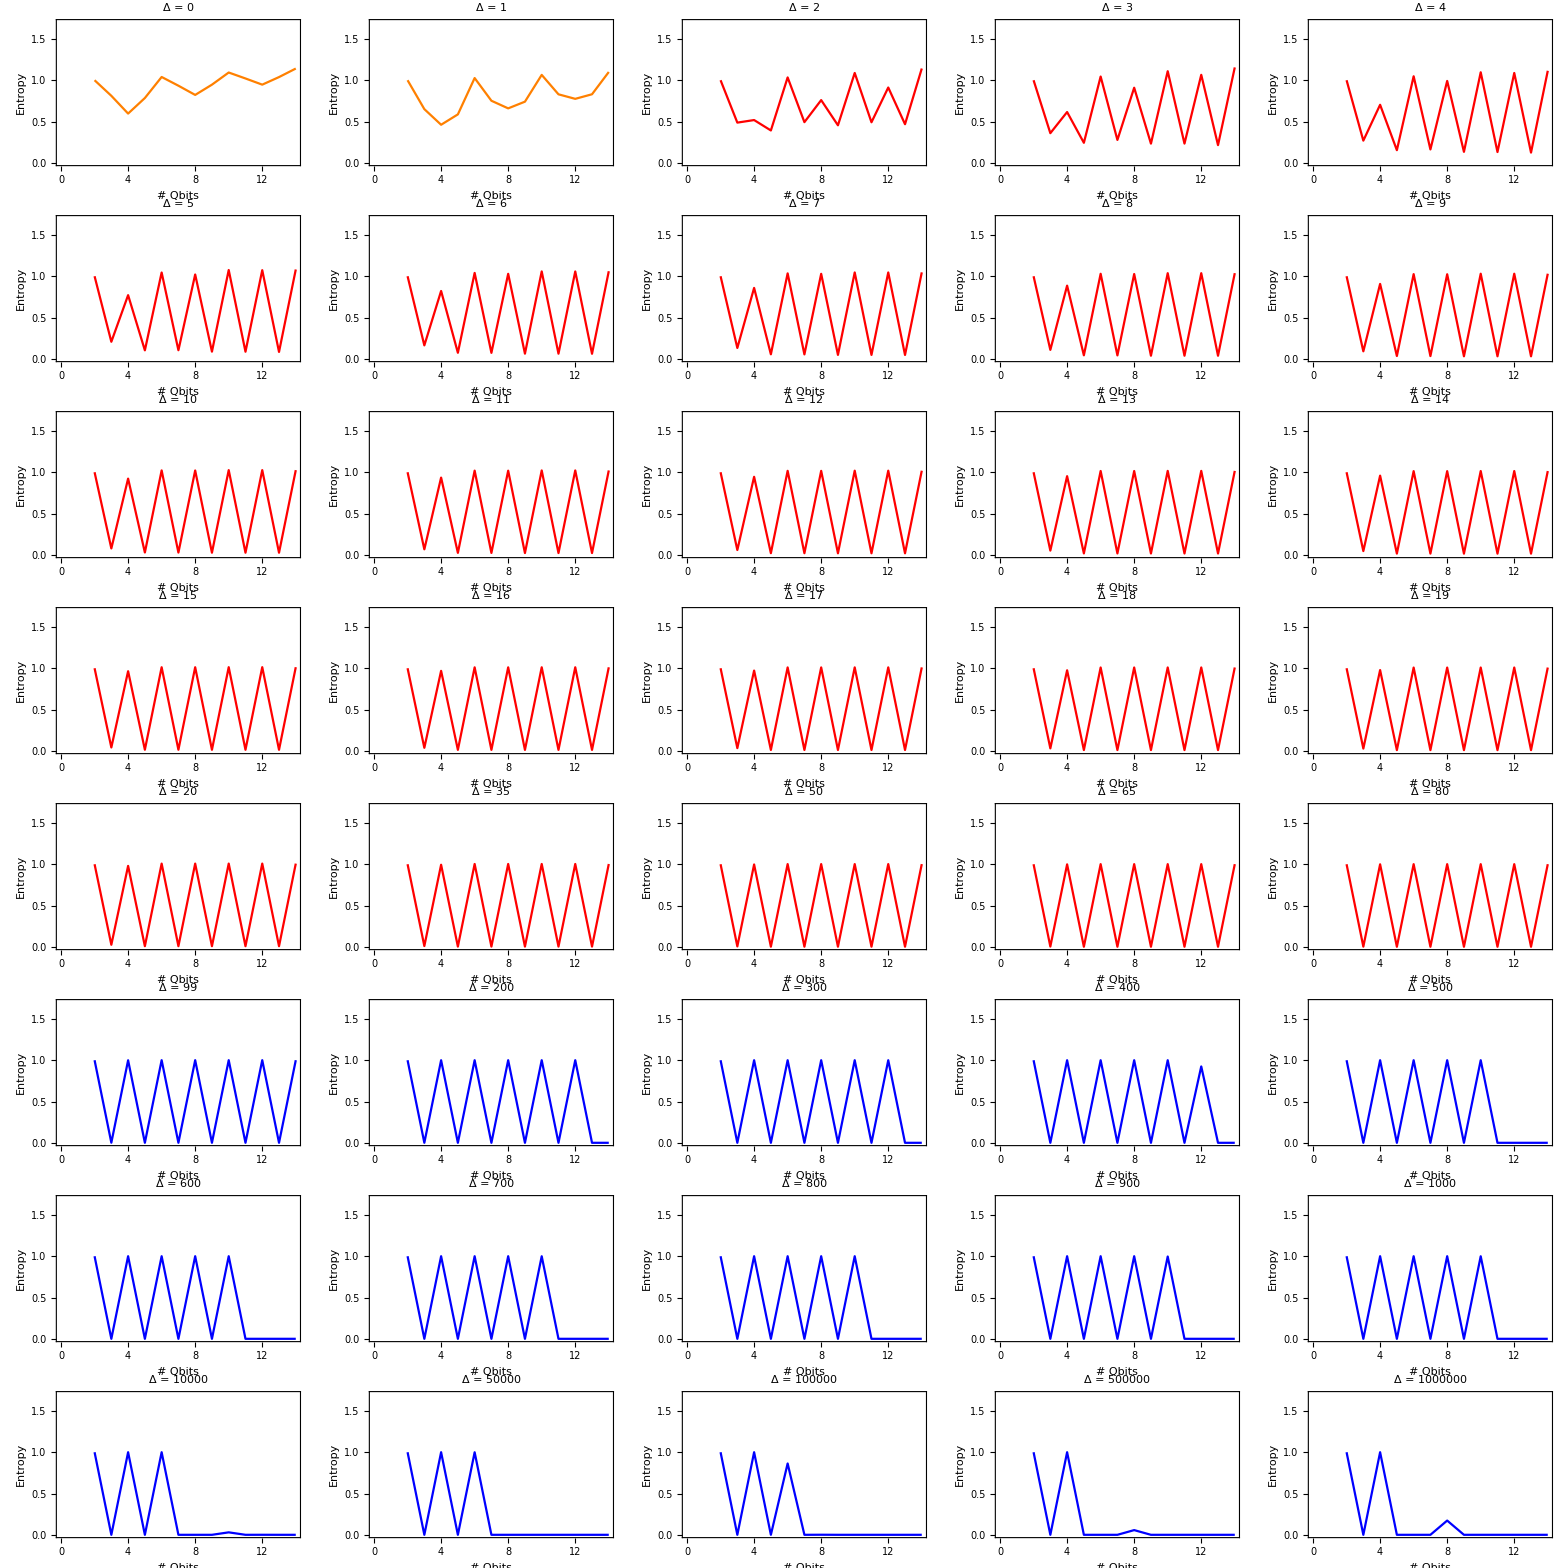

```mathematica
saveG = Grid[{{ListLinePlot[TabPlotD0,PlotStyle->{Orange},PlotRange->{{0,14},{0,1.7}},PlotLabel->"Δ = 0",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD1,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Orange},PlotLabel->"Δ = 1",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD2,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 2",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD3,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 3",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD4,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 4",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},{ListLinePlot[TabPlotD5,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 5",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD6,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 6",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD7,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 7",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD8,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 8",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD9,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 9",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},
{ListLinePlot[TabPlotD10,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 10",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD11,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 11",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD12,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 12",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD13,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 13",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD14,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 14",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},
{ListLinePlot[TabPlotD15,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 15",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD16,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 16",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD17,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 17",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD18,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 18",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD19,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 19",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},
{ListLinePlot[TabPlotD20,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 20",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD35,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 35",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD50,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 50",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD65,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 65",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD80,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 80",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},{ListLinePlot[TabPlotD99,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 99",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD200,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 200",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD300,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 300",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD400,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 400",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD500,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 500",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},{ListLinePlot[TabPlotD600,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 600",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD700,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 700",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD800,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 800",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD900,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 900",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD1000,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 1000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},{ListLinePlot[TabPlotD10000,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 10000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD50000,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 50000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD100000,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 100000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD500000,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 500000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD1000000,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 1000000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]}},Spacings->{0.5,0.5}]
```

#### Plot for Latex

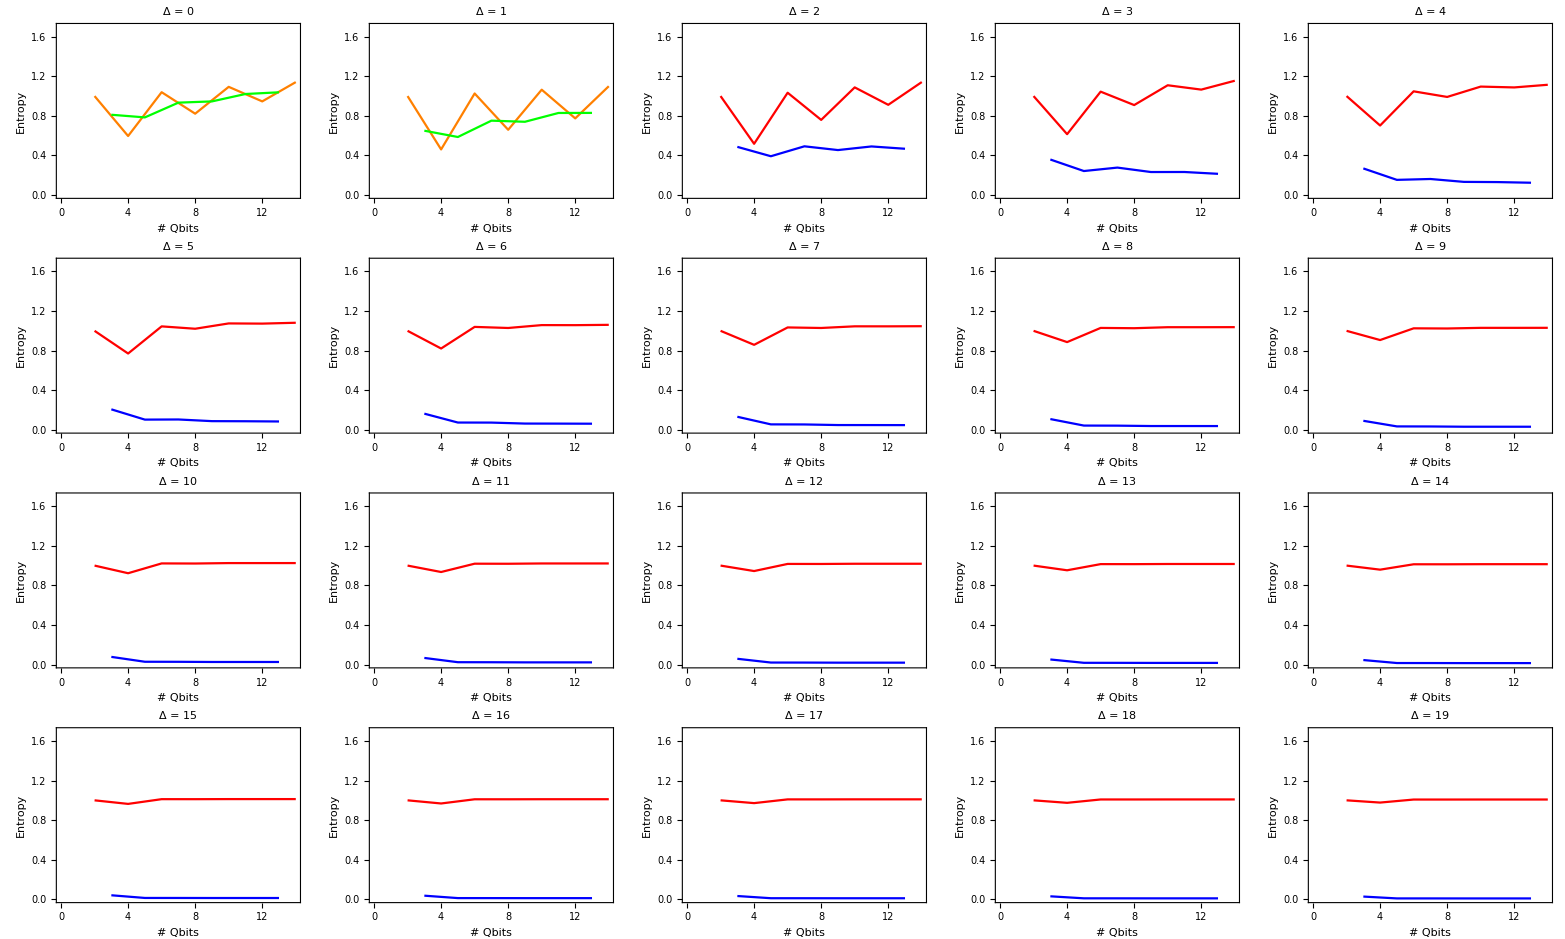

```mathematica
saveG1 = Grid[{{Show[ListLinePlot[Table[TabPlotD0[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Orange},PlotLabel->"Δ = 0",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD0[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Green},PlotLabel->"Δ = 0",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],Show[ListLinePlot[Table[TabPlotD1[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Orange},PlotLabel->"Δ = 1",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD1[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Green},PlotLabel->"Δ = 1",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],Show[ListLinePlot[Table[TabPlotD2[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 2",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD2[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 2",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],
Show[ListLinePlot[Table[TabPlotD3[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 3",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD3[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 3",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],Show[ListLinePlot[Table[TabPlotD4[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 4",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD4[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 4",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]]},
{Show[ListLinePlot[Table[TabPlotD5[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 5",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD5[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 5",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],Show[ListLinePlot[Table[TabPlotD6[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 6",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD6[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 6",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],Show[ListLinePlot[Table[TabPlotD7[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 7",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD7[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 7",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],
Show[ListLinePlot[Table[TabPlotD8[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 8",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD8[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 8",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],Show[ListLinePlot[Table[TabPlotD9[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 9",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD9[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 9",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]]},
{Show[ListLinePlot[Table[TabPlotD10[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 10",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD10[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 10",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],Show[ListLinePlot[Table[TabPlotD11[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 11",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD11[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 11",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],Show[ListLinePlot[Table[TabPlotD12[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 12",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD12[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 12",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],
Show[ListLinePlot[Table[TabPlotD13[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 13",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD13[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 13",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],Show[ListLinePlot[Table[TabPlotD14[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 14",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD14[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 14",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]]},{Show[ListLinePlot[Table[TabPlotD15[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 15",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD15[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 15",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],Show[ListLinePlot[Table[TabPlotD16[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 16",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD16[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 16",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],Show[ListLinePlot[Table[TabPlotD17[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 17",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD17[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 17",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],
Show[ListLinePlot[Table[TabPlotD18[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 18",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD18[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 18",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],Show[ListLinePlot[Table[TabPlotD19[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Red},PlotLabel->"Δ = 19",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD19[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Blue},PlotLabel->"Δ = 19",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]]}},Spacings->{0.5,0.5}]
```

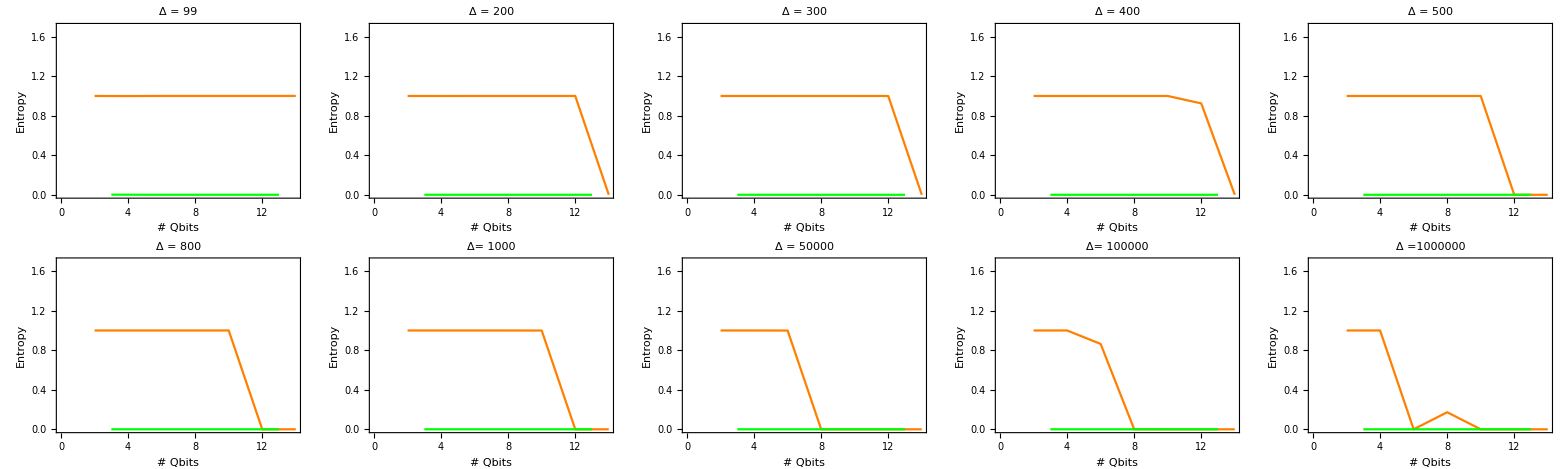

```mathematica
saveG2 = Grid[{
{Show[ListLinePlot[Table[TabPlotD99[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Orange},PlotLabel->"Δ = 99",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD99[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Green},PlotLabel->"Δ = 99",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],Show[ListLinePlot[Table[TabPlotD200[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Orange},PlotLabel->"Δ = 200",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD200[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Green},PlotLabel->"Δ = 200",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],Show[ListLinePlot[Table[TabPlotD300[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Orange},PlotLabel->"Δ = 300",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD300[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Green},PlotLabel->"Δ = 300",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],
Show[ListLinePlot[Table[TabPlotD400[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Orange},PlotLabel->"Δ = 400",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD400[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Green},PlotLabel->"Δ = 400",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],Show[ListLinePlot[Table[TabPlotD500[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Orange},PlotLabel->"Δ = 500",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD500[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Green},PlotLabel->"Δ = 500",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]]},{Show[ListLinePlot[Table[TabPlotD800[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Orange},PlotLabel->"Δ = 800",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD800[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Green},PlotLabel->"Δ = 800",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],Show[ListLinePlot[Table[TabPlotD1000[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Orange},PlotLabel->"Δ= 1000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD1000[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Green},PlotLabel->"Δ= 1000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],Show[ListLinePlot[Table[TabPlotD50000[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Orange},PlotLabel->"Δ = 50000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD50000[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Green},PlotLabel->"Δ = 50000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],
Show[ListLinePlot[Table[TabPlotD100000[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Orange},PlotLabel->"Δ= 100000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD100000[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Green},PlotLabel->"Δ= 100000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]],Show[ListLinePlot[Table[TabPlotD1000000[[i]],{i,1,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Orange},PlotLabel->"Δ =1000000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[Table[TabPlotD1000000[[i]],{i,2,13,2}],PlotRange->{{0,14},{0,1.7}},PlotStyle->{Green},PlotLabel->"Δ =1000000",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]]}},Spacings->{0.5,0.5}]
```

### Entropy vs. Proportion

#### Data

```mathematica
TabPlotD2N2={{1,1.0}};
TabPlotD2N3={{1,0.48669228723541275}};
TabPlotD2N4={{1,0.9999999999999999},{2,0.5176968120114409}};
TabPlotD2N5={{1,0.6181434380447753},{2,0.3918412974487525}};
TabPlotD2N6={{1,0.9999999999999998},{2,0.6163997910254653},{3,1.033870462698026}};
TabPlotD2N7={{1,0.6796821748968414},{2,0.3823723990990454},{3,0.49220276787445966}};
TabPlotD2N8={{1,1.0},{2,0.6586289583268319},{3,1.05318561784557},{4,0.7592390594401701}};
TabPlotD2N9={{1,0.7141390317929661},{2,0.3895081801069862},{3,0.5467224206389479},{4,0.45422220939744024}};
TabPlotD2N10={{1,0.9999999999999999},{2,0.6821780126859123},{3,1.0648005568144752},{4,0.8270098599324964},{5,1.0878965581128928}};
TabPlotD2N11={{1,0.7353239223328061},{2,0.3990110582203695},{3,0.5812740430118969},{4,0.4451462396106074},{5,0.4908653791004461}};
TabPlotD2N12={{1,0.9999999999999999},{2,0.6973371859192371},{3,1.0724578286764244},{4,0.8672022683760887},{5,1.110514210726094},{6,0.9117265669920328}};
TabPlotD5N2={{1,1.0}};
TabPlotD5N3={{1,0.2063028633098469}};
TabPlotD5N4={{1,0.9999999999999998},{2,0.7707208759079688}};
TabPlotD5N5={{1,0.23449667772205737},{2,0.1024962550590212}};
TabPlotD5N6={{1,0.9999999999999993},{2,0.8985928709207389},{3,1.0450159350202546}};
TabPlotD5N7={{1,0.23939198366283918},{2,0.09191762336627453},{3,0.10384317823419144}};
TabPlotD5N8={{1,0.9999999999999998},{2,0.9409953088989064},{3,1.0591461999140155},{4,1.0210754400983064}};
TabPlotD5N9={{1,0.24023099985996538},{2,0.09090865023417437},{3,0.10405146262903467},{4,0.08701800748985981}};
TabPlotD5N10={{1,1.0000000000000004},{2,0.9568382640734715},{3,1.0632450217194305},{4,1.05148594168659},{5,1.0748626958770486}};
TabPlotD5N11={{1,0.24037124600971677},{2,0.09082103976557847},{3,0.10411996010951077},{4,0.08491855051068498},{5,0.08595487416459349}};
TabPlotD5N12={{1,1.0000000000000007},{2,0.9629437020781615},{3,1.0645236049268996},{4,1.0607233742523001},{5,1.078524047616068},{6,1.0729677259093449}};
TabPlotD10N2={{1,1.0}};
TabPlotD10N3={{1,0.07703987497884078}};
TabPlotD10N4={{1,0.9999999999999997},{2,0.9227056909492155}};
TabPlotD10N5={{1,0.08045691049329665},{2,0.027769360343648505}};
TabPlotD10N6={{1,1.0000000000000007},{2,0.9848628553649325},{3,1.0218693733412645}};
TabPlotD10N7={{1,0.08061852172293892},{2,0.026220757782884248},{3,0.02726093401443486}};
TabPlotD10N8={{1,1.0},{2,0.994181091797193},{3,1.0236619082910225},{4,1.0208780062661362}};
TabPlotD10N9={{1,0.08062577548143217},{2,0.02617302395805726},{3,0.027237310393533772},{4,0.02548275871248751}};
TabPlotD10N10={{1,0.9999999999999998},{2,0.9959097926910355},{3,1.0238237436974675},{4,1.0237535902396848},{5,1.0252130299871267}};
TabPlotD10N11={{1,0.08062609133343145},{2,0.026171487434396675},{3,0.02723654837208345},{4,0.02542456627080827},{5,0.025446978754447958}};
TabPlotD10N12={{1,0.9999999999999996},{2,0.9962482952426942},{3,1.023846106608894},{4,1.024154023205078},{5,1.0253034628651125},{6,1.0252057355911537}};
TabPlotD49N2={{1,1.0}};
TabPlotD49N3={{1,0.005266067095937375}};
TabPlotD49N4={{1,0.9999999999999998},{2,0.9967447372574553}};
TabPlotD49N5={{1,0.005277214056318076},{2,0.0015355371613888006}};
TabPlotD49N6={{1,1.0},{2,1.0002256620488066},{3,1.0015194778373016}};
TabPlotD49N7={{1,0.005277236399349539},{2,0.0015305596016958127},{3,0.0015331678242601215}};
TabPlotD49N8={{1,0.9999999999999994},{2,1.0003214631582125},{3,1.0015239680417987},{4,1.0015201410205001}};
TabPlotD49N9={{1,0.0052772364416246035},{2,0.0015305527804349687},{3,0.0015331635180322685},{4,0.00152815831521625}};
TabPlotD49N10={{1,1.0},{2,1.0003252950196921},{3,1.0015239909722677},{4,1.001525978220479},{5,1.0015281296587246}};
TabPlotD49N11={{1,0.005277236441701865},{2,0.0015305527705723875},{3,0.0015331635115151795},{4,0.0015281514323888356},{5,0.0015281539388626113}};
TabPlotD49N12={{1,0.9999999999996317},{2,1.0003254512446937},{3,1.0015239915828293},{4,1.0015261381695733},{5,1.0015281386192938},{6,1.0015281337079336}};
```

#### Delta = 2

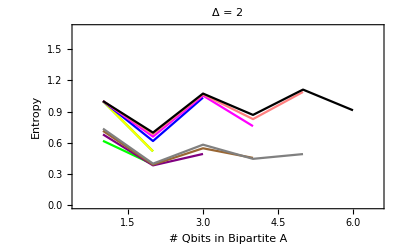

```mathematica
plotD2 = Show[ListLinePlot[TabPlotD2N2,PlotStyle->{Red},PlotRange->{{0.5,6.5},{0,1.7}},PlotLabel->"Δ = 2",FrameLabel->{{"Entropy",None},{"# Qbits in Bipartite A",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotD2N4,PlotStyle->{Green}],
ListLinePlot[TabPlotD2N3,PlotStyle->{Orange}],
ListLinePlot[TabPlotD2N4,PlotStyle->{Yellow}],
ListLinePlot[TabPlotD2N5,PlotStyle->{Green}],
ListLinePlot[TabPlotD2N6,PlotStyle->{Blue}],
ListLinePlot[TabPlotD2N7,PlotStyle->{Purple}],
ListLinePlot[TabPlotD2N8,PlotStyle->{Magenta}],
ListLinePlot[TabPlotD2N9,PlotStyle->{Brown}],
ListLinePlot[TabPlotD2N10,PlotStyle->{Pink}],
ListLinePlot[TabPlotD2N11,PlotStyle->{Gray}],
ListLinePlot[TabPlotD2N12,PlotStyle->{Black}]]
```

#### Delta = 5

```mathematica
plotD5 = Show[ListLinePlot[TabPlotD5N2,PlotStyle->{Red},PlotRange->{{0.5,6.5},{0,1.7}},PlotLabel->"Δ = 5",FrameLabel->{{"Entropy",None},{"# Qbits in Bipartite A",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD5N3,PlotStyle->{Orange}],
ListLinePlot[TabPlotD5N4,PlotStyle->{Yellow}],
ListLinePlot[TabPlotD5N5,PlotStyle->{Green}],
ListLinePlot[TabPlotD5N6,PlotStyle->{Blue}],
ListLinePlot[TabPlotD5N7,PlotStyle->{Purple}],
ListLinePlot[TabPlotD5N8,PlotStyle->{Magenta}],
ListLinePlot[TabPlotD5N9,PlotStyle->{Brown}],
ListLinePlot[TabPlotD5N10,PlotStyle->{Pink}],
ListLinePlot[TabPlotD5N11,PlotStyle->{Gray}],
ListLinePlot[TabPlotD5N12,PlotStyle->{Black}]]
```

-Graphics-

#### Delta = 10

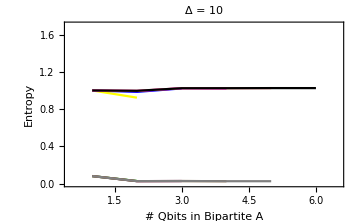

```mathematica
plotD10 = Show[ListLinePlot[TabPlotD10N2,PlotStyle->{Red},PlotRange->{{0.5,6.5},{0,1.7}},PlotLabel->"Δ = 10",FrameLabel->{{"Entropy",None},{"# Qbits in Bipartite A",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD10N3,PlotStyle->{Orange}],
ListLinePlot[TabPlotD10N4,PlotStyle->{Yellow}],
ListLinePlot[TabPlotD10N5,PlotStyle->{Green}],
ListLinePlot[TabPlotD10N6,PlotStyle->{Blue}],
ListLinePlot[TabPlotD10N7,PlotStyle->{Purple}],
ListLinePlot[TabPlotD10N8,PlotStyle->{Magenta}],
ListLinePlot[TabPlotD10N9,PlotStyle->{Brown}],
ListLinePlot[TabPlotD10N10,PlotStyle->{Pink}],
ListLinePlot[TabPlotD10N11,PlotStyle->{Gray}],
ListLinePlot[TabPlotD10N12,PlotStyle->{Black}]]
```

#### Delta = 49

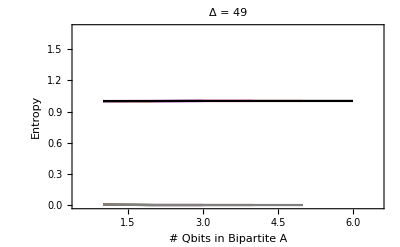

```mathematica
plotD49 = Show[ListLinePlot[TabPlotD49N2,PlotStyle->{Red},PlotRange->{{0.5,6.5},{0,1.7}},PlotLabel->"Δ = 49",FrameLabel->{{"Entropy",None},{"# Qbits in Bipartite A",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotD49N3,PlotStyle->{Orange}],
ListLinePlot[TabPlotD49N4,PlotStyle->{Yellow}],
ListLinePlot[TabPlotD49N5,PlotStyle->{Green}],
ListLinePlot[TabPlotD49N6,PlotStyle->{Blue}],
ListLinePlot[TabPlotD49N7,PlotStyle->{Purple}],
ListLinePlot[TabPlotD49N8,PlotStyle->{Magenta}],
ListLinePlot[TabPlotD49N9,PlotStyle->{Brown}],
ListLinePlot[TabPlotD49N10,PlotStyle->{Pink}],
ListLinePlot[TabPlotD49N11,PlotStyle->{Gray}],
ListLinePlot[TabPlotD49N12,PlotStyle->{Black}]]
```

#### Conclusion Graph

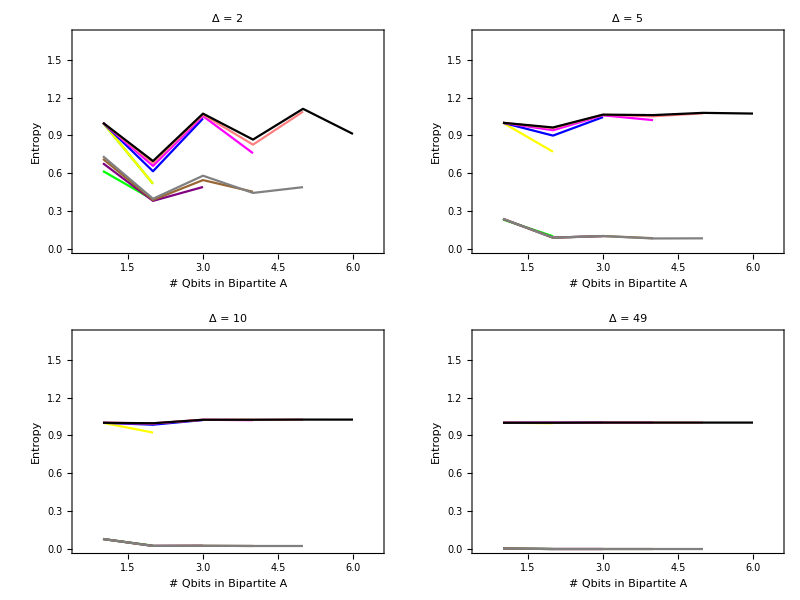

```mathematica
saveG2= Grid[{{plotD2,plotD5},{plotD10,plotD49}},Spacings->{0.5, 0.5}]
```

### Schmidt Coefficients Density Distribution vs. N

#### Data

```mathematica
SDTabPlotD0={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.8660254037844383,0.49999999999999967}},{4,{0.9472135954999574,0.22360679774997902,0.22360679774997883,0.05278640450004212}},{5,{0.8992110956392811,0.4216632165179902,0.10566243220168907,0.04954783280960645}},{6,{0.7057887247804753,0.7057887247804749,0.03050031721195912,0.030500317211959033,0.030500317211958977,0.03050031721195897,0.0013180564060717836,0.0013180564060713466}},{7,{0.8531616903381108,0.5089084642110112,0.0970799778484058,0.05790792412736208,0.0159515588949485,0.009515058436089067,0.0018151037507971762,0.0010827041024729107}},{8,{0.9176377014704852,0.27484567611064414,0.27484567611064353,0.08232022894838167,0.005952021315872261,0.0059520213158721635,0.0017827159021087577,0.0017827159021086751,0.0017827159021086706,0.0017827159021086348,0.0005339490265527666,0.0005339490265527241,3.860625788120943*10^-05,1.1563128926236561*10^-05,1.15631289258487*10^-05,3.4633232510869527*10^-06}},{9,{0.8688547772803633,0.4681609151705736,0.14043704759344428,0.07567103092993054,0.018665367678276486,0.010057371890857935,0.0030169703816192712,0.002261170243939649,0.0016256198985548347,0.0012183756807700216,0.0003654834863876976,0.00019693174042569394,4.8576097053207285*10^-05,2.617402890161727*10^-05,7.851580991616423*10^-06,4.2306302948037044*10^-06}},{10,{0.7034559547166882,0.7034559547166876,0.050673574845129014,0.050673574845128966,0.05067357484512867,0.0506735748451286,0.0036502799789633706,0.0036502799789633065,0.0006184235833606887,0.0006184235833606601,0.0006184235833606284,0.0006184235833606034,4.4548252846979466*10^-05,4.454825284697636*10^-05,4.454825284694894*10^-05,4.454825284694693*10^-05,4.454825284694447*10^-05,4.4548252846920526*10^-05,4.454825284690097*10^-05,4.4548252846889315*10^-05,3.2090413192020853*10^-06,3.2090413191113558*10^-06,3.2090413191063024*10^-06,3.2090413190896404*10^-06,5.436697577658039*10^-07,5.436697576665447*10^-07,3.9163347849179394*10^-08,3.9163347789154914*10^-08,3.9163347787320585*10^-08,3.916334767057262*10^-08,2.821139030749076*10^-09,2.8211386135481543*10^-09}},{11,{0.8421216339901912,0.5155905145533725,0.13156243829814313,0.08054934408540076,0.029048020343076773,0.01778470371848698,0.004538095483857011,0.0029404783930781263,0.0027784572811977593,0.0018003132879233074,0.0004593831716725009,0.0002835682009950468,0.00028125818919696435,0.00017361515101951713,0.00010142843115893438,6.209974295951982*10^-05,4.43011109570474*10^-05,2.7123436415446097*10^-05,1.5845895862777633*10^-05,9.781360006306453*10^-06,9.70167879752905*10^-06,5.988655599293684*10^-06,1.5281160349791986*10^-06,9.901493255508636*10^-07,9.355918444188095*10^-07,6.06220740201316*10^-07,1.5468841353050624*10^-07,9.470826479617933*10^-08,3.4154065826036437*10^-08,2.0910889510686734*10^-08,5.335799484119201*10^-09,3.26685298202818*10^-09}},{12,{0.8993622651407739,0.3005501045336428,0.30055010453364156,0.10043824255962536,0.012703617265554077,0.012703617265554048,0.004245312089583987,0.004245312089583884,0.004245312089583878,0.004245312089583806,0.0014187041660044255,0.0014187041660044112,0.00017944036333824507,0.00010072178165550566,0.00010072178165547513,5.996562458674137*10^-05,5.9965624586733203*10^-05,3.365934193455313*10^-05,3.365934193450729*10^-05,3.3659341934458474*10^-05,3.365934193439856*10^-05,2.003939395337478*10^-05,1.124832465075341*10^-05,1.1248324650683025*10^-05,1.4227091953638662*10^-06,1.422709195242699*10^-06,1.4227091952268654*10^-06,1.4227091952101355*10^-06,4.7544289323550373*10^-07,4.754428932054466*10^-07,4.7544289318570497*10^-07,4.7544289316851423*10^-07,4.754428931632762*10^-07,4.754428931619994*10^-07,4.7544289315299187*10^-07,4.7544289303098276*10^-07,1.5888415245116435*10^-07,1.5888415245019815*10^-07,1.5888415244404435*10^-07,1.588841524327205*10^-07,2.0095965550954224*10^-08,2.0095965543316392*10^-08,1.1280078895072554*10^-08,6.715697127046996*10^-09,6.715697100768158*10^-09,6.715697089234234*10^-09,6.715697078218877*10^-09,3.769592102327994*10^-09,3.7695920957012365*10^-09,2.2442608148733622*10^-09,2.2442607754473005*10^-09,1.2597273761125519*10^-09,1.5933272054426261*10^-10,1.5933268113040673*10^-10,5.32460180983146*10^-11,5.3246012132884655*10^-11,5.324599606170498*10^-11,5.324591947287437*10^-11,1.7793850487797245*10^-11,1.779377282674462*10^-11,2.2506169333681066*10^-12,7.522190297001338*10^-13,7.522021423026972*10^-13,2.511343295531*10^-13}},{13,{0.8519078546455119,0.4884374902374368,0.16075016694622327,0.09216537641988728,0.030821861402653125,0.01767157392183261,0.00581590994736339,0.005338447304288863,0.003334525491984322,0.0030607744591774773,0.0010073346439036337,0.0005775507322939933,0.000441267872407565,0.000252998925817907,0.00019314399089163895,0.0001107382279094049,8.326473781254386*10^-05,4.7739458370635716*10^-05,3.6445172574912715*10^-05,3.539877375600384*10^-05,2.08956737829073*10^-05,2.0295725783792683*10^-05,1.596498627242726*10^-05,9.153452200325625*10^-06,6.679547277285767*10^-06,3.829688023477612*10^-06,3.012502108764189*10^-06,2.7651878909983043*10^-06,1.7272043699468147*10^-06,1.5854078891009047*10^-06,1.280720787594844*10^-06,7.342954332261182*10^-07,5.217752280276981*10^-07,2.991574516706576*10^-07,2.4166472852161343*10^-07,2.218250334350581*10^-07,1.385573719405328*10^-07,1.2718237307945657*10^-07,1.0004396305432107*10^-07,5.735975077277473*10^-08,4.1857122184137394*10^-08,2.3998590458282875*10^-08,1.887772680325028*10^-08,1.833571727560542*10^-08,1.0823458741340599*10^-08,1.0512700042301437*10^-08,8.025586829114561*10^-09,4.6014336463506415*10^-09,3.459845560688451*10^-09,1.9836867058053194*10^-09,1.5143825885863254*10^-09,8.682643487874605*10^-10,6.633827216535744*10^-10,3.8034745374780755*10^-10,1.2517652719313726*10^-10,1.149000598284978*10^-10,7.176939980237339*10^-11,6.587743081319172*10^-11,2.1680987411858566*10^-11,1.243070675749083*10^-11,4.157037443489076*10^-12,2.3834360298930754*10^-12,7.84422426153386*10^-13,4.497361063914498*10^-13}}};
SDTabPlotD1={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9128709291752767,0.4082482904638631}},{4,{0.9659258262890684,0.14942924536134264,0.14942924536134228,0.14942924536134225}},{5,{0.9378422307163594,0.33301829929688037,0.0851343419991917,0.04798860730154231}},{6,{0.7062514170867404,0.7062514170867394,0.03215120295316423,0.03215120295316412,0.009360449017965417,0.009360449017965193,0.009360449017965122,0.009360449017964944}},{7,{0.9022386111036101,0.4210843722270598,0.08155330034486913,0.041931646219838865,0.014292081525517867,0.005538114082115039,0.002561668484862957,0.001655264564663494}},{8,{0.9451924199343305,0.18846487072093995,0.1884648707209399,0.18846487072093976,0.004058155213305824,0.0040581552133057185,0.004058155213305708,0.0020345223027194914,0.00043630952756457673,0.0004363095275645284,0.000436309527564443,0.00017352860521695096,0.0001735286052166201,0.00017352860521655422,0.00017352860521649142,0.0001735286052164371}},{9,{0.9149231980736728,0.3804894217985,0.11598068371579663,0.06611315715004248,0.01618916149743231,0.006644558832160224,0.0027124117055384116,0.00177027673737128,0.0016772408452941487,0.001118955968793001,0.00022870027765108466,0.00011846643379220542,9.369681384429653*10^-05,4.055898873858219*10^-05,2.3851367842342153*10^-05,1.6824634368177363*10^-05}},{10,{0.7046836085783974,0.7046836085783934,0.053559635840785616,0.05355963584078548,0.01661145513067876,0.01661145513067873,0.016611455130678684,0.016611455130678663,0.0006381693905261168,0.0006381693905260707,0.00020758679017609838,0.00020758679017609535,0.00020758679017609014,0.00020758679017598774,5.0694033920755866*10^-05,5.0694033920724864*10^-05,1.1532080564380554*10^-05,1.153208056434974*10^-05,1.1532080564320503*10^-05,1.1532080564295843*10^-05,5.934532604129972*10^-06,5.934532604039485*10^-06,1.9870274586963556*10^-06,1.9870274586816994*10^-06,1.9870274586567937*10^-06,1.987027458623484*10^-06,9.515732895683258*10^-07,9.515732895680657*10^-07,9.515732895251279*10^-07,9.515732895239488*10^-07,9.515732894585672*10^-07,9.515732893626149*10^-07}},{11,{0.8928678809413167,0.43117080313637224,0.11153525262917706,0.059964363008708506,0.02606627518758548,0.010831954846821933,0.005154943968850473,0.003344645746134385,0.0024586037335149117,0.0014181560902388844,0.0003497241119009236,0.0002669504079244008,0.00016247544363689556,0.00012469398764398636,8.436803231857989*10^-05,5.353162990774338*10^-05,4.77496160911337*10^-05,3.409664211939159*10^-05,2.998913312009666*10^-05,2.0645066144509117*10^-05,7.545604980921366*10^-06,3.4419659338498928*10^-06,2.053572385514599*10^-06,1.5503338162237963*10^-06,1.4167629676749175*10^-06,8.850399640203856*10^-07,3.7257041621035807*10^-07,2.1147738236244327*10^-07,1.9421674894413875*10^-07,1.008477485609568*10^-07,6.738998033573518*10^-08,5.046987305653821*10^-08}},{12,{0.9317240613391329,0.20946622530605574,0.20946622530605535,0.20946622530605447,0.00881675495013814,0.00881675495013811,0.008816754950138093,0.004876283155714535,0.0011403091510243297,0.0011403091510241118,0.0011403091510239004,0.00046352419857045683,0.00046352419857044155,0.00046352419857039487,0.00046352419857039346,0.0004635241985703737,6.904923736706593*10^-05,6.904923736706514*10^-05,6.904923736704854*10^-05,3.7789006272419094*10^-05,9.20513188789048*10^-06,9.205131887880578*10^-06,9.205131887874754*10^-06,3.7770236837114273*10^-06,3.7770236837101444*10^-06,3.7770236836999157*10^-06,3.777023683696425*10^-06,3.7770236836773304*10^-06,1.6781391830423188*10^-06,3.9510913574659065*10^-07,3.951091357443355*10^-07,3.951091357233376*10^-07,2.8672318313778745*10^-07,2.8672318313573414*10^-07,2.867231831063452*10^-07,1.277560932952061*10^-07,1.277560932770893*10^-07,1.2775609327378687*10^-07,1.277560932719175*10^-07,1.2775609327122902*10^-07,3.4651069152640203*10^-08,3.465106914681038*10^-08,3.4651069142664584*10^-08,2.4004466575573576*10^-08,1.2210979107778935*10^-08,1.2210979085045826*10^-08,1.221097907983873*10^-08,1.2210979078434798*10^-08,1.2210979070590471*10^-08,6.635798152981639*10^-09,6.6357981300074326*10^-09,6.635798120121136*10^-09,2.848583300928055*10^-09,2.8485832918744033*10^-09,2.8485832831117036*10^-09,2.8485832795422244*10^-09,2.848583253349034*10^-09,1.5431954946322439*10^-09,1.543195438633916*10^-09,1.543195374913281*10^-09,1.543195374214482*10^-09,1.5431953742113474*10^-09,1.5431953671141995*10^-09,1.5431952841947936*10^-09}},{13,{0.9011776267123776,0.4034446595118031,0.1346939474164815,0.077704744278626,0.027025312164491118,0.011713800350834726,0.005120251551055637,0.00430091805092003,0.0032187831355299447,0.00270625829440806,0.0006513492136674979,0.0004146175157483224,0.0003066125382859028,0.00028157133526657453,0.00015053778700162192,0.000124956846858542,7.46655064408296*10^-05,7.312836691412245*10^-05,5.275968408689784*10^-05,4.8416546175841586*10^-05,2.892862026628602*10^-05,1.7815200969764435*10^-05,1.2398660371825357*10^-05,6.708267548699801*10^-06,3.5883676232597793*10^-06,3.5376252376504427*10^-06,2.5067972246602533*10^-06,2.311304398981395*10^-06,2.250262207919368*10^-06,1.3897339857691861*10^-06,1.1827732660671508*10^-06,6.579348787626768*10^-07,6.261538903041432*10^-07,4.571309839726575*10^-07,3.6159150317203535*10^-07,3.4197008194549313*10^-07,3.3479731824187965*10^-07,1.9399223254093928*10^-07,1.6125815015585995*10^-07,1.1420791398283544*10^-07,1.0448716059001329*10^-07,7.709249215860713*10^-08,5.130537291189336*10^-08,3.662743739582744*10^-08,1.8594683373849876*10^-08,1.630439506483901*10^-08,1.3261949959675571*10^-08,1.1617923513407918*10^-08,1.0236239805578799*10^-08,5.914688434011336*10^-09,3.4760543300290256*10^-09,2.450045548084003*10^-09,2.2195584617522377*10^-09,1.286305739607914*10^-09,9.262120960342308*10^-10,8.220929222893139*10^-10,4.791979450503988*10^-10,2.89827057531264*10^-10,2.323399132142896*10^-10,1.5291709326327512*10^-10,1.265547414631686*10^-10,7.906594450468902*10^-11,5.7186020426611785*10^-11,4.4712472900747425*10^-11}}};
SDTabPlotD2={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9456942250523721,0.32505758367186816}},{4,{0.9567064232130147,0.24437855678560128,0.11178537642810575,0.11178537642810558}},{5,{0.9656169258624624,0.2461823097568479,0.08046178806731207,0.022452694976818333}},{6,{0.7059376566882117,0.7059376566882108,0.0381713668486991,0.03817136684869906,0.013423611210005099,0.013423611210005017,0.003844253444041058,0.0038442534440408164}},{7,{0.9498819456210426,0.3048835923710182,0.06524373093740968,0.01721006202262877,0.013953694890867008,0.004583872828771378,0.0012355337359463783,0.0003313455007628342}},{8,{0.9245812562091759,0.32579957143172167,0.13952069071344583,0.13952069071344447,0.006944291821507662,0.002814374331881627,0.0027222828768962695,0.0027222828768962474,0.0006415109032426756,0.0006415109032426364,0.0004000674473269495,0.00034784417959077697,0.00010574658102801428,0.00010574658102791671,2.8466269662560065*10^-05,2.8466269662558283*10^-05}},{9,{0.9587083789638539,0.26623714923818537,0.09526841201884181,0.026282429653947784,0.014298641208760697,0.004399426678204636,0.0019509135774626657,0.0010712015810623076,0.0005410911705391268,0.0002850590395233663,0.00021757238060304026,6.458263215500082*10^-05,5.119828833729441*10^-05,1.4707942838761666*10^-05,3.891687042993518*10^-06,1.0418306153215055*10^-06}},{10,{0.7034872585549781,0.7034872585549707,0.06722965467592244,0.06722965467592192,0.023292308266787364,0.023292308266787035,0.0065332127528321265,0.006533212752832117,0.0007409832086434888,0.0007409832086434398,0.00027443809633494485,0.0002744380963348949,7.694728352669466*10^-05,7.694728352663039*10^-05,7.349453720025941*10^-05,7.349453720023187*10^-05,1.75351556958051*10^-05,1.7535155695789232*10^-05,7.450049894736623*10^-06,7.450049894724127*10^-06,4.766254154008849*10^-06,4.766254153984068*10^-06,2.177342364033436*10^-06,2.1773423639685952*10^-06,2.028485311816584*10^-06,2.028485311759199*10^-06,6.252506431027583*10^-07,6.252506428770232*10^-07,1.683464077226707*10^-07,1.6834640771951337*10^-07,4.512387394961517*10^-08,4.5123873948714935*10^-08}},{11,{0.95221805477515,0.29287912943588595,0.08014925700821729,0.02347434692235999,0.021482447056701836,0.00741547696333211,0.0025003038632203443,0.0020064281525832314,0.0006632690587823836,0.0005379716540449681,0.00027628178184290234,0.00024812288186880024,7.33008201361683*10^-05,6.939303374485772*10^-05,5.4650902773897704*10^-05,2.159090058622299*10^-05,1.5111811736465286*10^-05,8.335865442011802*10^-06,5.852724475167649*10^-06,3.936486562910866*10^-06,2.4482455892064226*10^-06,1.4924629645512425*10^-06,1.0526483758425093*10^-06,9.08808178222265*10^-07,3.959238236230252*10^-07,2.5184671904964474*10^-07,1.415386608667762*10^-07,3.843571313546938*10^-08,3.599051569452549*10^-08,9.735373646488506*10^-09,2.5979433234831514*10^-09,6.959123932588656*10^-10}},{12,{0.8988857164971427,0.37997803336669683,0.15371533963685155,0.15371533963685063,0.015500694603899587,0.0072645639799730774,0.005612740842615339,0.005612740842615269,0.001790339266372896,0.0017903392663728723,0.000975667063522501,0.0008800059984563119,0.0002587609881622022,0.00025876098816216285,0.00011315673513604734,6.955998101128913*10^-05,6.955998101108105*10^-05,5.309118274387783*10^-05,4.3284532345900517*10^-05,4.328453234587797*10^-05,1.3466578435100946*10^-05,1.3466578435088896*10^-05,7.71573803660643*10^-06,6.95908201734245*10^-06,2.208678684182341*10^-06,2.0518577713921593*10^-06,2.0518577713901946*10^-06,9.668841493135991*10^-07,5.516772367991043*10^-07,5.516772367805715*10^-07,4.856972878564513*10^-07,4.856972878507401*10^-07,2.6962248823482414*10^-07,2.696224882297393*10^-07,2.380521211965673*10^-07,2.1713217942479764*10^-07,6.436570641758571*10^-08,6.436570640531617*10^-08,5.487715175377014*10^-08,5.247213987480617*10^-08,3.551783189706912*10^-08,3.5517831857665576*10^-08,1.7315689732504548*10^-08,1.7315689719260404*10^-08,1.3985602538981812*10^-08,1.3985602536972193*10^-08,1.1053116808125174*10^-08,9.326736785458041*10^-09,3.7398590985840286*10^-09,3.739859076326882*10^-09,2.934210250572215*10^-09,2.9342102241510422*10^-09,2.7153659466168324*10^-09,2.7153659333141394*10^-09,7.887058254088894*10^-10,7.879930453916631*10^-10,7.839176280746366*10^-10,7.839175140601819*10^-10,2.1233340006125547*10^-10,2.123332876541507*10^-10,5.6915646880049205*10^-11,5.691564466046487*10^-11,1.5250906850691162*10^-11,1.525090646626184*10^-11}},{13,{0.9573837127346598,0.2696421611470982,0.09724531194012605,0.02667761578634954,0.0217530042814563,0.006549138260024638,0.004491813540541276,0.0016741730190232822,0.0012183690497977527,0.0005016013463829514,0.0004470317299020206,0.0003679473076666976,0.00014136116629895988,0.00012392522391717556,0.00010970012058787597,3.480069197070623*10^-05,3.0072630401207712*10^-05,2.856552722291749*10^-05,1.3721719665440186*10^-05,9.236836543501255*10^-06,8.151308281709399*10^-06,7.637001979553621*10^-06,4.3549866771157204*10^-06,2.473307191380977*10^-06,2.438895187424775*10^-06,2.1109511380810024*10^-06,1.147592566424113*10^-06,8.698027052611625*10^-07,6.308544107726902*10^-07,5.595822867494986*10^-07,3.0771475478913743*10^-07,2.5356230019082433*10^-07,2.3411893036613454*10^-07,1.8100131509014447*10^-07,7.615952459431332*10^-08,6.46384952507611*10^-08,4.8308958937719794*10^-08,4.4264667886664066*10^-08,3.1887705746543284*10^-08,2.3112788368799255*10^-08,1.7349033709251983*10^-08,1.1898914321694286*10^-08,1.1744989167671871*10^-08,9.291576486956709*10^-09,6.216792726476302*10^-09,3.611330479691323*10^-09,3.1635998697987537*10^-09,2.417457599889331*10^-09,1.0774015582900098*10^-09,1.0707364931233575*10^-09,8.472753376692015*10^-10,6.464006743816975*10^-10,3.0896155212084163*10^-10,2.9113367538297386*10^-10,2.487647445938038*10^-10,8.611298748010624*10^-11,6.639002822491518*10^-11,2.3127907111473485*10^-11,1.9376871877252516*10^-11,5.194546829894542*10^-12,5.125156239487193*10^-12,1.3735766095557263*10^-12,3.676865918251889*10^-13,9.851048693657981*10^-14}}};
SDTabPlotD3={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9653505678131907,0.2609564738088524}},{4,{0.9376638480795844,0.32411897407825957,0.08869441540210568,0.08869441540210515}},{5,{0.9818015510985859,0.17957961036749692,0.06081610764206749,0.010875608118073426}},{6,{0.7054326717723785,0.70543267177237,0.04742724978892434,0.04742724978892383,0.010583899307975691,0.010583899307975519,0.0018391979196828905,0.0018391979196826817}},{7,{0.9771654226437082,0.20834103644482563,0.03967504319166305,0.010741521681790593,0.006827521567814787,0.0023382268247297785,0.0004153757742172982,7.134325493412695*10^-05}},{8,{0.8778768394266023,0.4540301042312354,0.1074862749812761,0.10748627498127464,0.007697186765919703,0.004089722143669972,0.0016179361785089955,0.0016179361785089138,0.0007162718612571159,0.000716271861257028,0.0002076742507970903,0.00020214915578254804,3.5546317147685394*10^-05,3.554631714754481*10^-05,6.100811041551839*10^-06,6.100811041525351*10^-06}},{9,{0.9825969521917982,0.17758173657820528,0.05294271490531021,0.009253628833246017,0.008630631977605116,0.0016421948986318682,0.001436940729743362,0.0002730496004848475,0.00024882168121104995,8.462441385820024*10^-05,4.6808670449863646*10^-05,1.527986726073179*10^-05,1.4056617655653188*10^-05,2.4789022545262277*10^-06,4.244991045715539*10^-07,7.282841316515915*10^-08}},{10,{0.7021613853744635,0.7021613853744315,0.08184256694402901,0.08184256694402571,0.01621059973127239,0.016210599731271536,0.002796391432771908,0.0027963914327716376,0.0007382497860770659,0.0007382497860769799,0.00016188687156599884,0.00016188687156597125,8.689722022627108*10^-05,8.689722022623579*10^-05,2.795363669034867*10^-05,2.7953636690345724*10^-05,1.4284568118522272*10^-05,1.4284568118522045*10^-05,3.590492011819801*10^-06,3.590492011743373*10^-06,2.447703024390475*10^-06,2.4477030243729412*10^-06,6.226059112016532*10^-07,6.226059111877638*10^-07,6.210061024480771*10^-07,6.210061024389257*10^-07,1.0779647186955559*10^-07,1.0779647185804026*10^-07,1.85012514275751*10^-08,1.8501251426534788*10^-08,3.174344725071267*10^-09,3.174344724990945*10^-09}},{11,{0.9820317502850625,0.1843149569819458,0.03771747498365558,0.012963586927345542,0.0065007665169052875,0.0024565854032912,0.001544882909667138,0.00043032515650082674,0.0002637755502106133,0.00016643252407505781,7.387577897108075*10^-05,7.063497941141575*10^-05,3.0297931314506726*10^-05,1.2091656415786562*10^-05,1.0389421563498617*10^-05,5.521904962864807*10^-06,2.829084903547366*10^-06,1.7981844392590538*10^-06,9.49098945720097*10^-07,5.222061317465081*10^-07,3.8746642959049047*10^-07,3.068911566622147*10^-07,1.0975343023221665*10^-07,6.631212589999328*10^-08,5.264590885149768*10^-08,1.896611916583399*10^-08,1.3436960152781729*10^-08,2.309533836072377*10^-09,2.2739151449257805*10^-09,3.9073311697786523*10^-10,6.701123329043811*10^-11,1.1497132121415323*10^-11}},{12,{0.8250270581746844,0.5409730838601328,0.11477041429830043,0.11477041429829177,0.01470580042327315,0.009785288555513373,0.0027979718643291337,0.002797971864329106,0.0017263466673467383,0.001726346667346727,0.00040613227194926424,0.0004002032666947346,9.631155645496818*10^-05,6.953184739112862*10^-05,6.953184739103471*10^-05,6.416443320417567*10^-05,1.99894288310035*10^-05,1.998942883090385*10^-05,1.1931619873123976*10^-05,1.1931619872914222*10^-05,1.1623527268898273*10^-05,1.1623527268889849*10^-05,2.9722468482483346*10^-06,2.9296659683693088*10^-06,1.7498670448162762*10^-06,1.1617461577425612*10^-06,5.097114377316084*10^-07,5.097114376785728*10^-07,2.8902914487476074*10^-07,2.890291448745385*10^-07,1.9539438636497576*10^-07,1.9539438636286842*10^-07,8.747005137302657*10^-08,8.747005133533104*10^-08,6.642260870004112*10^-08,6.559834925750435*10^-08,3.4503009103110764*10^-08,3.436113630341262*10^-08,1.1440957820835187*10^-08,1.1440957738755195*10^-08,9.832206469837603*10^-09,9.832206439837274*10^-09,5.900929949373307*10^-09,5.900929947433013*10^-09,1.963515307731868*10^-09,1.963515289047731*10^-09,1.7161895339292368*10^-09,1.683342448159182*10^-09,1.0124065665697476*10^-09,1.0124065511647776*10^-09,2.953220933918179*10^-10,2.953220846399138*10^-10,2.916266223624153*10^-10,2.916266214824244*10^-10,5.0676612134496784*10^-11,5.0676521924366394*10^-11,5.067252311758719*10^-11,5.067175613600448*10^-11,8.69737724090087*10^-12,8.697139549200172*10^-12,1.4922092673780347*10^-12,1.49220746043674*10^-12,2.5602271539082873*10^-13,2.560227019395609*10^-13}},{13,{0.9840119945810939,0.17279069479729608,0.041474671854062096,0.0090891257681659,0.007182674488457402,0.0025408112349285597,0.001622238463711804,0.00043490522869292774,0.00027772008049348613,0.00021880922565039272,0.00011140916166564092,4.76448686396896*10^-05,3.9130458293274275*10^-05,1.9442971030287215*10^-05,1.9054172779673196*10^-05,1.8099173686414532*10^-05,6.607903859712046*10^-06,3.2995773748073296*10^-06,3.1702062301477815*10^-06,3.1124279049865664*10^-06,1.1332059385446646*10^-06,6.468918473204571*10^-07,5.702310394003242*10^-07,5.658610426062153*10^-07,3.543461286642854*10^-07,1.3993508420485159*10^-07,1.1109330742532068*10^-07,9.826714000300701*10^-08,9.70850967565603*10^-08,8.082074331385807*10^-08,6.071568396221446*10^-08,2.4184294354465432*10^-08,1.6831646693532122*10^-08,1.4268829572606742*10^-08,1.105136997468555*10^-08,7.843817618699419*10^-09,4.1743325160607124*10^-09,3.0415963649682054*10^-09,1.9021308770660252*10^-09,1.8602988311228692*10^-09,1.3621242305436875*10^-09,9.433865232492347*10^-10,7.163286427924159*10^-10,5.231540173938345*10^-10,3.1931300099714357*10^-10,2.3172004478812445*10^-10,1.6659828777937727*10^-10,6.655761418681493*10^-11,5.4749323727571926*10^-11,3.974685564149215*10^-11,2.939844385913553*10^-11,1.1563673183424558*10^-11,1.0830512535099915*10^-11,9.393316347059186*10^-12,5.0482375128004335*10^-12,1.993536072650031*10^-12,1.8575157098044166*10^-12,3.4207675309517933*10^-13,3.2345719991453813*10^-13,5.549918723148076*10^-14,5.540777301313524*10^-14,9.513810498213892*10^-15,1.6519630201048682*10^-15,2.821345254461203*10^-16}}};
SDTabPlotD4={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9767927852067352,0.21418649529806613}},{4,{0.9162899993467777,0.3869748755443044,0.07301740475582331,0.07301740475582302}},{5,{0.9897597135755155,0.13581311486904402,0.04356621288533247,0.005700202392064717}},{6,{0.7052570301614921,0.7052570301614747,0.05052568076418329,0.0505256807641821,0.007663063238387649,0.007663063238387163,0.0009769610662542548,0.0009769610662542403}},{7,{0.9884837621779026,0.14931264211919681,0.023304858777451355,0.00723967825985291,0.002969019489837465,0.00110501715496474,0.00014474823786568666,1.839471412513593*10^-05}},{8,{0.8315453544145182,0.5421805194594767,0.08517287582377825,0.08517287582377556,0.006546323141505374,0.004303705795373668,0.0009303475419555931,0.0009303475419555913,0.0005669964384890694,0.0005669964384888865,9.965572027185562*10^-05,9.883597808018275*10^-05,1.264632906456703*10^-05,1.2646329064542276*10^-05,1.6063780231810842*10^-06,1.606378023166732*10^-06}},{9,{0.9911796342387461,0.1293201916348166,0.02837966935687336,0.004405169903721839,0.0036372321537269056,0.0009040260127457146,0.0005859742024208899,0.0001147478418145879,7.384226706163412*10^-05,2.7066418335107862*10^-05,9.377896159274523*10^-06,3.5107049106256816*10^-06,3.4420399689899015*10^-06,4.415218501902943*10^-07,5.606972476312548*10^-08,7.121766415535242*10^-09}},{10,{0.7028213092977752,0.702821309297755,0.0770221293652766,0.07702212936527447,0.010379437234198539,0.010379437234198265,0.0013197318824893648,0.001319731882489222,0.0005599058349945534,0.0005599058349945443,8.320541327844017*10^-05,8.320541327842608*10^-05,6.151518505554692*10^-05,6.151518505554647*10^-05,1.0584260573570663*10^-05,1.0584260573554962*10^-05,7.692327325601911*10^-06,7.692327325597896*10^-06,1.2122611641281988*10^-06,1.2122611640901575*10^-06,9.767922136500592*10^-07,9.767922136477002*10^-07,1.5448183024247127*10^-07,1.544818302106724*10^-07,1.5416371031386976*10^-07,1.5416371030866422*10^-07,1.9646942182155357*10^-08,1.9646942179976166*10^-08,2.4956232040169664*10^-09,2.4956231972607384*10^-09,3.1698598380352994*10^-10,3.169859836369548*10^-10}},{11,{0.9911738222872375,0.1310575579591707,0.018877252762364218,0.005918591231812091,0.002402149009962279,0.0007845708925519915,0.0007586696935834536,0.00010093854907090451,9.618522059283538*10^-05,9.304523019283996*10^-05,1.5811887431701598*10^-05,1.2823315151417796*10^-05,1.2112379023877202*10^-05,1.991712728279261*10^-06,1.8623874773498025*10^-06,1.574020718568098*10^-06,6.473172327215576*10^-07,2.370511896303957*10^-07,2.0000403150574707*10^-07,8.523098523701484*10^-08,7.36685023588435*10^-08,3.007413100036134*10^-08,1.1868910678519577*10^-08,9.351661920710094*10^-09,3.8198430187025545*10^-09,1.5099837360405*10^-09,1.2704749192904795*10^-09,1.6142423488508312*10^-10,1.6082432921069338*10^-10,2.0433552482686596*10^-11,2.595257812914037*10^-12,3.2964066373263667*10^-13}},{12,{0.7708071020231826,0.6245972354590716,0.08819132894486995,0.08819132894485619,0.010212717684406352,0.008305306933244331,0.0013480988847858913,0.001348098884785817,0.001075871740521781,0.0010758717405217467,0.00015787731292819866,0.00015731001970631926,5.8800589317826736*10^-05,4.783603257070705*10^-05,2.003767626369433*10^-05,2.0037676263574926*10^-05,8.403009770667464*10^-06,8.403009770577802*10^-06,6.349600260237929*10^-06,6.349600260213422*10^-06,2.545161026841281*10^-06,2.545161026605098*10^-06,1.0071741728415276*10^-06,1.0040432931255068*10^-06,7.825390331048274*10^-07,6.366983560771854*10^-07,1.2793702951510928*10^-07,1.279370294356229*10^-07,9.82514278516777*10^-08,9.825142784966376*10^-08,8.007094587751747*10^-08,8.007094587092065*10^-08,1.6250560893732633*10^-08,1.6250560893283533*10^-08,1.4660453417069882*10^-08,1.4615980123975231*10^-08,1.0589100837157888*10^-08,1.0567948085215108*10^-08,1.8650565214334895*10^-09,1.8650564766339678*10^-09,1.7641569867425533*10^-09,1.7641569812114983*10^-09,1.3436898350554326*10^-09,1.3436898321561844*10^-09,2.369044693658046*10^-10,2.3690443365612736*10^-10,2.2483523182490586*10^-10,2.2387421884581086*10^-10,1.7067109982767791*10^-10,1.7067109872813327*10^-10,2.8601534447878785*10^-11,2.8601513687600978*10^-11,2.849675500987642*10^-11,2.8496754929162905*10^-11,3.6330095950965806*10^-12,3.6329709735205174*10^-12,3.632878576277725*10^-12,3.6328621191643005*10^-12,4.615201003580543*10^-13,4.614632372552279*10^-13,5.862797330127197*10^-14,5.862510800624206*10^-14,7.444901734769684*10^-15,7.444899892550254*10^-15}},{13,{0.9917319122244678,0.12674748308994793,0.019599027525073538,0.003329123197547065,0.0024968344813198653,0.001110751303714533,0.00042716763705544344,0.00014089931896468035,0.00010399566389466939,5.436444899200695*10^-05,2.2209517932596314*10^-05,1.3350667109333143*10^-05,8.86806313119386*10^-06,6.905406586639742*10^-06,2.8467114714912113*10^-06,2.8330183711619252*10^-06,1.6841406345279035*10^-06,1.1267381118826668*10^-06,4.5813983757427456*10^-07,3.623014316385268*10^-07,2.1389027407918337*10^-07,1.6201137482870632*10^-07,5.88649720986508*10^-08,4.602306003671494*10^-08,4.5182122784692725*10^-08,2.2936334726285825*10^-08,2.0601009570540757*10^-08,1.4729543957239683*10^-08,7.420444779847415*10^-09,5.845704791653839*10^-09,5.737861390898866*10^-09,2.919310215211139*10^-09,1.87835172722359*10^-09,1.2896516234430596*10^-09,9.421943019945853*10^-10,7.400070740405267*10^-10,3.714169431670829*10^-10,2.748423290667157*10^-10,1.6400995367663997*10^-10,9.400554657539701*10^-11,9.349717179438354*10^-11,4.8790664669721066*10^-11,4.717739915627265*10^-11,3.494779780238347*10^-11,2.0777740842576217*10^-11,1.1876465199992315*10^-11,6.2358046141223706*10^-12,3.460478068861939*10^-12,2.639013196794466*10^-12,1.508377632536338*10^-12,7.975738424365476*10^-13,4.4059585641882804*10^-13,4.328071634449849*10^-13,1.9158881065275316*10^-13,1.0131657466583796*10^-13,5.600596565186694*10^-14,5.497577165944491*10^-14,7.113897061932149*10^-15,7.007628147594215*10^-15,8.944741998067351*10^-16,7.61203541554126*10^-16,4.719859506651178*10^-16,1.3999503938382875*10^-16,2.7512294539956355*10^-17}}};
SDTabPlotD5={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9836651208336212,0.18000813885871303}},{4,{0.8959228787710284,0.43554621022630874,0.061732058333306083,0.061732058333305924}},{5,{0.9936977269878929,0.10750908654357302,0.03155980803858346,0.003256102920669211}},{6,{0.7053779942380067,0.7053779942379866,0.049095712112695394,0.04909571211269371,0.005583657266896189,0.00558365726689596,0.0005648614471076338,0.0005648614471075704}},{7,{0.9933225494352245,0.11435091876504705,0.014456760677256139,0.004767917869882408,0.0014633724110972815,0.000551758938262491,5.7104877962414494*10^-05,5.770200384161959*10^-06}},{8,{0.7972549226252165,0.5955310231822813,0.06959052015376581,0.06959052015376085,0.005109606358945018,0.003829456822203779,0.0005529212162834048,0.0005529212162832634,0.00039906214588366615,0.000399062145883505,4.995132588035257*10^-05,4.978568278874859*10^-05,5.043913178819237*10^-06,5.043913178817821*10^-06,5.095450876348937*10^-07,5.09545087634395*10^-07}},{9,{0.9946606633491037,0.10182268309265756,0.016550162345729275,0.0022831043906748815,0.0016797509148273107,0.0005519196090579741,0.0002358231739766794,5.5701295325706795*10^-05,2.3765990126100707*10^-05,9.400775902199503*10^-06,2.400790161364979*10^-06,9.606959536807144*10^-07,9.586757089182098*10^-07,9.745452620341804*10^-08,9.84548892841137*10^-09,9.945969968630525*10^-10}},{10,{0.7039181270728366,0.7039181270727989,0.0667140168584557,0.06671401685845207,0.006918613153009533,0.006918613153008932,0.000699115619845988,0.0006991156198459187,0.00038866948978287085,0.0003886694897828531,4.365588973758422*10^-05,4.365588973730583*10^-05,3.68647275462996*10^-05,3.686472754628947*10^-05,4.412167220690208*10^-06,4.412167220671279*10^-06,3.6993466303233322*10^-06,3.699346630319819*10^-06,4.265680515604183*10^-07,4.2656805155370577*10^-07,3.7368357259993817*10^-07,3.7368357259174736*10^-07,4.314768255688519*10^-08,4.3147682455975016*10^-08,4.3104280482858546*10^-08,4.310428047760261*10^-08,4.360076044022554*10^-09,4.3600759398401906*10^-09,4.404629484041561*10^-10,4.4046294161862797*10^-10,4.449579967036686*10^-11,4.449579961209097*10^-11}},{11,{0.9946765607531638,0.10239806599626372,0.011122446759684098,0.0028256650254860093,0.0011243809790339634,0.00035850989477934097,0.0002911147227973668,5.110254138285698*10^-05,3.619183478206139*10^-05,2.9631096376257047*10^-05,5.278866828468578*10^-06,4.147755103175191*10^-06,2.9935791415772306*10^-06,5.320634919904936*10^-07,4.2121305307990327*10^-07,4.086290545162802*10^-07,1.583576572852946*10^-07,5.37480390798307*10^-08,4.1305626009455666*10^-08,1.6286085919161752*10^-08,1.522275957171516*10^-08,4.171370413003554*10^-09,1.7170069622104114*10^-09,1.5375625525666558*10^-09,4.2139259757701353*10^-10,1.7353168227415306*10^-10,1.600020991162881*10^-10,1.616487159164948*10^-11,1.6148377802181842*10^-11,1.6314579368394618*10^-12,1.647900637319979*10^-13,1.664715169636455*10^-14}},{12,{0.7427714874822651,0.6619384953037839,0.07085130526430766,0.0708513052642712,0.006931971421047235,0.006185020871563444,0.0007122676694475698,0.0007122676694474832,0.0006316168902694436,0.0006316168902693116,6.876509994745756*10^-05,6.868232345689583*10^-05,3.394983855613988*10^-05,3.0294895153280837*10^-05,6.944493452652432*10^-06,6.944493452641508*10^-06,3.7248850924885684*10^-06,3.724885092240167*10^-06,3.1545084476277817*10^-06,3.154508447568333*10^-06,7.015383520507494*10^-07,7.015383519143091*10^-07,3.664791293136928*10^-07,3.661606428036865*10^-07,3.1726258553412095*10^-07,2.831859585815575*10^-07,3.702496325074936*10^-08,3.70249631655408*10^-08,3.190255771413376*10^-08,3.1902557713476537*10^-08,2.847551508160076*10^-08,2.847551507712878*10^-08,3.740300626422219*10^-09,3.7403005279152485*10^-09,3.5747158334863864*10^-09,3.5710070356973908*10^-09,2.9615183472777083*10^-09,2.9590601239989352*10^-09,3.613906637700763*10^-10,3.61390581059902*10^-10,3.524860003539638*10^-10,3.524859959674652*10^-10,2.990657739211637*10^-10,2.990657531486113*10^-10,3.650831241902686*10^-11,3.650825576204664*10^-11,3.5643414753109276*10^-11,3.559503106806392*10^-11,3.0211793377033356*10^-11,3.021176215504606*10^-11,3.6035002936103047*10^-12,3.603489879903292*10^-12,3.5982716566086835*10^-12,3.5982715808516746*10^-12,3.640544310924325*10^-13,3.640328967065845*10^-13,3.6402756724492006*10^-13,3.6401658342459204*10^-13,3.691817324482283*10^-14,3.677479292271352*10^-14,3.71752220331118*10^-15,3.715009071107893*10^-15,3.7529684835912236*10^-16,3.7529212689051013*10^-16}},{13,{0.9948518737822398,0.10068998567211862,0.011299525162834475,0.0014273040016760804,0.0011426618252086084,0.00047757693849612127,0.00014462989085615795,4.821976839755386*10^-05,4.758499368733995*10^-05,1.4632362767863332*10^-05,5.4447734885307774*10^-06,4.82247927334841*10^-06,4.288589931708838*10^-06,1.4781911873294471*10^-06,5.544023107890763*10^-07,5.507280402549355*10^-07,4.857099298888906*10^-07,4.3325616420757*10^-07,7.975932839669341*10^-08,5.6037526046470547*10^-08,4.906516901256495*10^-08,4.693327349785758*10^-08,8.085355245985262*10^-09,6.978918594410672*10^-09,5.661351832534087*10^-09,4.975490052772321*10^-09,4.743559312095683*10^-09,2.6645277417631425*10^-09,8.069221048855828*10^-10,7.049906265768554*10^-10,5.719130987030175*10^-10,5.029774965891203*10^-10,2.6939938628037076*10^-10,2.1444974978180774*10^-10,8.150436610581296*10^-11,7.154336507747313*10^-11,5.083632098974826*10^-11,2.9642210084041276*10^-11,2.16711581087338*10^-11,7.227478124138665*10^-12,7.216009817166774*10^-12,5.135536843749648*10^-12,3.5605482840646814*10^-12,2.995995324258555*10^-12,2.18731063001956*10^-12,7.289744438774581*10^-13,3.60293918674922*10^-13,2.5307186384213565*10^-13,2.2096344525058027*10^-13,7.364018734224867*10^-14,3.6470799284104414*10^-14,2.5582370038240637*10^-14,2.543847919808995*10^-14,7.44030599868742*10^-15,3.6842831009410024*10^-15,2.5865383343896204*10^-15,2.5750494549806993*10^-15,3.5973760337313515*10^-16,2.8900821692871306*10^-16,2.768761148616262*10^-16,2.6009274305231697*10^-16,1.9478283555085577*10^-16,6.426425829610222*10^-17,3.096412455325794*10^-17}}};
SDTabPlotD6={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.987994690488427,0.15448783630654317}},{4,{0.8777498366000629,0.4731575830728064,0.053278165927809526,0.053278165927809255}},{5,{0.9957999088707843,0.08846239132534242,0.023514473453798788,0.002004083863167494}},{6,{0.7056095955199438,0.7056095955199075,0.04579920895410786,0.045799208954105594,0.0041723389010946705,0.0041723389010945066,0.00035036763320296063,0.000350367633202859}},{7,{0.9956822991764895,0.09227155246725226,0.009578657344765247,0.0031987741566070703,0.0008048971859703836,0.0002972693096035567,2.5420339054088205*10^-05,2.1335641502077517*10^-06}},{8,{0.7739210542320829,0.627834918559264,0.05849491776980812,0.0584949177697962,0.00394309336450011,0.0032038639887518455,0.0003464625913736893,0.0003464625913736335,0.0002754899628083398,0.0002754899628082599,2.6873820946507305*10^-05,2.6831269000731674*10^-05,2.2547380123690493*10^-06,2.2547380123647616*10^-06,1.8921885282677323*10^-07,1.8921885282269238*10^-07}},{9,{0.9963915834882984,0.08420327900112992,0.010540850477818364,0.0012623039864814404,0.00088694186055557,0.00034371965913154186,0.00010716378884427902,2.8822212246365526*10^-05,8.988512085544237*10^-06,3.6832063611584047*10^-06,7.543148624199517*10^-07,3.133103977142199*10^-07,3.105657443837218*10^-07,2.634636227613733*10^-08,2.211159390931688*10^-09,1.8556106839872864*10^-10}},{10,{0.704762122384032,0.7047621223840181,0.057326768919765854,0.05732676891976485,0.0048736359368659185,0.00487363593686581,0.00040903454221461713,0.00040903454221461453,0.00026778975450127417,0.00026778975450122934,2.4246024081715576*10^-05,2.424602408163914*10^-05,2.1788646336035808*10^-05,2.1788646336020243*10^-05,2.0350763587495236*10^-06,2.035076358654896*10^-06,1.8225659254600351*10^-06,1.822565925455871*10^-06,1.6717633709747382*10^-07,1.6717633705589604*10^-07,1.5294655285761354*10^-07,1.529465528575961*10^-07,1.4037983492393397*10^-08,1.4037983431596307*10^-08,1.40306958572661*10^-08,1.4030695850251752*10^-08,1.178175777196555*10^-09,1.1781756466345204*10^-09,9.88731930140163*10^-11,9.887319036465889*10^-11,8.297459944396816*10^-12,8.297459793005878*10^-12}},{11,{0.9964001825401502,0.08443658519551739,0.007384018566229936,0.0014776863584669243,0.0006198424449293831,0.00017593938501884294,0.0001252557463009262,2.8998551906915513*10^-05,1.4760828076034196*10^-05,1.0560586239675462*10^-05,2.4584937848562166*10^-06,1.329451051286074*10^-06,8.862757461801193*10^-07,2.0612773166055585*10^-07,1.116806083456356*10^-07,1.1004261827018564*10^-07,4.521705495987294*10^-08,1.7298172355552958*10^-08,9.236862382133469*10^-09,3.830810105610681*10^-09,3.7179873377509638*10^-09,7.750772144360023*10^-10,3.2851243848839764*10^-10,3.1199820311344336*10^-10,6.504459931153464*10^-11,2.75731279888227*10^-11,2.657082006961336*10^-11,2.2298928750032957*10^-12,2.229238872129697*10^-12,1.8709085312741099*10^-13,1.587566423193883*10^-14,1.3323870204484003*10^-15}},{12,{0.7284757669858393,0.6799262180197454,0.05906682011125385,0.0590668201112089,0.004901291700405886,0.004576886251130308,0.0004148492711816371,0.0004148492711816043,0.00038643726496298265,0.00038643726496288085,3.3859249101468865*10^-05,3.384262425840276*10^-05,2.0049593164089777*10^-05,1.8723240457210723*10^-05,2.8410607244884433*10^-06,2.841060724392917*10^-06,1.790141614286452*10^-06,1.7901416141928685*10^-06,1.6042588016290645*10^-06,1.6042588015986746*10^-06,2.3842259932313396*10^-07,2.384225993213329*10^-07,1.4823293448767935*10^-07,1.481898296408806*10^-07,1.3496144564519253*10^-07,1.260569572647684*10^-07,1.2440365019774657*10^-08,1.244036491553856*10^-08,1.1301306043924475*10^-08,1.1301306041292624*10^-08,1.055404358963742*10^-08,1.055404358702203*10^-08,1.0439995749055306*10^-09,1.0439994150820806*10^-09,1.0206011879438804*10^-09,1.0201582744179471*10^-09,9.036767568783715*10^-10,9.033355445596583*10^-10,8.56835692575179*10^-11,8.568356654282214*10^-11,8.459971954014857*10^-11,8.459971509821355*10^-11,7.582460050879442*10^-11,7.582457187347277*10^-11,7.190613613560711*10^-12,7.1904345491067*10^-12,7.102233300701779*10^-12,7.098426449248939*10^-12,6.363332596078901*10^-12,6.36321823641914*10^-12,5.962749532631711*10^-13,5.962721910998664*10^-13,5.958612320623013*10^-13,5.958603741818493*10^-13,5.004269502893276*10^-14,5.0039496994537886*10^-14,5.00393108242777*10^-14,4.997612405856116*10^-14,4.199327114448916*10^-15,4.164633607066764*10^-15,3.5317008083055*10^-16,3.5240858248485984*10^-16,6.949217098756535*10^-17,6.949217098756535*10^-17}},{13,{0.9964643904986243,0.083680310837722,0.007440034563274344,0.0007261623165505283,0.0006246175573327582,0.0002188266613563113,6.100696910593206*10^-05,2.2175876101301142*10^-05,1.8360088611769036*10^-05,5.12397824904917*10^-06,2.167247685833952*10^-06,1.8631316831304486*10^-06,1.636128196866025*10^-06,4.3000788081428703*10^-07,1.8187811707186946*10^-07,1.5614000903084677*10^-07,1.3808016980132242*10^-07,1.3736569888015006*10^-07,1.8058431590120456*10^-08,1.5541032593500177*10^-08,1.310317685613451*10^-08,1.1590088059973137*10^-08,1.5174609100368285*10^-09,1.366430926920538*10^-09,1.363001654886606*10^-09,1.3044097736450808*10^-09,9.72679530094059*10^-10,5.614433492520933*10^-10,1.2339076627819443*10^-10,1.1467024783359417*10^-10,1.1438263163032672*10^-10,8.162749886153426*10^-11,4.712611978284098*10^-11,4.111145545263761*10^-11,1.0351323260098083*10^-11,9.63881355583335*10^-12,9.603237486508486*10^-12,4.162405015416195*10^-12,3.450434267248852*10^-12,8.088945077285318*10^-13,8.084457315822191*10^-13,8.059077073981364*10^-13,3.8271346485279537*10^-13,3.4939086822966355*10^-13,2.8946573658528485*10^-13,6.78451650883086*10^-14,3.21353219804603*10^-14,2.6090841108655125*10^-14,2.4286427983225977*10^-14,5.693559886649648*10^-15,2.6986676083585774*10^-15,2.1933344317015277*10^-15,2.1811076145274716*10^-15,4.852882516975504*10^-16,4.802646348766192*10^-16,2.2595897521383087*10^-16,2.1027867112192166*10^-16,1.8692249478758553*10^-16,1.6908477580822686*10^-16,1.0719428738089999*10^-16,9.956460583409103*10^-17,8.081596109998302*10^-17,6.636194454020678*10^-17,4.149955965553076*10^-18}}};
SDTabPlotD7={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.990854763568497,0.1349327147641273}},{4,{0.8619678509654436,0.5026336610104651,0.04674840489916024,0.04674840489915988}},{5,{0.9970194336439274,0.07500010844526554,0.01804203126115709,0.0013106401156880358}},{6,{0.7058466136947499,0.7058466136946625,0.042074120932038314,0.042074120932033075,0.0032051976971868663,0.0032051976971867076,0.00023019825036157875,0.00023019825036149508}},{7,{0.9969824228929198,0.07730261898051742,0.006723127748269055,0.00221134340543345,0.00048311892334472055,0.00017173713701831018,1.251375765899349*10^-05,8.985160455907978*10^-07}},{8,{0.7580729995721751,0.6482609725612064,0.05033096185247919,0.050330961852477395,0.0030811761128793206,0.00263708628005923,0.00022858980104314972,0.00022858980104297838,0.0001929680771696633,0.00019296807716956673,1.5481234497363547*10^-05,1.5468087493565447*10^-05,1.1113562398511525*10^-06,1.1113562398486546*10^-06,7.979190863159012*10^-08,7.979190862664511*10^-08}},{9,{0.9973858791330535,0.07189249822535265,0.0072109819736151754,0.0007467800684197805,0.0005185607759989312,0.00022085512067647375,5.396569544371507*10^-05,1.5847430619790964*10^-05,3.8750233599508266*10^-06,1.6087418804301448*10^-06,2.782143057431547*10^-07,1.1699633314158156*10^-07,1.158051434247577*10^-07,8.409170143771593*10^-09,6.037864529753867*10^-10,4.334993985119894*10^-11}},{10,{0.7053420211264574,0.7053420211243538,0.04979526106497487,0.04979526106482644,0.00360037150194555,0.0036003715019349183,0.0002585044973467902,0.0002585044973462024,0.0001879588319528696,0.00018795883195229414,1.4285399804805393*10^-05,1.4285399804775945*10^-05,1.3270925065477956*10^-05,1.3270925065436868*10^-05,1.0257186575652236*10^-06,1.0257186574408264*10^-06,9.511318690855715*10^-07,9.511318690848064*10^-07,7.280053697993843*10^-08,7.280053694039315*10^-08,6.828756838197179*10^-08,6.828756837756024*10^-08,5.228529182887477*10^-09,5.228529153982506*10^-09,5.227013362674649*10^-09,5.22701333822168*10^-09,3.754040239876513*10^-10,3.754039402619369*10^-10,2.695283650758462*10^-11,2.6952835125231273*10^-11,1.935126517209084*10^-12,1.935126502556483*10^-12}},{11,{0.9973900212369664,0.0720015831892239,0.005296429517888971,0.0008415989034495031,0.00038031316483175547,9.171207051350154*10^-05,6.0761737497973644*10^-05,1.71823865613564*10^-05,6.583852563366553*10^-06,4.375802530381554*10^-06,1.2405708478810746*10^-06,4.924831351888427*10^-07,3.1417341406119073*10^-07,8.898566647776232*10^-08,3.537059583935087*10^-08,3.50998000890332*10^-08,1.4940810921028568*10^-08,6.3888526807730605*10^-09,2.5202858734596194*10^-09,1.0785071160952025*10^-09,1.0657440088098686*10^-09,1.8094114128836005*10^-10,7.836348001578091*10^-11,7.65157018651458*10^-11,1.299098677424151*10^-11,5.6265955213699786*10^-12,5.5378940757616785*10^-12,3.976072443126337*10^-13,3.975808158991222*10^-13,2.854929414592848*10^-14,2.0660863546611265*10^-15,1.4829822653030953*10^-16}},{12,{0.720723342252812,0.6894990104617755,0.05061419587514862,0.0506141958751473,0.003621388304190325,0.0034652908112982593,0.0002612395726710022,0.0002612395726708886,0.00024969425881734756,0.0002496942588172869,1.8416530039008596*10^-05,1.8412302999786695*10^-05,1.2319666813960278*10^-05,1.178879944786841*10^-05,1.3221491587117023*10^-06,1.3221491586757254*10^-06,9.284418348829939*10^-07,9.284418348678433*10^-07,8.588566173987497*10^-07,8.58856617339127*10^-07,9.49260584943098*10^-08,9.492605834787822*10^-08,6.616792724536457*10^-08,6.616055020352705*10^-08,6.191437617195417*10^-08,5.9253212120739646*10^-08,4.7507777376826166*10^-09,4.7507775600203055*10^-09,4.440083193035512*10^-09,4.4400831922252546*10^-09,4.248735816485529*10^-09,4.248735816059206*10^-09,3.410907138184023*10^-10,3.4109064356228765*10^-10,3.368491129335035*10^-10,3.3677924908025485*10^-10,3.0939048976624307*10^-10,3.0933215908500105*10^-10,2.419037152048094*10^-11,2.4190293571130244*10^-11,2.401858813366397*10^-11,2.4018517265837404*10^-11,2.221146574787981*10^-11,2.2211450989501263*10^-11,1.7368912350707826*10^-12,1.73679336780545*10^-12,1.7247325047077756*10^-12,1.7243094431670045*10^-12,1.5947116087434088*10^-12,1.5946872723519186*10^-12,1.2385871957284666*10^-13,1.2385635797732857*10^-13,1.2381502808304346*10^-13,1.238148907656355*10^-13,8.89279564985417*10^-15,8.892206812328082*10^-15,8.889380933061373*10^-15,8.881402513692027*10^-15,7.432909401829121*10^-16,6.384756686809756*10^-16,7.063584251714874*10^-17,7.063584251714874*10^-17,4.584363748560044*10^-17,4.566045448594534*10^-17}},{13,{0.9974168252068336,0.07163141679084281,0.005317955386414778,0.000421357571627799,0.00038187700347836194,0.00010863438204500966,3.0265919799980643*10^-05,1.0761150577778849*10^-05,7.798880908182774*10^-06,2.1739459703566074*10^-06,1.1577343018753816*10^-06,7.729788176947604*10^-07,5.795456703918903*10^-07,1.5608264991224358*10^-07,8.312172013318209*10^-08,5.54608446006274*10^-08,4.1774700979035844*10^-08,4.161713183556981*10^-08,6.201178598951088*10^-09,4.723093732305083*10^-09,3.981895892210006*10^-09,2.9995394311664648*10^-09,4.453266106134762*10^-10,4.436065421312662*10^-10,3.392352850979661*10^-10,3.2802708478325024*10^-10,2.153615220255041*10^-10,1.4023301688606866*10^-10,3.1855799181369054*10^-11,2.454672418832114*10^-11,2.3551274283909832*10^-11,1.5462263188467466*10^-11,1.0068848994356814*10^-11,9.279786634070371*10^-12,2.2870987379035413*10^-12,1.7624474973771726*10^-12,1.6920426607512532*10^-12,7.458089231176387*10^-13,6.662830191340538*10^-13,1.6420628486154362*10^-13,1.2148338651813792*10^-13,1.2137873910846634*10^-13,5.634320513902689*10^-14,5.355244508477964*10^-14,4.783048781677985*10^-14,8.705021580265554*10^-15,4.04602505643702*10^-15,3.574993226786904*10^-15,3.4340306626125115*10^-15,9.373556752357827*10^-16,2.781043126914551*10^-16,2.6916305678190284*10^-16,2.440926833981614*10^-16,1.0834099111733557*10^-16,9.966181203078684*10^-17,9.966181203078684*10^-17,9.966181203078684*10^-17,9.966181203078684*10^-17,9.966181203078684*10^-17,9.966181203078684*10^-17,9.966181203078684*10^-17,9.966181203078684*10^-17,9.966181203078684*10^-17,8.19229174453112*10^-17}}};
SDTabPlotD8={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9928253927028239,0.11957315586905017}},{4,{0.8483891185855511,0.5260975483128132,0.041576875332802805,0.041576875332802445}},{5,{0.9977800607691497,0.06505484702483247,0.014212923142648281,0.0009000143494783887}},{6,{0.706052972444449,0.7060529724443625,0.03850708154173004,0.03850708154172536,0.0025257963514765166,0.0025257963514763,0.00015851292954720232,0.00015851292954716174}},{7,{0.9977700261892146,0.06654260249577779,0.004946047660611236,0.0015766902506685276,0.00031052913749864526,0.0001052552667863842,6.682918026239198*10^-06,4.193463898500277*10^-07}},{8,{0.7470520612557073,0.6618226529664905,0.044120088989435494,0.044120088989411686,0.0024526078104597717,0.002173873052352569,0.0001577174404192376,0.00015771744041913547,0.00013847524894203522,0.00013847524894184955,9.460884167313817*10^-06,9.456194862072186*10^-06,5.935856108790942*10^-07,5.935856108702583*10^-07,3.724518698685698*10^-08,3.724518697727866*10^-08}},{9,{0.9980141756410547,0.06277072199150548,0.005214593626349101,0.00046900540374711196,0.0003275337054782128,0.00014658686174761409,2.954321763611347*10^-05,9.193868022458709*10^-06,1.8543194953161558*10^-06,7.694440895720731*10^-07,1.163513996739982*10^-07,4.883478504987543*10^-08,4.835463199929611*10^-08,3.066161501363196*10^-09,1.923975518718699*10^-10,1.2072191613823857*10^-11}},{10,{0.7057404339753056,0.7057404339733345,0.043849273320645,0.04384927332052259,0.0027627119590819954,0.002762711959074202,0.00017335213105001558,0.00017335213104972418,0.0001352947686776446,0.00013529476867726864,8.872963907372234*10^-06,8.872963907305765*10^-06,8.40662137112414*10^-06,8.40662137109964*10^-06,5.567620631483676*10^-07,5.567620631442322*10^-07,5.269377745116634*10^-07,5.26937774510077*10^-07,3.4700776487967266*10^-08,3.4700776484286815*10^-08,3.3063137394059265*10^-08,3.3063137388277465*10^-08,2.1777451429484333*10^-09,2.177745076567569*10^-09,2.1773675978956397*10^-09,2.177367590185664*10^-09,1.3664687085884664*10^-10,1.3664687076901172*10^-10,8.574061029690415*10^-12,8.574059958793719*10^-12,5.379885433809415*10^-13,5.379885428498946*10^-13}},{11,{0.9980162288482616,0.06282724577567876,0.004001554542646478,0.0005146781758125553,0.0002510964125443003,5.0837799933470464*10^-05,3.240169536255583*10^-05,1.0618877340780834*10^-05,3.189695535816668*10^-06,2.0373285952761853*10^-06,6.685208213537367*10^-07,2.0521676460962194*10^-07,1.2783540624041455*10^-07,4.1911959406995025*10^-08,1.2878310826903782*10^-08,1.2824160726732416*10^-08,5.580113843784493*10^-09,2.6298019552312705*10^-09,8.047003256676406*10^-10,3.512763799657455*10^-10,3.50146994762721*10^-10,5.049093814894088*10^-11,2.2197761944322372*10^-11,2.1970352741491337*10^-11,3.1681075707634327*10^-12,1.3928614163644208*10^-12,1.3850999368087939*10^-12,8.691043483318483*10^-14,8.690568706032117*10^-14,5.446409043189377*10^-15,4.6038672515021*10^-16,2.2754244631635678*10^-17}},{12,{0.7162327441317244,0.695036414828578,0.0442715771862911,0.04427157718566222,0.0027768930277041045,0.0026950323119098417,0.00017473265856778037,0.00017473265856740784,0.000169482508907544,0.00016948250890709863,1.082608789086349*10^-05,1.0824803954063519*10^-05,7.883976535200787*10^-06,7.651607592368662*10^-06,6.792667240312071*10^-07,6.79266723979173*10^-07,5.143633387624024*10^-07,5.143633377425782*10^-07,4.852073562683638*10^-07,4.85207355934605*10^-07,4.2621318346519164*10^-08,4.2621318289268346*10^-08,3.213288195366731*10^-08,3.2131353050193586*10^-08,3.056959549108311*10^-08,2.9670673396838337*10^-08,2.0162442140755147*10^-09,2.0162442138409983*10^-09,1.916823827959446*10^-09,1.9168238276198853*10^-09,1.860311106511286*10^-09,1.8603111047196354*10^-09,1.2651145930835174*10^-10,1.2651141421355695*10^-10,1.2557319526333644*10^-10,1.2555949597124392*10^-10,1.179277728674094*10^-10,1.1791577206714533*10^-10,7.880379398102075*10^-12,7.880305076128638*10^-12,7.846693652723326*10^-12,7.846692518606902*10^-12,7.39925695459678*10^-12,7.399182030062628*10^-12,4.944658639242284*10^-13,4.944631517853725*10^-13,4.923883849911465*10^-13,4.923268710309157*10^-13,4.642921961092188*10^-13,4.642696588134731*10^-13,3.090212369235109*10^-14,3.0900150122707545*10^-14,3.0893493203096037*10^-14,3.089274895260553*10^-14,1.941994410269695*10^-15,1.9418159083431097*10^-15,1.93886208018795*10^-15,1.9387618768040732*10^-15,1.215435938984259*10^-16,7.000164052454407*10^-17,7.000164052454407*10^-17,7.000164052454407*10^-17,6.951916848145139*10^-17,7.633851822984877*10^-18}},{13,{0.998028654723452,0.06263047554788922,0.004011078006830657,0.00026846720403352395,0.0002516994790674077,5.814179328824267*10^-05,1.6848806090742745*10^-05,5.487634111495822*10^-06,3.6480117918356956*10^-06,1.0574408577021775*10^-06,6.5250754465714*10^-07,3.444016552772953*10^-07,2.3373464808639094*10^-07,6.635031509735073*10^-08,4.094226427814386*10^-08,2.160268061614779*10^-08,1.470773944096658*10^-08,1.4667160287244916*10^-08,2.624441885307849*10^-09,1.5150825658923594*10^-09,1.3554814708994531*10^-09,9.228885170971727*10^-10,1.6468789809504*10^-10,1.6453728924790837*10^-10,9.508455677364289*10^-11,9.294685612976964*10^-11,5.7908262521615547*10^-11,4.0752163013762776*10^-11,1.0324923846541301*10^-11,5.978299117978213*10^-12,5.832044716652063*10^-12,3.633515840816784*10^-12,2.5570830021793418*10^-12,2.4348483104452023*10^-12,6.478460464334781*10^-13,3.7511777832471414*10^-13,3.6605094286495944*10^-13,1.6362670193135954*10^-13,1.5277942693614154*10^-13,4.0650046199470864*10^-14,2.2968280461057433*10^-14,2.2965966648954145*10^-14,1.0581543567410561*10^-14,1.0267914795939308*10^-14,9.588864488746834*10^-15,1.441024615218016*10^-15,8.641775766094053*10^-16,6.580043121335272*10^-16,6.44067426879334*10^-16,3.6838116456567815*10^-16,2.5352172533430906*10^-16,2.0271976386854623*10^-16,2.0167597627637452*10^-16,1.8592879720138604*10^-16,1.6515960986739946*10^-16,1.0536302012370546*10^-16,9.97654140822638*10^-17,9.966136237316815*10^-17,9.966136237316815*10^-17,9.966136237316815*10^-17,9.966136237316815*10^-17,9.966136237316815*10^-17,6.827055391674277*10^-17,6.141879586234821*10^-18}}};
SDTabPlotD9={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9942331331239328,0.10724027694187017}},{4,{0.8367142273449524,0.5450804552276757,0.03739384365994054,0.03739384365994038}},{5,{0.9982834679549525,0.05743279753865086,0.011453294772256213,0.0006429724568983407}},{6,{0.706222698804838,0.7062226988047892,0.035289442865698115,0.035289442865695755,0.002035202347956973,0.002035202347956857,0.00011343049336518923,0.00011343049336518576}},{7,{0.998282684412488,0.0584466821125767,0.003778950433806083,0.0011566732159187254,0.00021068111681601218,6.776286229957054*10^-05,3.812840995046892*10^-06,2.1248871305526735*10^-07}},{8,{0.7391624228550624,0.6712301374277017,0.039253968108202184,0.03925396810818981,0.0019890469736064706,0.001806802177205415,0.00011298243351333344,0.00011298243351306468,0.00010192468446939197,0.00010192468446935966,6.0755147752510525*10^-06,6.073640508916497*10^-06,3.385593965602806*10^-07,3.385593965243343*10^-07,1.886727454458392*10^-08,1.8867274542656575*10^-08}},{9,{0.998438298202983,0.055725299082254626,0.003937146721410375,0.0003098402596931348,0.00021956155361298904,0.00010029568823655504,1.7309546694325572*10^-05,5.587575624268727*10^-06,9.649801171124178*10^-07,3.966721138584674*10^-07,5.3776559206793155*10^-08,2.2326987867824113*10^-08,2.212738915786955*10^-08,1.2447399068467598*10^-09,6.936907894473007*10^-11,3.865743906467624*10^-12}},{10,{0.7060211910228515,0.7060211910210444,0.03910600035969699,0.039106000359596875,0.0021848791142327984,0.0021848791142275174,0.00012176010923513354,0.00012176010923472885,9.988737955671597*10^-05,9.98873795564567*10^-05,5.766541973935377*10^-06,5.766541973778744*10^-06,5.532836446095854*10^-06,5.532836446086012*10^-06,3.2136375637799103*10^-07,3.213637562652276*10^-07,3.081357913280967*10^-07,3.081357913278299*10^-07,1.7834456970091653*10^-08,1.783445695284741*10^-08,1.7171784596956932*10^-08,1.717178459377936*10^-08,9.939957470279514*10^-10,9.939957379821697*10^-10,9.938868413065714*10^-10,9.93886815617888*10^-10,5.539385613725761*10^-11,5.539385374252519*10^-11,3.086994930967175*10^-12,3.0869876632123772*10^-12,1.72032358133991*10^-13,1.7203230775014984*10^-13}},{11,{0.9984393707531793,0.05575694721893714,0.003137298743867944,0.0003335698188842497,0.0001748408554094717,2.9795788855901237*10^-05,1.8628357627598164*10^-05,6.815999069722534*10^-06,1.6604161639616375*10^-06,1.039668982383415*10^-06,3.806445419462916*10^-07,9.402814451842149*10^-08,5.79390342522336*10^-08,2.119766438216266*10^-08,5.240340959699037*10^-09,5.2277795033790714*10^-09,2.3052493428306625*10^-09,1.1813027692001461*10^-09,2.913405502330613*10^-10,1.2886694658967984*10^-10,1.2873181832800398*10^-10,1.6235744197076013*10^-11,7.206135138601429*10^-12,7.181362599881465*10^-12,9.047951319568077*10^-13,4.0158965694666623*10^-13,4.0139299341808124*10^-13,2.236881989965155*10^-14,2.2368762585590738*10^-14,1.2465834104021499*10^-15,9.976302568418952*10^-17,9.97465223867323*10^-17}},{12,{0.7134782297088197,0.6984582986337968,0.03934038644582501,0.03934038644451971,0.002194295196083125,0.002148243533377896,0.0001225025982585357,0.0001225025982578138,0.00011989267004406313,0.00011989267004352546,6.76499203786259*10^-06,6.764544400878904*10^-06,5.237167770439089*10^-06,5.127269159232668*10^-06,3.7699109991865816*10^-07,3.769910998246863*10^-07,3.01366758958027*10^-07,3.0136675890917435*10^-07,2.879828966291725*10^-07,2.8798289659570407*10^-07,2.1008994571323876*10^-08,2.100899454923251*10^-08,1.6748299008931888*10^-08,1.6747928155073206*10^-08,1.6107584846460923*10^-08,1.5770264826757083*10^-08,9.333593974211894*10^-10,9.333593843457322*10^-10,8.972672487829248*10^-10,8.972672486536003*10^-10,8.78431909345569*10^-10,8.784319088860783*10^-10,5.2014414796314735*10^-11,5.20143401482978*10^-11,5.1770714287206975*10^-11,5.1767516027303985*10^-11,4.932704677438643*10^-11,4.9324159615816205*10^-11,2.885381621091003*10^-12,2.8852545777367023*10^-12,2.8775173063002374*10^-12,2.877516477396398*10^-12,2.7488819103706313*10^-12,2.748837253521576*10^-12,1.6079811694089918*10^-13,1.6079564625883871*10^-13,1.6036942067289427*10^-13,1.6035021178923846*10^-13,1.532156929279896*10^-13,1.5318721310586815*10^-13,8.959414439115791*10^-15,8.93825359787708*10^-15,8.937746109817942*10^-15,8.93448337926734*10^-15,5.1906172123651*10^-16,5.040381544721769*10^-16,4.9828000050282*10^-16,4.98022605937344*10^-16,7.037911649739593*10^-17,7.037911649739593*10^-17,7.037911649739593*10^-17,7.037911649739593*10^-17,6.829410774619786*10^-17,2.745204152266954*10^-18}},{13,{0.998445635685108,0.05564508321380828,0.00314197263734208,0.0001828194033282142,0.00017510323398618621,3.321038921370925*10^-05,1.0189253590961877*10^-05,2.945055665652791*10^-06,1.8507115198178735*10^-06,5.678991967192659*10^-07,3.8586588831462685*10^-07,1.6414002567771934*10^-07,1.0452263184670482*10^-07,3.164794992873192*10^-08,2.1503552679727504*10^-08,9.145603293731922*10^-09,5.837119156032526*10^-09,5.82509096503635*10^-09,1.2145417505457049*10^-09,5.485908445751546*10^-10,5.096667254287412*10^-10,3.252978898070007*10^-10,6.768697038032021*10^-11,6.764031610132085*10^-11,3.0575082617235385*10^-11,3.012782609211649*10^-11,1.8128347116263132*10^-11,1.344825881745699*10^-11,3.769618957233359*10^-12,1.705201180691018*10^-12,1.6789656440894825*10^-12,1.0102583201333742*10^-12,7.494498517510957*10^-13,7.276454304681007*10^-13,2.1007331843895374*10^-13,9.502825914012876*10^-14,9.358008976769966*10^-14,4.230338101281282*10^-14,4.055094811657574*10^-14,1.171015151690338*10^-14,5.215075205261329*10^-15,5.214785354779781*10^-15,2.4024913854904726*10^-15,2.3617372406255905*10^-15,2.2880598694143847*10^-15,1.2097739148469675*10^-15,5.4809302784773575*10^-16,3.40888866345207*10^-16,2.904827249442716*10^-16,2.3229517739351973*10^-16,2.100404305389074*10^-16,1.1154015556760192*10^-16,1.1008683836174684*10^-16,9.96473077945093*10^-17,9.96473077945093*10^-17,9.96473077945093*10^-17,9.96473077945093*10^-17,9.96473077945093*10^-17,9.96473077945093*10^-17,9.96473077945093*10^-17,9.96473077945093*10^-17,8.342605259496304*10^-17,6.314980528926613*10^-17,4.983989675575814*10^-18}}};
SDTabPlotD10={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9952701201997094,0.09714621885413727}},{4,{0.8266414667396876,0.5606770995285525,0.033949046604494076,0.03394904660449372}},{5,{0.9986330060319271,0.05141359085081237,0.0094093993791101,0.00047449213710696627}},{6,{0.7063596917076952,0.7063596917076795,0.03245280931343578,0.03245280931343533,0.0016715492689812275,0.001671549268981165,8.379335845496436*10^-05,8.379335845488013*10^-05}},{7,{0.9986352335062227,0.052134706061770474,0.0029767570153163927,0.0008702831697908658,0.00014925622382826103,4.545319803867611*10^-05,2.296607359078139*10^-06,1.1512119759084795*10^-07}},{8,{0.733354264917934,0.678002858042846,0.03534562117058109,0.035345621170531416,0.0016409049735546214,0.0015173607705646261,8.351760164282235*10^-05,8.351760164279344*10^-05,7.682503615309279*10^-05,7.682503615308267*10^-05,4.066694446500311*10^-06,4.0658731478513905*10^-06,2.0383859227978814*10^-07,2.0383859226713945*10^-07,1.0217539357627077*10^-08,1.0217539346543807*10^-08}},{9,{0.998738795966155,0.05011272638272629,0.0030753184935843575,0.0002135738309596647,0.00015422624224344572,7.053646312122178*10^-05,1.0723085553873907*10^-05,3.5348896262585704*10^-06,5.37688114278904*10^-07,2.1762932981746326*10^-07,2.6951978235515435*10^-08,1.1003297320097235*10^-08,1.0915838490820944*10^-08,5.516924541904729*10^-10,2.765450465260312*10^-11,1.3861995107932447*10^-12}},{10,{0.7062249051427464,0.7062249051362578,0.03525954623917321,0.03525954623884943,0.0017703548003366913,0.001770354800320221,8.874052011669285*10^-05,8.874052011587464*10^-05,7.549351781260516*10^-05,7.549351781188825*10^-05,3.894806532832792*10^-06,3.894806532582413*10^-06,3.769203119257227*10^-06,3.769203119221484*10^-06,1.952313927633548*10^-07,1.9523139273685583*10^-07,1.8885390761235541*10^-07,1.888539076091815*10^-07,9.759503410397991*10^-09,9.75950340056215*10^-09,9.466410822002022*10^-09,9.466410819863727*10^-09,4.892384599872021*10^-10,4.892384034672368*10^-10,4.892029300523732*10^-10,4.892029216648639*10^-10,2.452353098555561*10^-11,2.4523467433578697*10^-11,1.229254462054075*10^-12,1.2292505405790285*10^-12,6.161716226493464*10^-14,6.161715602238751*10^-14}},{11,{0.9987393867728253,0.050131555141957364,0.0025291363125628506,0.0002267103765892741,0.00012677659210892392,1.8333591288087644*10^-05,1.137983325727767*10^-05,4.522952512430328*10^-06,9.189690898107276*10^-07,5.710458870299236*10^-07,2.2703246095172674*10^-07,4.655964455355626*10^-08,2.862411290412866*10^-08,1.1373558466313954*10^-08,2.333906332913909*10^-09,2.3306395774475708*10^-09,1.0352380026474094*10^-09,5.701059428696571*10^-10,1.1682616617788927*10^-10,5.2121022566653285*10^-11,5.1963386170870955*10^-11,5.8560326053868105*10^-12,2.612585329508513*10^-12,2.612368512609959*10^-12,2.9356026232319985*10^-13,1.3121319874260182*10^-13,1.309475418973816*10^-13,6.577177001071431*10^-15,6.577152810535999*10^-15,3.2968553713598537*10^-16,9.979410852434511*10^-17,9.976081710090027*10^-17}},{12,{0.711705866657064,0.7006871813079403,0.035397637950066375,0.03539763794711693,0.0017766745044237393,0.0017492364505522155,8.916226435001444*10^-05,8.916226434875058*10^-05,8.776842262709345*10^-05,8.776842262624447*10^-05,4.439172576690999*10^-06,4.438998421149814*10^-06,3.595935688561186*10^-06,3.5404066143820835*10^-06,2.225130575973289*10^-07,2.2251305754822865*10^-07,1.8514750654042327*10^-07,1.8514750641766553*10^-07,1.7852661437103272*10^-07,1.7852661433060334*10^-07,1.115360709718907*10^-08,1.1153607011753407*10^-08,9.263774610281986*10^-09,9.263672095531523*10^-09,8.976968467788045*10^-09,8.838591788273674*10^-09,4.643552534146561*10^-10,4.6435512607925794*10^-10,4.4985222688703993*10^-10,4.4985222581356614*10^-10,4.4290302957477115*10^-10,4.42903028199679*10^-10,2.32760933886432*10^-11,2.3276012591781193*10^-11,2.3203974281135256*10^-11,2.320311521982543*10^-11,2.232970681481897*10^-11,2.2328914307176175*10^-11,1.163206243719937*10^-12,1.1631063363635413*10^-12,1.1610888061923189*10^-12,1.1610875810527064*10^-12,1.1193506019295644*10^-12,1.1192936848088829*10^-12,5.830563269321244*10^-14,5.824347596043926*10^-14,5.820165818061411*10^-14,5.819927444748168*10^-14,5.611037262581276*10^-14,5.610428161566603*10^-14,2.925458569773416*10^-15,2.917596749295085*10^-15,2.9118632446558328*10^-15,2.9102330904757377*10^-15,1.551797502663021*10^-16,1.46284357107206*10^-16,1.4627399141357736*10^-16,1.4597144211729194*10^-16,7.921488414837862*10^-17,7.059131036369366*10^-17,7.059131036369366*10^-17,7.059131036369366*10^-17,7.059131036369366*10^-17,1.850882401588374*10^-18}},{13,{0.9987427682562512,0.0500643598139437,0.002531618945786057,0.00013070994398105005,0.00012690177874549207,2.0043758638827568*10^-05,6.552291324824061*10^-06,1.6588976258130664*10^-06,1.0046944018750325*10^-06,3.284611428329386*10^-07,2.3798606651541846*10^-07,8.315810045421883*10^-08,5.081069152245059*10^-08,1.6464324314132212*10^-08,1.1929193097549223*10^-08,4.167945365481857*10^-09,2.5509946401393622*10^-09,2.5469751917696116*10^-09,6.033032556441008*10^-10,2.196424190104714*10^-10,2.0892083158846798*10^-10,1.2787158155259004*10^-10,3.024163858052479*10^-11,3.0222301637947335*10^-11,1.1010334083567679*10^-11,1.0903495030591112*10^-11,6.4096689995063*10^-12,4.932299366390323*10^-12,1.514944582384302*10^-12,5.520893096875764*10^-13,5.465444669257505*10^-13,3.2128875736210887*10^-13,2.4723592043550927*10^-13,2.4288041618492283*10^-13,7.593739953600941*10^-14,2.7674066189994158*10^-14,2.739818356106742*10^-14,1.2500488785411787*10^-14,1.2174799127377679*10^-14,3.819406179165516*10^-15,1.3734692921160631*10^-15,1.3733185830040546*10^-15,6.375313086554195*10^-16,6.344469970841751*10^-16,6.187445225970641*10^-16,2.8387333848026105*10^-16,2.812798124515952*10^-16,2.4176945234124685*10^-16,2.24669732117475*10^-16,1.6976408060747072*10^-16,1.5059293006127256*10^-16,9.965943910004653*10^-17,9.965943910004653*10^-17,9.965943910004653*10^-17,9.965943910004653*10^-17,9.965943910004653*10^-17,9.965943910004653*10^-17,9.965943910004653*10^-17,9.965943910004653*10^-17,9.965943910004653*10^-17,9.965943910004653*10^-17,8.398503062798504*10^-17,6.942939590251235*10^-17,5.127785594674756*10^-17}}};
SDTabPlotD11={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9960542150101808,0.08874683521373285}},{4,{0.8179040728123179,0.5736745432601418,0.0310680389813245,0.03106803898132301}},{5,{0.9988853366977367,0.04654244200907324,0.007858486529972966,0.0003597381556736935}},{6,{0.7064699595714542,0.7064699595713008,0.029970729490563827,0.029970729490557443,0.0013955486559435184,0.001395548655943153,6.356861413335603*10^-05,6.356861413333545*10^-05}},{7,{0.9988883079331579,0.04707343414716682,0.0024039289006971805,0.000669481248722093,0.00010952006813303958,3.155910934667073*10^-05,1.4471386304726467*10^-06,6.591641699962307*10^-08}},{8,{0.7289695901743258,0.6830327406837686,0.032140699247019955,0.03214069924695212,0.0013743556235568635,0.0012879264003950444,6.338820943004282*10^-05,6.338820942974015*10^-05,5.915690774776378*10^-05,5.915690774747607*10^-05,2.818715008195427*10^-06,2.81832683757601*10^-06,1.283861606008889*10^-07,1.2838616057044376*10^-07,5.847842534567637*10^-09,5.847842502406195*10^-09}},{9,{0.9989597680158873,0.04553296585131025,0.0024682664406671466,0.00015257804158823316,0.00011246520450494256,5.0841310274054255*10^-05,6.957598172814569*10^-06,2.315375412802912*10^-06,3.1700882636551254*10^-07,1.2579463069988244*10^-07,1.4439396705112292*10^-08,5.772825482533401*10^-09,5.732332074399294*10^-09,2.629928118108736*10^-10,1.1979209656630788*10^-11,5.456215534054338*10^-13}},{10,{0.7063768201050804,0.7063768201019519,0.03208799060832238,0.03208799060818026,0.0014632251355414102,0.00146322513553477,6.664837866997233*10^-05,6.664837866976329*10^-05,5.8266128337408254*10^-05,5.826612833713894*10^-05,2.7183239616685515*10^-06,2.718323961581877*10^-06,2.6468282036549815*10^-06,2.646828203642745*10^-06,1.2381716857121615*10^-07,1.2381716854462572*10^-07,1.205252491231986*10^-07,1.205252491215678*10^-07,5.629312468702888*10^-09,5.629312457306754*10^-09,5.489783192876734*10^-09,5.489783192870209*10^-09,2.564219725823204*10^-10,2.5642179212079477*10^-10,2.56409191947098*10^-10,2.564091792097529*10^-10,1.1679748146959816*10^-11,1.1679711612105955*10^-11,5.320005055190029*10^-13,5.31999151432483*10^-13,2.4231972800664328*10^-14,2.4231954911091554*10^-14}},{11,{0.9989601095452557,0.045544729900167294,0.0020838005631936595,0.00016025025688402592,9.491559578404579*10^-05,1.1764456474327363*10^-05,7.30620339495216*10^-06,3.089678392295143*10^-06,5.358529525656197*10^-07,3.330639015088823*10^-07,1.408663516287602*10^-07,2.4588713301928064*10^-08,1.517070361861985*10^-08,6.413266609280615*10^-09,1.120007138563441*10^-09,1.1190823174689558*10^-09,4.985121620669579*10^-10,2.9211663441748036*10^-10,5.097326534158598*10^-11,2.2817257727635647*10^-11,2.2728211803013465*10^-11,2.3217696323670485*10^-12,1.039310518958994*10^-12,1.0373314363634965*10^-12,1.057539367043494*10^-13,4.7402411245363674*10^-14,4.724946970629041*10^-14,2.2518837777978636*10^-15,2.1591457713545846*10^-15,2.011123271555988*10^-16,9.734396825516579*10^-17,4.04285162348108*10^-18}},{12,{0.710519147299827,0.702202253382523,0.03217344849447248,0.0321734484939588,0.0014675468014422868,0.0014504040261021389,6.68993716821974*10^-05,6.689937168215036*10^-05,6.61100060629836*10^-05,6.611000606276721*10^-05,3.031484807858613*10^-06,3.031410731366384*10^-06,2.5416673841313532*10^-06,2.5119793055903943*10^-06,1.3807934954923302*10^-07,1.3807934950675543*10^-07,1.1843410740268495*10^-07,1.1843410733829054*10^-07,1.1494879919528095*10^-07,1.1494879917819217*10^-07,6.289355601367908*10^-09,6.289355557224586*10^-09,5.387825317533955*10^-09,5.387793688267144*10^-09,5.249776241286365*10^-09,5.1885518147152614*10^-09,2.454101003788684*10^-10,2.4541002495240846*10^-10,2.3907630980860397*10^-10,2.390763093197888*10^-10,2.362828186984237*10^-10,2.3628281784762935*10^-10,1.11781479748221*10^-11,1.1178082234752373*10^-11,1.1154347175313953*10^-11,1.1154087510190772*10^-11,1.0810971342452784*10^-11,1.0810728548882532*10^-11,5.081669424504039*10^-13,5.080557819064965*10^-13,5.074604741133607*10^-13,5.074576441394041*10^-13,4.923942652254062*10^-13,4.923895944029486*10^-13,2.314303983465798*10^-14,2.3118405680053586*10^-14,2.3114444660798028*10^-14,2.311387847652498*10^-14,2.2429280796735762*10^-14,2.2428884959704434*10^-14,1.0550412979186282*10^-15,1.0540338722420054*10^-15,1.0530104735812615*10^-15,1.0502447838420879*10^-15,3.1553428150264556*10^-16,7.059204301746321*10^-17,7.059204301746321*10^-17,7.059204301746321*10^-17,7.059204301746321*10^-17,7.059204301746321*10^-17,4.795644590157671*10^-17,2.8131523942824036*10^-17,2.087867450527629*10^-17,1.2389597240890902*10^-17}},{13,{0.9989620402067982,0.04550247842067599,0.00208520417747406,9.697600108002145*10^-05,9.497984514911203*10^-05,1.2673052976241958*10^-05,4.417288744564208*10^-06,9.764871382965556*10^-07,5.772392384703436*10^-07,2.0121086065194192*10^-07,1.5224281635737317*10^-07,4.447933015443355*10^-08,2.6454436541329595*10^-08,9.164924086840554*10^-09,6.934481412061674*10^-09,2.025867591696952*10^-09,1.2064704683577968*10^-09,1.2049845759317968*10^-09,3.1780130162913483*10^-10,9.556305899930042*10^-11,9.227592800200362*10^-11,5.495368358859387*10^-11,1.4475669407862939*10^-11,1.4467176035310692*10^-11,4.352927689452787*10^-12,4.32419453889066*10^-12,2.503083634609968*10^-12,1.9758085876370133*10^-12,6.589712208993767*10^-13,1.9830452287302336*10^-13,1.9696207454420242*10^-13,1.1401285309483955*10^-13,8.999555825051613*10^-14,8.905239218226277*10^-14,3.0016026679191894*10^-14,9.032960247257672*10^-15,8.971828873548387*10^-15,4.1240750508877366*10^-15,4.057318034768515*10^-15,1.4310240376965518*10^-15,4.59858117800378*10^-16,4.1296587790156707*10^-16,4.0843458099541745*10^-16,3.8992610792808816*10^-16,3.3357112365092924*10^-16,3.195557788641126*10^-16,2.501719117865903*10^-16,1.828404305408441*10^-16,1.5999972136646546*10^-16,1.5917447429536234*10^-16,1.2866540691924119*10^-16,9.830675287888618*10^-17,9.8240030193034*10^-17,9.8240030193034*10^-17,9.8240030193034*10^-17,9.8240030193034*10^-17,9.8240030193034*10^-17,9.8240030193034*10^-17,9.8240030193034*10^-17,9.8240030193034*10^-17,9.8240030193034*10^-17,7.036704420824288*10^-17,6.031950212102693*10^-17,6.172661112505917*10^-18}}};
SDTabPlotD12={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9966604896834949,0.08165701625614419}},{4,{0.8102782173684727,0.5846454516023963,0.028626092807093037,0.028626092807092673}},{5,{0.9990733975606815,0.0425201211324179,0.006656405901933989,0.0002790087952566413}},{6,{0.7065591064553342,0.7065591064548902,0.02779982661136366,0.027799826611346265,0.0011816484253615942,0.0011816484253607373,4.9322722048394104*10^-05,4.932272204831836*10^-05}},{7,{0.9990763006207144,0.04292244004458832,0.0019815669125688466,0.0005250887276537315,8.272259821778123*10^-05,2.2563650087910306*10^-05,9.471695271624794*10^-07,3.953454488316384*10^-08}},{8,{0.725585602207932,0.6868670943643158,0.02946641358479784,0.029466413584753937,0.001166498754645807,0.0011043596002781738,4.919940510773242*10^-05,4.919940510755424*10^-05,4.6423218896758866*10^-05,4.642321889664241*10^-05,2.0124294060306996*10^-06,2.0122339778997064*10^-06,8.399587575922303*10^-08,8.399587572304845*10^-08,3.5059256350476574*10^-09,3.505925627698225*10^-09}},{9,{0.999127139420711,0.04172333251100563,0.0020252398315287654,0.00011235695941486112,8.455319311710094*10^-05,3.7455860082614436*10^-05,4.693453330580902*10^-06,1.5631818763987395*10^-06,1.959539152618679*10^-07,7.599859176320987*10^-08,8.178974621534122*10^-09,3.1928655190000837*10^-09,3.173116734043106*10^-09,1.3328476931112727*10^-10,5.563379155452786*10^-12,2.3229715373726264*10^-13}},{10,{0.7064928861130446,0.7064928860931798,0.029432728986216166,0.029432728985388602,0.0012294756397947949,0.0012294756397602934,5.1317470602021595*10^-05,5.131747060055806*10^-05,4.581318771593252*10^-05,4.581318771466268*10^-05,1.9512948679587066*10^-06,1.9512948678144107*10^-06,1.90860183650085*10^-06,1.9086018364475728*10^-06,8.144584855445861*10^-08,8.144584847036919*10^-08,7.964743296783319*10^-08,7.964743296551842*10^-08,3.3950760373718114*10^-09,3.395076014091942*10^-09,3.324423488822715*10^-09,3.3244234871818337*10^-09,1.417131164908007*10^-10,1.4171291995858516*10^-10,1.417081144571306*10^-10,1.4170810631264043*10^-10,5.915066794742546*10^-12,5.915006705222057*10^-12,2.468879948475348*10^-13,2.4688790998752853*10^-13,1.0305047584951368*10^-14,1.0304928910154644*10^-14}},{11,{0.9991273454306129,0.04173098565068529,0.001747380892705421,0.00011704665642764269,7.293478391900938*10^-05,7.827591093789868*10^-06,4.888758338703758*10^-06,2.1647850879255705*10^-06,3.267162131693611*10^-07,2.0418281575795617*10^-07,9.041802608126234*10^-08,1.3708915542305908*10^-08,8.522448430552272*10^-09,3.772522990139421*10^-09,5.722056904451294*10^-10,5.719285123156274*10^-10,2.5465683454625095*10^-10,1.5746220315674835*10^-10,2.387197152909685*10^-11,1.0681305700313215*10^-11,1.0636360555994689*10^-11,9.963975119458724*10^-13,4.4590200365441836*10^-13,4.445871106375161*10^-13,4.158901219438606*10^-14,1.8626447481816908*10^-14,1.855723315404419*10^-14,7.763588643620021*10^-16,5.030759725684902*10^-16,2.0757922982845384*10^-16,3.6795622952535735*10^-17,1.9522411515429817*10^-17}},{12,{0.7096975862115905,0.7032689745598271,0.029487830563436727,0.029487830560723613,0.0012324923179548987,0.0012213474550411614,5.1472936692032537*10^-05,5.1472936691428595*10^-05,5.10035425035151*10^-05,5.1003542502963335*10^-05,2.1397932104168757*10^-06,2.139759286039013*10^-06,1.8426522296901677*10^-06,1.8259906815372761*10^-06,8.931282119605001*10^-08,8.931282113368659*10^-08,7.84283974243131*10^-08,7.84283974048024*10^-08,7.649510047419041*10^-08,7.649510046935474*10^-08,3.7278507965866474*10^-09,3.727850534318852*10^-09,3.2706624238133808*10^-09,3.2706517096306358*10^-09,3.2000573706072596*10^-09,3.1711616969664154*10^-09,1.3651533276755193*10^-10,1.365153216863565*10^-10,1.3355028311394256*10^-10,1.3355028243341208*10^-10,1.3234232420882392*10^-10,1.3234232250868807*10^-10,5.698048120775756*10^-12,5.697902777365246*10^-12,5.689442752590789*10^-12,5.689356236842273*10^-12,5.54360044048477*10^-12,5.543518597099649*10^-12,2.3750510853370054*10^-13,2.374810248534487*10^-13,2.37270352287957*10^-13,2.372683895925775*10^-13,2.313841951608219*10^-13,2.313796466325098*10^-13,9.912282179308606*10^-15,9.907999701624242*10^-15,9.903585997020885*10^-15,9.903447976428079*10^-15,9.657806803761294*10^-15,9.609678697739242*10^-15,4.727805907283946*10^-16,4.184869460438564*10^-16,4.1273966136037154*10^-16,4.126009817776617*10^-16,7.060315688598686*10^-17,7.060315688598686*10^-17,7.060315688598686*10^-17,7.060315688598686*10^-17,7.060315688598686*10^-17,7.060315688598686*10^-17,6.549656395194897*10^-17,2.467242399287695*10^-17,1.7254206073837552*10^-17,1.3801338678250423*10^-17}},{13,{0.9991285008224088,0.04170337750710189,0.0017482156935976127,7.407174375278503*10^-05,7.296977299147623*10^-05,8.335417094753598*10^-06,3.0917595536557665*10^-06,5.97838843692673*10^-07,3.4791278774231706*10^-07,1.2905104860930854*10^-07,1.0053520887085957*10^-07,2.495383909200121*10^-08,1.4585168677972753*10^-08,5.3864951110666435*10^-09,4.196263157294339*10^-09,1.0415190820364893*10^-09,6.093769014215877*10^-10,6.087787484588085*10^-10,1.7591484612706364*10^-10,4.4578286165303394*10^-11,4.3472229939974806*10^-11,2.5435035163144565*10^-11,7.342611191154252*10^-12,7.33874374682156*10^-12,1.860700416249983*10^-12,1.8521437325087275*10^-12,1.0616413183840704*10^-12,8.52649893661295*10^-13,3.0631591450734966*10^-13,7.767129147923458*10^-14,7.730710057065884*10^-14,4.431195961487825*10^-14,3.5589164256111937*10^-14,3.537581692314675*10^-14,1.2784564836534205*10^-14,3.2449315395299724*10^-15,3.2268378232215235*10^-15,1.4921871145339984*10^-15,1.4797712601508708*10^-15,8.455707109500432*10^-16,3.819551699407453*10^-16,2.434695177717757*10^-16,2.1832583481442225*10^-16,1.7840410741938872*10^-16,1.621788341379457*10^-16,1.6015595042815587*10^-16,1.2743284424832054*10^-16,1.0845320212149816*10^-16,9.909357930582585*10^-17,9.909357930582585*10^-17,9.909357930582585*10^-17,9.909357930582585*10^-17,9.909357930582585*10^-17,9.909357930582585*10^-17,9.909357930582585*10^-17,9.909357930582585*10^-17,9.909357930582585*10^-17,9.909357930582585*10^-17,9.909357930582585*10^-17,9.909357930582585*10^-17,6.944789527626155*10^-17,6.05475894054567*10^-17,5.504098308990404*10^-17,1.1161207384920816*10^-17}}};
SDTabPlotD13={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9971383851306294,0.07559788951472537}},{4,{0.8035802303942833,0.5940125577416484,0.02653200486860383,0.0265320048686035}},{5,{0.9992173168820419,0.03914246124504725,0.005707249145019302,0.00022063075538581242}},{6,{0.7066317220800992,0.706631722080096,0.02589559936993335,0.025895599369933256,0.0010127988016277634,0.001012798801627715,3.901249314739918*10^-05,3.901249314732367*10^-05}},{7,{0.9992198912716618,0.039454633593558754,0.0016616062545498187,0.0004188893245070707,6.401067266261458*10^-05,1.6542563222947354*10^-05,6.403262058379744*10^-07,2.4664650477442033*10^-08}},{8,{0.7229230535371043,0.6898553934929456,0.02720176312968252,0.027201763129579573,0.0010016685877542717,0.0009559179897116614,3.892536104242371*10^-05,3.892536104231303*10^-05,3.704512392030627*10^-05,3.7045123920131326*10^-05,1.4736966380506696*10^-06,1.4735928386777456*10^-06,5.676402721516429*10^-08,5.676402718371402*10^-08,2.1864711131981292*10^-09,2.186471111879687*10^-09}},{9,{0.9992570150427857,0.038503790897153146,0.001692250252552927,8.490801520030513*10^-05,6.51953313297475*10^-05,2.8137366031425942*10^-05,3.2724483676230563*10^-06,1.0837068443503309*10^-06,1.2607913974649946*10^-07,4.7685482385181365*10^-08,4.8563940208781665*10^-09,1.8472946288994386*10^-09,1.8371959991307998*10^-09,7.116176395786827*10^-11,2.741074432918421*10^-12,1.0558235967738234*10^-13}},{10,{0.7065834539622204,0.7065834539537043,0.027179446902021946,0.027179446901694406,0.001047514196052192,0.0010475141960396713,4.034881796246216*10^-05,4.034881796173476*10^-05,3.6617979641368425*10^-05,3.6617979640920825*10^-05,1.435098625602144*10^-06,1.4350986255983108*10^-06,1.408551800173517*10^-06,1.408551800156582*10^-06,5.527810021783202*10^-08,5.527810015656281*10^-08,5.4247449088183273*10^-08,5.4247449086992425*10^-08,2.1272369879675327*10^-09,2.127236987052997*10^-09,2.089535507828203*10^-09,2.0895355076306105*10^-09,8.194047815520148*10^-11,8.194036263985977*10^-11,8.193825200237931*10^-11,8.193823352016177*10^-11,3.1563078641007297*10^-12,3.156230430181556*10^-12,1.2157678907932928*10^-13,1.2157359325461864*10^-13,4.682846690050372*10^-15,4.682819730804445*10^-15}},{11,{0.9992571440188369,0.03850894163443111,0.001486773190385394,8.788900357018507*10^-05,5.726862428207584*10^-05,5.3742389454446934*10^-06,3.387036864754906*10^-06,1.5509080339119848*10^-06,2.0700754718705428*10^-07,1.3052886572909817*10^-07,5.97684386792747*10^-08,8.004388098830059*10^-09,5.0277932941658834*10^-09,2.3014672531048227*10^-09,3.083197166826598*10^-10,3.0823453448284737*10^-10,1.3682584394676386*10^-10,8.864926151151807*10^-11,1.1872795348824654*10^-11,5.295263845957836*10^-12,5.27293587589746*10^-12,4.573233055379591*10^-13,2.0398199252278766*10^-13,2.0331682552996284*10^-13,1.7615457594300876*10^-14,7.862019848549119*10^-15,7.832673063685048*10^-15,3.030034940671241*10^-16,1.8065892044422065*10^-16,1.1974489947712175*10^-16,2.4447900116360448*10^-17,1.5424298263656195*10^-17}},{12,{0.709112514560247,0.7040424709015597,0.0272162308839202,0.027216230878728643,0.001049662794867285,0.001042168957476759,4.044849537991253*10^-05,4.0448495379176085*10^-05,4.0157636874757964*10^-05,4.015763687385498*10^-05,1.5530282753442579*10^-06,1.5530117424073867*10^-06,1.3659398323110218*10^-06,1.3561883105909842*10^-06,5.982022419508326*10^-08,5.982022416513077*10^-08,5.3513793158407134*10^-08,5.351379308879245*10^-08,5.2392446875010743*10^-08,5.2392446857289405*10^-08,2.3041914805939244*10^-09,2.304191469125639*10^-09,2.0599581586698775*10^-09,2.059954220467866*10^-09,2.0219405319278675*10^-09,2.007523274024082*10^-09,7.934684379487062*10^-11,7.934683123183*10^-11,7.787481671730273*10^-11,7.787481336163661*10^-11,7.731870662985571*10^-11,7.731870322274408*10^-11,3.0563291170536495*10^-12,3.0562057197743777*10^-12,3.052960851714994*10^-12,3.052923275793324*10^-12,2.9867668323190346*10^-12,2.9867368719138607*10^-12,1.1760644593882578*10^-13,1.1755205142608302*10^-13,1.1753219807382355*10^-13,1.1752071322682468*10^-13,1.1506702066615236*10^-13,1.150455723447563*10^-13,4.53577820533099*10^-15,4.5269000999813894*10^-15,4.526845467409517*10^-15,4.526802924955425*10^-15,4.434179669549492*10^-15,4.4015890198754026*10^-15,3.1513696424897344*10^-16,1.8232737023324063*10^-16,1.7434733991389171*10^-16,1.729128155115902*10^-16,7.344825249042124*10^-17,7.060821019171479*10^-17,7.060821019171479*10^-17,7.060821019171479*10^-17,7.060821019171479*10^-17,7.060821019171479*10^-17,6.111992032988509*10^-17,4.135890446123581*10^-17,3.0867209973781487*10^-17,6.716917696218625*10^-18}},{13,{0.9992578635856174,0.03849030206581504,0.0014872910205362226,5.7924791620756444*10^-05,5.7288641218130226*10^-05,5.670769878154072*10^-06,2.231209013339624*10^-06,3.789924776100677*10^-07,2.184296260897879*10^-07,8.59444421581523*10^-08,6.825547321080782*10^-08,1.4598438949801592*10^-08,8.440473992196584*10^-09,3.3104599426804766*10^-09,2.6291046478563616*10^-09,5.622994510161722*10^-10,3.2537567012239483*10^-10,3.251168098684483*10^-10,1.0159264056752507*10^-10,2.206247809899458*10^-11,2.1658988737169752*10^-11,1.2533046388441074*10^-11,3.913225112166336*10^-12,3.9113991193073785*10^-12,8.498260746678052*10^-13,8.470452312005203*10^-13,4.827559275091548*10^-13,3.9209315998486885*10^-13,1.5066232653775712*10^-13,3.273580374869028*10^-14,3.2626998557099125*10^-14,1.8595834245677874*10^-14,1.5102861883837978*10^-14,1.5055809590104492*10^-14,5.804268604615551*10^-15,1.2644813326606124*10^-15,1.2567764591251098*10^-15,7.921805412602784*10^-16,5.959744704649489*10^-16,5.790183217750396*10^-16,3.2534562486368424*10^-16,2.813920245627772*10^-16,2.0064287842280682*10^-16,1.915913737177881*10^-16,1.7713557229245455*10^-16,1.531486444148867*10^-16,1.0152829256105438*10^-16,9.650378705523218*10^-17,9.650378705523218*10^-17,9.650378705523218*10^-17,9.650378705523218*10^-17,9.650378705523218*10^-17,9.650378705523218*10^-17,9.650378705523218*10^-17,9.650378705523218*10^-17,9.650378705523218*10^-17,9.650378705523218*10^-17,9.650378705523218*10^-17,9.650378705523218*10^-17,9.650378705523218*10^-17,9.650378705523218*10^-17,9.650378705523218*10^-17,2.911395692291896*10^-17,5.7296876547496855*10^-18}}};
SDTabPlotD14={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.997521435711986,0.0703632382362998}},{4,{0.7976606390532246,0.6020926601732426,0.024717741307707944,0.024717741307707528}},{5,{0.9993299304432073,0.03626569362391862,0.004945514519922539,0.000177404859264612}},{6,{0.7066913911214509,0.7066913911210746,0.02421790682693045,0.024217906826917483,0.00087733670044101,0.000877336700440815,3.1374049730822*10^-05,3.1374049730821195*10^-05}},{7,{0.999332125253225,0.03651283990080829,0.0014135756532468113,0.0003391954689595956,5.055423300923861*10^-05,1.2394688845178544*10^-05,4.4512437545983226*10^-07,1.5917714893232624*10^-08}},{8,{0.7207925155123909,0.6922287122900843,0.02525969194421964,0.025259691943985356,0.0008689687624480212,0.0008345766508424275,3.1310851956301774*10^-05,3.131085195589415*10^-05,3.000197331145898*10^-05,3.000197331109173*10^-05,1.1031180559514306*10^-06,1.1030603360017938*10^-06,3.944708467276487*10^-08,3.944708463670083*10^-08,1.410626051596313*10^-09,1.4106260505598029*10^-09}},{9,{0.9993598500298146,0.035746629482773316,0.0014356946228856267,6.560996959490418*10^-05,5.134770635701228*10^-05,2.1507992381671457*10^-05,2.34723171537952*10^-06,7.690668454529033*10^-07,8.395333726918195*10^-08,3.0915505841597604*10^-08,3.0021684181813836*10^-09,1.111113097701673*10^-09,1.1057243832340471*10^-09,3.9736076468805465*10^-11,1.420969319688053*10^-12,5.081380108736412*10^-14}},{10,{0.7066554326124496,0.706655432562215,0.025244445668239173,0.02524444566644459,0.0009031226754509042,0.0009031226753872466,3.229564484453554*10^-05,3.229564484207988*10^-05,2.969667296711407*10^-05,2.9696672964990996*10^-05,1.0779699451487515*10^-06,1.077969945143827*10^-06,1.0608812207616829*10^-06,1.0608812206847894*10^-06,3.854820544200732*10^-08,3.8548205404293793*10^-08,3.7932910627456197*10^-08,3.793291062736749*10^-08,1.377524155548723*10^-09,1.3775241533584845*10^-09,1.356479035036518*10^-09,1.3564790336027892*10^-09,4.9261189982495386*10^-11,4.9261170227378815*10^-11,4.926022427786576*10^-11,4.926020937117426*10^-11,1.7616326670684226*10^-12,1.761578036751252*10^-12,6.299395677181685*10^-14,6.299324862443492*10^-14,2.2526601603475636*10^-15,2.252613503608224*10^-15}},{11,{0.9993599334497194,0.0357501979019193,0.001280656386675698,6.75701488845396*10^-05,4.579631829370915*10^-05,3.792184969771647*10^-06,2.417197050753516*10^-06,1.1331882938141634*10^-06,1.3560810693604702*10^-07,8.647305743557632*10^-08,4.0537747082755765*10^-08,4.863302540806503*10^-09,3.092274312796339*10^-09,1.4492494666698296*10^-09,1.7391214776227974*10^-10,1.738865722937782*10^-10,7.679439470499224*10^-11,5.1825080191531015*10^-11,6.218185450184331*10^-12,2.7584194170063567*10^-12,2.7471735765547836*10^-12,2.2239949426212974*10^-13,9.864090607763108*10^-14,9.831469917536261*10^-14,7.98351161260935*10^-15,3.529191415762761*10^-15,3.5159430883329018*10^-15,1.2620647234220236*10^-16,1.2223257375398374*10^-16,9.410567068176188*10^-17,9.410567068176188*10^-17,9.410567068176188*10^-17}},{12,{0.7086856574238201,0.7046175469599306,0.025269742439660375,0.025269742436847906,0.0009046822371806373,0.000899495653252725,3.2361500977656275*10^-05,3.2361500977256414*10^-05,3.2174816556706*10^-05,3.217481655634933*10^-05,1.1542478957534293*10^-06,1.1542393995472383*10^-06,1.032596652451941*10^-06,1.0266768691235316*10^-06,4.127573022352166*10^-08,4.127573015857837*10^-08,3.747802009956902*10^-08,3.747802006791747*10^-08,3.680210792616116*10^-08,3.680210792283409*10^-08,1.4760183051486924*10^-09,1.4760181827386207*10^-09,1.3395746933559935*10^-09,1.3395731454833183*10^-09,1.318179362576706*10^-09,1.3106304750809921*10^-09,4.790317927429683*10^-11,4.790313868887626*10^-11,4.713465366791051*10^-11,4.713465282718576*10^-11,4.686436551269624*10^-11,4.6864364953298494*10^-11,1.7130155981786727*10^-12,1.71294783979614*10^-12,1.7116096207105657*10^-12,1.7115970876438818*10^-12,1.679797657751599*10^-12,1.6797859325756108*10^-12,6.120824766278835*10^-14,6.118638563372205*10^-14,6.117935787291463*10^-14,6.117462126511854*10^-14,6.007459313101595*10^-14,6.006930339005719*10^-14,2.187779685653052*10^-15,2.1877481093904906*10^-15,2.187747560852203*10^-15,2.1620427694633306*10^-15,2.149081688984431*10^-15,2.1366923888853364*10^-15,2.5289534370684717*10^-16,1.1995904545501998*10^-16,7.826491220451221*10^-17,7.042556598074903*10^-17,7.042556598074903*10^-17,7.042556598074903*10^-17,7.042556598074903*10^-17,7.042556598074903*10^-17,7.042556598074903*10^-17,7.042556598074903*10^-17,7.042556598074903*10^-17,7.042556598074903*10^-17,3.75416891510443*10^-17,2.800268586285365*10^-18}},{13,{0.9993603971864102,0.03573725439238358,0.0012809892305397025,4.6190026829077266*10^-05,4.580825724597362*10^-05,3.97205588466962*10^-06,1.6517661876612848*10^-06,2.477808295247021*10^-07,1.4204033615188648*10^-07,5.906770665635639*10^-08,4.74804550670958*10^-08,8.860701147398663*10^-09,5.091465251422117*10^-09,2.1122586330557903*10^-09,1.6978985841161409*10^-09,3.1685391350160493*10^-10,1.8219031891669912*10^-10,1.8207112980530939*10^-10,6.086144546921868*10^-11,1.1488626733950238*10^-11,1.1330681849808723*10^-11,6.515128079193148*10^-12,2.17640908257504*10^-12,2.175516747496515*10^-12,4.1083591132900317*10^-13,4.0986160513135606*10^-13,2.3298103417960834*10^-13,1.904582271140217*10^-13,7.779677350306747*10^-14,1.4693119387735692*10^-14,1.4656632790660932*10^-14,8.332487235710461*10^-15,6.9438387365283895*10^-15,6.8107226645779885*10^-15,2.412337183132264*10^-15,6.131003544678782*10^-16,5.241330358099864*10^-16,4.724698439971202*10^-16,4.458498663044979*10^-16,3.1468786475910543*10^-16,2.6533440654755287*10^-16,2.538221697073095*10^-16,2.324168826412945*10^-16,2.0737568669438967*10^-16,1.9246503950455463*10^-16,1.2591849570994376*10^-16,1.0449850876435305*10^-16,9.644769279726711*10^-17,7.618860886897837*10^-17,7.618860886897837*10^-17,7.618860886897837*10^-17,7.618860886897837*10^-17,7.618860886897837*10^-17,7.618860886897837*10^-17,7.618860886897837*10^-17,7.618860886897837*10^-17,7.618860886897837*10^-17,7.618860886897837*10^-17,7.618860886897837*10^-17,7.618860886897837*10^-17,7.618860886897837*10^-17,7.618860886897837*10^-17,4.4446095831667925*10^-17,2.2308206368734597*10^-18}}};
SDTabPlotD15={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9978329861655989,0.06579765740391608}},{4,{0.7923979456930745,0.6091267112472585,0.02313163749601445,0.02313163749601334}},{5,{0.9994197273454779,0.03378577679362553,0.004325382189735397,0.00014473443202392346}},{6,{0.706740865764515,0.7067408657643816,0.02273234624375625,0.02273234624375191,0.0007670967858523313,0.0007670967858521409,2.559868895771208*10^-05,2.5598688957707834*10^-05}},{7,{0.9994215675048638,0.0339848344038918,0.0012174721866545356,0.0002783120650551905,4.063063755777955*10^-05,9.464691998421386*10^-06,3.1702167450350476*10^-07,1.0579200839136275*10^-08}},{8,{0.719062270968862,0.694144559124718,0.023576058655052173,0.02357605865503153,0.0007606803393872437,0.0007343495729802286,2.5551854995930202*10^-05,2.5551854995839674*10^-05,2.461863755096941*10^-05,2.4618637550802408*10^-05,8.416730654246344*10^-07,8.416396676892194*10^-07,2.808681106534472*10^-08,2.8086811031826063*10^-08,9.372696182502264*10^-10,9.372696071074217*10^-10}},{9,{0.9994426814995248,0.033358648167899324,0.0012338315163593137,5.1686279265674*10^-05,4.117806884992959*10^-05,1.6698624204448138*10^-05,1.7253661691422613*10^-06,5.572075642142569*10^-07,5.7585828524221017*10^-08,2.062334520452246*10^-08,1.9216655344226806*10^-09,6.91286334028919*10^-10,6.882989258921525*10^-10,2.306975358145629*10^-11,7.698015396744931*10^-13,2.5767623112303724*10^-14}},{10,{0.7067135584533929,0.706713558324876,0.0235653623711214,0.023565362366836103,0.0007866382756919902,0.0007866382755489224,2.625048488107128*10^-05,2.6250484876346713*10^-05,2.4396275175961527*10^-05,2.4396275171530874*10^-05,8.248296643356597*10^-07,8.248296641221457*10^-07,8.134947788635347*10^-07,8.134947787151746*10^-07,2.752496194605409*10^-08,2.752496186589747*10^-08,2.714443411976097*10^-08,2.7144434114694466*10^-08,9.180378202400166*10^-10,9.180378093905619*10^-10,9.058219774910465*10^-10,9.058219763913062*10^-10,3.0635793645531574*10^-11,3.063577895309447*10^-11,3.0635346251436086*10^-11,3.063534090521752*10^-11,1.0223305910605283*10^-12,1.022305370591681*10^-12,3.411609537681321*10^-14,3.41156335515346*10^-14,1.1385097379537507*10^-15,1.1384551574579484*10^-15}},{11,{0.999442737019314,0.03336118294656454,0.0011147582965434658,5.301393406497181*10^-05,3.720004422841369*10^-05,2.7408666491636907*10^-06,1.769595422198694*10^-06,8.425919981299838*10^-07,9.146384641209866*10^-08,5.9071006802943964*10^-08,2.8125583391073357*10^-08,3.0588815843977852*10^-09,1.97122694927906*10^-09,9.383603020459964*10^-10,1.0207651636430169*10^-10,1.020697687023722*10^-10,4.477235714171677*10^-11,3.131350124865957*10^-11,3.4061184308883748*10^-12,1.500288975005838*10^-12,1.4944918060952933*10^-12,1.1366370635844058*10^-13,5.0162406644077654*10^-14,4.9901136691038093*10^-14,3.793012871318668*10^-15,1.6743604096033978*10^-15,1.6660486312817895*10^-15,2.59802904690395*10^-16,2.1366056268383706*10^-16,9.986425537666043*10^-17,5.4215029642486263*10^-17,2.4390630545050036*10^-17}},{12,{0.7083676552825448,0.7050543886338485,0.023583212477595802,0.02358321246248944,0.0007877902326809024,0.0007841095717287393,2.629515590822179*10^-05,2.6295155906641877*10^-05,2.6171635824079226*10^-05,2.6171635822467333*10^-05,8.756172190449767*10^-07,8.756126483795952*10^-07,7.942596535217436*10^-07,7.905488335910221*10^-07,2.9219679986523498*10^-08,2.9219679984505706*10^-08,2.6854565022857854*10^-08,2.685456490534705*10^-08,2.6433271780878926*10^-08,2.6433271762870496*10^-08,9.75073955352693*10^-10,9.750738462762618*10^-10,8.958253766441493*10^-10,8.958247137514961*10^-10,8.833143307536724*10^-10,8.791913903144934*10^-10,2.989411629226322*10^-11,2.989411626046339*10^-11,2.947499233344149*10^-11,2.947499148380774*10^-11,2.933725183944435*10^-11,2.933725110906712*10^-11,9.976319585778363*10^-13,9.97580199943871*10^-13,9.96957044155229*10^-13,9.969523311255394*10^-13,9.808945356150223*10^-13,9.808896120688348*10^-13,3.3316895954864586*10^-14,3.3260704255983705*10^-14,3.325391737542903*10^-14,3.322720322088132*10^-14,3.274304295464191*10^-14,3.2732821313376313*10^-14,1.2050631870123218*10^-15,1.1104294947437514*10^-15,1.1098200466977803*10^-15,1.1098105042466582*10^-15,1.0926980283336865*10^-15,1.085051815727193*10^-15,7.061761527207108*10^-17,7.061761527207108*10^-17,7.061761527207108*10^-17,7.061761527207108*10^-17,7.061761527207108*10^-17,7.061761527207108*10^-17,7.061761527207108*10^-17,7.061761527207108*10^-17,7.061761527207108*10^-17,7.061761527207108*10^-17,3.7500876714164094*10^-17,3.581328808534603*10^-17,3.535505890239976*10^-17,1.0843107477903813*10^-17}},{13,{0.9994430448784899,0.03335197250408358,0.0011149788684833531,3.7444434931758295*10^-05,3.720742446664663*10^-05,2.8536744779273752*10^-06,1.2495442025572735*10^-06,1.6648648611315448*10^-07,9.52283191728219*10^-08,4.169814838610593*10^-08,3.374467952826763*10^-08,5.555758341630855*10^-09,3.1835794733930033*10^-09,1.3914860976289117*10^-09,1.1260750304701495*10^-09,1.853964824322643*10^-10,1.0629559995772545*10^-10,1.0623770360135176*10^-10,3.764580376353753*10^-11,6.252532604111498*10^-12,6.186821012861295*10^-12,3.5471360950137047*10^-12,1.2562600557015419*10^-12,1.2558068758498841*10^-12,2.0909908138957079*10^-13,2.0783906347858868*10^-13,1.1836960993504215*10^-13,9.702864507966704*10^-14,4.1906920997934504*10^-14,6.962886375435045*10^-15,6.956994869115616*10^-15,3.9500473582044974*10^-15,3.23791075358501*10^-15,3.2374687644749767*10^-15,1.3984525441065515*10^-15,6.115324922846871*10^-16,2.458984528104702*10^-16,2.4132081654306365*10^-16,2.311270444177782*10^-16,2.285234907565834*10^-16,1.3754004065693556*10^-16,1.0809134146977798*10^-16,9.172539924216049*10^-17,9.172539924216049*10^-17,9.172539924216049*10^-17,9.172539924216049*10^-17,9.172539924216049*10^-17,9.172539924216049*10^-17,9.172539924216049*10^-17,9.172539924216049*10^-17,9.172539924216049*10^-17,9.172539924216049*10^-17,9.172539924216049*10^-17,9.172539924216049*10^-17,9.172539924216049*10^-17,9.172539924216049*10^-17,9.172539924216049*10^-17,9.172539924216049*10^-17,9.172539924216049*10^-17,9.172539924216049*10^-17,9.172539924216049*10^-17,9.172539924216049*10^-17,4.455025924318813*10^-17,2.65381827188737*10^-17}}};
SDTabPlotD16={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9980896662918946,0.06178202037271467}},{4,{0.7876931381153899,0.6153005784259011,0.021733825648980565,0.021733825648980055}},{5,{0.9994925007400134,0.0316256118389611,0.0038140972047678487,0.00011959430819310684}},{6,{0.7067822513709923,0.706782251370825,0.021410077047574673,0.0214100770475696,0.0006762399138912158,0.0006762399138911446,2.1153377562108086*10^-05,2.1153377562101987*10^-05}},{7,{0.9994940340603327,0.031788335192773784,0.0010597576177089924,0.00023105013166092273,3.3151796894319015*10^-05,7.348916113439864*10^-06,2.306371993652481*10^-07,7.214488026487927*10^-09}},{8,{0.717638650188471,0.6957131891516194,0.022102606623455475,0.02210260662336704,0.0006712351671534978,0.000650747372174747,2.1118033574377257*10^-05,2.1118033574266475*10^-05,2.0438511469333293*10^-05,2.0438511469322444*10^-05,6.530802204887835*10^-07,6.530602128580727*10^-07,2.0428613279261607*10^-08,2.0428613255671243*10^-08,6.390188261899636*10^-10,6.390188227996822*10^-10}},{9,{0.9995103914405671,0.03127019277113041,0.0010721156897921195,4.140937655659102*10^-05,3.353931175970915*10^-05,1.3147465155284053*10^-05,1.2956415039504426*10^-06,4.1124085204614296*10^-07,4.053414666277797*10^-08,1.410705896563459*10^-08,1.267931703138282*10^-09,4.4303467499547916*10^-10,4.413208526462551*10^-10,1.3858936437133275*10^-11,4.335171948672028*10^-13,1.3560668188218817*10^-14}},{10,{0.7067611586990209,0.7067611586553072,0.022094926875818984,0.022094926874452397,0.0006913119634769441,0.000691311963434399,2.1624642534100966*10^-05,2.1624642532567704*10^-05,2.0273749809121673*10^-05,2.027374980787251*10^-05,6.415207556101744*10^-07,6.415207555874365*10^-07,6.338030849066069*10^-07,6.338030848677046*10^-07,2.006715069720941*10^-08,2.0067150604520097*10^-08,1.98244548142548*10^-08,1.9824454813184477*10^-08,6.274581300734195*10^-10,6.274581145158059*10^-10,6.201203540743765*10^-10,6.201203528420936*10^-10,1.962759597001713*10^-11,1.962747798469677*10^-11,1.962727213308302*10^-11,1.9627256156734273*10^-11,6.139697017742583*10^-13,6.139589565321849*10^-13,1.9204988487083088*10^-14,1.9202468990767295*10^-14,6.008181262000965*10^-16,6.007418234013482*10^-16}},{11,{0.9995104293359749,0.03127203301542639,0.0009792155976505624,4.233232952075363*10^-05,3.063046007652056*10^-05,2.023444703083673*10^-06,1.3244672878644081*10^-06,6.364042690246317*10^-07,6.329446538078082*10^-08,4.1440841066209064*10^-08,1.991142504425934*10^-08,1.983249771293843*10^-09,1.296293762239588*10^-09,6.227284918913798*10^-10,6.203730057685157*10^-11,6.203630651285719*10^-11,2.6990383522133706*10^-11,1.947930330686893*10^-11,1.9405373208377655*10^-12,8.47532037767891*10^-13,8.444577193115781*10^-13,6.071664335672422*10^-14,2.6511285401506148*10^-14,2.6427087243206336*10^-14,1.954796079280387*10^-15,8.295360397254784*10^-16,8.268054502394979*10^-16,9.985459996404041*10^-17,9.985459996404041*10^-17,9.985459996404041*10^-17,9.985459996404041*10^-17,2.59490479878327*10^-17}},{12,{0.708126395369633,0.7053924733051268,0.02210780844074542,0.0221078084138509,0.0006921765674561887,0.0006895068323509633,2.165565588573521*10^-05,2.1655655883464824*10^-05,2.1571732127490744*10^-05,2.157173212501442*10^-05,6.762068959843192*10^-07,6.762043370424306*10^-07,6.204335310627661*10^-07,6.180405435111572*10^-07,2.115210855061728*10^-08,2.1152108530616697*10^-08,1.9635077956499854*10^-08,1.9635077951993205*10^-08,1.9364653557665456*10^-08,1.936465354452928*10^-08,6.616502030789265*10^-10,6.616501667538488*10^-10,6.14025129720389*10^-10,6.14024840910603*10^-10,6.064597502480377*10^-10,6.041226614955419*10^-10,1.9207090526230235*10^-11,1.9207070401338785*10^-11,1.896961142571827*10^-11,1.8969611239215462*10^-11,1.8896430864742543*10^-11,1.8896430276891296*10^-11,6.009744044841051*10^-13,6.008082513654144*10^-13,6.005174504049216*10^-13,6.005132638372156*10^-13,5.920483501114992*10^-13,5.920462728897954*10^-13,1.8848520463536048*10^-14,1.878475916837773*10^-14,1.877996859396886*10^-14,1.8725907404361752*10^-14,1.851958596182818*10^-14,1.8517742312160473*10^-14,5.914363867619991*10^-16,5.895768851036133*10^-16,5.874436947560379*10^-16,5.874364148293706*10^-16,5.794629361952392*10^-16,1.8425022678552192*10^-16,1.515234909394387*10^-16,1.3474412839015665*10^-16,7.062150096388836*10^-17,7.062150096388836*10^-17,7.062150096388836*10^-17,7.062150096388836*10^-17,7.062150096388836*10^-17,7.062150096388836*10^-17,7.062150096388836*10^-17,7.062150096388836*10^-17,5.097796938935069*10^-17,4.804076727170363*10^-17,3.7294893389124367*10^-17,8.800468514513433*10^-18}},{13,{0.9995106390853168,0.031265337138989595,0.0009793656950649033,3.0786761778484124*10^-05,3.063516623005295*10^-05,2.09630640215492*10^-06,9.630310680882223*10^-07,1.1461882988527116*10^-07,6.557363305579526*10^-08,3.012431237632983*10^-08,2.444321027410839*10^-08,3.5853558599323125*10^-09,2.0540642585362425*10^-09,9.423058871864085*10^-10,7.645976196563199*10^-10,1.1215130401967861*10^-10,6.428186939507914*10^-11,6.425240423788775*10^-11,2.3950663199354677*10^-11,3.537081576820499*10^-12,3.5081575165600893*10^-12,2.0107754794260628*10^-12,7.491916151309665*10^-13,7.48954301237473*10^-13,1.1064233217245512*10^-13,1.104985302029337*10^-13,6.289846360861942*10^-14,5.1544062938469683*10^-14,2.342798203200198*10^-14,3.4620652531496427*10^-15,3.4564594613875537*10^-15,2.1430202815179406*10^-15,1.621865382307977*10^-15,1.6123755402893788*10^-15,8.23870721088924*10^-16,7.400518591433746*10^-16,3.454351456764955*10^-16,2.563307200970393*10^-16,2.1454529558160655*10^-16,1.7505849476631044*10^-16,1.488424289239383*10^-16,9.986249156365364*10^-17,9.986249156365364*10^-17,9.986249156365364*10^-17,9.986249156365364*10^-17,9.986249156365364*10^-17,9.986249156365364*10^-17,9.986249156365364*10^-17,9.986249156365364*10^-17,9.986249156365364*10^-17,9.986249156365364*10^-17,9.986249156365364*10^-17,9.986249156365364*10^-17,9.986249156365364*10^-17,9.986249156365364*10^-17,9.986249156365364*10^-17,9.986249156365364*10^-17,9.986249156365364*10^-17,9.986249156365364*10^-17,9.986249156365364*10^-17,9.986249156365364*10^-17,9.013450862555405*10^-17,3.16914194423834*10^-17,1.3804269877213029*10^-17}}};
SDTabPlotD17={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.998303567360102,0.05822359827505281}},{4,{0.7834651582156493,0.6207595444889544,0.02049309381223016,0.020493093812228812}},{5,{0.9995523128288114,0.029726871135112073,0.0033877814423046017,9.993993855955763*10^-05}},{6,{0.706817163152535,0.7068171631522137,0.020227133990950906,0.020227133990941764,0.0006005091590396517,0.0006005091590394678,1.7677470432073667*10^-05,1.767747043203653*10^-05}},{7,{0.9995535894671871,0.029861624698432072,0.0009310196272338066,0.00019383324134592228,2.740796363492804*10^-05,5.791070257737004*10^-06,1.7097367218006645*10^-07,5.033007782961603*10^-09}},{8,{0.7164536761136345,0.6970136010893065,0.020802355226423097,0.020802355226085544,0.0005965467905787762,0.0005803741844493718,1.7650374890163697*10^-05,1.765037488973045*10^-05,1.7146279909377274*10^-05,1.714627990901949*10^-05,5.143435802805586*10^-07,5.143312217541869*10^-07,1.514079535427643*10^-08,1.514079533256121*10^-08,4.457034043622913*10^-10,4.457034034785396*10^-10}},{9,{0.9995664550868607,0.02942813718729398,0.000940529337791647,3.367057984749541*10^-05,2.768851420562466*10^-05,1.0483104106824743*10^-05,9.913691883188166*10^-07,3.085820235590033*10^-07,2.9186700804390237*10^-08,9.866451492403296*10^-09,8.591763423768605*10^-10,2.91477763100489*10^-10,2.904639058414704*10^-10,8.580458533262447*10^-12,2.5255710707629904*10^-13,7.393884421239405*10^-15}},{10,{0.7068006229728934,0.7068006228608362,0.020796728066418493,0.020796728063121363,0.0006123160692914614,0.0006123160691942453,1.8024905142817816*10^-05,1.8024905139985298*10^-05,1.7022272868741634*10^-05,1.7022272866028818*10^-05,5.062367381016728*10^-07,5.062367380868976*10^-07,5.008594766895859*10^-07,5.008594766088617*10^-07,1.4902223984073218*10^-08,1.490222391483846*10^-08,1.4743184677885508*10^-08,1.4743184675095985*10^-08,4.3854170517455435*10^-10,4.385416941888704*10^-10,4.339988166789529*10^-10,4.339988163875153*10^-10,1.290957842326437*10^-11,1.2909498173557916*10^-11,1.2909467236023594*10^-11,1.2909463775394344*10^-11,3.80022555445068*10^-13,3.799569106311789*10^-13,1.1187284315571788*10^-14,1.1184837361660189*10^-14,3.293094301611139*10^-16,3.1353726676344226*10^-16}},{11,{0.9995664815385444,0.029429499091991627,0.0008670262387243133,3.4327149955748555*10^-05,2.5522887386021697*10^-05,1.5221977009617374*10^-06,1.0106694175924176*10^-06,4.874950992764171*10^-07,4.480929083257336*10^-08,2.975766949457419*10^-08,1.4352969917379958*10^-08,1.3208240711657358*10^-09,8.759841632986353*10^-10,4.224480728692335*10^-10,3.888212272573636*10^-11,3.888147459248058*10^-11,1.6759558577461476*10^-11,1.2435708556147167*10^-11,1.1445834935445928*10^-12,4.951147138522067*10^-13,4.934394657616791*10^-13,3.3693392639762055*10^-14,1.4637177414844713*10^-14,1.4530741777706514*10^-14,9.9028988856037*10^-16,4.339943428127583*10^-16,2.918112843050305*10^-16,1.8492835131926323*10^-16,1.7881070898535846*10^-16,6.748409110360936*10^-17,2.228062005528255*10^-17,2.1006712161878573*10^-17}},{12,{0.7079404067470689,0.7056584396266875,0.02080620965117779,0.02080620963760826,0.0006129745495871273,0.0006110004027549248,1.804688592836931*10^-05,1.8046885927256973*10^-05,1.798851911216041*10^-05,1.798851911128162*10^-05,5.304646220691511*10^-07,5.304631382624727*10^-07,4.913821518005968*10^-07,4.897996231896018*10^-07,1.5615401972854566*10^-08,1.56154018903375*10^-08,1.4616623572658119*10^-08,1.4616623567447192*10^-08,1.4438467475444014*10^-08,1.443846746365384*10^-08,4.5967464188200336*10^-10,4.5967451552836247*10^-10,4.3017909544281145*10^-10,4.301788874481257*10^-10,4.254666694081764*10^-10,4.240974806656587*10^-10,1.2663349156009387*10^-11,1.2663291102482921*10^-11,1.2524154599283873*10^-11,1.2524152535038872*10^-11,1.2483812146278289*10^-11,1.2483809967546*10^-11,3.7296566663867283*10^-13,3.727724854317129*10^-13,3.726354334571025*10^-13,3.726302413682441*10^-13,3.679913419111893*10^-13,3.679903122214638*10^-13,1.1082830601150975*10^-14,1.0969325995378922*10^-14,1.0960542667837406*10^-14,1.086008076906521*10^-14,1.0832751684358048*10^-14,1.0832639552093934*10^-14,3.228372896160401*10^-16,3.221731784098131*10^-16,3.1895217384408206*10^-16,3.064950496451206*10^-16,2.8967059300462157*10^-16,2.328607840176836*10^-16,2.0814797576908139*10^-16,1.0480602340915173*10^-16,9.981523938062071*10^-17,9.502494010438484*10^-17,7.062487562633762*10^-17,7.062487562633762*10^-17,7.062487562633762*10^-17,7.062487562633762*10^-17,7.062487562633762*10^-17,7.062487562633762*10^-17,7.062487562633762*10^-17,7.062487562633762*10^-17,6.793252767633372*10^-17,6.953177131067684*10^-19}},{13,{0.9995666277517322,0.029424538364213014,0.0008671307822011251,2.5625528657815725*10^-05,2.5525971257349694*10^-05,1.570504765306094*10^-06,7.543469805294471*10^-07,8.064429353860563*10^-08,4.6231323940638835*10^-08,2.2205976344541695*10^-08,1.8008736831024734*10^-08,2.3739522048509886*10^-09,1.3624273375506557*10^-09,6.536829035142679*10^-10,5.301276566039101*10^-10,6.988232534846459*10^-11,4.0121776303617765*10^-11,4.01061546436977*10^-11,1.562274673599555*10^-11,2.0705003798179267*10^-12,2.057146053943787*10^-12,1.1810754434554862*10^-12,4.598911689869764*10^-13,4.597629891910717*10^-13,6.100918938709403*10^-14,6.094986519958888*10^-14,3.476762664170033*10^-14,2.8419480183991478*10^-14,1.353416937553717*10^-14,1.794208916990529*10^-15,1.7622807143546343*10^-15,1.023203239767977*10^-15,8.395659285563856*10^-16,8.365494264355527*10^-16,7.268598028548667*10^-16,6.124632740164624*10^-16,3.9787364920464482*10^-16,2.4805562050560505*10^-16,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,9.987058478860981*10^-17,4.378860153018347*10^-17,4.1560703556801475*10^-17}}};
SDTabPlotD18={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.998483642818851,0.05504920547289232}},{4,{0.779647273082199,0.625618571895282,0.01938468564613425,0.01938468564613423}},{5,{0.9996020803488317,0.028044620050206887,0.003028717959970824,8.435666760573517*10^-05}},{6,{0.7068468479017351,0.706846847901265,0.019163645070367254,0.019163645070354444,0.0005367463902574677,0.0005367463902569043,1.492123128025282*10^-05,1.4921231280214435*10^-05}},{7,{0.9996031454971388,0.028157487929177653,0.0008245572941350657,0.00016414674874813763,2.292295462644966*10^-05,4.623992413513182*10^-06,1.288812327362028*10^-07,3.582808149349587*10^-09}},{8,{0.715457107800751,0.6981035742572772,0.019646499491008208,0.019646499490275735,0.0005335676513559039,0.0005206358269980254,1.490017004849131*10^-05,1.4900170048257147*10^-05,1.4519956822671917*10^-05,1.4519956822383702*10^-05,4.1048697777829597*10^-07,4.104791333520553*10^-07,1.1411188121141487*10^-08,1.141118810930611*10^-08,3.1722240883255063*10^-10,3.172224083969946*10^-10}},{9,{0.9996134018912072,0.027791242627497232,0.0008319952778812814,2.7738529449017266*10^-05,2.3130129273996093*10^-05,8.454871647555167*10^-06,7.71234043877244*10^-07,2.3503176667849463*10^-07,2.1441930939453842*10^-08,7.038562471390846*10^-09,5.96069525755602*10^-10,1.9629558045947183*10^-10,1.956788888367637*10^-10,5.457014533635657*10^-12,1.5166337785135005*10^-13,4.248833688263562*10^-15}},{10,{0.7068337013505117,0.7068337012650525,0.019642301418901477,0.019642301416526616,0.0005461242124979132,0.0005461242124317028,1.5181842234920421*10^-05,1.5181842233065716*10^-05,1.4425283127211763*10^-05,1.4425283125474447*10^-05,4.0469036215562044*10^-07,4.0469036210504844*10^-07,4.008663960866358*10^-07,4.0086639603878433*10^-07,1.1250089345635725*10^-08,1.1250089322311667*10^-08,1.1143337045014515*10^-08,1.114333704205481*10^-08,3.126654679913027*10^-10,3.126654644858208*10^-10,3.097763401562114*10^-10,3.097763395573753*10^-10,8.691956428655345*10^-12,8.691925917493236*10^-12,8.691864433131097*10^-12,8.691848962683555*10^-12,2.416289944067579*10^-13,2.415569952147502*10^-13,6.717356244166583*10^-15,6.71639212202911*10^-15,1.867302954532422*10^-16,1.7764594095068037*10^-16}},{11,{0.9996134207277605,0.027792267834715514,0.0007731037684214884,2.8215281445603585*10^-05,2.1491711329514915*10^-05,1.1645393496512872*10^-06,7.844701581733345*10^-07,3.782224893420498*10^-07,3.237330101423104*10^-08,2.1811531342508648*10^-08,1.0515731732826613*10^-08,9.009113961721629*10^-10,6.063441730672832*10^-10,2.922921144108888*10^-10,2.5045512224786985*10^-11,2.5044676090498363*10^-11,1.0684941678801476*10^-11,8.125499120600647*10^-12,6.962410153069595*10^-13,2.9801122044467175*10^-13,2.970736325159412*10^-13,1.93211152905289*10^-14,8.284942211289898*10^-15,8.260752785608057*10^-15,5.254406201018294*10^-16,2.306053714032147*10^-16,2.3034540604026562*10^-16,9.546754155145961*10^-17,9.546754155145961*10^-17,9.546754155145961*10^-17,9.546754155145961*10^-17,3.6138297115914064*10^-17}},{12,{0.7077949838489709,0.7058707146359169,0.019649403883909334,0.01964940380252171,0.0005466324442566212,0.0005451474709548786,1.5197711679217216*10^-05,1.5197711674185278*10^-05,1.5156270627477759*10^-05,1.5156270622443341*10^-05,4.2195523444965493*10^-07,4.219543468963725*10^-07,3.940275201528707*10^-07,3.9295712053274516*10^-07,1.17300263742852*10^-08,1.1730025905386843*10^-08,1.1056993317941874*10^-08,1.1056993289033103*10^-08,1.0936873799012009*10^-08,1.0936873796192188*10^-08,3.260858620377408*10^-10,3.260858314451741*10^-10,3.0732261493412364*10^-10,3.073224537400106*10^-10,3.0430898727199836*10^-10,3.034828882624043*10^-10,8.543334740024581*10^-12,8.543276376979584*10^-12,8.459336654423853*10^-12,8.459336151688347*10^-12,8.436352380759241*10^-12,8.436351501939741*10^-12,2.3749825820762213*10^-13,2.3742621521737304*10^-13,2.3742539339745773*10^-13,2.3734865185723603*10^-13,2.34796972312668*10^-13,2.3479677528858847*10^-13,6.9864460184722254*10^-15,6.60032204516521*10^-15,6.5295908069740506*10^-15,6.527185821648732*10^-15,6.459347225846339*10^-15,6.393831222270566*10^-15,2.2531863807986836*10^-16,1.9227101514241519*10^-16,1.880686743548052*10^-16,1.8345241947329814*10^-16,1.8148187112678513*10^-16,1.7642770970261153*10^-16,1.4353294528696903*10^-16,1.0529639618531848*10^-16,9.532600146498508*10^-17,9.33492685980362*10^-17,7.062780364901592*10^-17,7.062780364901592*10^-17,7.062780364901592*10^-17,7.062780364901592*10^-17,7.062780364901592*10^-17,7.062780364901592*10^-17,7.062780364901592*10^-17,5.299612027565369*10^-17,2.065962698654653*10^-17,5.927749544559228*10^-19}},{13,{0.9996135247437296,0.027788530303027244,0.0007731780975273179,2.1560720073965617*10^-05,2.149378145471012*10^-05,1.1973235376435175*10^-06,5.993727708397156*10^-07,5.785811185458787*10^-08,3.32846797082922*10^-08,1.666215002094649*10^-08,1.3471675990908836*10^-08,1.6084146084317116*10^-09,9.261040984425261*10^-10,4.631951813281947*10^-10,3.7450239133512467*10^-10,4.471257410329354*10^-11,2.575359863970478*10^-11,2.5745011619563343*10^-11,1.0420054519184342*10^-11,1.2494121261535943*10^-12,1.242975771801461*10^-12,7.15930872002454*10^-13,2.896698148722164*10^-13,2.8959903548865965*10^-13,3.473272594715339*10^-14,3.470681997092689*10^-14,1.9903020684013684*10^-14,1.619635653144125*10^-14,8.050852731814584*10^-15,9.999785367826341*10^-16,9.647346360437659*10^-16,7.546564703491482*10^-16,5.821790603738589*10^-16,4.998518356967253*10^-16,4.523722356300056*10^-16,4.455264970003127*10^-16,2.545146750774242*10^-16,2.2297013916551515*10^-16,1.9715033753553581*10^-16,1.2966536032623544*10^-16,9.382585018871781*10^-17,9.382585018871781*10^-17,9.382585018871781*10^-17,9.382585018871781*10^-17,9.382585018871781*10^-17,9.382585018871781*10^-17,9.382585018871781*10^-17,9.382585018871781*10^-17,9.382585018871781*10^-17,9.382585018871781*10^-17,9.382585018871781*10^-17,9.382585018871781*10^-17,9.382585018871781*10^-17,9.382585018871781*10^-17,9.382585018871781*10^-17,9.382585018871781*10^-17,9.382585018871781*10^-17,9.382585018871781*10^-17,9.382585018871781*10^-17,9.382585018871781*10^-17,4.510170769767365*10^-17,2.6779576528966666*10^-17,2.5683450029714566*10^-17,2.0360568902039697*10^-17}}};
SDTabPlotD19={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9986366321091439,0.05220035449790609}},{4,{0.7761842080650284,0.6299696693149129,0.018388731518564353,0.018388731518562865}},{5,{0.9996439416156526,0.026543682955723368,0.0027235499927647762,7.184499701372344*10^-05}},{6,{0.7068722754607921,0.7068722754587993,0.01820310824502739,0.018203108244976025,0.0004825712533548703,0.0004825712533532145,1.270810943798134*10^-05,1.2708109437942669*10^-05}},{7,{0.9996448335553114,0.026639176895175413,0.0007354985409107391,0.00014019015810074137,1.93692595113329*10^-05,3.7360060469589713*10^-06,9.861678552140406*10^-08,2.596982622825665*10^-09}},{8,{0.7146111962633582,0.699026146231675,0.018612275246838825,0.01861227524637881,0.000479991054535475,0.00046953009177780884,1.2691535862665121*10^-05,1.2691535862605151*10^-05,1.240046382850732*10^-05,1.2400463828339755*10^-05,3.315183236635314*10^-07,3.31513222199905*10^-07,8.7301919423734*10^-09,8.730191929061771*10^-09,2.299012154744249*10^-10,2.2990121543110667*10^-10}},{9,{0.9996531090053208,0.02632700167984943,0.0007414006763693305,2.3118761148776448*10^-05,1.952496048654322*10^-05,6.890351932201643*10^-06,6.088892396793223*10^-07,1.8144618613222116*10^-07,1.6035927948335572*10^-08,5.111122491322182*10^-09,4.222907776629823*10^-10,1.3498786826859488*10^-10,1.346032462944776*10^-10,3.55484253461594*10^-12,9.347295772133422*10^-14,2.4915686350492094*10^-15}},{10,{0.7068616988082372,0.706861698666228,0.018609092655644897,0.01860909265190634,0.000490112397196596,0.0004901123970982516,1.2906640069850388*10^-05,1.2906640067296107*10^-05,1.23272378803628*10^-05,1.2327237877900883*10^-05,3.2730082210584216*10^-07,3.273008220028191*10^-07,3.245313503273679*10^-07,3.245313502625804*10^-07,8.619154339828479*10^-09,8.619154306384923*10^-09,8.545945877966389*10^-09,8.545945874783331*10^-09,2.2693136500860314*10^-10,2.2693136132398094*10^-10,2.2504926693211725*10^-10,2.2504926657057312*10^-10,5.9760538362675966*10^-12,5.976019699535197*10^-12,5.976006362092509*10^-12,5.975998490785674*10^-12,1.573781282309573*10^-13,1.5737364357169562*10^-13,4.144641567115193*10^-15,4.144423971336483*10^-15,1.091358104675731*10^-16,1.0381214605295103*10^-16}},{11,{0.999653122661773,0.026327785253312395,0.000693678839731322,2.347135820687805*10^-05,1.8267372220114807*10^-05,9.04471372662833*10^-07,6.181634384792199*10^-07,2.968676458329477*10^-07,2.381837761579446*10^-08,1.6281144763954535*10^-08,7.818582905852865*10^-09,6.277728171244157*10^-10,4.287483449158666*10^-10,2.0587260820548825*10^-10,1.6532590665641944*10^-11,1.653180331136793*10^-11,6.975139650048614*10^-12,5.4214460245574634*10^-12,4.353700235887059*10^-13,1.8424184819687727*10^-13,1.837038999122542*10^-13,1.1465049405521735*10^-14,4.903464465831127*10^-15,4.838808125760367*10^-15,3.01136075935941*10^-16,2.594168973708877*10^-16,1.628485364550559*10^-16,1.555119771632364*10^-16,1.2890113842881176*10^-16,9.764808618709235*10^-17,9.731688006193266*10^-17,4.1508723165375865*10^-17}},{12,{0.7076798373056568,0.7060423274370113,0.01861449683697038,0.018614496817186608,0.0004905094766077746,0.000489375265934036,1.2918289279525197*10^-05,1.2918289278351863*10^-05,1.2888317424514066*10^-05,1.2888317423588082*10^-05,3.3982624913490164*10^-07,3.398257033079606*10^-07,3.195160476049017*10^-07,3.1877723228954605*10^-07,8.948991479880225*10^-09,8.94899146882076*10^-09,8.485922564669774*10^-09,8.485922529746862*10^-09,8.40323516548829*10^-09,8.403235154986831*10^-09,2.3566317156569077*10^-10,2.3566309056771577*10^-10,2.23437244172323*10^-10,2.2343721096301162*10^-10,2.214641684923925*10^-10,2.2095240112453613*10^-10,5.884006049824307*10^-12,5.883942838326379*10^-12,5.831921978729729*10^-12,5.831920913799138*10^-12,5.818434775042875*10^-12,5.8184333505145316*10^-12,1.5495722277515041*10^-13,1.5494964476123207*10^-13,1.5491254226022171*10^-13,1.549115199321489*10^-13,1.5337603536995604*10^-13,1.5337575090896758*10^-13,4.251713024506439*10^-15,4.079478715119684*10^-15,4.0547473556583505*10^-15,4.041581483645111*10^-15,4.039004553398738*10^-15,3.928077863173896*10^-15,3.1012726647433707*10^-16,2.808751724523438*10^-16,1.7018758412851617*10^-16,1.566315680937838*10^-16,1.327332046339798*10^-16,1.1721761675725558*10^-16,1.168106527579082*10^-16,1.0874789715177724*10^-16,1.0742712595239755*10^-16,1.0637810492319343*10^-16,7.063034467671264*10^-17,7.063034467671264*10^-17,7.063034467671264*10^-17,7.063034467671264*10^-17,7.063034467671264*10^-17,7.063034467671264*10^-17,4.314122015426834*10^-17,3.758400622442391*10^-17,2.088492067574973*10^-17,1.0237558786603949*10^-19}},{13,{0.9996531980157004,0.026324926622823083,0.0006937326654071202,1.83147576024392*10^-05,1.826879202692409*10^-05,9.271925758179686*10^-07,4.823021494241239*10^-07,4.224673239065069*10^-08,2.4416720326801563*10^-08,1.2700985673288415*10^-08,1.0216997888122637*10^-08,1.112528508537496*10^-09,6.434478400868302*10^-10,3.3446825233124896*10^-10,2.6905480411154114*10^-10,2.929730459209934*10^-11,1.6949466478786568*10^-11,1.6944588862701222*10^-11,7.090335244103951*10^-12,7.747411510806466*10^-13,7.715163602553815*10^-13,4.463479372193008*10^-13,1.8671732956639002*10^-13,1.8667662297326855*10^-13,2.0402073165417476*10^-14,2.0390347000527265*10^-14,1.1748662658835799*10^-14,9.501211264179961*10^-15,4.916356166702521*10^-15,5.381528336188947*10^-16,5.370347475108441*10^-16,4.946509135348188*10^-16,4.689666556419694*10^-16,2.702192265806177*10^-16,2.4593008536894385*10^-16,2.137324469135587*10^-16,1.9796521364419407*10^-16,1.7461303427807038*10^-16,1.733574106241323*10^-16,1.464827186065113*10^-16,1.453149824115774*10^-16,1.210675299279586*10^-16,9.947576191296427*10^-17,9.947576191296427*10^-17,9.947576191296427*10^-17,9.947576191296427*10^-17,9.947576191296427*10^-17,9.947576191296427*10^-17,9.947576191296427*10^-17,9.947576191296427*10^-17,9.947576191296427*10^-17,9.947576191296427*10^-17,9.947576191296427*10^-17,9.947576191296427*10^-17,9.947576191296427*10^-17,9.947576191296427*10^-17,9.947576191296427*10^-17,9.947576191296427*10^-17,9.947576191296427*10^-17,9.947576191296427*10^-17,8.560074102255056*10^-17,5.708107413775166*10^-17,5.667061023867403*10^-17,7.728791208740684*10^-18}}};
SDTabPlotD20={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9987676835701926,0.049629771869629045}},{4,{0.7730298930979008,0.6338872504984903,0.017489111362679242,0.017489111362678156}},{5,{0.9996794933874026,0.02519612964220991,0.0024620614671776206,6.168541693744268*10^-05}},{6,{0.7068942065708189,0.7068942065694163,0.01733177313009724,0.017331773130062827,0.0004361636421065678,0.0004361636421057063,1.0910955697051459*10^-05,1.0910955697033548*10^-05}},{7,{0.9996802436282316,0.025277653201692278,0.0006602339035804496,0.00012065278459007831,1.6516607986570895*10^-05,3.0508805950016054*10^-06,7.648301923954922*10^-08,1.9132746225286306*10^-09}},{8,{0.713887153169651,0.6998139000645647,0.01768145789646937,0.017681457896281144,0.0004340471257518263,0.0004254958461274269,1.0897768361291138*10^-05,1.089776836110908*10^-05,1.0671932238401012*10^-05,1.067193223825754*10^-05,2.706247763997305*10^-07,2.706213852124418*10^-07,6.769837694193572*10^-09,6.76983768551961*10^-09,1.693518593084997*10^-10,1.693518536716543*10^-10}},{9,{0.999686993540956,0.025009439441611752,0.0006649779459856727,1.946951093248449*10^-05,1.6635472717754266*10^-05,5.668872305815329*10^-06,4.870938170932487*10^-07,1.4180751225287366*10^-07,1.2185890692742669*10^-08,3.7713604220499156*10^-09,3.0483792471898954*10^-10,9.459229035638267*10^-11,9.434686571283464*10^-11,2.366315305483404*10^-12,5.910855640468223*10^-14,1.4914487799447242*10^-15}},{10,{0.7068856037278638,0.7068856037015392,0.01767901016003329,0.017679010159374887,0.0004422956523459426,0.00044229565232937833,1.1064311516479077*10^-05,1.1064311515963225*10^-05,1.0614616820541731*10^-05,1.061461682013107*10^-05,2.675075865609305*10^-07,2.675075865159683*10^-07,2.6546864086853207*10^-07,2.654686408586781*10^-07,6.691875670546296*10^-09,6.691875653497418*10^-09,6.64069493194309*10^-09,6.640694930506814*10^-09,1.6737414510496947*10^-10,1.673741371138422*10^-10,1.6612126133567079*10^-10,1.661212612663241*10^-10,4.1869918884592334*10^-12,4.186985251008038*10^-12,4.186972322046655*10^-12,4.186910163195539*10^-12,1.0474030348219545*10^-13,1.0463668169527424*10^-13,2.62042228974112*10^-15,2.6202327947318037*10^-15,7.06311027290066*10^-17,7.06311027290066*10^-17}},{11,{0.9996870036032321,0.025010046570455066,0.0006259088729115653,1.973462749060151*10^-05,1.5657518063187174*10^-05,7.12117168596939*10^-07,4.937185611053708*10^-07,2.3549478498546038*10^-07,1.781406632025092*10^-08,1.2352224212677976*10^-08,5.891581373526339*10^-09,4.459425204501447*10^-10,3.0899887453963007*10^-10,1.4736812879195439*10^-10,1.1156144695947877*10^-11,1.115554424381127*10^-11,4.651491473630952*10^-12,3.686507337165109*10^-12,2.790782297930424*10^-13,1.1668750677221916*10^-13,1.163706397347573*10^-13,6.981322034465633*10^-15,2.9116426873279006*10^-15,2.8716178157635723*10^-15,4.1616573356992455*10^-16,1.746916557453157*10^-16,1.6934143929472716*10^-16,9.983995016520771*10^-17,9.983995016520771*10^-17,9.983995016520771*10^-17,6.331889169775237*10^-17,1.4236311762216279*10^-18}},{12,{0.7075876291665386,0.7061826716913379,0.017683180405692854,0.017683180283054555,0.0004426093741978602,0.0004417310960102408,1.1072992214720655*10^-05,1.1072992209245976*10^-05,1.1050952997461928*10^-05,1.1050952991870157*10^-05,2.767424266520647*10^-07,2.7674208251198844*10^-07,2.6173619179988716*10^-07,2.612168267463463*10^-07,6.922886456322892*10^-09,6.922886406650092*10^-09,6.598246937164307*10^-09,6.598246889978822*10^-09,6.540252563088874*10^-09,6.540252555295818*10^-09,1.7318047116609154*10^-10,1.7318046694273528*10^-10,1.650405151282504*10^-10,1.6504021241859707*10^-10,1.6372097148174397*10^-10,1.6339628553052182*10^-10,4.128612578391944*10^-12,4.1285956431209616*10^-12,4.095519158654878*10^-12,4.095514487573674*10^-12,4.087391445340641*10^-12,4.087386547781972*10^-12,1.0327948115843635*10^-13,1.0325897682060921*10^-13,1.0325790902401127*10^-13,1.0324656138427271*10^-13,1.0233702602093189*10^-13,1.023368423037835*10^-13,2.795032362403508*10^-15,2.583101086821868*10^-15,2.5828114894189814*10^-15,2.562984135448098*10^-15,2.5600226580528432*10^-15,2.38156844976336*10^-15,3.093912803889131*10^-16,1.7927414673790033*10^-16,1.1838596754821456*10^-16,8.339582798166487*10^-17,7.639470556491196*10^-17,7.063255542301081*10^-17,7.063255542301081*10^-17,7.063255542301081*10^-17,7.063255542301081*10^-17,7.063255542301081*10^-17,7.063255542301081*10^-17,7.063255542301081*10^-17,7.063255542301081*10^-17,7.063255542301081*10^-17,7.063255542301081*10^-17,6.561555311022875*10^-17,6.404787608199618*10^-17,6.230978889332641*10^-17,4.2141463121909786*10^-17,6.934329833001714*10^-20}},{13,{0.9996870590925314,0.02500783036033707,0.0006259484980415353,1.5690679396332846*10^-05,1.56585108003742*10^-05,7.281654483240356*10^-07,3.9251282339031716*10^-07,3.134278335631897*10^-08,1.8215525304703026*10^-08,9.818973849826025*10^-09,7.845635775057063*10^-09,7.840606582521671*10^-10,4.559372192656359*10^-10,2.456279582262309*10^-10,1.9626362499801042*10^-10,1.9613724518515784*10^-11,1.1408415611726632*10^-11,1.1405567567421446*10^-11,4.912506971313342*10^-12,4.923232067070249*10^-13,4.906780554031535*10^-13,2.853889305891426*10^-13,1.228895733212694*10^-13,1.2286593252410551*10^-13,1.2367377166926198*10^-14,1.231574591515232*10^-14,7.139189617217281*10^-15,5.7278534914103574*10^-15,3.073322904341599*10^-15,6.093938904848178*10^-16,3.78444730370623*10^-16,3.106570899331657*10^-16,2.766940183869383*10^-16,2.3751330388045825*10^-16,1.776155556305538*10^-16,1.6427905480436274*10^-16,1.1888636269204642*10^-16,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.98854628847387*10^-17,9.082566867186846*10^-17,5.617247689977797*10^-17}}};
SDTabPlotD35={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9995937425611412,0.028501751395508795}},{4,{0.7460815326713031,0.6657024170718098,0.01006574665860672,0.010065746658604968}},{5,{0.9998970879665574,0.014323183305577473,0.0008122568287648928,1.1611942010883353*10^-05}},{6,{0.7070354964198224,0.7070354964179846,0.01003923042467122,0.01003923042464511,0.00014370782433554551,0.00014370782433528119,2.0533888268812696*10^-06,2.0533888268759985*10^-06}},{7,{0.9998971840721016,0.014337973400208646,0.0002079976126915505,2.305443556627983*10^-05,2.972010204026508*10^-06,3.3058887896261526*10^-07,4.727012094582807*10^-09,6.754254098871562*10^-11}},{8,{0.7093361780744277,0.70472549732121,0.010102449809866527,0.010102449809433105,0.0001434673153474351,0.00014253496881075058,2.052376520808159*10^-06,2.052376520423929*10^-06,2.038384516991095*10^-06,2.0383845165618026*10^-06,2.9255415941360643*10^-08,2.925537685338153*10^-08,4.1801977442386596*10^-10,4.1801973671706335*10^-10,5.972927182521646*10^-12,5.972926219735987*10^-12}},{9,{0.9998979099831176,0.014287271854635287,0.00020845856979637674,3.175249463716198*10^-06,2.9786001774389586*10^-06,6.448543834927514*10^-07,4.5370481966785234*10^-08,9.214063359913123*10^-09,6.482897151828273*10^-10,1.344410980663931*10^-10,9.263172461208438*10^-12,1.922708201009038*10^-12,1.920987607871846*10^-12,2.747291594311787*10^-14,3.9255042833616126*10^-16,5.6090081915358414*10^-18}},{10,{0.7070345995925262,0.707034596050941,0.01010230856576455,0.010102308515161364,0.0001443496337345408,0.00014434963301135958,2.0625586452096214*10^-06,2.062558635023358*10^-06,2.034632562234582*10^-06,2.0346325520211033*10^-06,2.914311714115298*10^-08,2.9143116979244625*10^-08,2.9071400650564467*10^-08,2.907140050436719*10^-08,4.1641524468400895*10^-10,4.1641522802855397*10^-10,4.1538935440934395*10^-10,4.153893518020946*10^-10,5.9499069373291415*10^-12,5.9499019085079535*10^-12,5.93534517337593*10^-12,5.9353449538683324*10^-12,8.502427953587235*10^-14,8.501601371060049*10^-14,8.501599597546813*10^-14,8.500490389778078*10^-14,1.214900859569443*10^-15,7.9920502745569425*10^-16,7.064658538404454*10^-17,7.064658538404454*10^-17,6.804540971267028*10^-17,2.6264261113540687*10^-17}},{11,{0.999897910338117,0.014287309170760218,0.0002041554463914584,3.188000401692395*10^-06,2.917101852770038*10^-06,5.5743693273996905*10^-08,4.555259801892213*10^-08,1.7133402062700414*10^-08,7.965010555693587*10^-10,6.508953355194369*10^-10,2.4481520839031237*10^-10,1.1381766437311853*10^-11,9.300403257544885*10^-12,3.4980266775669853*10^-12,1.6263420338830737*10^-13,1.6262994167040256*10^-13,5.4629928036221284*10^-14,4.998057514424979*10^-14,2.3238205314926635*10^-15,7.870452873367083*10^-16,7.856880456864143*10^-16,2.23114308918684*10^-16,1.020279116241965*10^-16,9.989577413390565*10^-17,9.989577413390565*10^-17,9.989577413390565*10^-17,9.989577413390565*10^-17,9.989577413390565*10^-17,9.989577413390565*10^-17,9.989577413390565*10^-17,9.989577413390565*10^-17,8.348514835940421*10^-19}},{12,{0.7071662378633137,0.7069029261933504,0.010102556102850433,0.010102555995681743,0.0001443720299060396,0.00014431828429452252,2.062895156388643*10^-06,2.062895155497905*10^-06,2.0621264367057244*10^-06,2.0621264358730186*10^-06,2.9470686602028183*10^-08,2.9470684340578973*10^-08,2.893026668101095*10^-08,2.8919496770114*10^-08,4.210957544096555*10^-10,4.2109570458218985*10^-10,4.144777832863606*10^-10,4.144777700428625*10^-10,4.1329191491044485*10^-10,4.132919132265631*10^-10,6.016886568154924*10^-12,6.016881775292574*10^-12,5.9225033384811664*10^-12,5.922247680339996*10^-12,5.906279442786716*10^-12,5.904081152830244*10^-12,8.462081193748302*10^-14,8.45717156822664*10^-14,8.441415866535695*10^-14,8.43900438857672*10^-14,8.436966705658965*10^-14,8.435471409429837*10^-14,1.2135504781138133*10^-15,1.2093389023113307*10^-15,1.209115550647963*10^-15,1.2054232773639507*10^-15,1.2046921742585584*10^-15,1.1934960630331103*10^-15,3.1676035481268994*10^-16,1.935253254841159*10^-16,1.8928691091787985*10^-16,1.2371772455531645*10^-16,1.140928520890831*10^-16,1.0437493629171855*10^-16,7.064689345942415*10^-17,7.064689345942415*10^-17,7.064689345942415*10^-17,7.064689345942415*10^-17,7.064689345942415*10^-17,7.064689345942415*10^-17,7.064689345942415*10^-17,7.064689345942415*10^-17,7.064689345942415*10^-17,7.064689345942415*10^-17,7.064689345942415*10^-17,7.064689345942415*10^-17,7.064689345942415*10^-17,7.064689345942415*10^-17,7.064689345942415*10^-17,7.064689345942415*10^-17,7.064689345942415*10^-17,2.1007961172872365*10^-17,6.247443677768473*10^-18,2.4614667245426816*10^-19}},{13,{0.9998979122912216,0.014287172519908626,0.00020415684054420744,2.917769604736147*10^-06,2.917121783067866*10^-06,5.6118754745414665*10^-08,4.1690934377170985*10^-08,1.2221090598041168*10^-09,8.01860173605241*10^-10,5.957064013713466*10^-10,3.951494522907237*10^-10,1.7462265881594756*10^-11,1.14581977655023*10^-11,8.511828909508427*10^-12,5.646144381996732*10^-12,2.4951187662646527*10^-13,1.6373034297771746*10^-13,1.63721967264603*10^-13,8.068137158781461*10^-14,3.569284691560265*10^-15,3.5652130959511545*10^-15,2.3415849520355183*10^-15,1.1528378402287722*10^-15,1.0829385035140417*10^-15,8.389031002900845*10^-16,5.322388939462673*10^-16,3.614596282318691*10^-16,3.2833415444117625*10^-16,2.733142778091565*10^-16,2.5652391834475437*10^-16,2.5061484990097805*10^-16,2.0856005145763156*10^-16,1.5364394433878117*10^-16,1.3106672284094665*10^-16,1.2685742613791487*10^-16,1.0835102375503651*10^-16,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,9.982195645799097*10^-17,6.375193783210294*10^-17,5.5647113067356*10^-17,1.1014696148034136*10^-17}}};
SDTabPlotD50={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9998004588152315,0.019976049480630136}},{4,{0.7347182436560898,0.6782989390457924,0.007058743806895509,0.007058743806891549}},{5,{0.9999497897671027,0.010012927180054535,0.00039902140357951193,3.991609347883174*10^-06}},{6,{0.7070716313596666,0.7070716313524529,0.007050046175592108,0.007050046175520185,7.056843694400701*10^-05,7.05684369434047*10^-05,7.057550130179756*10^-07,7.057550130107338*10^-07}},{7,{0.9999498138197666,0.010017963194744592,0.00010095020320533147,7.954576501353265*10^-06,1.0096037614801337*10^-06,7.969271248434228*10^-08,7.972848010176831*10^-10,7.973652749154713*10^-12}},{8,{0.7082010312585065,0.7059399973916813,0.007071403458278199,0.007071403453697874,7.050905054759395*10^-05,7.028396274095758*10^-05,7.055685736573718*10^-07,7.055685734721227*10^-07,7.032072440626538*10^-07,7.032072438767169*10^-07,7.048100386328013*10^-09,7.048098360124808*10^-09,7.048815611850658*10^-11,7.048804453496052*10^-11,7.049519777531585*10^-13,7.049490289349299*10^-13}},{9,{0.9999499884737615,0.010000516809760272,0.00010105802374393249,1.0449504553121724*10^-06,1.0106823599250692*10^-06,1.5742514523951198*10^-07,1.0450578199180984*10^-08,1.5744081713857048*10^-09,1.045165664603774*10^-10,1.5909925352166907*10^-11,1.0452702031093866*10^-12,1.5921847278475042*10^-13,1.5911534342727632*10^-13,1.6461113090956818*10^-15,2.229259233845702*10^-16,2.1398502300697275*10^-18}},{10,{0.7070714197393712,0.7070714168630512,0.0070713802936232,0.007071380264857451,7.072104661078018*10^-05,7.072104632286669*10^-05,7.07281201415121*10^-07,7.072811985936669*10^-07,7.025652882521019*10^-07,7.025652855132668*10^-07,7.034775631561382*10^-09,7.034775631049428*10^-09,7.026314740370755*10^-09,7.026314712614698*10^-09,7.035483901549907*10^-11,7.035479253420129*10^-11,7.027012800411948*10^-11,7.027012719769062*10^-11,7.036154447630982*10^-13,7.036102344549009*10^-13,7.027716610360006*10^-13,7.027715676671661*10^-13,7.047703847283853*10^-15,7.036858907316168*10^-15,7.034919137374193*10^-15,7.03294911779943*10^-15,8.301413560268153*10^-17,7.065043796888798*10^-17,7.065043796888798*10^-17,7.065043796888798*10^-17,7.065043796888798*10^-17,6.685707141833878*10^-19}},{11,{0.9999499885156499,0.010000523095757309,0.00010001633681729721,1.0469253222103935*10^-06,1.0002634056217236*10^-06,1.1797236714942299*10^-08,1.0470324505378335*10^-08,3.0325147022120408*10^-09,1.1798416668962066*10^-10,1.0471417932653748*10^-10,3.032825011953605*10^-11,1.1799809389465609*10^-12,1.0472465190532897*10^-12,3.0331176548196375*10^-13,1.180132022143694*10^-14,1.1801178802320004*10^-14,3.1759897893899346*10^-15,3.042502037504328*10^-15,2.9388590820918425*10^-16,1.7287764183605122*10^-16,1.544431488935512*10^-16,1.2499660478586955*10^-16,1.0023267519727492*10^-16,9.98315814750451*10^-17,9.98315814750451*10^-17,9.98315814750451*10^-17,9.98315814750451*10^-17,9.98315814750451*10^-17,9.98315814750451*10^-17,9.98315814750451*10^-17,9.98315814750451*10^-17,1.1085957720117514*10^-18}},{12,{0.7071166237905545,0.7070262090997865,0.0070714216057166015,0.00707142112469348,7.072503657736182*10^-05,7.071599430256126*10^-05,7.0732245980961*10^-07,7.073224583991003*10^-07,7.072319838827756*10^-07,7.072319824644606*10^-07,7.073493181473395*10^-09,7.073492699776252*10^-09,7.009301045444145*10^-09,7.008404898643654*10^-09,7.074201483023426*10^-11,7.07420019291774*10^-11,7.019369588782625*10^-11,7.019366859626047*10^-11,7.009533710142837*10^-11,7.00953284948498*10^-11,7.075009376335694*10^-13,7.074907789655858*10^-13,7.020048151262353*10^-13,7.017493017669451*10^-13,7.010627314354334*10^-13,7.009731549733562*10^-13,7.068494571396581*10^-15,7.0274081637089485*10^-15,7.020750537680103*10^-15,7.01147472724355*10^-15,7.010842515502028*10^-15,6.931588200225081*10^-15,2.1890513403831402*10^-16,1.4750720216105274*10^-16,1.0458364761221444*10^-16,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,7.065062238457823*10^-17,4.302410253459587*10^-17,6.936538426351938*10^-18,3.981356657124655*10^-18,1.410476288451313*10^-18}},{13,{0.9999499887460517,0.010000500061035722,0.00010001650132501859,1.000318545240447*10^-06,1.0002650512584784*10^-06,1.1833783363956027*10^-08,1.0004186009610912*10^-08,1.6120978605843408*10^-10,1.1834966976072665*10^-10,1.0005186681851087*10^-10,5.351684780134362*10^-11,1.6122591082868621*10^-12,1.1836329253553974*10^-12,1.0006187400678607*10^-12,5.352220649877281*10^-13,1.612428624060322*10^-14,1.1841772221822163*10^-14,1.183751263156942*10^-14,5.356295480650668*10^-15,5.942028680317261*10^-16,4.58061591861858*10^-16,4.05581683793797*10^-16,2.546076167832885*10^-16,2.4673098951091347*10^-16,2.134568903918079*10^-16,1.9211222828768575*10^-16,1.9124379543948305*10^-16,1.5602410883790767*10^-16,1.4157543069861155*10^-16,1.3024951644317277*10^-16,1.2951008846437293*10^-16,1.0584123996642079*10^-16,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,9.99150749198336*10^-17,8.442124494460315*10^-17,4.845898418941171*10^-17,3.9862260788997374*10^-17,1.0056620173863794*10^-17}}};
SDTabPlotD65={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.999881817617791,0.01537370473703844}},{4,{0.7284752419274292,0.685029030397248,0.005433664131135698,0.0054336641311349436}},{5,{0.9999703404476031,0.007698205214286028,0.0002363435560736701,1.8184036675603272*10^-06}},{6,{0.707085932258756,0.7070859321152536,0.005429802633181237,0.005429802632079318,4.179117561246518*10^-05,4.179117560383104*10^-05,3.214896153771808*10^-07,3.2148961531095086*10^-07}},{7,{0.9999703490042017,0.007700490770598793,5.950568170476719*10^-05,3.629075845261437*10^-06,4.577632229611866*10^-07,2.7946500873906756*10^-08,2.1503023665645047*10^-10,1.6542759379053825*10^-12}},{8,{0.7077546934951493,0.7064163895029155,0.0054394390434496995,0.005439439019592986,4.177005696349058*10^-05,4.16910780069779*10^-05,3.214369054594058*10^-07,3.214369049132919*10^-07,3.2079990581677184*10^-07,3.2079990545755384*10^-07,2.471017861507897*10^-09,2.4710175872858953*10^-09,1.9009017754949216*10^-11,1.90089511790303*10^-11,1.4624042182791003*10^-13,1.4623189204243184*10^-13}},{9,{0.9999704102049873,0.0076925398057916565,5.954303273229016*10^-05,4.674170716750614*10^-07,4.580506006776517*10^-07,5.5483554702846445*10^-08,3.5957321473790884*10^-09,4.2682177432065003*10^-10,2.7661147074097593*10^-11,3.3037609452379477*10^-12,2.1279064644680596*10^-13,2.541506886210275*10^-14,2.5373556352492758*10^-14,2.311132221498755*10^-16,1.5129236543624228*10^-16,1.720824420921991*10^-18}},{10,{0.707085962843063,0.7070857534896443,0.005439433678994095,0.005439432068491174,4.184430876075265*10^-05,4.184429637146086*10^-05,3.218983465422393*10^-07,3.2189825129604934*10^-07,3.2062583464712614*10^-07,3.206257397293759*10^-07,2.4682484473913143*10^-09,2.4682477287777687*10^-09,2.4664935457859248*10^-09,2.4664928155407413*10^-09,1.8987650116742007*10^-11,1.8987637547760785*10^-11,1.8974145528064466*10^-11,1.8974140003402807*10^-11,1.460673123362788*10^-13,1.460653076317366*10^-13,1.4596356051664167*10^-13,1.459633424660568*10^-13,1.1253629587528946*10^-15,1.1252104031516525*10^-15,1.1236610242319272*10^-15,1.1225551552500136*10^-15,7.06516341548527*10^-17,7.06516341548527*10^-17,7.06516341548527*10^-17,7.06516341548527*10^-17,4.0333587177133993*10^-17,6.686709016806809*10^-20}},{11,{0.9999704102136762,0.007692541500323986,5.9177126724188854*10^-05,4.67930188001166*10^-07,4.5523560582547584*10^-07,3.887417131197365*10^-09,3.5996789044907137*10^-09,8.344336511931906*10^-10,2.9904978329174986*10^-11,2.76915205425196*10^-11,6.419105435317194*10^-12,2.3005329005335003*10^-13,2.1302427590262205*10^-13,4.93808389966254*10^-14,1.7723084368219639*10^-15,1.7709455653488315*10^-15,4.804638518539081*10^-16,4.257844650016397*10^-16,3.0406259554325437*10^-16,2.752033361492681*10^-16,1.8590173835728616*10^-16,1.79390988304367*10^-16,1.28021934915535*10^-16,9.991440179557385*10^-17,9.991440179557385*10^-17,9.991440179557385*10^-17,9.991440179557385*10^-17,9.991440179557385*10^-17,9.991440179557385*10^-17,9.991440179557385*10^-17,5.56487690966378*10^-17,7.003512330410022*10^-19}},{12,{0.7071064541737881,0.7070652613899642,0.005439448971546369,0.0054394387497272104,4.184541088700531*10^-05,4.184297330909632*10^-05,3.2190704708895634*10^-07,3.2190703333384113*10^-07,3.218882899443115*10^-07,3.218882763236609*10^-07,2.4762863532246594*10^-09,2.476281700708148*10^-09,2.462928988375349*10^-09,2.462785517822345*10^-09,1.9049490842084292*10^-11,1.904944802895153*10^-11,1.8961901767091864*10^-11,1.896185391978702*10^-11,1.8946175279651863*10^-11,1.894613641387167*10^-11,1.465511824112618*10^-13,1.4654290432427864*10^-13,1.4596243301310047*10^-13,1.4586736839644308*10^-13,1.4575247072103872*10^-13,1.4574400382494667*10^-13,1.1827569566330713*10^-15,1.1428637988432823*10^-15,1.1221793004493154*10^-15,1.121809644847718*10^-15,1.1206692330725066*10^-15,1.110369086122036*10^-15,3.5832689219570476*10^-16,2.5521206199711536*10^-16,1.5686993897738855*10^-16,1.0411715527720284*10^-16,8.762744060740483*10^-17,8.1337074334647*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,7.065213683163539*10^-17,6.33009946716451*10^-17,5.433083752070584*10^-17,2.791320612456693*10^-17,1.0858000809447384*10^-18}},{13,{0.9999704102614613,0.007692535289229587,5.9177160847313665*10^-05,4.5524440215038416*10^-07,4.5523586836387253*10^-07,3.894278491009513*10^-09,3.5020872556258814*10^-09,3.761986476561319*10^-11,2.995776114509658*10^-11,2.6940726986375058*10^-11,1.184729364924963*10^-11,2.8939979584816285*10^-13,2.304567399911956*10^-13,2.0724862539062732*10^-13,9.113933161232594*10^-14,2.2269213126144137*10^-15,1.7941561100530867*10^-15,1.772867809031399*10^-15,7.096622119841543*10^-16,5.90542787589847*10^-16,3.130968914954713*10^-16,2.9436913893796085*10^-16,2.5303088267268287*10^-16,2.1152072811036118*10^-16,1.8574678818452594*10^-16,1.7231616657786808*10^-16,1.4064703643348754*10^-16,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,9.991711554806997*10^-17,8.435262898869056*10^-17,7.375907497735322*10^-17,5.374752412692355*10^-17,3.259486359942214*10^-17,1.3755710204128147*10^-17}}};
SDTabPlotD80={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9999219451196948,0.012494145350770702}},{4,{0.7245318384632561,0.6892130337242981,0.0044164011142359405,0.004416401114232227}},{5,{0.9999804365765174,0.006253166870118618,0.00015610054752426337,9.757617617587562*10^-07}},{6,{0.7070930014576611,0.7070930013613437,0.004414362459033617,0.004414362458432363,2.7599896990991413*10^-05,2.759989698707651*10^-05,1.7250609718896848*10^-07,1.72506097163592*10^-07}},{7,{0.9999804403346061,0.0062543910215317145,3.920839658630206*10^-05,1.9487828329773924*10^-06,2.4506208029824483*10^-07,1.218868962346154*10^-08,7.619264316603751*10^-11,4.762260236129085*10^-13}},{8,{0.7075346432189027,0.7066510193360818,0.004419502013521374,0.004419501966000628,2.759060214268087*10^-05,2.755614621442947*10^-05,1.7248686480566506*10^-07,1.7248686464174894*10^-07,1.7226112863112957*10^-07,1.722611284328473*10^-07,1.077589845823656*10^-09,1.0775895303447552*10^-09,6.7352059615777506*10^-12,6.735136092228163*10^-12,4.210522147349182*10^-14,4.2096414591829156*10^-14}},{9,{0.9999804670169101,0.006250123675031225,3.922458783560479*10^-05,2.4850447585080004*10^-07,2.4516329006701855*10^-07,2.4259105047003416*10^-08,1.5532142976004475*10^-09,1.5162531521303136*10^-10,9.707952883082063*10^-12,9.515726026503728*10^-13,6.069925764331512*10^-14,5.948601875995947*10^-15,5.947561752632725*10^-15,3.718021663234793*10^-17,2.3238543273103615*10^-19,1.4524653796215183*10^-21}},{10,{0.7070931626225209,0.7070927760123433,0.004419501036492352,0.004419498620086474,2.7622970580484968*10^-05,2.7622955477312532*10^-05,1.7265031054670208*10^-07,1.7265021615167122*10^-07,1.7219930730138175*10^-07,1.7219921316292226*10^-07,1.0767919479002344*10^-09,1.0767913564908095*10^-09,1.0762867714791996*10^-09,1.0762861830637936*10^-09,6.730212583805911*10^-12,6.730192584136581*10^-12,6.7270541103719705*10^-12,6.727050742430967*10^-12,4.2066121228435617*10^-14,4.206545534164806*10^-14,4.204648840763006*10^-14,4.204570961333*10^-14,2.663745365664457*10^-16,2.6291932218698725*10^-16,2.613312986555518*10^-16,2.24791455170147*10^-16,7.065172827869523*10^-17,7.065172827869523*10^-17,7.065172827869523*10^-17,7.065172827869523*10^-17,6.550550814295546*10^-17,1.8036381624665938*10^-18}},{11,{0.9999804670194115,0.006250124275321216,3.906486859206683*10^-05,2.486828124440231*10^-07,2.4416496678310446*10^-07,1.6391255824826234*10^-09,1.5543288436368993*10^-09,2.986785779821171*10^-10,1.0244935098744413*10^-11,9.714941640643766*10^-12,1.8668146889095813*10^-12,6.403353553376583*10^-14,6.072112065677275*10^-14,1.166838484901558*10^-14,4.788123310713869*10^-16,4.211099330852177*10^-16,4.0508956853037695*10^-16,3.9126335827227127*10^-16,2.8742243838776163*10^-16,2.1505519371132882*10^-16,1.5266050114400538*10^-16,1.377023320223765*10^-16,1.3173297058179303*10^-16,9.991485965665586*10^-17,9.991485965665586*10^-17,9.991485965665586*10^-17,9.991485965665586*10^-17,9.991485965665586*10^-17,9.991485965665586*10^-17,9.991485965665586*10^-17,4.6868774721085195*10^-17,1.1605581934532115*10^-18}},{12,{0.7071041034403769,0.7070818349708105,0.0044195125420100016,0.00441949485937149,2.7623366117473713*10^-05,2.7622496222300054*10^-05,1.7265283928856404*10^-07,1.7265282661188652*10^-07,1.726474012431035*10^-07,1.7264738859357269*10^-07,1.0791078355503743*10^-09,1.0791035188153577*10^-09,1.0752547604949291*10^-09,1.0752208994110404*10^-09,6.7446862606736824*10^-12,6.74465993847033*10^-12,6.724177442756091*10^-12,6.724174831539607*10^-12,6.720511615647899*10^-12,6.720486309243173*10^-12,4.215600253029697*10^-14,4.2146015454059357*10^-14,4.202772880450098*10^-14,4.200539530896394*10^-14,4.2004054724417697*10^-14,4.196620238410821*10^-14,3.348470158953523*10^-16,3.1816347422778154*10^-16,3.1725294620377664*10^-16,2.693005882963592*10^-16,2.6844189991450585*10^-16,2.5802024001018243*10^-16,2.453822226669075*10^-16,1.9990985433992306*10^-16,1.5183310289537285*10^-16,1.4326261860269877*10^-16,1.4262328628130593*10^-16,8.15648274822423*10^-17,7.799954505393878*10^-17,7.065263930325207*10^-17,7.065263930325207*10^-17,7.065263930325207*10^-17,7.065263930325207*10^-17,7.065263930325207*10^-17,7.065263930325207*10^-17,7.065263930325207*10^-17,7.065263930325207*10^-17,7.065263930325207*10^-17,7.065263930325207*10^-17,7.065263930325207*10^-17,7.065263930325207*10^-17,7.065263930325207*10^-17,7.065263930325207*10^-17,7.065263930325207*10^-17,7.065263930325207*10^-17,7.065263930325207*10^-17,7.065263930325207*10^-17,7.065263930325207*10^-17,7.065263930325207*10^-17,5.747148586986772*10^-17,3.5776363254699975*10^-17,2.6563452530638924*10^-17,3.3959216162304523*10^-18,8.825364761111586*10^-19}},{13,{0.9999804670331652,0.006250122074766736,3.906487841520136*10^-05,2.4416702401564353*10^-07,2.4416502818585037*10^-07,1.6409915757750585*10^-09,1.526103516041859*10^-09,1.2173585469095182*10^-11,1.0256598012356696*10^-11,9.538522589478833*10^-12,3.532576823248555*10^-12,7.608790672541268*10^-14,6.410637663181237*10^-14,5.959554764109901*10^-14,2.2079286472327468*10^-14,5.312992759526862*10^-16,4.962825767339478*10^-16,4.101560192954009*10^-16,4.0043108828303456*10^-16,2.0479381605886415*10^-16,1.9403587527260624*10^-16,1.740322538931358*10^-16,1.4425623189413228*10^-16,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,9.938582084131712*10^-17,5.67569583415708*10^-17,4.844547926991031*10^-17,4.368922488408157*10^-17}}};
SDTabPlotD99={{2,{0.7071067811865475,0.7071067811865475}},{3,{0.9999490147071024,0.010097919899431589}},{4,{0.7212289969001708,0.6926783157950198,0.0035696538871284413,0.0035696538871170572}},{5,{0.9999872324715542,0.005052177393475403,0.00010196666585705689,5.150291262436822*10^-07}},{6,{0.7070977760372177,0.7070977759615859,0.003568592398083299,0.00356859239770156,1.8027480385812715*10^-05,1.8027480383940738*10^-05,9.105020376085467*10^-08,9.105020375167699*10^-08}},{7,{0.9999872340823781,0.005052822714036945,2.556989858247499*10^-05,1.0291131970881466*10^-06,1.2914420260472194*10^-07,5.199993148176443*10^-09,2.62653852467292*10^-11,1.3266887815859516*10^-13}},{8,{0.7073862337735068,0.7068091732391758,0.0035712913305425394,0.003571291324416995,1.8023484102971377*10^-05,1.800878156050524*10^-05,9.104341100756866*10^-08,9.104341076200825*10^-08,9.096558818033927*10^-08,9.09655878497511*10^-08,4.596890010477309*10^-10,4.596888484039892*10^-10,2.3217380500215514*10^-12,2.321675342717124*10^-12,1.172610656017654*10^-14,1.1706961223174511*10^-14}},{9,{0.9999872454628109,0.005050570016696393,2.5576777567372486*10^-05,1.3033601346481113*10^-07,1.291789481971431*10^-07,1.036696435540532*10^-08,6.582796027168669*10^-10,5.235974071786195*10^-11,3.324730013320725*10^-12,2.651571519571681*10^-13,1.6791994065127026*10^-14,1.5343072201081753*10^-15,1.3403780140421719*10^-15,3.159271631562432*10^-16,7.511540647532491*10^-17,1.0262106531085702*10^-18}},{10,{0.7070977831623222,0.7070977415911319,0.0035712906931735003,0.0035712904832127124,1.8037284563647423*10^-05,1.8037283503353396*10^-05,9.109972064384343*10^-08,9.109971522592326*10^-08,9.09442228621031*10^-08,9.09442175121874*10^-08,4.59466514550631*10^-10,4.59466491362378*10^-10,4.5932580253106825*10^-10,4.5932577549257903*10^-10,2.3206067484766494*10^-12,2.3205970295591828*10^-12,2.3198864253136453*10^-12,2.3198863257912035*10^-12,1.1726276346588474*10^-14,1.1720601720934434*10^-14,1.1716896658273634*10^-14,1.1716649072886292*10^-14,7.495350144836445*10^-17,7.23890585017264*10^-17,7.064927581304736*10^-17,7.064927581304736*10^-17,7.064927581304736*10^-17,7.064927581304736*10^-17,7.064927581304736*10^-17,7.064927581304736*10^-17,5.920008882227573*10^-17,3.109188372277283*10^-17}},{11,{0.9999872454635084,0.0050505702235992276,2.550859943955517*10^-05,1.303966726525188*10^-07,1.2883459664800235*10^-07,6.825983584364592*10^-10,6.585859521260742*10^-10,1.0367803832205077*10^-10,3.4474730363373615*10^-12,3.326277538314122*10^-12,5.236398920240046*10^-13,1.7412296847369376*10^-14,1.679980824556571*10^-14,2.6447229180181554*10^-15,3.7811843075810663*10^-16,1.8612420165864123*10^-16,1.0076184639870788*10^-16,9.991539507898887*10^-17,9.991539507898887*10^-17,9.991539507898887*10^-17,9.991539507898887*10^-17,9.991539507898887*10^-17,9.991539507898887*10^-17,9.991539507898887*10^-17,9.991539507898887*10^-17,9.991539507898887*10^-17,9.991539507898887*10^-17,9.991539507898887*10^-17,9.991539507898887*10^-17,9.991539507898887*10^-17,9.57088800747999*10^-17,9.309764300485406*10^-17}},{12,{0.707107419954608,0.707088104653516,0.0035713308099878686,0.0035712530240717836,1.803752149809786*10^-05,1.8037028790900592*10^-05,9.11009373608524*10^-08,9.110091954096054*10^-08,9.109844886002505*10^-08,9.109843100544112*10^-08,4.601162172721574*10^-10,4.601061974872996*10^-10,4.5903958596274674*10^-10,4.590270501144623*10^-10,2.3239100197023944*10^-12,2.323827985933486*10^-12,2.3192924908061207*10^-12,2.319212492116169*10^-12,2.318406192847516*10^-12,2.3183880820331*10^-12,1.1748990059336097*10^-14,1.1737016828684013*10^-14,1.1713489914635344*10^-14,1.170958849980024*10^-14,1.170926704084384*10^-14,1.1393835022905717*10^-14,3.3013414010853133*10^-16,3.2598772258814383*10^-16,2.697943697394533*10^-16,2.3467212725894076*10^-16,1.0850691998957425*10^-16,8.853138786267644*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,7.06540289362537*10^-17,5.417864307870954*10^-17,2.1855719803399413*10^-17,7.133367001620076*10^-19}},{13,{0.9999872454673396,0.0050505694650694165,2.5508602175794746*10^-05,1.2883505967460907*10^-07,1.2883461046908496*10^-07,6.83096806789009*10^-10,6.506987178434356*10^-10,3.904372329965187*10^-12,3.4500718848185054*10^-12,3.2864409921911404*10^-12,1.0089792033228204*10^-12,1.971972644142412*10^-14,1.742593311342813*10^-14,1.659861023045088*10^-14,5.112071668387217*10^-15,6.889778995139381*10^-16,4.589943724618658*10^-16,3.984105041918415*10^-16,2.912546557470237*10^-16,2.811839426215417*10^-16,2.2300856015374723*10^-16,2.1587743468870063*10^-16,2.1247766569458173*10^-16,1.7606719793613174*10^-16,1.5715052329798534*10^-16,1.4721281858877593*10^-16,1.3314902873928525*10^-16,1.229000109683001*10^-16,1.0996514246494423*10^-16,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,9.991879763627747*10^-17,8.721165502078783*10^-17,6.252543560065129*10^-17,3.843819360875668*10^-17,2.7324669592295856*10^-18}}};
```

#### N=3 Smooth Histogram

```mathematica
saveGSDN3 = Grid[{{SmoothHistogram[SDTabPlotD0[[2,2]],PlotLabel->"Δ = 0",PlotRange->All],SmoothHistogram[SDTabPlotD1[[2,2]],PlotLabel->"Δ = 1",PlotRange->All],SmoothHistogram[SDTabPlotD2[[2,2]],PlotLabel->"Δ = 2",PlotRange->All],SmoothHistogram[SDTabPlotD3[[2,2]],PlotLabel->"Δ = 3",PlotRange->All],SmoothHistogram[SDTabPlotD4[[2,2]],PlotLabel->"Δ = 4",PlotRange->All]},
{SmoothHistogram[SDTabPlotD5[[2,2]],PlotLabel->"Δ = 5",PlotRange->All],SmoothHistogram[SDTabPlotD6[[2,2]],PlotLabel->"Δ = 6",PlotRange->All],SmoothHistogram[SDTabPlotD7[[2,2]],PlotLabel->"Δ = 7",PlotRange->All],SmoothHistogram[SDTabPlotD8[[2,2]],PlotLabel->"Δ = 8",PlotRange->All],SmoothHistogram[SDTabPlotD9[[2,2]],PlotLabel->"Δ = 9",PlotRange->All]},{SmoothHistogram[SDTabPlotD10[[2,2]],PlotLabel->"Δ = 10",PlotRange->All],SmoothHistogram[SDTabPlotD11[[2,2]],PlotLabel->"Δ = 11",PlotRange->All],SmoothHistogram[SDTabPlotD12[[2,2]],PlotLabel->"Δ = 12",PlotRange->All],SmoothHistogram[SDTabPlotD13[[2,2]],PlotLabel->"Δ = 13",PlotRange->All],SmoothHistogram[SDTabPlotD14[[2,2]],PlotLabel->"Δ = 14",PlotRange->All]},
{SmoothHistogram[SDTabPlotD15[[2,2]],PlotLabel->"Δ = 15",PlotRange->All],SmoothHistogram[SDTabPlotD16[[2,2]],PlotLabel->"Δ = 16",PlotRange->All],SmoothHistogram[SDTabPlotD17[[2,2]],PlotLabel->"Δ = 17",PlotRange->All],SmoothHistogram[SDTabPlotD18[[2,2]],PlotLabel->"Δ = 18",PlotRange->All],SmoothHistogram[SDTabPlotD19[[2,2]],PlotLabel->"Δ = 19",PlotRange->All]},{SmoothHistogram[SDTabPlotD20[[2,2]],PlotLabel->"Δ = 20",PlotRange->All],SmoothHistogram[SDTabPlotD35[[2,2]],PlotLabel->"Δ = 35",PlotRange->All],SmoothHistogram[SDTabPlotD50[[2,2]],PlotLabel->"Δ = 50",PlotRange->All],SmoothHistogram[SDTabPlotD65[[2,2]],PlotLabel->"Δ = 65",PlotRange->All],SmoothHistogram[SDTabPlotD80[[2,2]],PlotLabel->"Δ = 80",PlotRange->All]}},Spacings->{0.5,0.5}]
```

-Graphics-

#### N=6 Smooth Histogram

```mathematica
saveGSDN6 = Grid[{{SmoothHistogram[SDTabPlotD0[[5,2]],PlotLabel->"Δ = 0",PlotRange->All],SmoothHistogram[SDTabPlotD1[[5,2]],PlotLabel->"Δ = 1",PlotRange->All],SmoothHistogram[SDTabPlotD2[[5,2]],PlotLabel->"Δ = 2",PlotRange->All],SmoothHistogram[SDTabPlotD3[[5,2]],PlotLabel->"Δ = 3",PlotRange->All],SmoothHistogram[SDTabPlotD4[[5,2]],PlotLabel->"Δ = 4",PlotRange->All]},
{SmoothHistogram[SDTabPlotD5[[5,2]],PlotLabel->"Δ = 5",PlotRange->All],SmoothHistogram[SDTabPlotD6[[5,2]],PlotLabel->"Δ = 6",PlotRange->All],SmoothHistogram[SDTabPlotD7[[5,2]],PlotLabel->"Δ = 7",PlotRange->All],SmoothHistogram[SDTabPlotD8[[5,2]],PlotLabel->"Δ = 8",PlotRange->All],SmoothHistogram[SDTabPlotD9[[5,2]],PlotLabel->"Δ = 9",PlotRange->All]},{SmoothHistogram[SDTabPlotD10[[5,2]],PlotLabel->"Δ = 10",PlotRange->All],SmoothHistogram[SDTabPlotD11[[5,2]],PlotLabel->"Δ = 11",PlotRange->All],SmoothHistogram[SDTabPlotD12[[5,2]],PlotLabel->"Δ = 12",PlotRange->All],SmoothHistogram[SDTabPlotD13[[5,2]],PlotLabel->"Δ = 13",PlotRange->All],SmoothHistogram[SDTabPlotD14[[5,2]],PlotLabel->"Δ = 14",PlotRange->All]},
{SmoothHistogram[SDTabPlotD15[[5,2]],PlotLabel->"Δ = 15",PlotRange->All],SmoothHistogram[SDTabPlotD16[[5,2]],PlotLabel->"Δ = 16",PlotRange->All],SmoothHistogram[SDTabPlotD17[[5,2]],PlotLabel->"Δ = 17",PlotRange->All],SmoothHistogram[SDTabPlotD18[[5,2]],PlotLabel->"Δ = 18",PlotRange->All],SmoothHistogram[SDTabPlotD19[[5,2]],PlotLabel->"Δ = 19",PlotRange->All]},{SmoothHistogram[SDTabPlotD20[[5,2]],PlotLabel->"Δ = 20",PlotRange->All],SmoothHistogram[SDTabPlotD35[[5,2]],PlotLabel->"Δ = 35",PlotRange->All],SmoothHistogram[SDTabPlotD50[[5,2]],PlotLabel->"Δ = 50",PlotRange->All],SmoothHistogram[SDTabPlotD65[[5,2]],PlotLabel->"Δ = 65",PlotRange->All],SmoothHistogram[SDTabPlotD80[[5,2]],PlotLabel->"Δ = 80",PlotRange->All]}},Spacings->{0.5,0.5}]
```

-Graphics-

#### N=7 Smooth Histogram

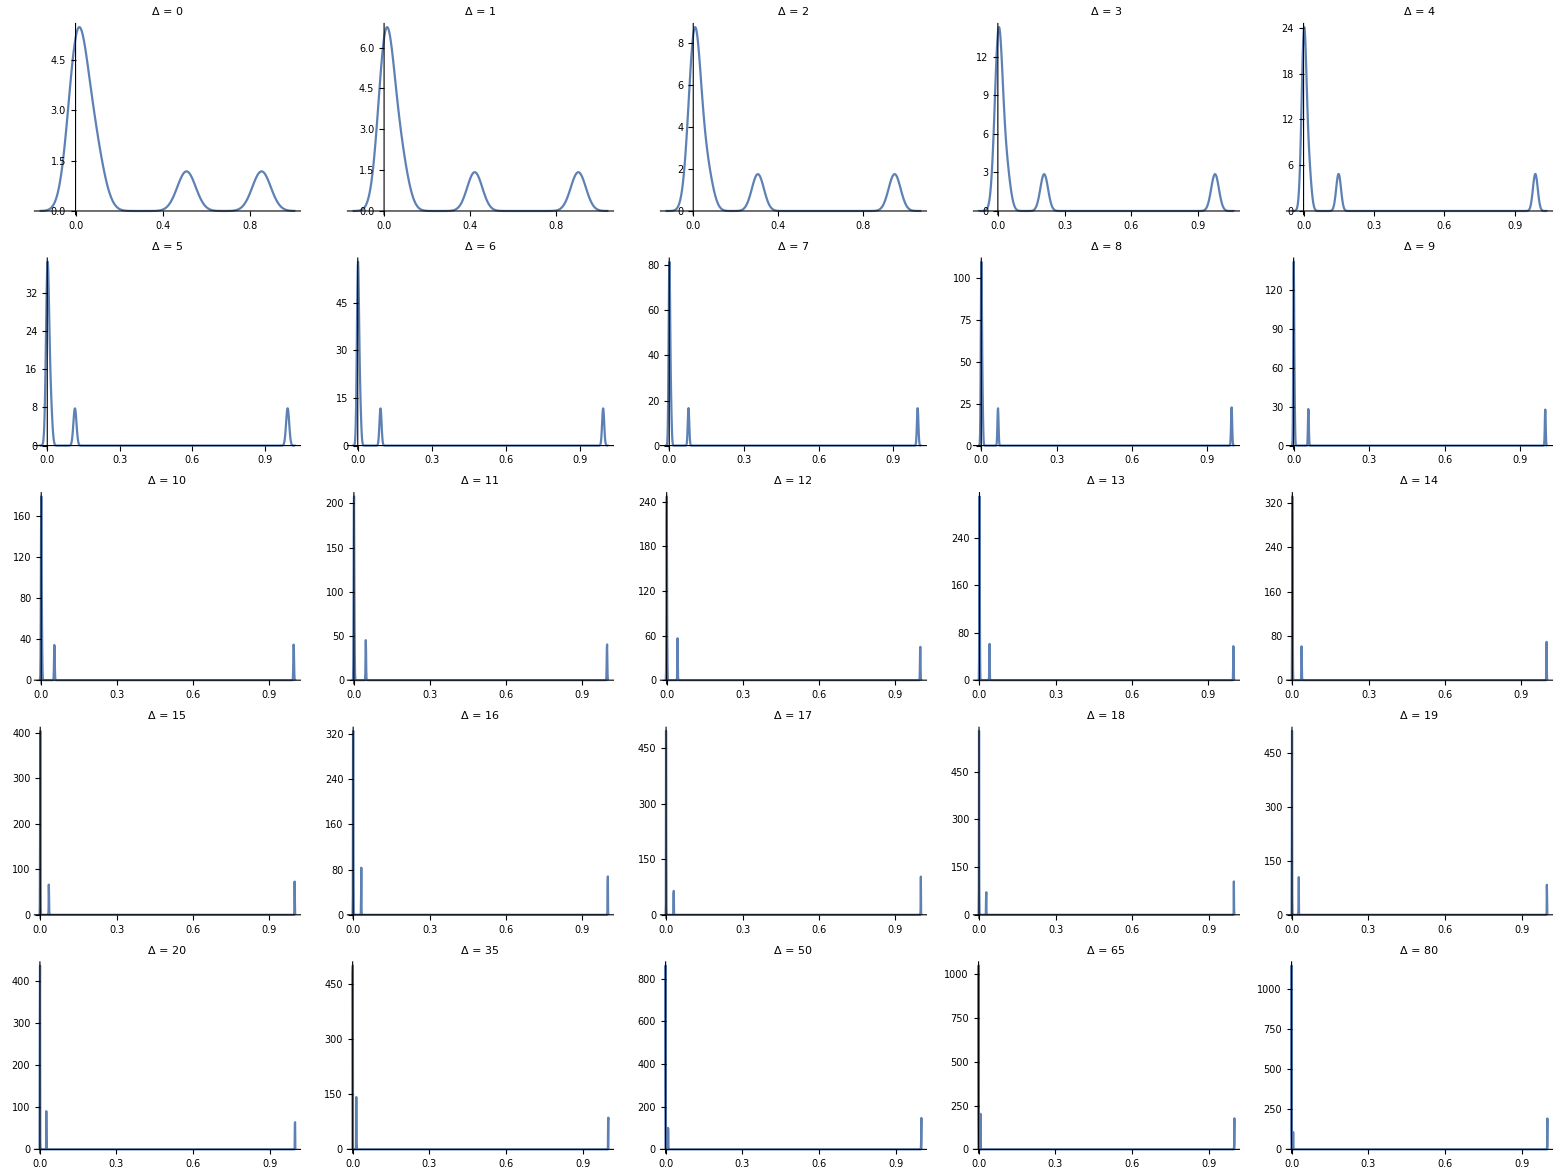

```mathematica
saveGSDN7 = Grid[{{SmoothHistogram[SDTabPlotD0[[6,2]],PlotLabel->"Δ = 0",PlotRange->All],SmoothHistogram[SDTabPlotD1[[6,2]],PlotLabel->"Δ = 1",PlotRange->All],SmoothHistogram[SDTabPlotD2[[6,2]],PlotLabel->"Δ = 2",PlotRange->All],SmoothHistogram[SDTabPlotD3[[6,2]],PlotLabel->"Δ = 3",PlotRange->All],SmoothHistogram[SDTabPlotD4[[6,2]],PlotLabel->"Δ = 4",PlotRange->All]},
{SmoothHistogram[SDTabPlotD5[[6,2]],PlotLabel->"Δ = 5",PlotRange->All],SmoothHistogram[SDTabPlotD6[[6,2]],PlotLabel->"Δ = 6",PlotRange->All],SmoothHistogram[SDTabPlotD7[[6,2]],PlotLabel->"Δ = 7",PlotRange->All],SmoothHistogram[SDTabPlotD8[[6,2]],PlotLabel->"Δ = 8",PlotRange->All],SmoothHistogram[SDTabPlotD9[[6,2]],PlotLabel->"Δ = 9",PlotRange->All]},{SmoothHistogram[SDTabPlotD10[[6,2]],PlotLabel->"Δ = 10",PlotRange->All],SmoothHistogram[SDTabPlotD11[[6,2]],PlotLabel->"Δ = 11",PlotRange->All],SmoothHistogram[SDTabPlotD12[[6,2]],PlotLabel->"Δ = 12",PlotRange->All],SmoothHistogram[SDTabPlotD13[[6,2]],PlotLabel->"Δ = 13",PlotRange->All],SmoothHistogram[SDTabPlotD14[[6,2]],PlotLabel->"Δ = 14",PlotRange->All]},
{SmoothHistogram[SDTabPlotD15[[6,2]],PlotLabel->"Δ = 15",PlotRange->All],SmoothHistogram[SDTabPlotD16[[6,2]],PlotLabel->"Δ = 16",PlotRange->All],SmoothHistogram[SDTabPlotD17[[6,2]],PlotLabel->"Δ = 17",PlotRange->All],SmoothHistogram[SDTabPlotD18[[6,2]],PlotLabel->"Δ = 18",PlotRange->All],SmoothHistogram[SDTabPlotD19[[6,2]],PlotLabel->"Δ = 19",PlotRange->All]},{SmoothHistogram[SDTabPlotD20[[6,2]],PlotLabel->"Δ = 20",PlotRange->All],SmoothHistogram[SDTabPlotD35[[6,2]],PlotLabel->"Δ = 35",PlotRange->All],SmoothHistogram[SDTabPlotD50[[6,2]],PlotLabel->"Δ = 50",PlotRange->All],SmoothHistogram[SDTabPlotD65[[6,2]],PlotLabel->"Δ = 65",PlotRange->All],SmoothHistogram[SDTabPlotD80[[6,2]],PlotLabel->"Δ = 80",PlotRange->All]}},Spacings->{0.5,0.5}]
```

#### N=8 Smooth Histogram

```mathematica
saveGSDN8 = Grid[{{SmoothHistogram[SDTabPlotD0[[7,2]],PlotLabel->"Δ = 0",PlotRange->All],SmoothHistogram[SDTabPlotD1[[7,2]],PlotLabel->"Δ = 1",PlotRange->All],SmoothHistogram[SDTabPlotD2[[7,2]],PlotLabel->"Δ = 2",PlotRange->All],SmoothHistogram[SDTabPlotD3[[7,2]],PlotLabel->"Δ = 3",PlotRange->All],SmoothHistogram[SDTabPlotD4[[7,2]],PlotLabel->"Δ = 4",PlotRange->All]},
{SmoothHistogram[SDTabPlotD5[[7,2]],PlotLabel->"Δ = 5",PlotRange->All],SmoothHistogram[SDTabPlotD6[[7,2]],PlotLabel->"Δ = 6",PlotRange->All],SmoothHistogram[SDTabPlotD7[[7,2]],PlotLabel->"Δ = 7",PlotRange->All],SmoothHistogram[SDTabPlotD8[[7,2]],PlotLabel->"Δ = 8",PlotRange->All],SmoothHistogram[SDTabPlotD9[[7,2]],PlotLabel->"Δ = 9",PlotRange->All]},{SmoothHistogram[SDTabPlotD10[[7,2]],PlotLabel->"Δ = 10",PlotRange->All],SmoothHistogram[SDTabPlotD11[[7,2]],PlotLabel->"Δ = 11",PlotRange->All],SmoothHistogram[SDTabPlotD12[[7,2]],PlotLabel->"Δ = 12",PlotRange->All],SmoothHistogram[SDTabPlotD13[[7,2]],PlotLabel->"Δ = 13",PlotRange->All],SmoothHistogram[SDTabPlotD14[[7,2]],PlotLabel->"Δ = 14",PlotRange->All]},
{SmoothHistogram[SDTabPlotD15[[7,2]],PlotLabel->"Δ = 15",PlotRange->All],SmoothHistogram[SDTabPlotD16[[7,2]],PlotLabel->"Δ = 16",PlotRange->All],SmoothHistogram[SDTabPlotD17[[7,2]],PlotLabel->"Δ = 17",PlotRange->All],SmoothHistogram[SDTabPlotD18[[7,2]],PlotLabel->"Δ = 18",PlotRange->All],SmoothHistogram[SDTabPlotD19[[7,2]],PlotLabel->"Δ = 19",PlotRange->All]},{SmoothHistogram[SDTabPlotD20[[7,2]],PlotLabel->"Δ = 20",PlotRange->All],SmoothHistogram[SDTabPlotD35[[7,2]],PlotLabel->"Δ = 35",PlotRange->All],SmoothHistogram[SDTabPlotD50[[7,2]],PlotLabel->"Δ = 50",PlotRange->All],SmoothHistogram[SDTabPlotD65[[7,2]],PlotLabel->"Δ = 65",PlotRange->All],SmoothHistogram[SDTabPlotD80[[7,2]],PlotLabel->"Δ = 80",PlotRange->All]}},Spacings->{0.5,0.5}]
```

-Graphics-

#### N=12 Smooth Histogram

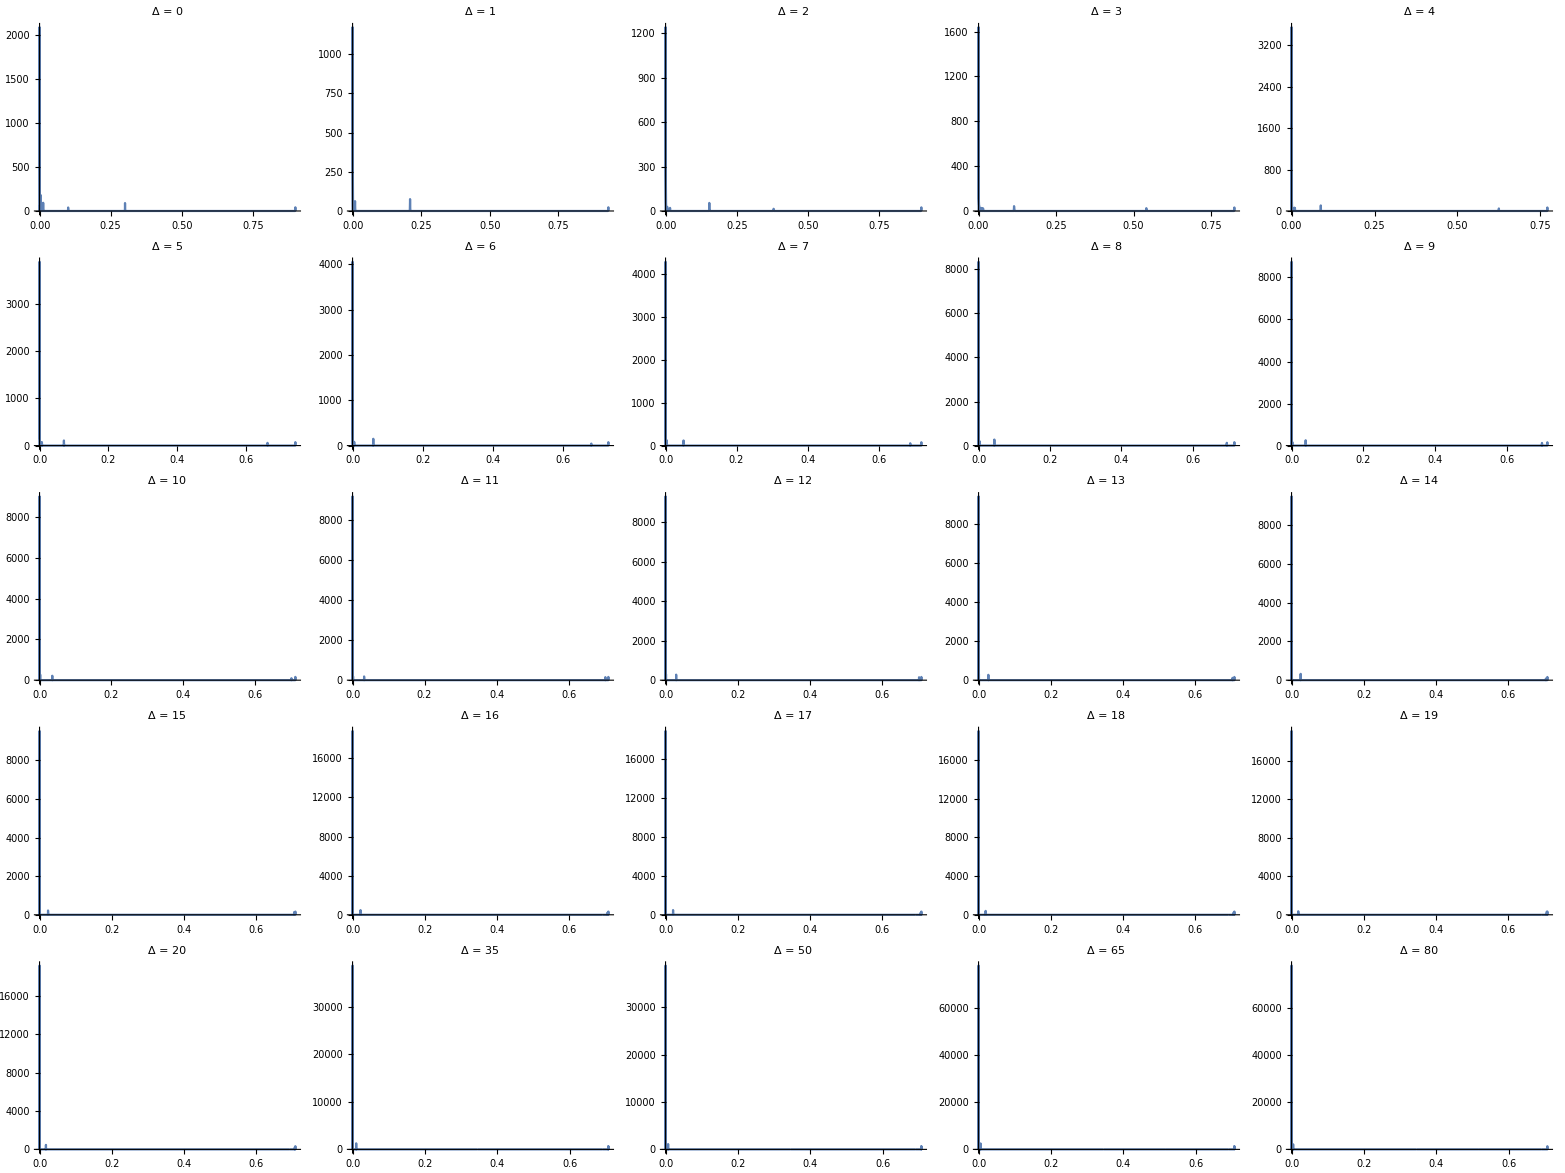

```mathematica
saveGSDN12 = Grid[{{SmoothHistogram[SDTabPlotD0[[11,2]],PlotLabel->"Δ = 0",PlotRange->All],SmoothHistogram[SDTabPlotD1[[11,2]],PlotLabel->"Δ = 1",PlotRange->All],SmoothHistogram[SDTabPlotD2[[11,2]],PlotLabel->"Δ = 2",PlotRange->All],SmoothHistogram[SDTabPlotD3[[11,2]],PlotLabel->"Δ = 3",PlotRange->All],SmoothHistogram[SDTabPlotD4[[11,2]],PlotLabel->"Δ = 4",PlotRange->All]},
{SmoothHistogram[SDTabPlotD5[[11,2]],PlotLabel->"Δ = 5",PlotRange->All],SmoothHistogram[SDTabPlotD6[[11,2]],PlotLabel->"Δ = 6",PlotRange->All],SmoothHistogram[SDTabPlotD7[[11,2]],PlotLabel->"Δ = 7",PlotRange->All],SmoothHistogram[SDTabPlotD8[[11,2]],PlotLabel->"Δ = 8",PlotRange->All],SmoothHistogram[SDTabPlotD9[[11,2]],PlotLabel->"Δ = 9",PlotRange->All]},{SmoothHistogram[SDTabPlotD10[[11,2]],PlotLabel->"Δ = 10",PlotRange->All],SmoothHistogram[SDTabPlotD11[[11,2]],PlotLabel->"Δ = 11",PlotRange->All],SmoothHistogram[SDTabPlotD12[[11,2]],PlotLabel->"Δ = 12",PlotRange->All],SmoothHistogram[SDTabPlotD13[[11,2]],PlotLabel->"Δ = 13",PlotRange->All],SmoothHistogram[SDTabPlotD14[[11,2]],PlotLabel->"Δ = 14",PlotRange->All]},
{SmoothHistogram[SDTabPlotD15[[11,2]],PlotLabel->"Δ = 15",PlotRange->All],SmoothHistogram[SDTabPlotD16[[11,2]],PlotLabel->"Δ = 16",PlotRange->All],SmoothHistogram[SDTabPlotD17[[11,2]],PlotLabel->"Δ = 17",PlotRange->All],SmoothHistogram[SDTabPlotD18[[11,2]],PlotLabel->"Δ = 18",PlotRange->All],SmoothHistogram[SDTabPlotD19[[11,2]],PlotLabel->"Δ = 19",PlotRange->All]},{SmoothHistogram[SDTabPlotD20[[11,2]],PlotLabel->"Δ = 20",PlotRange->All],SmoothHistogram[SDTabPlotD35[[11,2]],PlotLabel->"Δ = 35",PlotRange->All],SmoothHistogram[SDTabPlotD50[[11,2]],PlotLabel->"Δ = 50",PlotRange->All],SmoothHistogram[SDTabPlotD65[[11,2]],PlotLabel->"Δ = 65",PlotRange->All],SmoothHistogram[SDTabPlotD80[[11,2]],PlotLabel->"Δ = 80",PlotRange->All]}},Spacings->{0.5,0.5}]
```

### Schmidt Coefficients Value Distribution - Exponential Decay

#### Preliminary & Function

```mathematica
SDTabPlotDTab = {SDTabPlotD0,SDTabPlotD1,SDTabPlotD2,SDTabPlotD3,SDTabPlotD4,SDTabPlotD5,SDTabPlotD6,SDTabPlotD7,SDTabPlotD8,SDTabPlotD9,SDTabPlotD10,SDTabPlotD11,SDTabPlotD12,SDTabPlotD13,SDTabPlotD14,SDTabPlotD15,SDTabPlotD16,SDTabPlotD17,SDTabPlotD18,SDTabPlotD19,SDTabPlotD20,SDTabPlotD35,SDTabPlotD50,SDTabPlotD65,SDTabPlotD80,SDTabPlotD99};
DeltaList = Join[Table[i,{i,0,20}],{35,50,65,80,99}];
```

```mathematica
PlotAnimateHelper[Δ_]:=Module[{k,SDTabPlotinUse ,n,dim,SDTabPlotinUseMid ,SDTabPlotDAnimateTab ,i,lf,rg,SDTabPlotinUseMidLog,f,iPlot},
If[Δ≤20,k = Δ+1,If[Δ≠99,k = (Δ-20)/15+21,k=-1]];
SDTabPlotinUse = SDTabPlotDTab[[k]];
n = Length[SDTabPlotinUse];
SDTabPlotDAnimateTab = Table[0,n];
For [i =1,i≤ n,i++,
dim  = 2^Floor[(i+1)/2];
lf= Ceiling[1/6dim];
rg=Ceiling[ 5/6 dim];
SDTabPlotinUseMid = Table[{j,SDTabPlotinUse[[i,2]][[j]]},{j,lf,rg}];
SDTabPlotinUseMidLog = Table[{j,Log[SDTabPlotinUse[[i,2]][[j]]]},{j,lf,rg}];
f[x_]=Fit[SDTabPlotinUseMidLog ,{1,x},x];
iPlot = Show[ListLogPlot[SDTabPlotinUse[[i,2]],PlotRange->All,PlotLabel->StringJoin["Δ = ",ToString[Δ]," , N = ",ToString[i+1]],FrameLabel->{{"Log[S-Coefficients]",None},{None,None}},Frame->{{True,False},{True,False}}],Plot[f[x],{x,lf,rg},PlotStyle->Green,PlotRange->All]];
SDTabPlotDAnimateTab [[i]]=iPlot;
];
Return[SDTabPlotDAnimateTab];
]
PlotSlopeHelper[Δ_]:=Module[{k,SDTabPlotinUse ,n,dim,SDTabPlotDSlopeTab,i,lf,rg,SDTabPlotinUseMid,SDTabPlotinUseMidLog,f,islope},
If[Δ≤20,k = Δ+1,If[Δ≠99,k = (Δ-20)/15+21,k=-1]];
SDTabPlotinUse = SDTabPlotDTab[[k]];
n = Length[SDTabPlotinUse];
SDTabPlotDSlopeTab= Table[0,n];
For [i =1,i≤ n,i++,
dim  = 2^Floor[(i+1)/2];
lf= Ceiling[1/6 dim];
rg=Ceiling[ 5/6 dim];
SDTabPlotinUseMid = Table[{j,SDTabPlotinUse[[i,2]][[j]]},{j,lf,rg}];
SDTabPlotinUseMidLog = Table[{j,Log[SDTabPlotinUse[[i,2]][[j]]]},{j,lf,rg}];
f[x_]=Fit[SDTabPlotinUseMidLog ,{1,x},x];
islope= D[f[x],x];
SDTabPlotDSlopeTab[[i]] = islope;
];
Return[SDTabPlotDSlopeTab];
]
```

#### SC Graph

```mathematica
P1 = PlotAnimateHelper[35];
```

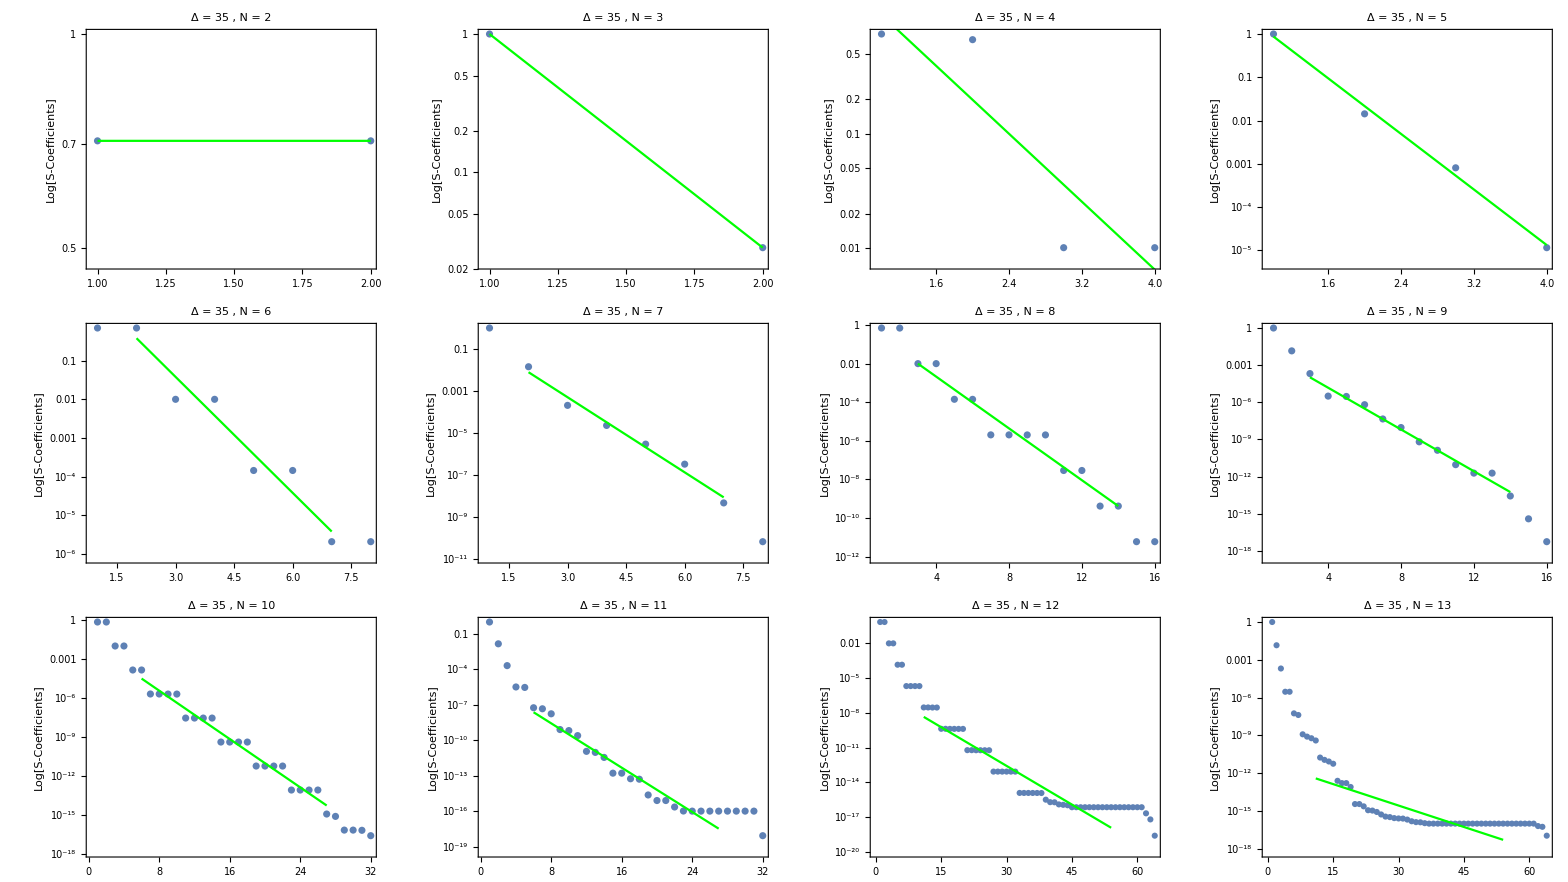

```mathematica
Grid[{Table[P1[[i]],{i,1,4}],Table[P1[[i]],{i,5,8}],Table[P1[[i]],{i,9,12}]},Spacings->{0.5, 0.5}]
```

#### SC Animation

```mathematica
SCTabPlotAnimateTab = Table[0,Length[DeltaList]];
For [d=1,d≤ Length[DeltaList],d++,SCTabPlotAnimateTab[[d]]=ListAnimate[PlotAnimateHelper[DeltaList[[d]]]]];
```

$Aborted

```mathematica
SCTabPlotAnimateTab[[10]]
```

#### SC Slope Evaluation

```mathematica
SCTabPlotSlopeTab = Table[0,Length[DeltaList]];
For [d=1,d≤ Length[DeltaList],d++,SCTabPlotSlopeTab[[d]]=ListPlot[Table[{i,PlotSlopeHelper[DeltaList[[d]]][[i-1]]},{i,2,13}],PlotLabel-> StringJoin["Δ = ",ToString[DeltaList[[d]]]]]];
```

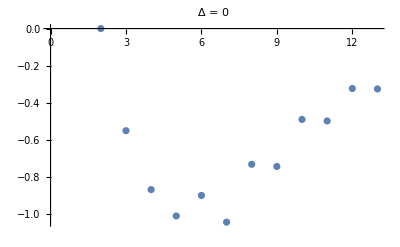
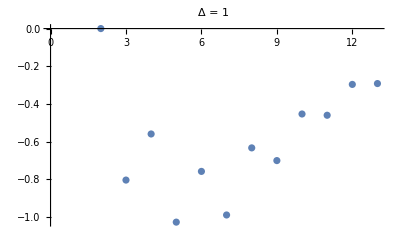
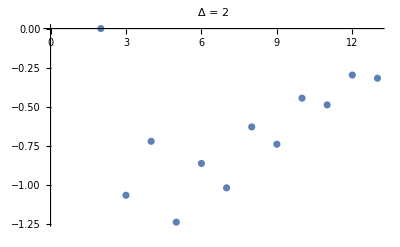
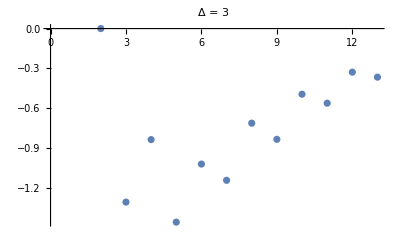
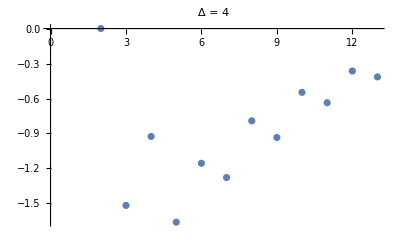
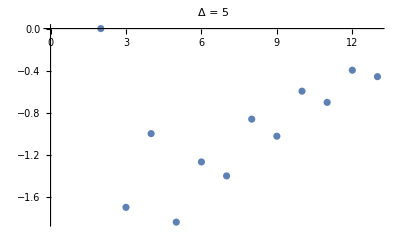
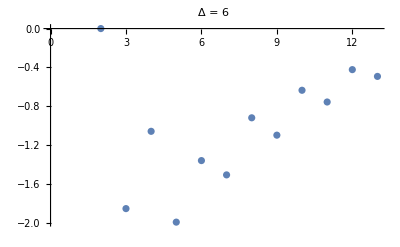
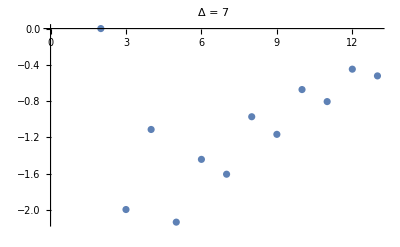

```mathematica
SCTabPlotSlopeTab
```

#### SC Slope Evaluation for Latex

```mathematica
PlotSlopeHelperLatex[Δ_]:= Module[{k,TabPredictN14even ,aeven,alogeven,TabPredictN14odd ,aodd,alogodd,lfN14,rgN14,TabPredictN14MidLog ,fN14,iPlot,plotHelper},
If[Δ≤20,k = Δ+1,If[Δ≠99,k = (Δ-20)/15+21,k=-1]];
TabPredictN14even = Table[{i,PlotSlopeHelper[Δ][[i-1]]},{i,6,13,2}];
aeven[x_]= Fit[TabPredictN14even,{1,x},x];
alogeven[x_]=Fit[TabPredictN14even,{1,Log[x]},x];

TabPredictN14odd = Table[{i,PlotSlopeHelper[Δ][[i-1]]},{i,5,13,2}];
aodd[x_]= Fit[TabPredictN14odd,{1,x},x];
alogodd[x_]=Fit[TabPredictN14odd,{1,Log[x]},x];

plotHelper = Show[ListPlot[Table[{i,PlotSlopeHelper[Δ][[i-1]]},{i,2,13}],PlotStyle->{Thick,Black}],
Plot[alogeven[x],{x,6,13},PlotStyle->Red],Plot[alogodd[x],{x,5,13}],PlotLabel-> StringJoin["Δ = ",ToString[Δ]],
FrameLabel->{{"Slope of Log[SCoeff.]",None},{"# Qubits",None}},Frame->{{True,False},{True,False}},PlotRange->All];

Return[plotHelper]
]
```

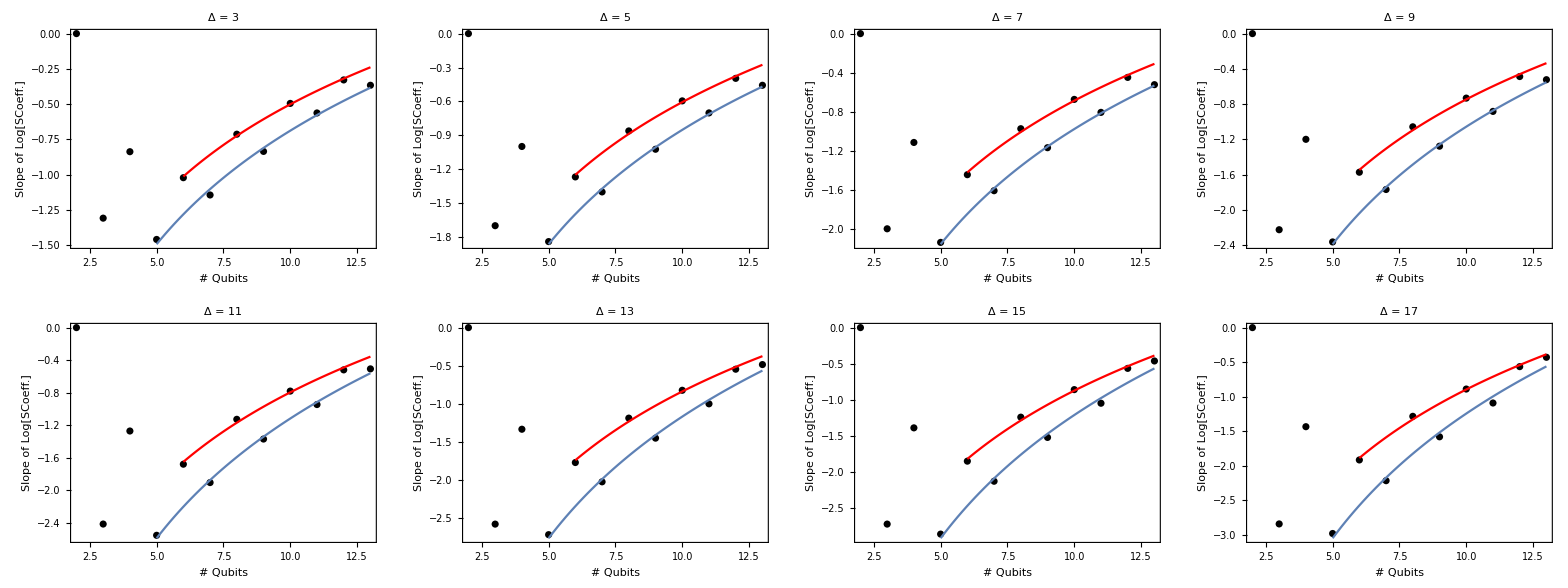

```mathematica
SCTabPlotSlopeTab = Table[0,8];
For [d=3,d≤ 17,d=d+2,SCTabPlotSlopeTab[[(d-3)/2+1]]=PlotSlopeHelperLatex[d]];
Grid[{SCTabPlotSlopeTab[[1;;4]],SCTabPlotSlopeTab[[5;;8]]},Spacings->{0.5,0.5}]
```

### Schmidt Coefficients Exponential Decay - Prediction

#### Test

{0,-1.06792,-0.722289,-1.24024,-0.864143,-1.02053,-0.630041,-0.741229,-0.446003,-0.488918,-0.297747,-0.318241}

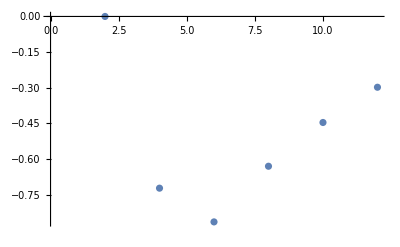

```mathematica
PlotSlopeHelper[DeltaList[[3]]]
ListPlot[Table[{i,PlotSlopeHelper[DeltaList[[3]]][[i-1]]},{i,2,13,2}]]
```

```mathematica
TabPredictD2 = Table[{i,PlotSlopeHelper[DeltaList[[3]]][[i-1]]},{i,6,13,2}]
a[x_]=Fit[TabPredictD2 ,{1,x},x]
ae[x_]=Fit[TabPredictD2 ,{1,Log[x]},x]
```

{{6,-0.864143},{8,-0.630041},{10,-0.446003},{12,-0.297747}}

-1.40694+0.0941613 x

-2.3298+0.81782 Log[x]

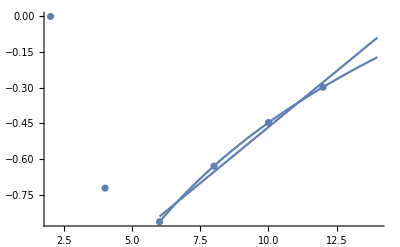

```mathematica
Show[ListPlot[Table[{i,PlotSlopeHelper[DeltaList[[3]]][[i-1]]},{i,2,13,2}]],Plot[-1.4069357560512827+0.09416134115760222 x,{x,6,14}],Plot[-2.3297976130670115+0.817820415988185 Log[x],{x,6,14}],PlotRange-> All]
```

```mathematica
a[14]
```

-0.088677

```mathematica
ae[14]
```

-0.171523

```mathematica
SDTabPlotD2N14={14,{0.7006013639764447,0.7006013639764131,0.09034740620699559,0.09034740620699247,0.030325094557103586,0.030325094557101622,0.00839195154948333,0.00839195154948256,0.0020858037799066365,0.0020858037799065237,0.0007496365251901396,0.0007496365251898611,0.00027778732365967023,0.0002777873236596374,0.00020736345889924324,0.00020736345889918453,6.81461948626128*10^-05,6.814619486261078*10^-05,2.8691380732369995*10^-05,2.8691380732311082*10^-05,1.829904456052227*10^-05,1.8299044560508182*10^-05,1.1024787766515584*10^-05,1.1024787766468748*10^-05,8.105412524367228*10^-06,8.105412524360584*10^-06,7.869848472671446*10^-06,7.869848472663216*10^-06,4.145938789083149*10^-06,4.145938789030601*10^-06,2.2844547904797358*10^-06,2.2844547904476273*10^-06,1.4655105892411464*10^-06,1.4655105892318047*10^-06,1.153618594791901*10^-06,1.1536185947667888*10^-06,6.142795820485568*10^-07,6.142795819292797*10^-07,3.690926089423126*10^-07,3.69092608936264*10^-07,1.646372591951567*10^-07,1.6463725903673556*10^-07,1.6079728712113584*10^-07,1.6079728710641398*10^-07,9.942189421849709*10^-08,9.942189420813263*10^-08,4.596619618314776*10^-08,4.596619617132045*10^-08,4.416712949277437*10^-08,4.4167129477249834*10^-08,3.470299909352995*10^-08,3.4702999078654334*10^-08,1.296521372981933*10^-08,1.2965213721057855*10^-08,7.696710099644151*10^-09,7.696710092432215*10^-09,4.474414754050149*10^-09,4.474414358608698*10^-09,3.4867026211639528*10^-09,3.4867026087868588*10^-09,3.472578069187881*10^-09,3.4725780690933454*10^-09,2.071981527684439*10^-09,2.071981476390473*10^-09,1.3137720304682209*10^-09,1.3137720266293296*10^-09,9.985582402336423*10^-10,9.985582401603888*10^-10,9.68330205352877*10^-10,9.683301990688413*10^-10,9.345028568257314*10^-10,9.345028088215846*10^-10,3.547666040947858*10^-10,3.5476660246768486*10^-10,2.8622668860989237*10^-10,2.8622667981860327*10^-10,2.4329855465243406*10^-10,2.4329854387061863*10^-10,1.171679420643987*10^-10,1.1716793674794306*10^-10,7.703177806790614*10^-11,7.703176916053391*10^-11,6.656070705082367*10^-11,6.656070632431924*10^-11,6.319172590714442*10^-11,6.319172395097727*10^-11,3.282652791961002*10^-11,3.2826523187537265*10^-11,3.1244453402705254*10^-11,3.1244451322532866*10^-11,2.0647168353323734*10^-11,2.0647094426630822*10^-11,1.8146794281858033*10^-11,1.8146794102368736*10^-11,9.936350514044982*10^-12,9.936345475611255*10^-12,8.788137531941358*10^-12,8.788136910395198*10^-12,4.870076189573372*10^-12,4.870040331378048*10^-12,2.9085963921641107*10^-12,2.9085715170413937*10^-12,2.7152625093692003*10^-12,2.715261905940757*10^-12,2.3534605097419115*10^-12,2.3534344164060746*10^-12,1.3050718049086075*10^-12,1.3050320778044548*10^-12,7.876985536960355*10^-13,7.876936072942627*10^-13,7.286782753185313*10^-13,7.286779981960783*10^-13,6.305731363747694*10^-13,6.305720086407936*10^-13,2.1228675583174725*10^-13,2.1225892262471478*10^-13,2.1127816024845747*10^-13,2.1125577505912815*10^-13,5.692948175720603*10^-14,5.68976959722824*10^-14,5.6841835265810726*10^-14,5.683624755849249*10^-14,1.5357785558335925*10^-14,1.5260333882539623*10^-14,4.090364358452291*10^-15,4.08911196825901*10^-15,1.0957333504706296*10^-15,1.0956765772002083*10^-15}};
```

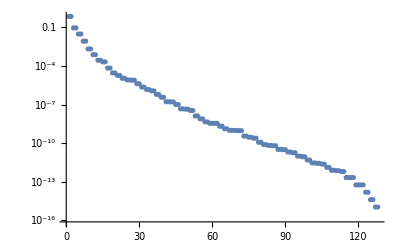

```mathematica
ListLogPlot[SDTabPlotD2N14[[2]]]
```

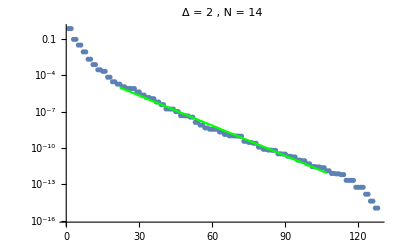

```mathematica
lfN14= Ceiling[1/6 2^7];
rgN14=Ceiling[ 5/6 2^7];
SDTabPlotinUseMidN14 = Table[{j,SDTabPlotD2N14[[2,j]]},{j,lfN14,rgN14}];
SDTabPlotinUseMidLogN14 = Table[{j,Log[SDTabPlotD2N14[[2,j]]]},{j,lfN14,rgN14}];
fN14[x_]=Fit[SDTabPlotinUseMidLogN14 ,{1,x},x];
iPlot = Show[ListLogPlot[SDTabPlotD2N14[[2]],PlotRange->All,PlotLabel->StringJoin["Δ = ",ToString[2]," , N = ",ToString[14]]],Plot[fN14[x],{x,lfN14,rgN14},PlotStyle->Green,PlotRange->All]];
iPlot
```

```mathematica
D[fN14[x],x]
```

-0.190701

#### Data N = 14

```mathematica
SDTabPlotD0N14={14,{0.7011034938035572,0.7011034938035521,0.0648534475305359,0.06485344753053532,0.06485344753053522,0.06485344753053467,0.005999071026986395,0.005999071026986395,0.0017119960152251743,0.0017119960152251652,0.0017119960152251496,0.0017119960152251067,0.00015836298738678925,0.00015836298738662122,0.0001583629873865997,0.0001583629873865677,0.00015836298738656745,0.00015836298738656547,0.00015836298738656365,0.0001583629873865338,1.4648886767842424*10^-05,1.4648886767815624*10^-05,1.4648886767815237*10^-05,1.4648886767800956*10^-05,9.588945313193919*10^-06,9.588945313084842*10^-06,9.5889453130754*10^-06,9.588945313039239*10^-06,4.180453217018468*10^-06,4.180453216959245*10^-06,8.869962384363333*10^-07,8.869962384061219*10^-07,8.869962384032812*10^-07,8.86996238402144*10^-07,8.869962383945691*10^-07,8.869962383937942*10^-07,8.869962383475003*10^-07,8.869962383011048*10^-07,3.8670011741741793*10^-07,3.867001174117011*10^-07,3.867001174057985*10^-07,3.867001174025462*10^-07,8.204889085974529*10^-08,8.204889083998135*10^-08,8.20488908116568*10^-08,8.204889080818444*10^-08,3.57705188981309*10^-08,3.5770518886035044*10^-08,2.341485442824422*10^-08,2.3414854388056863*10^-08,2.3414854316580455*10^-08,2.3414854313652897*10^-08,2.3414854312877663*10^-08,2.341485430246029*10^-08,2.341485429151424*10^-08,2.341485419102719*10^-08,2.165919950972104*10^-09,2.165919947604169*10^-09,2.1659199363198772*10^-09,2.1659199319193847*10^-09,2.1659199281159917*10^-09,2.165919925445007*10^-09,2.165919923983244*10^-09,2.1659199235306777*10^-09,2.165919923168605*10^-09,2.165919922720672*10^-09,2.165919922588387*10^-09,2.165919921606118*10^-09,2.1659199192039317*10^-09,2.1659198891135193*10^-09,2.1659198639628235*10^-09,2.1659198511554248*10^-09,2.0035193778060968*10^-10,2.00351914713511*10^-10,2.0035184146625065*10^-10,2.0035183878992776*10^-10,2.0035183861683212*10^-10,2.0035181497891005*10^-10,2.0035181436576837*10^-10,2.0035181162893973*10^-10,1.3114735410318302*10^-10,1.3114733967004*10^-10,5.717585276203083*10^-11,5.7175778885698454*10^-11,5.717577725601052*10^-11,5.717574647556006*10^-11,1.2131416058041382*10^-11,1.2131396049990459*10^-11,1.2131388337985847*10^-11,1.2131381400988654*10^-11,5.2889010784022836*10^-12,5.288877180589984*10^-12,5.2888725756549684*10^-12,5.288871453865741*10^-12,5.2888690584090334*10^-12,5.288831392122417*10^-12,5.2888299951003986*10^-12,5.288820465582406*10^-12,1.1221313671087496*10^-12,1.1220925877562832*10^-12,4.892368619721276*10^-13,4.892311110653042*10^-13,4.892285618070222*10^-13,4.892267548295559*10^-13,3.202478983374446*10^-13,3.2024339939512064*10^-13,3.2024268276502026*10^-13,3.202349101993019*10^-13,2.973707132795496*10^-14,2.963660684922085*10^-14,2.9630450873549696*10^-14,2.962410058218992*10^-14,2.962309256285058*10^-14,2.96216550364422*10^-14,2.961808474442619*10^-14,2.9541095403050296*10^-14,2.7657652939893943*10^-15,2.753064669974214*10^-15,2.746851687644701*10^-15,2.727416841717728*10^-15,8.658317702999723*10^-16,6.820763230848947*10^-16,2.876726603886499*10^-16,2.606896504639983*10^-16,1.456856087109527*10^-16,8.659802382651458*10^-17,6.959977722564789*10^-17,4.595953001043703*10^-17}};
SDTabPlotD1N14={14,{0.7030586967583544,0.703058696758354,0.06869412278686764,0.06869412278686744,0.022200230996455295,0.022200230996455277,0.022200230996455274,0.02220023099645518,0.0017687986777514297,0.0017687986777513798,0.0005999502229459487,0.0005999502229459453,0.0005999502229459435,0.0005999502229459294,0.00018045801986181368,0.00018045801986175123,4.424694051639979*10^-05,4.4246940516385695*10^-05,4.424694051636808*10^-05,4.42469405163604*10^-05,2.4071850975755872*10^-05,2.407185097572379*10^-05,9.815899234774527*10^-06,9.81589923476981*10^-06,8.28689288153074*10^-06,8.28689288153065*10^-06,8.286892881512069*10^-06,8.286892881505552*10^-06,4.005671694813982*10^-06,4.0056716947599915*10^-06,4.005671694759762*10^-06,4.005671694748124*10^-06,4.005671694746649*10^-06,4.00567169474444*10^-06,3.31556693679279*10^-06,3.3155669367890785*10^-06,3.3155669367689776*10^-06,3.3155669367629043*10^-06,9.928258804679234*10^-07,9.928258804631327*10^-07,2.528728025775739*10^-07,2.52872802573826*10^-07,2.528728025706459*10^-07,2.528728025682951*10^-07,1.3670280407086834*10^-07,1.3670280405113345*10^-07,4.7382749572485605*10^-08,4.738274956818487*10^-08,4.738274954932947*10^-08,4.738274954233881*10^-08,2.6867856968596154*10^-08,2.686785695787179*10^-08,2.295053940320693*10^-08,2.2950539393970992*10^-08,2.2950539355094572*10^-08,2.295053935469538*10^-08,2.2950539354146044*10^-08,2.2950539351816978*10^-08,5.5155198832946115*10^-09,5.515519865314903*10^-09,5.515519860224106*10^-09,5.5155198597460764*10^-09,3.361786181099963*10^-09,3.361786178781811*10^-09,2.280534305230287*10^-09,2.28053430517593*10^-09,1.1042438542927593*10^-09,1.1042438429022315*10^-09,1.1042438418889317*10^-09,1.1042438316444235*10^-09,8.535359826939153*10^-10,8.535359797625867*10^-10,8.535359785869928*10^-10,8.535359771996477*10^-10,5.216415946252719*10^-10,5.216415943697224*10^-10,5.21641587828854*10^-10,5.216415851178382*10^-10,5.216415669343003*10^-10,5.216415577405269*10^-10,2.054679861817378*10^-10,2.0546798215213922*10^-10,6.956966140914204*10^-11,6.956964156650451*10^-11,6.956963884256661*10^-11,6.956961657040696*10^-11,5.475832812031641*10^-11,5.475832681254173*10^-11,5.4758324266101614*10^-11,5.475832028175148*10^-11,3.3919151370369685*10^-11,3.391911058370142*10^-11,3.16110492903832*10^-11,3.161101087578931*10^-11,3.161100993079831*10^-11,3.161100309281546*10^-11,3.1611001926121415*10^-11,3.161100172252343*10^-11,9.706406708513932*10^-12,9.706374524180146*10^-12,9.706359469039016*10^-12,9.706359044881828*10^-12,6.5518160240209275*10^-12,6.551794122522377*10^-12,4.336565829660248*10^-12,4.33654582430956*10^-12,4.336545479427625*10^-12,4.336542969945366*10^-12,4.336540895180743*10^-12,4.336532195979971*10^-12,2.4905511900604023*10^-12,2.4904378334747546*10^-12,2.490427903326939*10^-12,2.490390261379609*10^-12,1.251150926279066*10^-12,1.2511486491703251*10^-12,1.2511232679112513*10^-12,1.2511090872421715*10^-12,1.251081039876892*10^-12,1.2510787359247325*10^-12,7.403588684688067*10^-13,7.400662559552059*10^-13,7.400542341640964*10^-13,7.400541511654616*10^-13,7.400539030453793*10^-13,7.400447035438505*10^-13,7.400145916508486*10^-13,7.399444107375064*10^-13}};
SDTabPlotD2N14={14,{0.70060136397643,0.7006013639764269,0.0903474062069945,0.09034740620699366,0.030325094557102732,0.03032509455710257,0.008391951549483027,0.008391951549482876,0.0020858037799065606,0.0020858037799065007,0.0007496365251901077,0.0007496365251900552,0.00027778732365964763,0.00027778732365963586,0.0002073634588992296,0.00020736345889917765,6.814619486262405*10^-05,6.814619486260375*10^-05,2.8691380732406153*10^-05,2.8691380732316266*10^-05,1.8299044560508212*10^-05,1.829904456050699*10^-05,1.1024787766495517*10^-05,1.1024787766467874*10^-05,8.105412524359027*10^-06,8.105412524351467*10^-06,7.86984847268278*10^-06,7.869848472662694*10^-06,4.145938789074419*10^-06,4.1459387890574945*10^-06,2.2844547904788515*10^-06,2.2844547904601096*10^-06,1.4655105892486715*10^-06,1.4655105892439065*10^-06,1.1536185948042836*10^-06,1.1536185947900325*10^-06,6.14279581994843*10^-07,6.142795819292124*10^-07,3.6909260894739694*10^-07,3.6909260894338037*10^-07,1.6463725919515002*10^-07,1.6463725911537296*10^-07,1.607972871182383*10^-07,1.6079728709536002*10^-07,9.942189421968365*10^-08,9.942189421825433*10^-08,4.59661961748309*10^-08,4.596619616373074*10^-08,4.4167129492285774*10^-08,4.416712946900875*10^-08,3.4702999090978697*10^-08,3.4702999070639874*10^-08,1.2965213726206125*10^-08,1.2965213722388318*10^-08,7.696710189900154*10^-09,7.696709998483414*10^-09,4.474414567669479*10^-09,4.474414561718359*10^-09,3.4867026210686115*10^-09,3.4867025822724296*10^-09,3.4725780862155515*10^-09,3.472578031865495*10^-09,2.071981500469109*10^-09,2.0719814990816713*10^-09,1.3137720308705535*10^-09,1.3137720308114812*10^-09,9.985582438412412*10^-10,9.985582427356146*10^-10,9.683302053114311*10^-10,9.683302040817732*10^-10,9.34502923599888*10^-10,9.345028568259828*10^-10,3.547666025482273*10^-10,3.5476660235398103*10^-10,2.862266855452549*10^-10,2.8622668011138504*10^-10,2.432985586196122*10^-10,2.4329855014036276*10^-10,1.171679403355533*10^-10,1.1716793770037443*10^-10,7.703177614294969*10^-11,7.703177042394836*10^-11,6.656070753747582*10^-11,6.656070643712577*10^-11,6.31917257973371*10^-11,6.319172465692*10^-11,3.2826527121716696*10^-11,3.282652287774695*10^-11,3.124445221555419*10^-11,3.124445156507196*10^-11,2.0647095141264165*10^-11,2.0647094426658794*10^-11,1.8146797452950978*10^-11,1.8146794127602514*10^-11,9.936350131560071*10^-12,9.936345690036906*10^-12,8.78813945665086*10^-12,8.78813776597873*10^-12,4.870068509709033*10^-12,4.870040325739426*10^-12,2.9086110304786763*10^-12,2.9085967627078482*10^-12,2.7152636212815787*10^-12,2.7152622257020978*10^-12,2.353441292343363*10^-12,2.3534344367999816*10^-12,1.30507180447074*10^-12,1.305060129083257*10^-12,7.876939115815687*10^-13,7.876879471468497*10^-13,7.286783533006418*10^-13,7.286781085632316*10^-13,6.305731365916504*10^-13,6.30562236902546*10^-13,2.122597416240698*10^-13,2.1225892646167596*10^-13,2.1129285322443627*10^-13,2.1127808036814985*10^-13,5.696510507481287*10^-14,5.692948337984279*10^-14,5.689769547284499*10^-14,5.689655486219193*10^-14,1.52603338798234*10^-14,1.5222182998757006*10^-14,4.089111994464253*10^-15,4.088840016152451*10^-15,1.095692789529042*10^-15,1.0956764856503317*10^-15}};
SDTabPlotD3N14={14,{0.6994366242384707,0.6994366242384239,0.10208901680629218,0.1020890168062856,0.018774660808932774,0.018774660808931514,0.003228620601606978,0.0032286206016066913,0.0017694332952465977,0.0017694332952465752,0.0003540167627363674,0.0003540167627362195,0.0002595656970940891,0.0002595656970940753,6.091540173572262*10^-05,6.091540173566823*10^-05,4.3623863691965*10^-05,4.362386369196326*10^-05,9.400371395793278*10^-06,9.400371395778087*10^-06,8.755716911128314*10^-06,8.755716911112467*10^-06,7.479669423652793*10^-06,7.479669423650769*10^-06,1.9395221171339137*10^-06,1.939522116961336*10^-06,1.6124098700870526*10^-06,1.6124098700364144*10^-06,1.6100516290984742*10^-06,1.6100516290974967*10^-06,1.2903853498028797*10^-06,1.2903853497972264*10^-06,3.340893464772618*10^-07,3.3408934645916603*10^-07,2.7742041056907597*10^-07,2.774204105493204*10^-07,2.1879300364932485*10^-07,2.1879300364284346*10^-07,5.143847776314739*10^-08,5.143847776203186*10^-08,4.760382264473502*10^-08,4.7603822626857304*10^-08,3.7524481287100345*10^-08,3.752448127983369*10^-08,2.2588743623678018*10^-08,2.2588743597799857*10^-08,8.893027574056151*10^-09,8.893027535709603*10^-09,8.849817937661652*10^-09,8.849817790460696*10^-09,8.167555192187658*10^-09,8.167555063410016*10^-09,3.6299324925266888*10^-09,3.629932451639716*10^-09,3.2932983468196164*10^-09,3.293297461047494*10^-09,1.5312269594830109*10^-09,1.5312269380560667*10^-09,9.212332405610797*10^-10,9.212332308316521*10^-10,6.209621079089042*10^-10,6.209621072942312*10^-10,5.696998113096011*10^-10,5.696998102083701*10^-10,2.6278206789874004*10^-10,2.627820324240251*10^-10,1.5998297441680263*10^-10,1.599829349056772*10^-10,1.5886029722219148*10^-10,1.5886029058169621*10^-10,9.775649493102673*10^-11,9.775649447076879*10^-11,8.854038181580659*10^-11,8.854037933211066*10^-11,4.508660356994757*10^-11,4.5086480420487913*10^-11,2.7593525075689034*10^-11,2.7593505519288937*10^-11,2.4007828726287483*10^-11,2.4007827986516332*10^-11,1.5174824978092287*10^-11,1.5174822545386324*10^-11,1.5146242046792815*10^-11,1.5146241189124755*10^-11,4.735901851461415*10^-12,4.735834403667357*10^-12,4.156797012033354*10^-12,4.156794822717614*10^-12,4.1174229344722654*10^-12,4.117422457730924*10^-12,2.5958707255382566*10^-12,2.5958695479889596*10^-12,8.1256037396857*10^-13,8.124672745530479*10^-13,7.225877344782383*10^-13,7.225852605679236*10^-13,7.161217647300107*10^-13,7.16121622079172*10^-13,4.4534189383163514*10^-13,4.4533637151438437*10^-13,1.2456300223524762*10^-13,1.2455566422306735*10^-13,1.240556263395009*10^-13,1.240215036793272*10^-13,1.2292320979597178*10^-13,1.229231048238448*10^-13,7.640839273054263*10^-14,7.640418431267948*10^-14,2.137960416597665*10^-14,2.13776575582747*10^-14,2.12788818217979*10^-14,2.127126774282304*10^-14,2.109093258048103*10^-14,2.1090582640571625*10^-14,3.6692280724613086*10^-15,3.667997880300332*10^-15,3.652446837933022*10^-15,3.648144024657054*10^-15,6.544559488731337*10^-16,6.299261632567252*10^-16,6.295514493370974*10^-16,6.167282681355791*10^-16,1.3063077619515508*10^-16,6.90665276657693*10^-17,6.90665276657693*10^-17,6.536282292743336*10^-17,3.6516549795892544*10^-17,1.853465781820799*10^-17}};
SDTabPlotD4N14={14,{0.7017772814705162,0.7017772814698682,0.0859201338593661,0.08592013385928646,0.01109909354693494,0.011099093546924278,0.0014101632001017087,0.0014101632001004465,0.0010769066976625925,0.0010769066976613988,0.00014687273644456366,0.00014687273644453124,0.00013194820405860514,0.00013194820405845877,1.866324097599085*10^-05,1.8663240975926676*10^-05,1.667740548599628*10^-05,1.667740548598222*10^-05,4.971477037840041*10^-06,4.971477036732416*10^-06,2.312960871332804*10^-06,2.312960871330321*10^-06,2.1181330978641237*10^-06,2.1181330978626325*10^-06,7.471337939836097*10^-07,7.471337938071028*10^-07,6.091934984460974*10^-07,6.091934984409393*10^-07,2.942119248027622*10^-07,2.942119247596812*10^-07,2.9385135866479773*10^-07,2.938513586616519*10^-07,9.495400651409249*10^-08,9.49540064544464*10^-08,7.716925025671479*10^-08,7.716925025356759*10^-08,3.737913051055042*10^-08,3.737913050454407*10^-08,1.1783109273176556*10^-08,1.1783109209937343*10^-08,9.801336395610506*10^-09,9.801336393259543*10^-09,7.655163843442016*10^-09,7.655163819164283*10^-09,4.747885228072777*10^-09,4.74788522050884*10^-09,1.4998091094447591*10^-09,1.4998090780892496*10^-09,1.4969972069616972*10^-09,1.4969972031663688*10^-09,9.488890783312951*10^-10,9.488890748288701*10^-10,9.364549786668325*10^-10,9.36454976720105*10^-10,6.030607321525707*10^-10,6.030607251550777*10^-10,1.9056548041155851*10^-10,1.9056546392859104*10^-10,1.5270066366831675*10^-10,1.5270066326491997*10^-10,1.2038110663113215*10^-10,1.2038110321046403*10^-10,1.1904486836611229*10^-10,1.1904484090398287*10^-10,2.4205852909602336*10^-11,2.420584649293709*10^-11,1.9471324091359837*10^-11,1.9471209616908007*10^-11,1.940791397156519*10^-11,1.940791190206577*10^-11,1.5120500995033475*10^-11,1.5120500270201484*10^-11,1.4653056315092824*10^-11,1.465305303965499*10^-11,3.0745708262414357*10^-12,3.0745482077132547*10^-12,2.474736113397549*10^-12,2.4746388837235164*10^-12,2.4004038584156818*10^-12,2.400358521304695*10^-12,1.8609545997207606*10^-12,1.8609512363843324*10^-12,1.8602337122634156*10^-12,1.8602328324175467*10^-12,3.143760935462552*10^-13,3.143441659018627*10^-13,3.053991559721475*10^-13,3.053920322488708*10^-13,3.048703481897595*10^-13,3.0486451216100277*10^-13,2.362517154922353*10^-13,2.362510185624104*10^-13,3.9926979763543495*10^-14,3.989300704645932*10^-14,3.8946985123253635*10^-14,3.894457530575474*10^-14,3.8802609690049545*10^-14,3.880227330356215*10^-14,3.001011494593902*10^-14,3.000756599238286*10^-14,5.0410815480947*10^-15,4.948655586654142*10^-15,4.9471139964879164*10^-15,4.946789754512941*10^-15,4.92887029063831*10^-15,4.928756790187107*10^-15,3.819865192942834*10^-15,3.8114451930985984*10^-15,6.299160620625247*10^-16,6.284909174801901*10^-16,6.281549022470937*10^-16,6.281102467314246*10^-16,6.257236450912061*10^-16,5.651095886408066*10^-16,8.55822324848917*10^-17,7.922708780378872*10^-17,7.567432886666769*10^-17,7.012154924901455*10^-17,7.012154924901455*10^-17,7.012154924901455*10^-17,7.012154924901455*10^-17,7.012154924901455*10^-17,7.012154924901455*10^-17,7.012154924901455*10^-17,7.012154924901455*10^-17,5.000227918276728*10^-17,4.610568426737035*10^-17,1.0144429745907431*10^-17}};
SDTabPlotD5N14={14,{0.7035630378354555,0.703563037831802,0.07033588791870175,0.07033588791833659,0.007140491299585747,0.007140491299548482,0.000721372645104943,0.0007213726451013628,0.0006318303054401415,0.0006318303054369604,6.6158683154209*10^-05,6.615868315398977*10^-05,6.317416094745418*10^-05,6.317416094715472*10^-05,6.6839584776849285*10^-06,6.683958477541521*10^-06,6.372517737487745*10^-06,6.372517737454962*10^-06,2.596507889730152*10^-06,2.5965078897011694*10^-06,6.705583862146104*10^-07,6.70558386175962*10^-07,6.437452055904466*10^-07,6.437452055866638*10^-07,2.9580625838455167*10^-07,2.958062583556479*10^-07,2.5961785406868875*10^-07,2.5961785406823755*10^-07,6.776839745950645*10^-08,6.776839739344056*10^-08,6.77427670243119*10^-08,6.774276702047792*10^-08,2.988582405482711*10^-08,2.988582381073568*10^-08,2.6211283119243985*10^-08,2.6211283115949172*10^-08,6.8462726926974525*10^-09,6.846272639964162*10^-09,2.9993925526622695*10^-09,2.999392542825406*10^-09,2.6478611388551747*10^-09,2.6478611376140754*10^-09,2.334550373369574*10^-09,2.334550360395215*10^-09,6.916170660424111*10^-10,6.916169422308333*10^-10,3.032273946295247*10^-10,3.032272939545889*10^-10,3.0300831415900864*10^-10,3.030083120578474*10^-10,2.335732747084963*10^-10,2.335732739742178*10^-10,2.330270024887394*10^-10,2.3302700105136015*10^-10,6.986750233952285*10^-11,6.986738756469669*10^-11,3.0633840357032745*10^-11,3.063383039558819*10^-11,2.7523932324109873*10^-11,2.7523915738464736*10^-11,2.3568931932401873*10^-11,2.356893179412648*10^-11,2.3557392253184845*10^-11,2.3557391827641288*10^-11,3.094670790285585*10^-12,3.0946355279936802*10^-12,2.7849401525390787*10^-12,2.784939160933676*10^-12,2.7807999029462364*10^-12,2.780799165665917*10^-12,2.3809336618167425*10^-12,2.380933418468572*10^-12,2.3510142609114123*10^-12,2.351013863730137*10^-12,3.126252604808865*10^-13,3.12581061018664*10^-13,2.8136500704907014*10^-13,2.813647848636284*10^-13,2.7886078101634983*10^-13,2.788592244105111*10^-13,2.3749562297033616*10^-13,2.3748706344583776*10^-13,2.374787456037175*10^-13,2.3746870638435476*10^-13,2.8421616028674112*10^-14,2.838707865374898*10^-14,2.8183351052830755*10^-14,2.818255515559528*10^-14,2.8171829357629745*10^-14,2.8170112100698593*10^-14,2.398902859453141*10^-14,2.3988839001588833*10^-14,2.9975203768016047*10^-15,2.8714116248386744*10^-15,2.8566799182011606*10^-15,2.8516767209128284*10^-15,2.8472735645389005*10^-15,2.847204173334815*10^-15,2.4236970424322353*10^-15,2.423361631727629*10^-15,3.88874848163307*10^-16,3.535405656100255*10^-16,2.930176384206183*10^-16,2.9169965968898005*10^-16,2.9080904814479184*10^-16,2.876240821435234*10^-16,2.874927057925609*10^-16,2.448091706771161*10^-16,1.5500740618123485*10^-16,1.2494290813062626*10^-16,8.375733665386128*10^-17,7.020342953242297*10^-17,7.020342953242297*10^-17,7.020342953242297*10^-17,7.020342953242297*10^-17,7.020342953242297*10^-17,7.020342953242297*10^-17,7.020342953242297*10^-17,7.020342953242297*10^-17,7.020342953242297*10^-17,7.020342953242297*10^-17,7.020342953242297*10^-17,6.609761341341734*10^-17,4.006570984512404*10^-17,3.1149315851112204*10^-17,2.970243164048683*10^-17,2.4468380846452758*10^-17,8.868213296277781*10^-18}};
SDTabPlotD6N14={14,{0.7046301191231379,0.7046301191117124,0.05891975102698741,0.058919751026032266,0.004953116050665828,0.004953116050585788,0.00041567164667264235,0.00041567164666607946,0.00038712683269334446,0.000387126832687145,3.313217168993941*10^-05,3.3132171688930936*10^-05,3.237198432603427*10^-05,3.237198432550725*10^-05,2.780519953415316*10^-06,2.780519953189066*10^-06,2.7152246159404457*10^-06,2.7152246158967795*10^-06,1.377485500107429*10^-06,1.3774855000701774*10^-06,2.3278417784290264*10^-07,2.3278417780274592*10^-07,2.2786138174654536*10^-07,2.278613817429095*10^-07,1.2645004713234605*10^-07,1.2645004682559984*10^-07,1.1518711133790625*10^-07,1.1518711133716818*10^-07,1.953823542134171*10^-08,1.953823539096998*10^-08,1.953547162928603*10^-08,1.9535471623366278*10^-08,1.0611999678155456*10^-08,1.0611999615063756*10^-08,9.664991451304564*10^-09,9.664991449968995*10^-09,1.6396678137244714*10^-09,1.6396677863308206*10^-09,8.885458960830283*10^-10,8.885458941644385*10^-10,8.110872650300003*10^-10,8.110872646489699*10^-10,7.571588959665243*10^-10,7.571588937614554*10^-10,1.3760142212979193*10^-10,1.3760129936261468*10^-10,7.459020316709824*10^-11,7.459019389167371*10^-11,7.456720884702794*10^-11,7.456720856832067*10^-11,6.331772107883423*10^-11,6.331771900308748*10^-11,6.318016334839839*10^-11,6.318016316582649*10^-11,1.1547541277081687*10^-11,1.1547137429112197*10^-11,6.25970892744574*10^-12,6.259690596478254*10^-12,5.9142453523633805*10^-12,5.91424411528589*10^-12,5.312060808909825*10^-12,5.312060170175523*10^-12,5.302446029113319*10^-12,5.302443057707887*10^-12,5.253324349852139*10^-13,5.253165170024292*10^-13,4.967796332424453*10^-13,4.967079708492327*10^-13,4.963382683838913*10^-13,4.963380711008112*10^-13,4.457886966662537*10^-13,4.457885003335108*10^-13,4.4311152876656464*10^-13,4.431115052558138*10^-13,4.408467671279903*10^-14,4.399288441523656*10^-14,4.1717744037812943*10^-14,4.1684536339505516*10^-14,4.154798269924137*10^-14,4.15144315148052*10^-14,3.719372917642528*10^-14,3.718583856328137*10^-14,3.7184775906114234*10^-14,3.718442861871049*10^-14,3.497423016463638*10^-15,3.487819345950437*10^-15,3.487320859628159*10^-15,3.4872339786291413*10^-15,3.4871063389530998*10^-15,3.4550794806469817*10^-15,3.120631073220915*10^-15,3.1205112062615453*10^-15,4.1340153260459506*10^-16,2.997035955795626*10^-16,2.97925893762595*10^-16,2.9242337969849816*10^-16,2.885786796349718*10^-16,2.845802713588968*10^-16,2.654059865200708*10^-16,2.2958785405425117*10^-16,1.7175845303314345*10^-16,1.670228248930003*10^-16,1.1089275931317896*10^-16,1.055213066913023*10^-16,7.038451925535985*10^-17,7.038451925535985*10^-17,7.038451925535985*10^-17,7.038451925535985*10^-17,7.038451925535985*10^-17,7.038451925535985*10^-17,7.038451925535985*10^-17,7.038451925535985*10^-17,7.038451925535985*10^-17,7.038451925535985*10^-17,7.038451925535985*10^-17,7.038451925535985*10^-17,7.038451925535985*10^-17,7.038451925535985*10^-17,7.038451925535985*10^-17,7.038451925535985*10^-17,7.038451925535985*10^-17,6.35679579608424*10^-17,5.953202389941201*10^-17,4.528644423804927*10^-17,3.228850406816283*10^-17,2.0541091128964363*10^-17,1.627902111437269*10^-17,1.1556574190980755*10^-17}};
SDTabPlotD7N14={14,{0.7052871386253422,0.7052871386052848,0.05056404787153649,0.05056404787009846,0.003632879702552333,0.0036328797024491742,0.0002608299702597798,0.000260829970252452,0.0002503256678812411,0.0002503256678741044,1.8180813342032944*10^-05,1.8180813341548244*10^-05,1.794676654235176*10^-05,1.7946766541831295*10^-05,1.3053324233258091*10^-06,1.3053324232013713*10^-06,1.2882358476291347*10^-06,1.2882358475935572*10^-06,7.613987434737342*10^-07,7.613987426355576*10^-07,9.36284135084749*10^-08,9.362841347608224*10^-08,9.249106699359137*10^-08,9.249106699122397*10^-08,5.858459878697245*10^-08,5.858459867914356*10^-08,5.458748266087393*10^-08,5.458748265905213*10^-08,6.7226406606904165*10^-09,6.722640598518365*10^-09,6.7222347258860855*10^-09,6.722234724919733*10^-09,4.206217959376822*10^-09,4.206217948357648*10^-09,3.9190062065073866*10^-09,3.919006204130238*10^-09,4.826651223973795*10^-10,4.826651215878967*10^-10,3.017163483389572*10^-10,3.0171633982524863*10^-10,2.813719124121641*10^-10,2.813719117287634*10^-10,2.7029963589054933*10^-10,2.702996335472532*10^-10,3.465380783713409*10^-11,3.465378121039059*10^-11,2.1665416737267965*10^-11,2.1665382547769036*10^-11,2.1662262357986944*10^-11,2.1662261465403998*10^-11,1.9378959786293558*10^-11,1.937895941031355*10^-11,1.9346469652134067*10^-11,1.9346468792516255*10^-11,2.488295341983503*10^-12,2.4880314652688993*10^-12,1.555534023252398*10^-12,1.5555024166253884*10^-12,1.5061049532791177*10^-12,1.5053870281734637*10^-12,1.391160859414109*10^-12,1.3911608479514288*10^-12,1.3890350832642735*10^-12,1.3890339906327891*10^-12,1.1168064675247148*10^-13,1.1159457871108585*10^-13,1.0827316495288131*10^-13,1.0815282430877551*10^-13,1.0810888608072064*10^-13,1.0801354019096812*10^-13,9.988531342354338*10^-14,9.988235878162875*10^-14,9.955978853041448*10^-14,9.955922885281221*10^-14,8.037749152753883*10^-15,8.018499295575852*10^-15,7.766435515584571*10^-15,7.765075454379882*10^-15,7.754916548819457*10^-15,7.753816558061325*10^-15,7.184563337703935*10^-15,7.14865800806717*10^-15,7.148011159892861*10^-15,7.14791513453593*10^-15,6.476406573054673*10^-16,5.580412582819625*10^-16,5.579138721267447*10^-16,5.570420711069724*10^-16,5.563743186183046*10^-16,5.131701970685876*10^-16,5.127433756719343*10^-16,3.3850255599781834*10^-16,3.154311054298114*10^-16,2.645698132783743*10^-16,2.353428634641564*10^-16,1.4246238011532638*10^-16,1.4108957636843178*10^-16,9.332514667009202*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.046905790325271*10^-17,7.040674089478406*10^-17,4.1075254478609593*10^-17,3.777146490206227*10^-17,3.269701216443331*10^-17,2.6435961342607125*10^-17,4.418812828474823*10^-18}};
SDTabPlotD8N14={14,{0.7057152325485611,0.7057152324918351,0.04425196601708816,0.04425196601353122,0.002777518855310278,0.0027775188550874207,0.00017427860166384056,0.00017427860164982172,0.00016993744412752783,0.00016993744411388206,1.07394018789586*10^-05,1.07394018780043*10^-05,1.0655992454125152*10^-05,1.0655992453260926*10^-05,6.738568244632143*10^-07,6.738568242905851*10^-07,6.68553260171429*10^-07,6.685532601156598*10^-07,4.404762674572134*10^-07,4.4047626732705715*10^-07,4.226345461759103*10^-08,4.226345460134333*10^-08,4.194907060484989*10^-08,4.194907060152919*10^-08,2.9196864826406987*10^-08,2.919686443862185*10^-08,2.7620231966465697*10^-08,2.7620231964752292*10^-08,2.651943486450504*10^-09,2.651943419971705*10^-09,2.651867829841501*10^-09,2.6518678289628465*10^-09,1.8319934345886998*10^-09,1.8319933221900443*10^-09,1.7330288704292535*10^-09,1.733028866477462*10^-09,1.6639917278252579*10^-10,1.663991726364044*10^-10,1.1490253835094561*10^-10,1.1490253669086754*10^-10,1.0874073708551116*10^-10,1.0874073676296723*10^-10,1.0607875056268669*10^-10,1.0607874960027699*10^-10,1.044089425061661*10^-11,1.0440837633315115*10^-11,7.210204624787766*10^-12,7.210193894754452*10^-12,7.209681353502602*10^-12,7.209680939861953*10^-12,6.65172668464464*10^-12,6.6517264866013494*10^-12,6.643834361246542*10^-12,6.643833964707011*10^-12,6.5524674604642*10^-13,6.55125048465794*10^-13,4.5241630365182937*10^-13,4.5240318830583653*10^-13,4.435335298338672*10^-13,4.4353022196087866*10^-13,4.173411043351309*10^-13,4.1734100658557784*10^-13,4.168763560299275*10^-13,4.1687536260098544*10^-13,2.8395681539514742*10^-14,2.8387111060619706*10^-14,2.783667477594085*10^-14,2.7830207610859816*10^-14,2.7830110892368943*10^-14,2.7801928657012557*10^-14,2.6186790233527264*10^-14,2.6186456261951172*10^-14,2.6137591273713657*10^-14,2.613747853772208*10^-14,1.782551837224173*10^-15,1.7511144769298675*10^-15,1.7466455633835087*10^-15,1.7453732794109499*10^-15,1.7435534763342346*10^-15,1.7346635001632286*10^-15,1.6698115073253087*10^-15,1.646333930474363*10^-15,1.6400288925825138*10^-15,1.6400027452161971*10^-15,3.9929551205516274*10^-16,3.1674730830305277*10^-16,2.9796047015927957*10^-16,2.37461913266799*10^-16,1.8263937173936134*10^-16,1.2880945714372477*10^-16,1.2339457181942148*10^-16,1.1694131623549787*10^-16,1.0829258636769719*10^-16,9.81774030243156*10^-17,9.544088373841854*10^-17,8.661623761099119*10^-17,7.106824385059696*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,7.051511417783202*10^-17,5.690305842317193*10^-17,4.1454267880776795*10^-17,3.8602610691577826*10^-17,1.684790453986557*10^-17,3.48223667881262*10^-18,2.045764794542584*10^-18}};
SDTabPlotD9N14={14,{0.7060086192134443,0.7060086192123717,0.03933184772310225,0.03933184772304251,0.0021922336543263045,0.002192233654323565,0.00012216905409965525,0.00012216905409952837,0.00012019824645232009,0.00012019824645215522,6.729621945124181*10^-06,6.729621945032255*10^-06,6.696273235300034*10^-06,6.696273235282429*10^-06,3.7502932940817045*10^-07,3.750293293062275*10^-07,3.731512497615362*10^-07,3.7315124976048826*10^-07,2.661146493820376*10^-07,2.66114649380543*10^-07,2.0895163805544253*10^-08,2.089516379256157*10^-08,2.0795003091737225*10^-08,2.0795003091717673*10^-08,1.5504066856703968*10^-08,1.5504066823186934*10^-08,1.4825310529316439*10^-08,1.4825310528638626*10^-08,1.1644649366156894*10^-09,1.164464932373508*10^-09,1.1644479545246236*10^-09,1.164447954520817*10^-09,8.6401293029906*10^-10,8.640128491734765*10^-10,8.261800385486863*10^-10,8.261800325949169*10^-10,6.489342770939835*10^-11,6.489342568826271*10^-11,4.813982355361865*10^-11,4.813982263778956*10^-11,4.6041434158956265*10^-11,4.6041434129506354*10^-11,4.530867878013096*10^-11,4.5308677682322406*10^-11,3.6164698762514897*10^-12,3.6163869776010936*10^-12,2.6828446520645598*10^-12,2.6828092145042864*10^-12,2.682739937454096*10^-12,2.6827396762853617*10^-12,2.5241597968153856*10^-12,2.5241597640417983*10^-12,2.522069811159128*10^-12,2.5220655846576227*10^-12,2.015842777472596*10^-13,2.0153433887168854*10^-13,1.4950986792753207*10^-13,1.4950471991257574*10^-13,1.4762297238977423*10^-13,1.4761963411832942*10^-13,1.4066141800010702*10^-13,1.4065920787376009*10^-13,1.4055255198020937*10^-13,1.405492496298593*10^-13,8.400590344669107*10^-15,8.331900405244045*10^-15,8.227834733722823*10^-15,8.226841945669206*10^-15,8.22661142519586*10^-15,8.220755490867878*10^-15,7.846775075151111*10^-15,7.83942787073337*10^-15,7.829720050129247*10^-15,7.829457630624735*10^-15,4.696371036785885*10^-16,4.603394123709233*10^-16,4.579297120387607*10^-16,4.565846170848628*10^-16,4.526383734081276*10^-16,4.4048219613316355*10^-16,4.399465730913537*10^-16,4.3813216888579874*10^-16,4.321806495141649*10^-16,4.0609700824658114*10^-16,2.0426926789547259*10^-16,1.836163146101173*10^-16,1.477167733935477*10^-16,1.4207927571951255*10^-16,1.4126570867401902*10^-16,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,7.054442622084867*10^-17,6.943342825519998*10^-17,6.374021052000063*10^-17,5.463199369350661*10^-17,5.212428021990877*10^-17,1.6424024487574744*10^-17,1.185445185294275*10^-17,3.974464023685796*10^-18,2.779486555253333*10^-18}};
SDTabPlotD10N14={14,{0.7062181890043299,0.7062181887621071,0.035393586339417665,0.03539358632727823,0.0017742743101598845,0.0017742743095512097,8.893663440758745*10^-05,8.893663437707629*10^-05,8.797038235952734*10^-05,8.797038232940907*10^-05,4.423445617251413*10^-06,4.423445615578105*10^-06,4.408820833065745*10^-06,4.408820831557352*10^-06,2.2172808417188683*10^-07,2.2172808397091622*10^-07,2.2098874590530142*10^-07,2.209887458297601*10^-07,1.6720844214950734*10^-07,1.6720844212954648*10^-07,1.1112985236523963*10^-08,1.111298498232954*10^-08,1.1077199097952446*10^-08,1.1077199094195084*10^-08,8.694539571603695*10^-09,8.694539503197917*10^-09,8.380002710374902*10^-09,8.3800027073281*10^-09,5.570498799095268*10^-10,5.570498420957678*10^-10,5.570454464821507*10^-10,5.570454460847614*10^-10,4.358194706743339*10^-10,4.358194541506949*10^-10,4.200515068192364*10^-10,4.20051506690431*10^-10,2.7922546010602974*10^-11,2.7922403311198097*10^-11,2.1843306688633693*10^-11,2.1843303446916854*10^-11,2.105534641294595*10^-11,2.105534578394454*10^-11,2.0829052540416998*10^-11,2.082905171250599*10^-11,1.399700175969448*10^-12,1.3996336343009156*10^-12,1.09493334237858*10^-12,1.0949093772740533*10^-12,1.0949093071548078*10^-12,1.094832200900294*10^-12,1.0438922572546113*10^-12,1.0438920576080701*10^-12,1.0432846148912097*10^-12,1.0432803857474153*10^-12,7.016608823342716*10^-14,7.01574463578844*10^-14,5.4884245142653474*10^-14,5.478430791014561*10^-14,5.451047235189686*10^-14,5.4416848379928314*10^-14,5.232463829789577*10^-14,5.232460101675645*10^-14,5.2295877173286304*10^-14,5.2295426798427584*10^-14,2.751107495037551*10^-15,2.732212743820277*10^-15,2.728155344922319*10^-15,2.7277781207052163*10^-15,2.7273665386615644*10^-15,2.717586271074212*10^-15,2.6609206720302737*10^-15,2.6241385233366548*10^-15,2.6207662308330214*10^-15,2.6205306536891844*10^-15,2.7885150314808213*10^-16,1.8521259144514275*10^-16,1.7562224538441465*10^-16,1.5462120958825325*10^-16,1.480153240959818*10^-16,1.4118851170029014*10^-16,1.3513945438762132*10^-16,1.2800908712075305*10^-16,1.2751235553951496*10^-16,1.2595442162594517*10^-16,1.2394959722251539*10^-16,1.2376846213218613*10^-16,1.2305407597628435*10^-16,1.0282631737987714*10^-16,9.878204237041201*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,6.983639471765322*10^-17,4.280560157385469*10^-17,4.08297132747573*10^-17,2.7145348473158393*10^-17,2.447461774382111*10^-17,8.80638376534205*10^-18,2.9774961435569955*10^-18,2.913411715078062*10^-18}};
SDTabPlotD11N14={14,{0.7063730216290682,0.706373021424929,0.03217138613837399,0.032171386129076655,0.0014654388555742836,0.0014654388551508346,6.674906100687024*10^-05,6.674906098766707*10^-05,6.624409596178565*10^-05,6.624409594268565*10^-05,3.023971804427671*10^-06,3.0239718036119763*10^-06,3.017053330105749*10^-06,3.0170533292435346*10^-06,1.3773846416418836*10^-07,1.377384641566856*10^-07,1.3742111399121933*10^-07,1.3742111395198788*10^-07,1.0878800232526963*10^-07,1.087880022716038*10^-07,6.273422607283946*10^-09,6.273422461049778*10^-09,6.259373486247648*10^-09,6.259373484470814*10^-09,5.109874633197229*10^-09,5.1098745641332274*10^-09,4.9546936149115356*10^-09,4.954693611635698*10^-09,2.8574850987821994*10^-10,2.857484772580774*10^-10,2.857471999305205*10^-10,2.857471997796745*10^-10,2.327489572470408*10^-10,2.3274893193182951*10^-10,2.2568023786105763*10^-10,2.2568023320970798*10^-10,1.301551683510752*10^-11,1.3015511133992355*10^-11,1.0600786782469044*10^-11,1.0600782782493236*10^-11,1.027947530127477*10^-11,1.0279475205181613*10^-11,1.0202396417980197*10^-11,1.0202396390844067*10^-11,5.928882134465052*10^-13,5.928552370599067*10^-13,4.828597584074833*10^-13,4.828535611761544*10^-13,4.828534219437731*10^-13,4.827584631264962*10^-13,4.646629155320013*10^-13,4.646629034118008*10^-13,4.644754449460716*10^-13,4.644671629351082*10^-13,2.70033507045263*10^-14,2.6822369591529905*10^-14,2.1993708345373974*10^-14,2.1986997884609993*10^-14,2.186541236157627*10^-14,2.18651273132507*10^-14,2.1164768418683664*10^-14,2.116460119682471*10^-14,2.115669291711109*10^-14,2.1155950791733165*10^-14,1.0179689002799337*10^-15,1.001788196177445*10^-15,9.961018379620897*10^-16,9.96086182529*10^-16,9.959499626544636*10^-16,9.733953211781035*10^-16,9.661094468987802*10^-16,9.635185565643084*10^-16,9.630414729893443*10^-16,9.611882447849978*10^-16,5.486743538939058*10^-16,4.1962927137648163*10^-16,3.3491110885462253*10^-16,2.5608596254583733*10^-16,2.2367181225893714*10^-16,1.882245623923501*10^-16,1.651378557390809*10^-16,1.568099384065239*10^-16,7.959756181388358*10^-17,7.343694116844047*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,7.039667022557263*10^-17,6.529990343854486*10^-17,4.7224855261707756*10^-17,3.22302141964425*10^-17,6.098870845539243*10^-18}};
SDTabPlotD12N14={14,{0.7064906322275805,0.7064906321654161,0.029486717695506884,0.0294867176929123,0.0012307881267546897,0.0012307881266459882,5.1372184314968766*10^-05,5.1372184310475826*10^-05,5.109373571712914*10^-05,5.1093735712587084*10^-05,2.1359800348250628*10^-06,2.135980034750825*10^-06,2.132493673559652*10^-06,2.132493673369112*10^-06,8.915422793327834*10^-08,8.915422780085578*10^-08,8.900784887964781*10^-08,8.90078488716397*10^-08,7.298961368852139*10^-08,7.298961364299558*10^-08,3.721088425874713*10^-09,3.721088420462955*10^-09,3.7151214083780876*10^-09,3.715121408040607*10^-09,3.1271536836186866*10^-09,3.1271536460953756*10^-09,3.046359513971304*10^-09,3.046359512487068*10^-09,1.553159496625868*10^-10,1.5531589983852142*10^-10,1.55315470500724*10^-10,1.5531546405309055*10^-10,1.3052511182561783*10^-10,1.3052508283532188*10^-10,1.2715267988458482*10^-10,1.2715267984836732*10^-10,6.482770431334924*10^-12,6.4827599399004794*10^-12,5.447817658641798*10^-12,5.447816624157187*10^-12,5.307258392776973*10^-12,5.307258342309399*10^-12,5.278703856827823*10^-12,5.278703634004298*10^-12,2.706255436092273*10^-13,2.7060832263321436*10^-13,2.2738963092557283*10^-13,2.273878134125706*10^-13,2.273877335510573*10^-13,2.2733359047817625*10^-13,2.203166635708*10^-13,2.2031660181975334*10^-13,2.202528886184485*10^-13,2.2024870453101365*10^-13,1.1398580100262758*10^-14,1.129427683125888*10^-14,9.491075517283963*10^-15,9.486151659102274*10^-15,9.452635180631908*10^-15,9.452629170765575*10^-15,9.195692922633267*10^-15,9.195672538720831*10^-15,9.1934223257762*10^-15,9.192252559115963*10^-15,4.932839423167752*10^-16,4.746506778300299*10^-16,4.3478719151264263*10^-16,3.9940846579896463*10^-16,3.9526820229653506*10^-16,3.94683451736017*10^-16,3.9361209696769674*10^-16,3.924028146957689*10^-16,3.873495851011522*10^-16,3.8405583878970587*10^-16,3.8337793914384414*10^-16,3.017666751464135*10^-16,2.121099424527215*10^-16,2.0566305539712544*10^-16,1.7033220361042933*10^-16,8.972738042729961*10^-17,7.462304228001958*10^-17,7.336626209700326*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,7.045116765307023*10^-17,6.840933723582055*10^-17,4.820638442728265*10^-17,4.408463071461348*10^-17,3.494145608883466*10^-17,1.5521635685843124*10^-17,1.2731692803789142*10^-17,5.636267521654792*10^-18}};
SDTabPlotD13N14={14,{0.7065820610417074,0.7065820608833554,0.02721560008197251,0.027215600075873293,0.0010483250129300532,0.0010483250126950962,4.038001621637758*10^-05,4.038001620733033*10^-05,4.021929612985057*10^-05,4.0219296120833734*10^-05,1.5509902593139375*10^-06,1.5509902592444204*10^-06,1.5491369401933917*10^-06,1.5491369398460453*10^-06,5.974198135572635*10^-08,5.974198133844736*10^-08,5.967023464695541*10^-08,5.967023463360971*10^-08,5.031855398868391*10^-08,5.031855398304572*10^-08,2.3011231105633046*10^-09,2.3011231096847346*10^-09,2.298414069904184*10^-09,2.298414069401229*10^-09,1.982205648140989*10^-09,1.982205636487937*10^-09,1.9381326337272586*10^-09,1.9381326334499922*10^-09,8.863620282544693*10^-11,8.863618339943513*10^-11,8.863604985990167*10^-11,8.863604939571304*10^-11,7.635179640438362*10^-11,7.635171397654595*10^-11,7.465412967128721*10^-11,7.465412951832967*10^-11,3.4141464010492575*10^-12,3.414142782107273*10^-12,2.940956524419434*10^-12,2.9408409687941457*10^-12,2.8755727975279037*10^-12,2.875572732351359*10^-12,2.8641990482182846*10^-12,2.8641979023636765*10^-12,1.3150724417721762*10^-13,1.3150301515757153*10^-13,1.1327954072976208*10^-13,1.1327922635091451*10^-13,1.1324347374493308*10^-13,1.1323971879258379*10^-13,1.1032123859552432*10^-13,1.1032113364838887*10^-13,1.1029566451438109*10^-13,1.1029422886141802*10^-13,5.097508544648147*10^-15,5.0659909913176035*10^-15,4.363380126104726*10^-15,4.35999448778145*10^-15,4.349050783600865*10^-15,4.348946159122301*10^-15,4.265092600268236*10^-15,4.249391815379418*10^-15,4.2492398000098525*10^-15,4.248479805046479*10^-15,3.5871853262125394*10^-16,2.9591493765239743*10^-16,2.6420758855027955*10^-16,2.3199154757419273*10^-16,1.8828755772163582*10^-16,1.8070719797964032*10^-16,1.7398556692782664*10^-16,1.6965299964938723*10^-16,1.6857693865405632*10^-16,1.6699410799787137*10^-16,1.6523048038869288*10^-16,1.6081778390844725*10^-16,1.5775362498404895*10^-16,1.5100882725221465*10^-16,1.0386721506871566*10^-16,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,7.039250078573595*10^-17,6.702655677106922*10^-17,6.26831997318545*10^-17,5.988628527192333*10^-17,5.304580626898467*10^-17,3.318779764205481*10^-17,3.1033282070988735*10^-17,2.631668404874345*10^-17,1.712779861650976*10^-17,6.932520972195258*10^-18,5.228304516231866*10^-18}};
SDTabPlotD14N14={14,{0.7066545419818987,0.7066545400103301,0.02526936957029758,0.025269369499795878,0.0009036415367663156,0.0009036415342455778,3.2314182260030604*10^-05,3.2314182169847637*10^-05,3.221769567788593*10^-05,3.221769558802798*10^-05,1.1531090138074998*10^-06,1.1531090103473717*10^-06,1.152077640004465*10^-06,1.1520776367928988*10^-06,4.123512901179937*10^-08,4.123512884434079*10^-08,4.119808717493877*10^-08,4.119808705997655*10^-08,3.5532259074482436*10^-08,3.553225898005807*10^-08,1.4745440224687144*10^-09,1.4745440214223814*10^-09,1.473241786923454*10^-09,1.4732417828049143*10^-09,1.295644507414653*10^-09,1.295644451750288*10^-09,1.2706036285895201*10^-09,1.2706036254625696*10^-09,5.272969820026925*10^-11,5.272968940575846*10^-11,5.272963334398769*10^-11,5.2729630317289475*10^-11,4.6332284433289726*10^-11,4.633219023731512*10^-11,4.54367201973156*10^-11,4.5436719204886815*10^-11,1.8856113492630964*10^-12,1.8855982650502287*10^-12,1.6568156747960706*10^-12,1.6568124955079229*10^-12,1.6248153257334021*10^-12,1.6248150865023377*10^-12,1.6199903017216157*10^-12,1.6199875681012954*10^-12,6.754097138161965*10^-14,6.742889696092224*10^-14,5.926970615137818*10^-14,5.924774163979514*10^-14,5.924765352655827*10^-14,5.924754272600672*10^-14,5.792946785349397*10^-14,5.792941578401038*10^-14,5.792383108023064*10^-14,5.791932479164841*10^-14,2.5944040890462756*10^-15,2.4122938339218647*10^-15,2.1194698229474294*10^-15,2.1186967228655586*10^-15,2.1144355102609734*10^-15,2.1128422557559566*10^-15,2.0820471330537008*10^-15,2.0715448381836963*10^-15,2.071500324238761*10^-15,2.071189841339378*10^-15,3.6478709507525697*10^-16,2.907037515995997*10^-16,2.418941471571059*10^-16,2.1612473195654582*10^-16,1.9354938452900818*10^-16,1.5596200173060982*10^-16,1.2725806156790306*10^-16,1.15202766772971*10^-16,7.923917440166057*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,7.038774608777854*10^-17,5.609966046435112*10^-17,4.579861071206511*10^-17,2.8720711285404844*10^-17,4.875637002659473*10^-18,3.750691229270018*10^-18}};
SDTabPlotD15N14={14,{0.7067129740129439,0.7067129662545275,0.023582984006466228,0.023582983747568204,0.0007869805933419654,0.0007869805847019359,2.6261899039829936*10^-05,2.6261898751557214*10^-05,2.6201961941454235*10^-05,2.620196165380699*10^-05,8.74955636242605*10^-07,8.749556272986474*10^-07,8.743584578686532*10^-07,8.743584482653086*10^-07,2.91976663220113*10^-08,2.919766599293544*10^-08,2.9177662988502663*10^-08,2.9177662668170654*10^-08,2.5631706400708387*10^-08,2.5631706118367312*10^-08,9.743295855078506*10^-10,9.743295730811128*10^-10,9.736718258416002*10^-10,9.736718151458323*10^-10,8.700753288553973*10^-10,8.700751367508013*10^-10,8.55329051056732*10^-10,8.553290415132117*10^-10,3.251384398197518*10^-11,3.251383765033944*10^-11,3.251381995560227*10^-11,3.251381932574641*10^-11,2.9034801944116216*10^-11,2.9034781699766018*10^-11,2.8542713713510934*10^-11,2.8542713560920048*10^-11,1.0850017112998376*10^-12,1.0849980961090325*10^-12,9.688953211438098*10^-13,9.688934229797651*10^-13,9.52483315131122*10^-13,9.519540974256963*10^-13,9.508461612101418*10^-13,9.503201142710012*10^-13,3.624401392452232*10^-14,3.620688805027935*10^-14,3.247185670269637*10^-14,3.233253761231646*10^-14,3.2332463845473355*10^-14,3.204355725841599*10^-14,3.1771301581928004*10^-14,3.1712119095235884*10^-14,3.1709554308420875*10^-14,3.1707847824655015*10^-14,1.2102966312216607*10^-15,1.132100512057567*10^-15,1.131669778070006*10^-15,1.079002769128566*10^-15,1.077892513447385*10^-15,1.0769919854472177*10^-15,1.0692312335652052*10^-15,1.058509183555483*10^-15,1.0583443841948751*10^-15,1.0582353302945515*10^-15,5.055578735789209*10^-16,4.428188515278081*10^-16,3.3022519638180433*10^-16,3.184952657039236*10^-16,2.1061031221660747*10^-16,1.6981108655109102*10^-16,1.5830997687834638*10^-16,1.3138956082208426*10^-16,9.309248343377889*10^-17,8.569462767924298*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,7.060842706172968*10^-17,6.874276058025768*10^-17,2.8230703146943807*10^-17,1.5267446431001235*10^-17,4.576402409561221*10^-18}};
SDTabPlotD16N14={14,{0.7067607620716944,0.7067607581516075,0.022107663852430837,0.022107663729809556,0.0006915439030138524,0.000691543899177817,2.1631892638737815*10^-05,2.163189251891792*10^-05,2.159352871614495*10^-05,2.159352859637272*10^-05,6.75809279628763*10^-07,6.758092759198375*10^-07,6.754513090728351*10^-07,6.754513053245485*10^-07,2.1139704517567483*10^-08,2.113970447213323*10^-08,2.112846998947511*10^-08,2.1128469872340766*10^-08,1.88447873762678*10^-08,1.8844787265276263*10^-08,6.61257691448902*10^-10,6.612576711757361*10^-10,6.609107382128044*10^-10,6.609107345508551*10^-10,5.984335091641949*10^-10,5.984333754524833*10^-10,5.894699495915329*10^-10,5.894699464847143*10^-10,2.068454581152348*10^-11,2.068453893973854*10^-11,2.068453233560615*10^-11,2.068452192111348*10^-11,1.871948238880667*10^-11,1.871934170178901*10^-11,1.8438960379436042*10^-11,1.8438958800830977*10^-11,6.470241132697172*10^-13,6.470207261539045*10^-13,5.855546780171711*10^-13,5.855459066214517*10^-13,5.767813391135836*10^-13,5.767797037333192*10^-13,5.757665823371945*10^-13,5.757630979307497*10^-13,2.0334132285533472*10^-14,2.0239287794787298*10^-14,1.8331402408687567*10^-14,1.8325270918106464*10^-14,1.831630553341774*10^-14,1.8316276405117605*10^-14,1.8009988056870206*10^-14,1.800919326945122*10^-14,1.8008321206091593*10^-14,1.7994658778809642*10^-14,6.396488193165651*10^-16,6.123836388014927*10^-16,5.745342874008072*10^-16,5.728700699803053*10^-16,5.723491982650066*10^-16,5.7105217876232*10^-16,5.657362110711283*10^-16,5.633647531654329*10^-16,5.632426095826272*10^-16,5.49545122250569*10^-16,5.34216412676549*10^-16,4.760238849609673*10^-16,3.5997543730912447*10^-16,2.6203495180493287*10^-16,2.496978515613294*10^-16,2.3024127253682707*10^-16,1.6312303131876532*10^-16,1.3773721634428878*10^-16,1.0650001976379226*10^-16,9.736723037950146*10^-17,8.510557408784376*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,7.033252390236146*10^-17,5.3472202671578443*10^-17,4.9674502272015055*10^-17,4.7991854143739106*10^-17,3.313002442859475*10^-17,8.321788248745407*10^-18,7.73340584566626*10^-18}};
SDTabPlotD17N14={14,{0.7068003510141486,0.7068003419371163,0.02080611567968967,0.0208061154124887,0.0006124769575383898,0.0006124769496728012,1.802963830450735*10^-05,1.8029638072961875*10^-05,1.800442495017585*10^-05,1.8004424718992766*10^-05,5.302183609575709*10^-07,5.30218354274766*10^-07,5.299971221554414*10^-07,5.299971153485062*10^-07,1.5608171345616853*10^-08,1.560817130055663*10^-08,1.5601639573096573*10^-08,1.5601639372746136*10^-08,1.4093033386822662*10^-08,1.4093033200377838*10^-08,4.5945949952763854*10^-10,4.594594946012897*10^-10,4.5926938780081624*10^-10,4.5926938189937025*10^-10,4.204618923125674*10^-10,4.2046180328748967*10^-10,4.1485730019079285*10^-10,4.148572951346359*10^-10,1.3525229715638323*10^-11,1.3525224883945893*10^-11,1.3525211485391311*10^-11,1.352519254311828*10^-11,1.2377239928352575*10^-11,1.237723255346576*10^-11,1.2212257905688439*10^-11,1.2212257787965285*10^-11,3.9814644677499116*10^-13,3.9814558976596703*10^-13,3.6435026507294636*10^-13,3.6435019978779563*10^-13,3.5949542736926304*10^-13,3.594950919141144*10^-13,3.589943015399157*10^-13,3.589936173515384*10^-13,1.1720303548365853*10^-14,1.168093666818541*10^-14,1.07254814583745*10^-14,1.0725469244255973*10^-14,1.0723579302263133*10^-14,1.0702365126609973*10^-14,1.0568262367134743*10^-14,1.056773585193026*10^-14,1.0567055106627644*10^-14,1.0566474563421682*10^-14,4.788122708365932*10^-16,4.652212210858325*10^-16,4.1392080258548327*10^-16,3.581846291248692*10^-16,3.4633220970506773*10^-16,3.404165425032651*10^-16,3.254766789590588*10^-16,3.16944192363746*10^-16,3.131343896753958*10^-16,3.126358039643937*10^-16,3.117975948818412*10^-16,3.10948262043633*10^-16,3.0386288279086154*10^-16,2.772056404306358*10^-16,2.4771368690450775*10^-16,2.1263767414574947*10^-16,1.9954324561144154*10^-16,1.5024007579473137*10^-16,1.2864913706648397*10^-16,7.656845553149807*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,7.016328120468707*10^-17,6.634895762968876*10^-17,6.404462901320994*10^-17,5.306575785283226*10^-17,4.7392430467856897*10^-17,3.4388408977445134*10^-17,1.3743990191415483*10^-17,6.257472121058475*10^-18}};
SDTabPlotD18N14={14,{0.7068335068368541,0.7068335042479996,0.019649341130960004,0.01964934105899221,0.0005462381605180093,0.0005462381585172561,1.518500814705519*10^-05,1.5185008091558432*10^-05,1.5168043358861152*10^-05,1.5168043303299072*10^-05,4.217985755042387*10^-07,4.2179857403733906*10^-07,4.2165808105338473*10^-07,4.2165807950931493*10^-07,1.1725681726932433*10^-08,1.172568155949085*10^-08,1.1721765871175559*10^-08,1.1721765828223792*10^-08,1.0702293256123089*10^-08,1.070229321212946*10^-08,3.2596400209281215*10^-10,3.259639904906735*10^-10,3.2585623390271295*10^-10,3.2585623270571767*10^-10,3.0110830633253663*10^-10,3.0110828921245477*10^-10,2.975142096563043*10^-10,2.9751420858383963*10^-10,9.061677264662319*10^-12,9.061558081117258*10^-12,9.061555301840727*10^-12,9.061552795618203*10^-12,8.370656405989676*10^-12,8.370582951274259*10^-12,8.270670701670716*10^-12,8.270669923473886*10^-12,2.519043906744585*10^-13,2.519035835282101*10^-13,2.3269510063213356*10^-13,2.3268996002173924*10^-13,2.299189093509724*10^-13,2.299183729898692*10^-13,2.296626925278744*10^-13,2.2966161179209044*10^-13,7.055005521053957*10^-15,7.0027517204089346*10^-15,6.474706992188676*10^-15,6.4687535563786096*10^-15,6.468748305431368*10^-15,6.468639327466319*10^-15,6.384420131159579*10^-15,6.384364489902962*10^-15,6.383978195098269*10^-15,6.382516577736503*10^-15,4.716557579363618*10^-16,4.691272191996718*10^-16,4.618345280952786*10^-16,4.4008197739518103*10^-16,4.097138435072143*10^-16,2.527253637106415*10^-16,2.1733294732806977*10^-16,1.9158124740363*10^-16,1.8583379806721632*10^-16,1.8477020047354414*10^-16,1.79979971272047*10^-16,1.7973449625211338*10^-16,1.7467608333129346*10^-16,1.7245568804347695*10^-16,1.7029626193262245*10^-16,1.655561761857843*10^-16,1.5015316343812715*10^-16,1.3364417559312613*10^-16,1.0709809891049388*10^-16,9.882625881065578*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,7.062650659767215*10^-17,6.90749314693845*10^-17,5.609534239181011*10^-17,4.440968556267915*10^-17,3.9170944386299033*10^-17,3.3220102194160236*10^-17,2.6036491054272763*10^-17,2.2951436933588153*10^-17,1.488257378366584*10^-17}};
SDTabPlotD19N14={14,{0.7068615659438339,0.7068615490632645,0.018614454275237727,0.01861445383070577,0.0004901946220407181,0.0004901946103343883,1.2908804305069502*10^-05,1.2908803996756074*10^-05,1.2897146847429838*10^-05,1.2897146539440369*10^-05,3.397241783723082*10^-07,3.397241704660583*10^-07,3.3963276943629086*10^-07,3.3963276132391296*10^-07,8.946309805394669*10^-09,8.946309572432668*10^-09,8.943896965902011*10^-09,8.943896752328229*10^-09,8.240773630055586*10^-09,8.240773443993384*10^-09,2.3559189868589905*10^-10,2.35591896475439*10^-10,2.3552893131725923*10^-10,2.355289256894689*10^-10,2.1937009402492528*10^-10,2.1937002067311553*10^-10,2.1701208827231724*10^-10,2.1701208330624258*10^-10,6.204107660566022*10^-12,6.204098399580217*10^-12,6.204087351600637*10^-12,6.204086187603561*10^-12,5.77689869194109*10^-12,5.776854043209645*10^-12,5.714804795497312*10^-12,5.7148046798802995*10^-12,1.633786775885134*10^-13,1.6337552580383295*10^-13,1.521287167989314*10^-13,1.5212476654695864*10^-13,1.504938771257545*10^-13,1.5049376934667904*10^-13,1.5035909405204569*10^-13,1.5035871312239007*10^-13,4.35093909213856*10^-15,4.302420484668866*10^-15,4.006526043507679*10^-15,4.006423388339192*10^-15,4.00616347052717*10^-15,3.985627005360338*10^-15,3.9644728489972195*10^-15,3.9595403236343615*10^-15,3.9593578529012735*10^-15,3.9592611256992875*10^-15,4.397347043736112*10^-16,4.1468670078037123*10^-16,3.227104327774332*10^-16,3.198308828830444*10^-16,2.840270538925679*10^-16,2.240744994475756*10^-16,1.9576830269893328*10^-16,1.5360894161822626*10^-16,1.4706715915371166*10^-16,1.298089775621454*10^-16,1.2820645345473172*10^-16,1.252466497868384*10^-16,1.216047514175764*10^-16,1.023945609002939*10^-16,8.845247297570583*10^-17,8.480820177680451*10^-17,8.340862231406992*10^-17,8.168363494121999*10^-17,7.490431000743068*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,7.062832769810014*10^-17,6.465465574000066*10^-17,4.102110004156645*10^-17,3.8908811054441614*10^-17,3.842847210657728*10^-17,3.4300598664854694*10^-17,3.391892997821821*10^-17}};
SDTabPlotD20N14={14,{0.7068855038534411,0.7068854963598397,0.017683150698100395,0.01768315051064363,0.00044235598018692085,0.0004423559754979003,1.1065819979037288*10^-05,1.1065819861648647*10^-05,1.1057656350587764*10^-05,1.1057656233390546*10^-05,2.76674469135963*10^-07,2.7667446601977155*10^-07,2.7661368506752654*10^-07,2.7661368213694157*10^-07,6.921190292370413*10^-09,6.9211901903228535*10^-09,6.919666419227625*10^-09,6.919666345864665*10^-09,6.425716157675381*10^-09,6.425716097270014*10^-09,1.7313773241423105*10^-10,1.731377273207513*10^-10,1.7309991558164361*10^-10,1.7309991374443104*10^-10,1.6232221866498922*10^-10,1.6232218572139561*10^-10,1.6074301540485977*10^-10,1.6074301396221196*10^-10,4.3311524409430104*10^-12,4.331151934192509*10^-12,4.3311518441376075*10^-12,4.331103485681658*10^-12,4.060594109192212*10^-12,4.060584212028645*10^-12,4.021090639557623*10^-12,4.021090043444271*10^-12,1.083465699828256*10^-13,1.0834148719289279*10^-13,1.0158087744287034*10^-13,1.0157820407022348*10^-13,1.0059026444129672*10^-13,1.0059015765258682*10^-13,1.0051677448128621*10^-13,1.0051636665407462*10^-13,2.7954699206165426*10^-15,2.7102153323946628*10^-15,2.5411610983492398*10^-15,2.5410985698717565*10^-15,2.541061506300305*10^-15,2.516875352736178*10^-15,2.5144739014355956*10^-15,2.5144592518465017*10^-15,2.5139272850582167*10^-15,2.5120704878406827*10^-15,4.1590217328007493*10^-16,3.396922667210172*10^-16,2.8955646162439295*10^-16,2.145819044044085*10^-16,2.086161422931491*10^-16,1.6224965118075368*10^-16,1.0377858448106892*10^-16,8.963566487717535*10^-17,8.570583152283018*10^-17,7.738453554046666*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,7.063202850095755*10^-17,2.098926114723773*10^-17,9.408359089581282*10^-18}};
SDTabPlotD35N14={14,{0.7070356521799828,0.7070335364040997,0.01010257059682844,0.010102540365290413,0.00014435190899899207,0.0001443514770315979,2.0625911514857286*10^-06,2.06258497899158*10^-06,2.062425890601005*10^-06,2.0624197188717935*10^-06,2.9469941070675416*10^-08,2.9469853104438734*10^-08,2.9469239771386424*10^-08,2.9469151585954704*10^-08,4.2108511144214346*10^-10,4.2108386580125683*10^-10,4.2107508392397883*10^-10,4.210738238868739*10^-10,4.1087397187059125*10^-10,4.1087274388658716*10^-10,6.016729344163259*10^-12,6.016719923943167*10^-12,6.016586560359648*10^-12,6.0165684651888645*10^-12,5.889882925106097*10^-12,5.889832819296621*10^-12,5.87082600633383*10^-12,5.8708084745658275*10^-12,8.597082074535374*10^-14,8.597068929375712*10^-14,8.597009153851905*10^-14,8.59212956775988*10^-14,8.423427646738153*10^-14,8.419029770340102*10^-14,8.388598747192568*10^-14,8.388583545214852*10^-14,1.3047382578780648*10^-15,1.228405402303672*10^-15,1.2277554499074482*10^-15,1.206470613133661*10^-15,1.2025075495790336*10^-15,1.1983557979686473*10^-15,1.1979504184024575*10^-15,1.085146163088185*10^-15,4.581073031226017*10^-16,3.654834510971869*10^-16,3.408986438968483*10^-16,3.2822591828372005*10^-16,2.7796532963517585*10^-16,2.617673223928929*10^-16,2.3399770406226795*10^-16,1.9929777085655026*10^-16,1.6093010591275014*10^-16,1.5325074140001725*10^-16,1.2730726483561393*10^-16,1.22500192857939*10^-16,1.1969658410914145*10^-16,1.02685570072413*10^-16,1.0030273505173233*10^-16,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,7.064684201672144*10^-17,2.49141660231126*10^-17,6.537297484395976*10^-18,6.666630404281418*10^-19}};
SDTabPlotD50N14={14,{0.7070817158183041,0.7070611198131974,0.007071524308849221,0.007071318328200121,7.072231638762094*10^-05,7.072025637506658*10^-05,7.072939003409609*10^-07,7.072802316785879*10^-07,7.072732980108605*10^-07,7.072596298799427*10^-07,7.073550246822438*10^-09,7.073509665842412*10^-09,7.0733440210201155*10^-09,7.073303627401154*10^-09,7.074257743360717*10^-11,7.074216449866766*10^-11,7.074047256574587*10^-11,7.074011779407685*10^-11,6.989419892073171*10^-11,6.989216324027847*10^-11,7.074962949063718*10^-13,7.074924730696858*10^-13,7.074787906630473*10^-13,7.074718632171623*10^-13,7.001370624019363*10^-13,7.001270520084855*10^-13,6.990118968115337*10^-13,6.989915417088946*10^-13,7.075684519243821*10^-15,7.0756733262717395*10^-15,7.075509422638863*10^-15,7.0369220437390504*10^-15,7.001675947952287*10^-15,6.990604222757231*10^-15,6.99039760881088*10^-15,6.9860251708297765*10^-15,4.081260600443287*10^-16,3.324913805901497*10^-16,2.732927015284787*10^-16,2.157610699501275*10^-16,2.1076469310111104*10^-16,1.8690547408851263*10^-16,1.8471064968507948*10^-16,1.7468568363590345*10^-16,1.4578116209840964*10^-16,1.246339757060504*10^-16,1.1197277927323804*10^-16,9.361297829663363*10^-17,7.451784710367114*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,7.064959805286304*10^-17,1.600106010210266*10^-17,2.5206487971410465*10^-19}};
SDTabPlotD65N14={14,{0.7071331623702297,0.707038550628674,0.005439807754070594,0.0054390799283756276,4.184715138452782*10^-05,4.184155239409549*10^-05,3.21920214157035*10^-07,3.2191803204848435*10^-07,3.2187714250172925*10^-07,3.218749606325947*10^-07,2.476444074966474*10^-09,2.4764390926141907*10^-09,2.476112646257695*10^-09,2.476107754354703*10^-09,1.905069713433136*10^-11,1.905065880159231*10^-11,1.9048109891757736*10^-11,1.904805162299806*10^-11,1.891501592842522*10^-11,1.891248733566604*10^-11,1.4655277374008837*10^-13,1.465522532343344*10^-13,1.4653265471073389*10^-13,1.4653259336802178*10^-13,1.4564627132588928*10^-13,1.4564181443465126*10^-13,1.4550944884418437*10^-13,1.4548937397928062*10^-13,1.193817048085204*10^-15,1.1278836357357893*10^-15,1.1277964151095426*10^-15,1.1273397067720941*10^-15,1.1223392625765185*10^-15,1.1204017676211394*10^-15,1.1192156438142039*10^-15,1.1190375516995186*10^-15,6.836327095184923*10^-16,4.70408632676841*10^-16,3.844117922401963*10^-16,3.4574018151951935*10^-16,3.3023923820388615*10^-16,3.050455964149909*10^-16,2.439763059191299*10^-16,2.2094447863422619*10^-16,2.1121432053525385*10^-16,1.7652332930553308*10^-16,1.6834741661742672*10^-16,1.457393575727256*10^-16,1.255365044736613*10^-16,1.225101334888059*10^-16,1.2217414963697964*10^-16,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,7.064693158104867*10^-17,6.776636140970631*10^-17,5.71427702740414*10^-17,4.08514318016313*10^-17,2.759900763584023*10^-17,1.4478406026976302*10^-17,7.349022649828124*10^-20}};
SDTabPlotD80N14={14,{0.7071943189667588,0.7069916050909478,0.004420137159222574,0.004418870148004967,2.762693647280557*10^-05,2.761901734319513*10^-05,1.726750983395679*10^-07,1.7267458779562216*10^-07,1.726256019157867*10^-07,1.7262509144692112*10^-07,1.0792592803160042*10^-09,1.0792583331796935*10^-09,1.0789499294446138*10^-09,1.078948968922932*10^-09,6.745634013597692*10^-12,6.745628092109393*10^-12,6.743715629291872*10^-12,6.743694491210727*10^-12,6.713860451062987*10^-12,6.711937459831823*10^-12,4.216184172363472*10^-14,4.2161828250723225*10^-14,4.214973704221506*10^-14,4.214969637876347*10^-14,4.1989471020865346*10^-14,4.1963094716688927*10^-14,4.1961075232106286*10^-14,4.195124618930792*10^-14,6.184384775790799*10^-16,3.9542433507916375*10^-16,3.6621041933198116*10^-16,2.940123212940271*10^-16,2.7980352804486996*10^-16,2.6650432967062163*10^-16,2.649406257376887*10^-16,2.63119457969489*10^-16,2.6160945847775836*10^-16,2.6081925157850175*10^-16,2.4063736613814956*10^-16,1.9067864317196498*10^-16,1.4479261330324855*10^-16,1.1626361348892782*10^-16,1.130090950808425*10^-16,1.0665924278035561*10^-16,7.259195918222259*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,7.064262609198651*10^-17,5.84273156012801*10^-17,5.118449366379874*10^-17,4.857467106893347*10^-17,4.788770889985722*10^-17,3.7042007641902065*10^-17,1.7835302707019275*10^-17,1.5875607086319163*10^-17,1.4096867701529954*10^-17,6.353945953898838*10^-19}};
SDTabPlotD99N14={14,{0.7078439128195453,0.7063508237283257,0.0035750604496072686,0.0035675194032535667,1.805632144316112*10^-05,1.801823437907074*10^-05,9.119586887909545*10^-08,9.11957538452929*10^-08,9.10035050730156*10^-08,9.100339027398471*10^-08,4.6059641080060245*10^-10,4.605963643163488*10^-10,4.596249784144174*10^-10,4.596248063271031*10^-10,2.326479342457138*10^-12,2.326303342581472*10^-12,2.321397489612496*10^-12,2.3213968051739315*10^-12,2.319140751460774*10^-12,2.314248586367503*10^-12,1.1794408247121926*10^-14,1.1749335000820662*10^-14,1.1748758231596443*10^-14,1.1724801591653681*10^-14,1.1724449165019366*10^-14,1.1713130866765504*10^-14,1.1693191235269633*10^-14,1.168844592480648*10^-14,4.045682875931323*10^-16,3.2751175445149826*10^-16,3.274572009678468*10^-16,3.1565135033243014*10^-16,2.800825484389257*10^-16,2.4631438268469783*10^-16,1.982691564841761*10^-16,1.8123520690327922*10^-16,1.5635580014270556*10^-16,1.4945427600437417*10^-16,1.4109983554662033*10^-16,1.2626164665928158*10^-16,1.0975386190022114*10^-16,8.397395182309485*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,7.07278148606249*10^-17,5.364563526957244*10^-17,4.174094038242841*10^-17,3.240427095851536*10^-17,9.677193380534791*10^-18,2.3397837333673908*10^-18}};
```

#### Preliminary & Function

```mathematica
SDTabPlotDTabN14 = {SDTabPlotD0N14,SDTabPlotD1N14,SDTabPlotD2N14,SDTabPlotD3N14,SDTabPlotD4N14,SDTabPlotD5N14,SDTabPlotD6N14,SDTabPlotD7N14,SDTabPlotD8N14,SDTabPlotD9N14,SDTabPlotD10N14,SDTabPlotD11N14,SDTabPlotD12N14,SDTabPlotD13N14,SDTabPlotD14N14,SDTabPlotD15N14,SDTabPlotD16N14,SDTabPlotD17N14,SDTabPlotD18N14,SDTabPlotD19N14,SDTabPlotD20N14,SDTabPlotD35N14,SDTabPlotD50N14,SDTabPlotD65N14,SDTabPlotD80N14,SDTabPlotD99N14};
```

```mathematica
CompareN14SlopeHelper[Δ_]:= Module[{k,TabPredictN14 ,a,alog,lfN14,rgN14,TabPredictN14MidLog ,fN14,iPlot,plotHelper},
If[Δ≤20,k = Δ+1,If[Δ≠99,k = (Δ-20)/15+21,k=-1]];
TabPredictN14 = Table[{i,PlotSlopeHelper[Δ][[i-1]]},{i,6,13,2}];
a[x_]= Fit[TabPredictN14,{1,x},x];
alog[x_]=Fit[TabPredictN14,{1,Log[x]},x];
(*plotHelper = Show[ListPlot[Table[{i,PlotSlopeHelper[Δ][[i-1]]},{i,2,13,2}]],Plot[a[x],{x,6,14},PlotStyle->Red],Plot[alog[x],{x,6,14}],PlotRange->All];
Print[plotHelper];*)

lfN14= Ceiling[1/6 2^7];
rgN14=Ceiling[ 5/6 2^7];
TabPredictN14MidLog = Table[{j,Log[SDTabPlotDTabN14[[k,2]][[j]]]},{j,lfN14,rgN14}];
fN14[x_]=Fit[TabPredictN14MidLog ,{1,x},x];
iPlot = Show[ListLogPlot[SDTabPlotDTabN14[[k,2]],PlotRange->All,PlotLabel->StringJoin["Δ = ",ToString[Δ]," , N = ",ToString[14]]],Plot[fN14[x],{x,lfN14,rgN14},PlotStyle->Green,PlotRange->All]];
(*Print[iPlot];*)
Return[{alog[14],D[fN14[x],x]}]
]
CompareN14SlopeHelper2[Δ_]:= Module[{k,TabPredictN14 ,a,alog,aalog,lfN14,rgN14,TabPredictN14MidLog ,fN14,iPlot,plotHelper},
If[Δ≤20,k = Δ+1,If[Δ≠99,k = (Δ-20)/15+21,k=-1]];
TabPredictN14 = Table[{i,PlotSlopeHelper[Δ][[i-1]]},{i,6,13,2}];
a[x_]= Fit[TabPredictN14,{1,x},x];
alog[x_]=Fit[TabPredictN14,{1,Log[x]},x];

lfN14= Ceiling[1/6 2^7];
rgN14=Ceiling[ 5/6 2^7];
TabPredictN14MidLog = Table[{j,Log[SDTabPlotDTabN14[[k,2]][[j]]]},{j,lfN14,rgN14}];
fN14[x_]=Fit[TabPredictN14MidLog ,{1,x},x];

aalog[x_]= Fit[Join[Table[{i,PlotSlopeHelper[Δ][[i-1]]},{i,6,13,2}],{{14,D[fN14[x],x]}}],{1,Log[x]},x];

plotHelper = Show[ListPlot[Table[{i,PlotSlopeHelper[Δ][[i-1]]},{i,2,13,2}],PlotStyle->Black],ListPlot[{{14,D[fN14[x],x]}},PlotStyle->Red],ListPlot[{{14,alog[14]}},PlotStyle->Blue],
Plot[{alog[x],aalog[x]},{x,6,14},PlotStyle->{Blue,Red},PlotLabel->{"Predicted","Real"},PlotLegends->Placed[{"Predicted","Real"},{Left,Center}]],PlotLabel->StringJoin["Δ = ",ToString[Δ]],FrameLabel->{{"Slope of Log[SCoeff.]",None},{"# Qubits",None}},Frame->{{True,False},{True,False}},PlotRange->All];
Print[plotHelper];

Return[{alog[14],aalog[14],D[fN14[x],x]}]
]
```

#### Result Prediction Graph

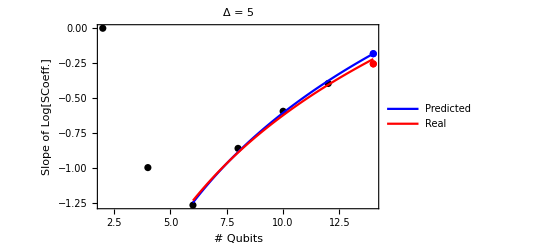

{-0.182446,-0.220439,-0.255295}

```mathematica
CompareN14SlopeHelper2[5]
```

```mathematica
-0.22043924080504507-(-0.25529462408926)
```

0.0348554

#### Result Prediction Table and Residue Graph

```mathematica
SCTabPlotSlopePredictTab = Table[0,Length[DeltaList]];
For [d=1,d≤ Length[DeltaList],d++,
SCTabPlotSlopePredictTab[[d]] = {DeltaList[[d]],CompareN14SlopeHelper[DeltaList[[d]]]};]
```

```mathematica
SCTabPlotSlopePredictTab
```

{{0,{-0.208811,-0.206035}},{1,{-0.218054,-0.185202}},{2,{-0.171523,-0.190701}},{3,{-0.164362,-0.212386}},{4,{-0.171999,-0.23534}},{5,{-0.182446,-0.255295}},{6,{-0.192818,-0.266057}},{7,{-0.202432,-0.266422}},{8,{-0.211197,-0.261932}},{9,{-0.219172,-0.255206}},{10,{-0.226474,-0.247184}},{11,{-0.233163,-0.23665}},{12,{-0.239046,-0.227762}},{13,{-0.243742,-0.219128}},{14,{-0.247243,-0.211026}},{15,{-0.249354,-0.202051}},{16,{-0.246912,-0.1938}},{17,{-0.242239,-0.186361}},{18,{-0.24035,-0.179648}},{19,{-0.233922,-0.173513}},{20,{-0.235841,-0.167359}},{35,{-0.154545,-0.107968}},{50,{-0.0916021,-0.0754588}},{65,{-0.0265387,-0.0608482}},{80,{0.0245428,-0.0441181}},{99,{0.0779734,-0.0349832}}}

```mathematica
ListPlot[<|"Prediced"->Table[{SCTabPlotSlopePredictTab[[i,1]],SCTabPlotSlopePredictTab[[i,2,1]]},{i,1,Length[DeltaList]}],"Real"->Table[{SCTabPlotSlopePredictTab[[i,1]],SCTabPlotSlopePredictTab[[i,2,2]]},{i,1,Length[DeltaList]}]|>,PlotLabels->Automatic,PlotRange-> {-0.5,0.1},PlotStyle-> {Blue,Red},FrameLabel->{{"Slope of Log[SCoeff.]",None},{None,"Δ"}},Frame->{{True,False},{False,True}},FrameTicks->{{All,None},{None,All}},PlotLegends->None]
```

-Graphics-

-Graphics-

## Variant XXZ Model

### Entropy vs. N

#### Data

```mathematica
TabPlotQ0={{2,0.0},{3,0.0},{4,0.0},{5,0.0},{6,0.0},{7,0.0},{8,0.0},{9,0.0},{10,0.0},{11,0.0},{12,0.0}};
TabPlotQ1={{2,0.0},{3,0.0},{4,0.9630865817456329},{5,1.2426432611352836},{6,1.3709505944546692},{7,0.8545525847906812},{8,0.9769402664184298},{9,0.9910760598382208},{10,1.6133787619157416},{11,1.3782889490975896},{12,1.4485756660224118}};
TabPlotQ2={{2,0.0},{3,0.2713368555451211},{4,0.0},{5,0.3336993183429111},{6,0.11467541637666863},{7,0.3072749525748435},{8,0.21895256532666466},{9,0.9369663903265706},{10,0.7651805019568642},{11,0.14403685289494886},{12,0.003281149899142715}};
TabPlotQ3={{2,0.0},{3,0.0},{4,0.1432921506002634},{5,0.5260710538800901},{6,0.01500473848746793},{7,0.1078209868020726},{8,0.016456218982298303},{9,0.0021524265204543643},{10,0.0166028734723329},{11,0.0023658470402957168},{12,0.031192500515014206}};
TabPlotQ4={{2,0.0},{3,0.034918705681418506},{4,0.03669009804380553},{5,0.06181370841621254},{6,0.349574519154192},{7,0.0032818202785046694},{8,0.003464207100690957},{9,0.00026615400353083665},{10,2.044932869165136*10^-5},{11,0.0034756064992756143},{12,2.1638804529106802*10^-5}};
TabPlotQ5={{2,0.2351933818192416},{3,0.01655399136242187},{4,0.01714033626485517},{5,0.017165854928609742},{6,0.000983892856486762},{7,0.2072076711726974},{8,5.12462602236731*10^-5},{9,0.2256760518888467},{10,2.5253860879374923*10^-6},{11,0.23388271621121076},{12,5.322143273022262*10^-5}};
TabPlotQ6={{2,0.0},{3,0.0},{4,0.0},{5,0.009090869506867473},{6,0.1870682526824254},{7,0.009317329127890489},{8,1.3171095239720478*10^-5},{9,0.00037257202210072543},{10,1.3512778226892607*10^-5},{11,1.3512778429871181*10^-5},{12,1.3522260140588404*10^-5}};
TabPlotQ7={{2,0.0},{3,0.1436686791919183},{4,0.145778245736704},{5,0.1460010425371695},{6,0.14598427085026103},{7,0.0},{8,0.00015835469687837522},{9,0.005633486311450997},{10,4.225571596373096*10^-6},{11,4.227069947774852*10^-6},{12,4.223889343774691*10^-6}};
TabPlotQ8={{2,0.0},{3,0.1160898914374686},{4,0.11751967684275468},{5,0.11754968063758423},{6,0.11757204687497215},{7,0.003812762838561196},{8,1.5165027109315383*10^-6},{9,0.0029536602205033286},{10,0.7772348010860431},{11,0.0032652327892981887},{12,0.0033283452797580426}};
TabPlotQ9={{2,0.0},{3,0.0},{4,0.0},{5,0.0021548483828936565},{6,3.850325417523537*10^-5},{7,3.850332068794034*10^-5},{8,3.8944948822593606*10^-5},{9,0.010002556514425073},{10,3.895039927834222*10^-5},{11,0.09561431192011098},{12,0.002176595477372374}};
TabPlotQ10={{2,0.08013604733127488},{3,0.0},{4,0.07260262012704082},{5,0.0014777872775493593},{6,0.0014924895884663538},{7,0.08136002375976527},{8,0.5131745686722864},{9,0.32115892742738406},{10,2.1575498159098905*10^-5},{11,0.07757718822014233},{12,0.03409473802926664}};
TabPlotQ11={{2,0.0},{3,0.0010358561593024837},{4,0.0},{5,0.0010436694511892406},{6,0.049227434370298036},{7,0.00222870509823971},{8,1.3583831111798697*10^-7},{9,1.369050869861182*10^-7},{10,1.2628519881256014*10^-5},{11,1.4004045795913335*10^-9},{12,0.001051542115950555}};
TabPlotQ12={{2,0.0},{3,0.05976932904065263},{4,0.0007610822338267221},{5,0.0007658833333626635},{6,0.06012005783020974},{7,7.686735679740757*10^-6},{8,7.736748901453994*10^-6},{9,7.005506280771986*10^-8},{10,7.73709614067018*10^-6},{11,0.0004149860375705796},{12,4.986381515101747e-12}};
TabPlotQ13={{2,0.052046084774824315},{3,0.052302014259504724},{4,0.0005903171539714246},{5,0.048568017700496215},{6,0.0005764150084145964},{7,4.9263300390976815*10^-6},{8,4.925963401273143*10^-6},{9,4.925963408451745*10^-6},{10,4.926124401197171*10^-6},{11,4.926124400267303*10^-6},{12,7.3986380542279475*10^-6}};
TabPlotQ14={{2,0.0},{3,0.0004319652807665063},{4,0.04638791027690864},{5,0.00043599601458647473},{6,0.0004359548260321466},{7,3.2410170227167158*10^-6},{8,0.00043266498955573486},{9,3.241017426659859*10^-6},{10,1.3661349542766607e-10},{11,0.017794493000381776},{12,0.0004360207829634441}};
TabPlotQ15={{2,0.0},{3,0.0},{4,0.0003371800536884195},{5,0.0003371899615300687},{6,0.00033852883339915556},{7,0.00033855961931699856},{8,0.0066798961757077715},{9,0.00034342299322829417},{10,7.025077349978831e-11},{11,1.2812616863743379*10^-8},{12,1.2812614796631969*10^-8}};
TabPlotQ16={{2,0.0},{3,0.0},{4,0.00026615056567491294},{5,0.0},{6,1.5165027125332582*10^-6},{7,1.5165028000480693*10^-6},{8,0.03667459063575371},{9,0.000269023193023719},{10,0.01685431270589333},{11,3.768870814038739e-11},{12,1.750150537035865e-13}};
TabPlotQ17={{2,0.0},{3,0.0},{4,0.00021302833264608506},{5,0.00021303069996494398},{6,0.032466237548595414},{7,0.0},{8,1.0793267603448803*10^-6},{9,0.032602952959575465},{10,0.03221885086204199},{11,4.910655079268064*10^-9},{12,0.00036823009723245927}};
TabPlotQ18={{2,0.0},{3,0.0001721431686503017},{4,0.0001726321186371789},{5,0.030238680730697538},{6,7.78021582390832*10^-7},{7,7.780216011067612*10^-7},{8,7.802917834235265*10^-7},{9,0.0001746034314533918},{10,0.00017344769535876468},{11,0.00017312548271216217},{12,3.9168729702248375*10^-5}};
TabPlotQ19={{2,0.0},{3,0.00014109254216161361},{4,0.02758981409529681},{5,0.00014145378870670562},{6,0.00014181491644770156},{7,0.013196734167852749},{8,0.027233954584189188},{9,2.085906902711583*10^-9},{10,5.739302200934575*10^-7},{11,2.0914466606902076*10^-9},{12,2.110906801127243e-14}};
TabPlotQ20={{2,0.0},{3,0.00011679314912744018},{4,0.00011706433130320783},{5,0.025265721918470027},{6,0.015642130070126558},{7,4.27722867932869*10^-7},{8,0.0007991212194880436},{9,0.02474396929539727},{10,0.01627244630490145},{11,0.00011733578557233357},{12,1.41033976775356*10^-9}};
TabPlotQ35={{2,0.009544738800759098},{3,1.4622615940596504*10^-5},{4,0.00955839189074796},{5,1.4644910317851422*10^-5},{6,1.7526515784509154*10^-8},{7,1.5040091516331771*10^-5},{8,1.7540182220778928*10^-8},{9,1.4644589546393328*10^-5},{10,1.4644956934118359*10^-5},{11,1.7540192883087767*10^-8},{12,1.754019353245318*10^-8}};
TabPlotQ50={{2,0.0},{3,0.0},{4,3.8604062806326305*10^-6},{5,0.004417671874743958},{6,2.2595731388557224*10^-9},{7,3.845104732531187*10^-6},{8,0.004458903887039908},{9,1.1933418377605077*10^-12},{10,0.005093852786863473},{11,0.005093853433536795},{12,2.2604338595845527*10^-9}};
TabPlotQ65={{2,0.0031915762864687235},{3,0.0031922507090558893},{4,1.4303233026679197*10^-6},{5,1.45570909464703*10^-6},{6,1.430803207456554*10^-6},{7,1.4306183422220846*10^-6},{8,0.0012755709023396877},{9,4.983509686504172*10^-10},{10,0.0026534907353711707},{11,1.4306428616283238*10^-6},{12,1.5379698373952454E-13}};
TabPlotQ80={{2,0.0},{3,0.0022010053516501797},{4,6.525978216656069*10^-7},{5,6.525978371574774*10^-7},{6,6.52694299173767*10^-7},{7,6.447095531679514*10^-7},{8,6.527961609278057*10^-7},{9,0.002201314697476906},{10,3.3032961956276737*10^-14},{11,6.5269431594321*10^-7},{12,0.0}};
TabPlotQ99={{2,0.0},{3,0.0014999831181667703},{4,2.910705527591978*10^-7},{5,0.001500121141772942},{6,0.001500121155853602},{7,2.910987202652381*10^-7},{8,4.3785190116410336*10^-11},{9,2.9109636558997814*10^-7},{10,0.0015001211558587169},{11,4.378288395492047*10^-11},{12,2.910987233032487*10^-7}};
```

#### Plot

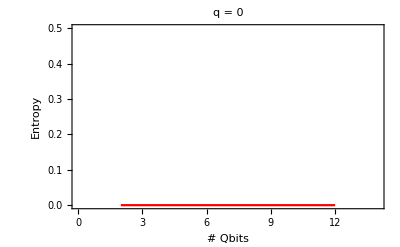
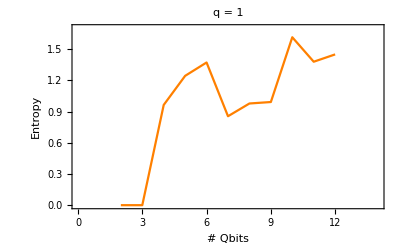
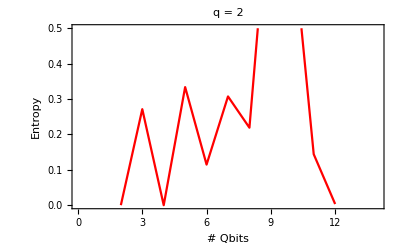
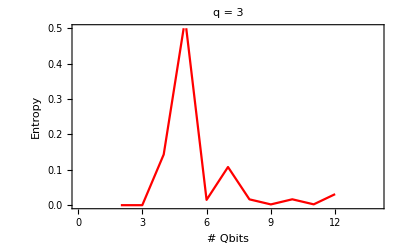
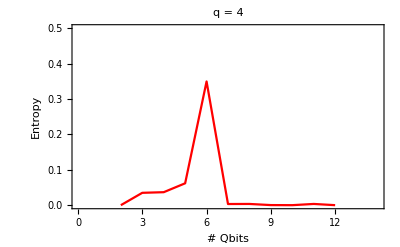
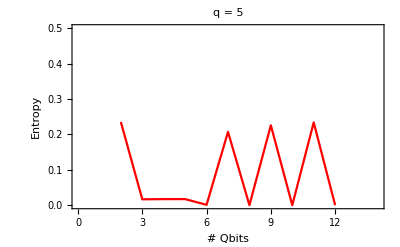
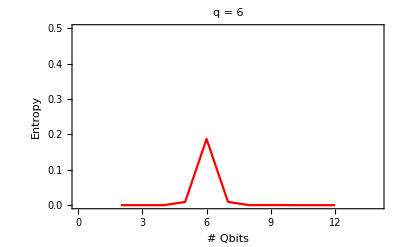
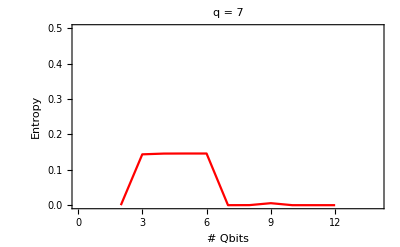
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
saveGV = Grid[{{ListLinePlot[TabPlotQ0,PlotStyle->{Red},PlotRange->{{0,14},{0,0.5}},PlotLabel->"q = 0",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotQ1,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Orange},PlotLabel->"q = 1",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotQ2,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 2",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotQ3,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 3",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotQ4,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 4",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},{ListLinePlot[TabPlotQ5,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 5",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotQ6,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 6",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotQ7,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 7",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotQ8,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 8",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotQ9,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 9",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},
{ListLinePlot[TabPlotQ10,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 10",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotQ11,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 11",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotQ12,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 12",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotQ13,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 13",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotQ14,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 14",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},
{ListLinePlot[TabPlotQ15,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 15",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotQ16,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 16",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotQ17,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 17",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotQ18,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 18",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotQ19,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 19",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},
{ListLinePlot[TabPlotQ20,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 20",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotQ35,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Blue},PlotLabel->"q = 35",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotQ50,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Blue},PlotLabel->"q = 50",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotQ65,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Blue},PlotLabel->"q = 65",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotQ80,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Blue},PlotLabel->"q = 80",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotQ99,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Blue},PlotLabel->"q = 99",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]}},Spacings->{0.5,0.5}]
```

#### Plot for Latex

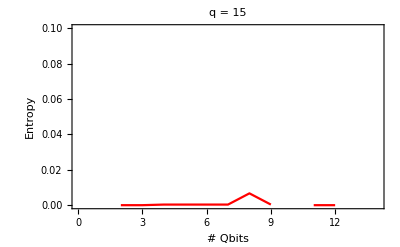
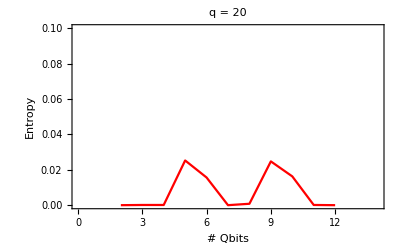
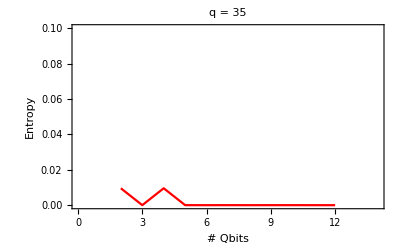
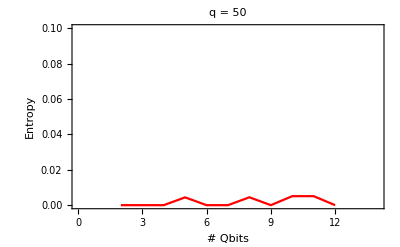
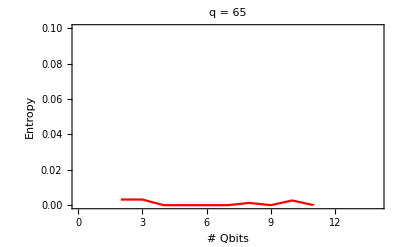
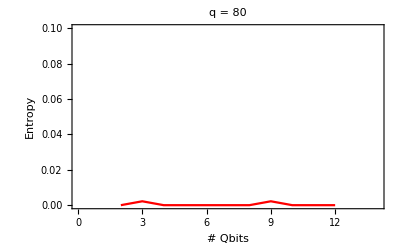
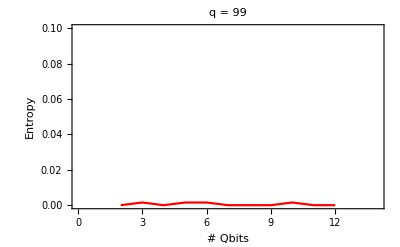
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
aveGV = Grid[{{ListLinePlot[TabPlotQ0,PlotStyle->{Red},PlotRange->{{0,14},{0,0.5}},PlotLabel->"q = 0",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotQ1,PlotRange->{{0,14},{0,1.7}},PlotStyle->{Orange},PlotLabel->"q = 1",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotQ2,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 2",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotQ3,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 3",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotQ4,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 4",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},{ListLinePlot[TabPlotQ5,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 5",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotQ10,PlotRange->{{0,14},{0,0.5}},PlotStyle->{Red},PlotLabel->"q = 10",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotQ15,PlotRange->{{0,14},{0,0.1}},PlotStyle->{Red},PlotLabel->"q = 15",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotQ20,PlotRange->{{0,14},{0,0.1}},PlotStyle->{Red},PlotLabel->"q = 20",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotQ35,PlotRange->{{0,14},{0,0.1}},PlotStyle->{Red},PlotLabel->"q = 35",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},{ListLinePlot[TabPlotQ50,PlotRange->{{0,14},{0,0.1}},PlotStyle->{Red},PlotLabel->"q = 50",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotQ65,PlotRange->{{0,14},{0,0.1}},PlotStyle->{Red},PlotLabel->"q = 65",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],
ListLinePlot[TabPlotQ80,PlotRange->{{0,14},{0,0.1}},PlotStyle->{Red},PlotLabel->"q = 80",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[TabPlotQ99,PlotRange->{{0,14},{0,0.1}},PlotStyle->{Red},PlotLabel->"q = 99",FrameLabel->{{"Entropy",None},{"# Qbits",None}},Frame->{{True,False},{True,False}},FrameTicks->All]}},Spacings->{0.5,0.5}]
```

## Test - Need

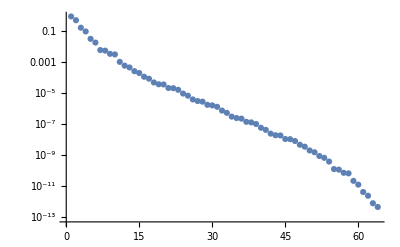

```mathematica
ttt ={ 0.8519078546455119,0.4884374902374368,0.16075016694622327,0.09216537641988728,0.030821861402653125,0.01767157392183261,0.00581590994736339,0.005338447304288863,0.003334525491984322,0.0030607744591774773,0.0010073346439036337,0.0005775507322939933,0.000441267872407565,0.000252998925817907,0.00019314399089163895,0.0001107382279094049,8.326473781254386*10^-05,4.7739458370635716*10^-05,3.6445172574912715*10^-05,3.539877375600384*10^-05,2.08956737829073*10^-05,2.0295725783792683*10^-05,1.596498627242726*10^-05,9.153452200325625*10^-06,6.679547277285767*10^-06,3.829688023477612*10^-06,3.012502108764189*10^-06,2.7651878909983043*10^-06,1.7272043699468147*10^-06,1.5854078891009047*10^-06,1.280720787594844*10^-06,7.342954332261182*10^-07,5.217752280276981*10^-07,2.991574516706576*10^-07,2.4166472852161343*10^-07,2.218250334350581*10^-07,1.385573719405328*10^-07,1.2718237307945657*10^-07,1.0004396305432107*10^-07,5.735975077277473*10^-08,4.1857122184137394*10^-08,2.3998590458282875*10^-08,1.887772680325028*10^-08,1.833571727560542*10^-08,1.0823458741340599*10^-08,1.0512700042301437*10^-08,8.025586829114561*10^-09,4.6014336463506415*10^-09,3.459845560688451*10^-09,1.9836867058053194*10^-09,1.5143825885863254*10^-09,8.682643487874605*10^-10,6.633827216535744*10^-10,3.8034745374780755*10^-10,1.2517652719313726*10^-10,1.149000598284978*10^-10,7.176939980237339*10^-11,6.587743081319172*10^-11,2.1680987411858566*10^-11,1.243070675749083*10^-11,4.157037443489076*10^-12,2.3834360298930754*10^-12,7.84422426153386*10^-13,4.497361063914498*10^-13};
Show[ListLogPlot[ttt]]
```

```mathematica
Plot[E^(-0.55x),{x,0.1,100}]
```

```mathematica
+++---;
---+++;
++-+--;
--+-++
```